# xCPS

## Covariant Phase Space Formalism for xAct

Juan Margalef-Bentabol

juan.margalef@umontreal.ca
Université de Montréal, Canada

Laura Sánchez Cotta

100527266@alumnos.uc3m.es
Universidad Carlos III de Madrid, Spain

xCPS is a package to work within the Covariant Phase Space formalism. It is built on top of xAct, a free package for fast manipulation of abstract tensor expressions that can be downloaded from http://www.xact.es. 

The latest version of xCPS is available at: https://github.com/juanmargalef/xCPS

xCPS is distributed under the GNU General Public License (© 2025).

For further resources, user discussions, and additional contributed packages, see:
- xAct forum: http://groups.google.com/group/xAct
- xAct contributions: https://contrib.xact.es

## Chapter. Introduction

## Chapter.Section. xCPS in a nutshell

The package xCPS deals with the Covariant Phase Space (CPS) formalism for field theories. xCPS allows, among other things, to obtain from a given Lagrangian:
  - the Equations of Motion (EOM)
  - the canonical symplectic form
  - check if a transformation is a symmetry 
  - find the Noether charge associated with a symmetry

It is worth noting that it can handles generic Lagrangians of the type L(tensors) such as f(Riem) theories.

xCPS implements two functionalities that might be of interest to a broader audience: 
  - checking if an expression is a divergence  
  - obtain the “potential” T^bc of a gradient like ∇_a T^bc

If you found this package useful in one of your papers, please consider citing the companion papers:

xCPS: an xAct package for covariant phase space, Noether charges, and entropy
Juan Margalef-Bentabol
arXiv preprint [2606.05204]

Geometric formulation of the covariant phase space methods with boundaries
Juan Margalef-Bentabol and Eduardo J. S. Villaseñor
Phys. Rev. D 103 (2021) 025011 [arXiv: 2008.01842]

## Chapter.Section. Theoretical framework

### Chapter.Section.Subsection. Main references

xCPS is mostly based in the theoretical work of one of the authors of the package:

Geometric formulation of the covariant phase space methods with boundaries
Juan Margalef-Bentabol and Eduardo J. S. Villaseñor
Phys. Rev. D 103 (2021) 025011 [arXiv: 2008.01842]

The underlying mathematical formalism of this paper is heavily influenced by

The variational bicomplex
Ian M. Anderson 
Utah State Technical Report (1989)

We refer the reader to these two references and references therein for further mathematical details.

### Chapter.Section.Subsection. Additional references

For additional context and examples, we suggest the following references:

Action principles and global geometry
Gregg J. Zuckerman
Mathematical aspects of string theory (1987) 259-284

Covariant description of canonical formalism in geometrical theories
Cedomir Crnkovic and Edward Witten
Three hundred years of gravitation (1987) 676-684

Proof of the equivalence of the symplectic forms derived from the canonical and the covariant phase space formalisms
Juan Margalef-Bentabol and Eduardo J.S. Villaseñor
Phys. Rev. D Letters 106 (2022) 025011 [arXiv: 2204.06383]

On the on-shell equivalence of general relativity and Holst theories with nonmetricity, torsion, and boundaries
J. Fernando Barbero G., Juan Margalef-Bentabol, Valle Varo, and Eduardo J.S. Villaseñor
Phys. Rev. D 105 (2022) 064066 [arXiv: 2201.12141]

Palatini gravity with nonmetricity, torsion, and boundaries in metric and connection variables
Fernando Barbero G., Juan Margalef-Bentabol, Valle Varo, and Eduardo J.S. Villaseñor
Phys. Rev. D 104 (2021) 044046 [arXiv: 2105.07053]

Covariant phase space for gravity with boundaries: metric vs tetrad formulations
J. Fernando Barbero G., Juan Margalef-Bentabol, Valle Varo, and Eduardo J.S. Villaseñor
Phys. Rev. D 104 (2021) 044048 [arXiv: 2103.06362]

Some Properties of Noether Charge and a Proposal for Dynamical Black Hole Entropy
Vivek Iyer and Robert M. Wald
Phys. Rev. D 50 (1994) 846 .08[arXiv: gr-qc/9403028]

## Chapter.Section. Implementation in Mathematica

### Chapter.Section.Subsection. Motivation of xCPS and how to read this notebook

This package originated with the idea of using xPert to implement the Covariant Phase Space formalism. However, the need to include a super-commutative product made necessary further adaptations similar to the ones introduced in xTerior. Thus, some of the core parts of xCPS owe much to xTerior and xPert.

We recommend to those readers only interested in the field theory examples to check the following Chapters:

Chapter Chapter: a quick study of the scalar field and General Relativity (GR)

Chapter Chapter: a detail study of the scalar field

Chapter Chapter: a detail study of the electromagnetic theory

Chapter Chapter: a detail study of GR

Chapter Chapter: a detail study of generic f(Riem), f(Ric), and f(R) theories

Additionally, Chapter Chapter provides an introduction to some of the basic commands of the package.

Chapters Chapter-Chapter, together with the Appendix, contain more technical details. These sections are intended for readers who wish to explore the finer aspects of the package or apply it to more involved examples.

### Chapter.Section.Subsection. Installing xCPS

For instructions on how to install xAct and xCPS, see Appendix A.Section.

### Chapter.Section.Subsection. Loading xCPS

```mathematica
ClearAll["Global`*"]

<<xAct`xCPS`
$PrePrint=ScreenDollarIndices;

(* Set options for ContractMetric *)
SetOptions[ContractMetric,AllowUpperDerivatives -> True];
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.4, {2025,12,29}

CopyRight (C) 2003-2026, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor` version 1.3.0, {2025,12,29}

CopyRight (C) 2002-2026, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCPS` version 1.1.0, {2026,5,23}

CopyRight (C) 2025, Juan Margalef-Bentabol and Laura Sánchez Cotta, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

### Chapter.Section.Subsection. Lists of xCPS commands

The functions defined by xCPS are the following:

```mathematica
Information[xAct`xCPS`Private`FunctionsxCPS]
```

The constants defined by xCPS are the following:

```mathematica
Information[xAct`xCPS`Private`ConstantsxCPS]
```

The options and types defined by xCPS are the following:

```mathematica
Information[xAct`xCPS`Private`RestxCPS]
```

## Chapter. Initial examples out of the box

## Chapter.Section. Field theory examples

### Chapter.Section.Subsection. Initial definitions

In this Chapter, we hope to showcase how accessible xCPS is: with just a handful of commands and no required knowledge of the inner workings, we will show all the physical information that can be extracted for two relevant examples, the scalar field theory and General Relativity (GR). In this Chapter we will only scratch the surface of xCPS’s capabilities and we will revisit both examples in Chapters Chapter and Chapter where we will use the full power of the package. Although we encourage everyone to read the full documentation thoroughly, for those only interested in the field theory examples, we recommend to read, apart from the aforementioned Chapters, also Chapter Chapter (electromagnetism) and Chapter Chapter (generic f(Riem), f(Ric) and f(R) theories).

We start by defining the manifold we are going to work on, as well as the metrics and tensors we will use.

```mathematica
$DefInfoQ=False;
(* Set to False for the initial examples, we will set it to True later and explain all the new messages *)

DefConstantSymbol[dimen]
DefManifold[M,dimen,{a,b,c,d,e,f,h,i,j,k,l}]
DefTensor[phi[],M,PrintAs->"ϕ"]
DefMetric[-1,g[-a,-b],LCDer,{";","∇"}] 
DefTensor[xi[a],M,PrintAs->"ξ"]
```

### Chapter.Section.Subsection. Lagrangians

We consider the Lagrangian densities for the scalar field and for General Relativity (GR):

```mathematica
Lscalar=1/2 g[a,b]LCDer[-a]@phi[]LCDer[-b]@phi[] √(-Determinant[g][])
LGR=RicciScalarLCDer[] √(-Determinant[g][])
```

1/2 √(-g^OverTilde[~]) g | a | b
  |   ∇_a ϕ ∇_b ϕ

√(-g^OverTilde[~]) R[∇]

### Chapter.Section.Subsection. Equations of motion (EOM)

EOM[field, der][Lagrangian]
It returns the Equations of Motion of 'Lagrangian' with respect to 'field'.

The argument 'der' is optional. If not specified, it finds the only CovD present. If more than one is present, we have to specify which one should be used to perform “integration by parts” (Leibniz rule).

In this case we obtain the wave equation for Lscalar and the Einsteins equation for LGR.

```mathematica
WaveEq=EOM[phi][Lscalar]//ContractMetric
EinsteinEq=EOM[g][LGR]//ContractMetric//Simplification
```

-√(-g^OverTilde[~]) ∇_a ∇^a ϕ

1/2 √(-g^OverTilde[~]) (-2 R[∇] | a | b
  |  +g | a | b
  |   R[∇])

### Chapter.Section.Subsection. Energy momentum-tensor

EnergyMomentum[Lagrangian]
It returns the Energy Momentum tensor of 'Lagrangian'.

```mathematica
EnergyMomentumLScalar=EnergyMomentum[Lscalar ]//ContractMetric//Simplification
```

∇^a ϕ ∇^b ϕ-1/2 g | a | b
  |   ∇_c ϕ ∇^c ϕ

This is equivalent to the EOM with respect to the main non-frozen metric multiplied by -2/(√(-g^OverTilde[~])) (with a “plus” if we take the variation with respect to the inverse metric, which will be explained in Subsubsection Chapter.Section.Subsection.Subsubsection).

```mathematica
-2/(√(-Overscript[g, OverTilde[~]]))EOM[g][Lscalar]//ContractMetric//Simplification
```

∇^a ϕ ∇^b ϕ-1/2 g | a | b
  |   ∇_c ϕ ∇^c ϕ

### Chapter.Section.Subsection. Symplectic potential

SymplecticPotential[tensors, der][Lagrangian]
It computes the symplectic potential from the 'Lagrangian'.

When considering the variation of a Lagrangian that depends on N different tensor fields {ϕ^i}_(i=1,...,N), if we perform the Leibniz rule in the variation of the fields (“integration by parts”), we obtain one of the most relevant equations for xCPS (see [ItemNumbered,ItemNumbered])

ⅆL=EOM_i ⅆ ϕ^i+dΘ

where:
• ⅆ, sometimes denoted δ in the physics literature, is the exterior derivative in the space of fields and can also be understood as the variational operator (see Section Chapter.Section for further details).
• EOM_i, sometimes denoted  in the physics literature, is the Equation of Motion with respect to the tensor field ϕ^i.
• Θ the symplectic potential of the Lagrangian which is only defined up to a total derivative (it is well defined upon integration on a manifold with no boundary).

The term dΘ (which can also be written as a divergence) is sometimes called the boundary term since, when integrating, it goes to the boundary.

```mathematica
SymplecticPotential[][Lscalar]//ContractMetric//Simplification
SymplecticPotential[][LGR]//ContractMetric//Simplification
```

√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ

√(-g^OverTilde[~]) (n_∇) | a
  (-∇_a (ⅆg) | b |  
  | b+∇_b (ⅆg) |   | b
a |  )

Remark: The tensor (n_∇) | a
  is multipurpose and admits several interpretations. AA more detailed account will be given in Subsection Chapter.Section.Subsection, but let us outline a few key points here. First, it can be used to contract the free index, yielding a scalar expression that is more convenient to work with. Second, when the pullback of Θ is integrated over a Cauchy surface, (n_∇) | a
  represents the normal to that hypersurface. Finally, it may also be interpreted as a covariant derivative, although this interpretation is more subtle and will be addressed in detail in Subsection Chapter.Section.Subsection and Subsubsection Chapter.Section.Subsection.Subsubsection.

### Chapter.Section.Subsection. Symplectic current

SymplecticCurrent[tensors, der][Lagrangian]
It computes the symplectic current associated to the given 'Lagrangian'.

Taking the exterior derivative (variation) of the symplectic potential, we obtain the symplectic current (defined up to a total derivative):

ω=ⅆΘ

There is an overall sign $SymplecticCurrentSign that is taken by default =1.

$SymplecticCurrentSign
It defines the global sign of the symplectic current.

```mathematica
$SymplecticCurrentSign
```

1

```mathematica
SymplecticCurrent[][Lscalar]//ContractMetric//Simplification
SymplecticCurrent[][LGR]//ContractMetric//Simplification
```

-1/2 √(-g^OverTilde[~]) (n_∇) | a
  (2 ((ⅆϕ)⩕∇_a (ⅆϕ))+((ⅆϕ)⩕(ⅆg) | b |  
  | b) ∇_a ϕ-2 ((ⅆϕ)⩕(ⅆg) |   |  
a | b) ∇^b ϕ)

1/2 √(-g^OverTilde[~]) (n_∇) | a
  ((ⅆg) |   | b
a |  ⩕∇_b (ⅆg) | c |  
  | c-(ⅆg) | b |  
  | b⩕∇_a (ⅆg) | c |  
  | c+(ⅆg) | b |  
  | b⩕∇_c (ⅆg) |   | c
a |  +(ⅆg) | b | c
  |  ⩕∇_a (ⅆg) |   |  
b | c-2 ((ⅆg) | b | c
  |  ⩕∇_c (ⅆg) |   |  
a | b))

Remark: The symbol ⩕ denotes the wedge operation in the space of fields, i.e., the antisymmetrized tensor product in the infinite-dimensional space of fields. A detailed explanation will be provided in Section Chapter.Section.

If we want to indicate that the only variable field is ϕ (thus ⅆg=0):

```mathematica
SymplecticCurrent[phi][Lscalar]//ContractMetric//Simplification
```

-√(-g^OverTilde[~]) (n_∇) | a
  ((ⅆϕ)⩕∇_a (ⅆϕ))

which is (up to some technicalities [ItemNumbered]) the canonical symplectic structure (position times momenta).

Warning: One has to be careful when comparing formulas from books and articles, first because of the sign convention $SymplecticCurrentSign, and second because the integration introduces a minus sign due to the orientations.

### Chapter.Section.Subsection. Wald’s entropy

We can easily compute some terms appearing in the computation of the Wald’s entropy [ItemNumbered]:

```mathematica
EOM[RiemannLCDer][LGR]//ContractMetric//Simplification
```

1/2 √(-g^OverTilde[~]) (-g | a | d
  |   g | b | c
  |  +g | a | c
  |   g | b | d
  |  )

### Chapter.Section.Subsection. Noether symmetries

#### Chapter.Section.Subsection.Subsubsection. Variational Vector Fields (VVF)

VVFFromLieD[vector][tensors]
It defines the variational vector field

    LieD[vector][tensor]⩕VariationalVector[tensor]

 with the appropriate contracted indices.

We call variational vector fields (VVF) to the vector fields over the space of fields. VVFs together with the corresponding commands, will be explained in detail on Section Chapter.Section, but roughly speaking, they describe the infinitesimal transformation (first order perturbation) in the space of fields. On xCPS they are defined as scalar where each monomial has a variational vector (with no CovD, LieD... in front of it). For instance:

```mathematica
vvf1=VVFFromLieD[xi][phi]
```

(δ/δϕ) (ℒ_ξ ϕ)

describes the infinitesimal transformation (see [ItemNumbered,ItemNumbered]) given by the Lie Derivative: ϕ->ϕ+ϵℒ_ξ ϕ.

Remark: In the physics literature a formal integral is usually added:

vvf1=∫ (ℒ_ξ ϕ)(δ/δϕ)

But from an operational point of view, it plays no role and, in order to take advantage of the xAct framework, we will simply consider the scalar integrand.

#### Chapter.Section.Subsection.Subsubsection. NoetherSymmetryQ

NoetherSymmetryQ[vvf][metric, option][Lagrangian]
It tests if the vector field 'vvf' is a Noether symmetry of 'Lagrangian' using 'metric'.

- Option:
  ∗ CheckZero→True uses === instead of == to test if EOMs vanish.

This function checks if the transformation VertLie[vvf][Lagrangian] is a total divergence using an auxiliary metric (see [ItemNumbered] and Section Chapter.Section for further details). The way to check if the expression is a total divergence is through DivergenceQ (explained below in Subsection Chapter.Section.Subsection), which makes sure that the EOMs with respect to each field appearing in the expression are zero.

Remark: If no EOMs are present, that actually means that the term is topological. This is equivalent to be a divergence if we assume that the vector bundle is contractible (see [ItemNumbered] for further detail). There are of course topological Lagrangians that are not global divergences (just pointwise) like the Gauss-Bonnet term in dimension≤4 or Einstein-Hilbert Lagrangian in dimension=2 (see also [ItemNumbered, Example 5.10 on page 207] for an interesting example of a non-exact Lagrangian with no EOM).

```mathematica
NoetherSymmetryQ[vvf1][g][Lscalar]
```

∇_a ϕ ∇_b ∇^b ϕ==0&&∇^c ϕ (∇^a ξ |  
c ∇^b ϕ+∇^a ϕ ∇^b ξ |  
c-g | a | b
  |   ∇_d ξ |  
c ∇^d ϕ)+ξ | c
  (∇^b ϕ ∇_c ∇^a ϕ+∇^a ϕ ∇_c ∇^b ϕ-g | a | b
  |   ∇_d ∇_c ϕ ∇^d ϕ)==0&&ξ | a
  ∇_a ∇_b ∇^b ϕ+∇_a ξ | a
  ∇_b ∇^b ϕ==∇^a ϕ ∇_b ∇^b ξ |  
a+ξ | a
  ∇_b ∇^b ∇_a ϕ+2 ∇_b ∇_a ϕ ∇^b ξ | a

Sometimes the expressions are not immediately zero but they are after applying some functions (see below the case for vvf2 ). If the user is convinced that this is not zero (as it is the case), one can add the option CheckZero→True which uses === instead of ==

```mathematica
NoetherSymmetryQ[vvf1][g,CheckZero->True][Lscalar]
```

False

We can consider another transformation like:

```mathematica
vvf2=VVFFromLieD[xi][g,phi]
```

(δ/δg) | a | b
  |   (ℒ_ξ g |   |  
a | b)+(δ/δϕ) (ℒ_ξ ϕ)

which describes the infinitesimal transformation: ϕ->ϕ+ϵℒ_ξ ϕ+(ϵ^2) and g->g+ϵℒ_ξ g+(ϵ^2) ( VVF2 is sometimes denoted δ_ξ in the physics literature). This means that all fields appearing in the Lagrangian are transformed using the Lie derivative (no background objects are present, see [ItemNumbered]). In fact, whenever VVF is a VVFFromLieD[xi], we always have

𝕃_VVFFromLieD[ξ][Lagrangian]=L_ξ[Lagrangian]=d(i_ξ Lagrangian)

which is exact (a divergence).

```mathematica
NoetherSymmetryQ[vvf2][g][Lscalar]
NoetherSymmetryQ[vvf2][g,CheckZero->True][Lscalar] (* Notice how in this case this is incorrect, so this option must be used with caution *)
NoetherSymmetryQ[vvf2][g][Lscalar]//SortCovDs//ContractMetric//Simplification
```

∇_a ∇_b ξ | b
  ∇^a ϕ+ξ | a
  ∇_b ∇^b ∇_a ϕ==ξ | a
  ∇_a ∇_b ∇^b ϕ+∇^a ϕ ∇_b ∇_a ξ | b

False

True

Remark: Incidentally, this proves that VVF1=(δ/δϕ)(ℒ_ξ ϕ) for a given g-Killing vector field ξ is also a Noether Symmetry of Lscalar since in that case VVF1=VVF2.

Let us finally check that this type of transformations are also Noether symmetries of LGR:

```mathematica
vvf3=VVFFromLieD[xi][g]
NoetherSymmetryQ[vvf3][g][LGR]
```

(δ/δg) | a | b
  |   (ℒ_ξ g |   |  
a | b)

∇_a R[∇]==2 ∇_c R[∇] |   | c
a |  &&2 R[∇] | b |  
  | c ∇^a ξ | c
 +2 R[∇] | a |  
  | c ∇^b ξ | c
 +2 ∇^b ∇^a ∇_c ξ | c
 +2 ξ | c
  ∇_c R[∇] | a | b
  |  +∇_c ∇^c ∇^a ξ | b
 +∇_c ∇^c ∇^b ξ | a
 +3 g | a | b
  |   ∇_c ∇_d ∇^d ξ | c
 ==∇_c ∇^a ∇^b ξ | c
 +∇_c ∇^a ∇^c ξ | b
 +∇_c ∇^b ∇^a ξ | c
 +∇_c ∇^b ∇^c ξ | a
 +g | a | b
  |   (ξ | c
  ∇_c R[∇]+∇_d ∇_c ∇^d ξ | c
 +2 ∇_d ∇^d ∇_c ξ | c
 +2 R[∇] |   |  
c | d ∇^d ξ | c
 )

Here we need to apply the Bianchi identities. This can be done systematically with other packages (like TInvar or xTras) but to make this notebook self-contained, we define ApplyBianchi:

```mathematica
BianchiContracted1=MakeRule[{LCDer[-e]@RiemannLCDer[-a,-c,-d,e],$RicciSign(LCDer[-c]@RicciLCDer[-a,-d]-LCDer[-a]@RicciLCDer[-c,-d])},MetricOn->All];
BianchiContracted2=MakeRule[{LCDer[-b]@RicciScalarLCDer[],2LCDer[-a][RicciLCDer[a,-b]]},MetricOn->All];
BianchiRiemann=MakeRule[{RiemannLCDer[a,b,c,d],RiemannLCDer[a,c,b,d]-RiemannLCDer[a,d,b,c],OrderedQ[{a,b,c,d}]},MetricOn->All];
ApplyBianchi[expr_]:=expr//.BianchiContracted1//.BianchiContracted2//.BianchiRiemann;

NoetherSymmetryQ[vvf3][g][LGR]//SortCovDs//Simplification
NoetherSymmetryQ[vvf3][g][LGR]//SortCovDs//Simplification//ApplyBianchi//ContractMetric//Simplification
```

∇_a R[∇]==2 ∇_c R[∇] |   | c
a |  &&2 R[∇] | b |  
  | c ∇^a ξ | c
 +2 R[∇] | a |  
  | c ∇^b ξ | c
 +2 ξ | c
  ∇_c R[∇] | a | b
  |  +ξ | c
  ∇_d R[∇] | a | b |   | d
  |   | c |  +R[∇] | a | b |   |  
  |   | c | d ∇^d ξ | c
 +R[∇] | a |   | b |  
  | d |   | c ∇^d ξ | c
 +2 g | a | b
  |   g | d | e
  |   ξ | c
  ∇_e R[∇] |   |  
c | d==2 g | b | d
  |   R[∇] |   |  
c | d ∇^a ξ | c
 +2 g | a | d
  |   (ξ | c
  ∇^b R[∇] |   |  
c | d+R[∇] |   |  
c | d ∇^b ξ | c
 )+g | a | b
  |   ξ | c
  ∇_c R[∇]+ξ | c
  ∇_d R[∇] | a |   | b | d
  | c |   |  +ξ | c
  ∇_d R[∇] | a | d | b |  
  |   |   | c+R[∇] | a |   | b |  
  | c |   | d ∇^d ξ | c

True

#### Chapter.Section.Subsection.Subsubsection. SymmetryPotential

We have seen that NoetherSymmetryQ[vvf][metric][Lagrangian] checks if

𝕃_vvf[Lagrangian]=div(S_vvf)

for some “potential” (S_VVF)^a.

SymmetryPotential[vvf, iteration][der][Lagrangian, optionalfunctions]
It computes the potential associated with a Noether symmetry 'vvf'. It is given by a vector S^a such that 


          VertLie[vvf]@Lagrangian=der[-a][S[a]].

- 'iteration' is an optional positive integer that limits the amount of iteration in order to obtain the middle steps.
- 'optionalfunctions' are functions that are applied in the intermediate steps to simplify the expressions.

This command calls the more general command FindPotentialDivergence (see Subsection Chapter.Section.Subsection below for further details), which attempts to find such vector (it is obviously defined up to an exact term i.e. ∇_b T^ab for some antisymmetric tensor T^ab). 

There is no guarantee that this algorithm will find the result:

```mathematica
SymmetryPotential[vvf3][g][LGR]
```

FindPotentialGradient::loopzero: Loop detected at iteration 4. Search aborted. Provide the optional 'iteration' argument to obtain partial results or try applying intermediate simplification functions.

0

In order to understand what is failing, we can limit the iterations performed by the algorithm:

```mathematica
SymmetryPotential[vvf3][g,1][LGR]//SortCovDs//ContractMetric//Simplification
SymmetryPotential[vvf3][g,2][LGR]//SortCovDs//ContractMetric//Simplification
SymmetryPotential[vvf3][g,3][LGR]//SortCovDs//ContractMetric//Simplification
SymmetryPotential[vvf3][g,7][LGR]//SortCovDs//ContractMetric//Simplification
```

√(-g^OverTilde[~]) (n_∇) | a
  ∇_b ∇_a ξ | b

√(-g^OverTilde[~]) (n_∇) | a
  (∇_b ∇_a ξ | b
 +∇_b ∇^b ξ |  
a)

√(-g^OverTilde[~]) (n_∇) | a
  (2 R[∇] |   |  
a | b ξ | b
 -∇_b ∇_a ξ | b
 +∇_b ∇^b ξ |  
a)

FindPotentialGradient::loop: Loop detected at iteration 4. Returning the accumulated potential. Try applying intermediate simplification functions.

√(-g^OverTilde[~]) (n_∇) | a
  (2 R[∇] |   |  
a | b ξ | b
 -∇_b ∇_a ξ | b
 +∇_b ∇^b ξ |  
a)

The problem is that the algorithm is looping because the Contracted Bianchi formula is not applied. We can force its application at intermediate steps:

```mathematica
SymmetryPotentialvvf3LGR1=SymmetryPotential[vvf3][g][LGR,ApplyBianchi]//SortCovDs//ContractMetric//Simplification
```

√(-g^OverTilde[~]) (n_∇) | a
  (R[∇] ξ |  
a-∇_b ∇_a ξ | b
 +∇_b ∇^b ξ |  
a)

Remark: We have seen that if 'vvf' is a Noether symmetry, then we have a symmetry potential S_VVF satisfying (DisplayFormulaNumbered). Moreover, if 'vvf' is defined through the Lie derivative (VVFFromLieD), then according to (DisplayFormulaNumbered), we could have taken S_VVF=i_ξ L.

```mathematica
SymmetryPotentialvvf3LGR2 =NormalOfLCDer[a]xi[-a]LGR
difference=SymmetryPotentialvvf3LGR2-SymmetryPotentialvvf3LGR1//SortCovDs//Simplification
```

√(-g^OverTilde[~]) (n_∇) | a
  R[∇] ξ |  
a

√(-g^OverTilde[~]) (n_∇) | a
  (∇_b ∇_a ξ | b
 -∇_b ∇^b ξ |  
a)

We see that the symmetry potentials do not agree. However, they are equal up to a divergence/exact term, as expected for any potential (see Subsection Chapter.Section.Subsection for an explanation of NormalOfCovDToCovD).

```mathematica
difference//NormalOfCovDToCovD//SortCovDs//Simplification//ContractMetric
```

0

We can obtain different (but obviously equivalent) potentials by applying different functions in the middle steps:

```mathematica
SymmetryPotentialvvf3LGR3=SymmetryPotential[vvf3][g][LGR,SortCovDs,ApplyBianchi]//SortCovDs//ContractMetric//Simplification
difference2=SymmetryPotentialvvf3LGR2-SymmetryPotentialvvf3LGR3
```

√(-g^OverTilde[~]) (n_∇) | a
  R[∇] ξ |  
a

0

#### Chapter.Section.Subsection.Subsubsection. Noether current (Noether Charges)

NoetherCurrent[vvf,iteration][der][Lagrangian, optionalfunctions]
It computes the Noether current associated with the Noether symmetry 'vvf'of'Lagrangian'.

- 'der' is the CovD used by SymplecticPotential.
- 'iteration' is an optional positive integer that limits the amount of iteration in order to obtain the middle steps.
- 'optionalfunctions' are functions that are applied in the intermediate steps to simplify the expressions.

If we have a Noether Symmetry 'vvf', by Noether’s theorem, we have a conserved quantity (Noether charge). xCPS allows us to build the Noether current (which upon integration over an (n-1)-Cauchy surface becomes a conserved Noether Charge):

J_vvf=S_vvf-ⅈ_vvf Θ     (where vvf is a Noether symmetry)

where S_vvf is the symmetry potential given by Equation (DisplayFormulaNumbered) and Θ is the symplectic potential given by Equation (DisplayFormulaNumbered). There is an overall sign $NoetherCurrentSign that is taken by default=1.

$NoetherCurrentSign
It defines the global sign of the Noether current.

```mathematica
NoetherCurrent[vvf3][g][LGR,ApplyBianchi]//ContractMetric//Simplification
NoetherCurrentvvf3LGR=LieDToCovD[%,LCDer]//ContractMetric//Simplification
```

√(-g^OverTilde[~]) (n_∇) | a
  (R[∇] ξ |  
a-2 R[∇] |   |  
a | b ξ | b
 -2 ∇_a ∇_b ξ | b
 +g | b | c
  |   ∇_a ℒ_ξ g |   |  
b | c+∇_b ∇_a ξ | b
 +∇_b ∇^b ξ |  
a-g | b | c
  |   ∇_c ℒ_ξ g |   |  
a | b)

√(-g^OverTilde[~]) (n_∇) | a
  (R[∇] ξ |  
a-2 R[∇] |   |  
a | b ξ | b
 )

which is equal, as expected in this case (see [ItemNumbered]), to 2 i_(n_∇)i_ξ EOM

```mathematica
2xi[-a]NormalOfLCDer[-b]EOM[g[-a,-b]][LGR]-NoetherCurrentvvf3LGR//ContractMetric//Simplification
```

0

### Chapter.Section.Subsection. Non-Noether current (Non-Noether charges)

The Noether current given by Equation (DisplayFormulaNumbered) is only defined if 'vvf' is a Noether symmetry. However, if 'vvf' is given by VVFFromLieD, then according to Equation (DisplayFormulaNumbered), we can choose S_vvf=i_ξ L and the Noether current reads:

J_vvf=i_ξ L-ⅈ_vvf Θ     (vvf is a Noether symmetry)

Important: This expression makes sense even if 'vvf' is not a Noether symmetry! In that case, we obtain a Non-Noether current associated with a vector field of the manifold:

J_ξ=i_ξ L-ⅈ_VVFFromLieD[ξ]Θ     (vvf not necessarily a Noether symmetry)

CurrentFromVector[vector][tensors, der][Lagrangian]
It is a function that computes the current associated with a given vector field 'v' and a given 'Lagrangian' given by the formula Q_v=ι_v L-ⅈ_(VVFFromLieD[v][tensors])Θ where Θ is the SymplecticPotential (here we understand the 'Lagrangian' as a top-form although xCPS treats them as densities). There is an overall sign controlled by $NoetherCurrentSign.

- 'tensors' is optional. It is a list of heads of tensors considered as dynamic. If not specified, it assumes all tensors present in 'Lagrangian' are dynamic.
- 'der' is optional. If not specified, it finds the only CovD present (if several are present, an error is thrown).

```mathematica
CurrentFromVector[xi][LCDer][Lscalar]
CurrentFromVectorvvf3LGR=LieDToCovD[%,LCDer]//ContractMetric//Simplification
```

1/2 √(-g^OverTilde[~]) g | a | b
  |   (n_∇) |  
c ξ | c
  ∇_a ϕ ∇_b ϕ-1/2 √(-g^OverTilde[~]) g | a | b
  |   (n_∇) |  
b ∇_a ϕ (ℒ_ξ ϕ)-1/2 √(-g^OverTilde[~]) g | a | b
  |   (n_∇) |  
a ∇_b ϕ (ℒ_ξ ϕ)

1/2 √(-g^OverTilde[~]) (n_∇) | a
  ∇_b ϕ (-2 ξ | b
  ∇_a ϕ+ξ |  
a ∇^b ϕ)

As expected in this case (see [ItemNumbered]), this is equal to -√(-g^OverTilde[~]) i_(n_∇)i_ξ EnergyMomentumTensor.

```mathematica
-√(-Detg[])xi[-a]NormalOfLCDer[-b]EnergyMomentum[Lscalar,{a,b}]-CurrentFromVectorvvf3LGR//ContractMetric//Simplification
```

0

## Chapter.Section. Detect divergences and find potentials

### Chapter.Section.Subsection. DivergenceQ

We have talked about DivergenceQ to explain NoetherSymmetryQ, but let us now explore it in detail.

DivergenceQ[{metric, LC}, der, option][expr]
It checks whether 'expr' is a total divergence with respect to 'der' using 'metric'.

- Option:
  ∗ CheckZero→True uses === instead of == to test if EOMs vanish.

Depending on the number of arguments, DivergenceQ has different uses and meanings:

DivergenceQ[metric][expr] checks if expr=∇_a V^a  for some vector V^a where ∇=CovDOfMetric[metric].

DivergenceQ[metric,der][expr] checks if expr=D_a V^a for some vector  V^a where D=der is a CovD (not necessarily the Levi-Civita of metric). An auxiliary metric is required.

DivergenceQ[{metric,LC},der][expr] checks if expr=D_a V^a for some expression V^a defined over an inner bundle (it might have contracted inner indices) where D=der is a CovD (not necessarily the Levi-Civita of metric). An auxiliary 'metric' and an extended CovD 'LC' are required.

#### Chapter.Section.Subsection.Subsubsection. Metric CovD

```mathematica
DefTensor[alpha[-a],M,PrintAs->"α"]

divergence1=LCDer[-a][xi[a]];
divergence2=LCDer[-a][xi[a]LCDer[-b]@xi[b]];
divergence3=LCDer[-a][xi[a]alpha[-b]alpha[b]];

Print["First expression: ",divergence1]
Print["Second expression: ",LCDer[-a][Keep[xi[a]LCDer[-b]@xi[b]]]==divergence2]
Print["Third expression: ",LCDer[-a][Keep[xi[a]alpha[-b]alpha[b]]]==divergence3]
{DivergenceQ[g][divergence1],DivergenceQ[g][divergence2],DivergenceQ[g][divergence3]}
```

First expression: ∇_a ξ | a

Second expression: ∇_a (ξ | a
  ∇_b ξ | b
 )==ξ | a
  ∇_a ∇_b ξ | b
 +∇_a ξ | a
  ∇_b ξ | b

Third expression: ∇_a (α |  
b α | b
  ξ | a
 )==α | b
  ξ | a
  ∇_a α |  
b+α |  
b (ξ | a
  ∇_a α | b
 +α | b
  ∇_a ξ | a
 )

{True,True,True}

Instead of the metric, it is equivalent to use the Levi-Civita connection:

```mathematica
{DivergenceQ[LCDer][divergence1],DivergenceQ[LCDer][divergence2],DivergenceQ[LCDer][divergence3]}
```

{True,True,True}

DivergenceQ checks if certain expressions are zero (see Section Chapter.Section). If they are not, it does not return False since applying some nontrivial rules/functions might render that expression zero.

```mathematica
divergence4=LCDer[-a]@LCDer[-b][LCDer[a][xi[b]phi[]]-LCDer[b][xi[a]phi[]]]//Simplification;
Print["Fourth expression: ",LCDer[-a]@LCDer[-b][Keep[LCDer[a][xi[b]phi[]]-LCDer[b][xi[a]phi[]]]]==divergence4]
DivergenceQ[g][divergence4]
DivergenceQ[g][divergence4]//SortCovDs//Simplification
```

Fourth expression: ∇_a ∇_b (ξ | b
  ∇^a ϕ+ϕ ∇^a ξ | b
 -ξ | a
  ∇^b ϕ-ϕ ∇^b ξ | a
 )==-ϕ ∇_a ∇_b ∇^b ξ | a
 +∇_a ∇_b ξ | b
  ∇^a ϕ-∇^a ϕ ∇_b ∇_a ξ | b
 +ϕ ∇_b ∇_a ∇^b ξ | a
 +ξ | a
  (-∇_a ∇_b ∇^b ϕ+∇_b ∇^b ∇_a ϕ)

∇_a ∇_b ∇^b ξ | a
 ==∇_b ∇_a ∇^b ξ | a
 &&g | a | b
  |   (ϕ ∇_c ∇_d ∇^d ξ | c
 -∇_c ∇_d ξ | d
  ∇^c ϕ+∇^c ϕ ∇_d ∇_c ξ | d
 -ϕ ∇_d ∇_c ∇^d ξ | c
 +ξ | c
  (∇_c ∇_d ∇^d ϕ-∇_d ∇^d ∇_c ϕ))==0

True

If the user is sure that the expression is not zero and wants to obtain False, the option CheckZero can be used (DivergenceQ uses === instead of == ):

```mathematica
NonDivergence=xi[a]LCDer[-a][alpha[-b]alpha[b]];
Print["Fourth expression: ",xi[a]LCDer[-a][Keep[alpha[-b]alpha[b]]]==NonDivergence]
DivergenceQ[g][NonDivergence]
DivergenceQ[g,CheckZero->True][NonDivergence]
```

Fourth expression: ξ | a
  ∇_a (α |  
b α | b
 )==ξ | a
  (α | b
  ∇_a α |  
b+α |  
b ∇_a α | b
 )

α | c
  ∇_a α |  
c==0&&α | a
  ∇_c ξ | c
 ==0&&α | a
  α | b
  ∇_d ξ | d
 +α | d
  g | a | b
  |   ξ | e
  ∇_e α |  
d==0

False

#### Chapter.Section.Subsection.Subsubsection. NonMetric CovD

We can also check for a non-metric CovD. In that case, we still need an auxiliary metric to perform the computations.

```mathematica
DefCovD[der[-a],{";","D"},Torsion->True]
DefTensor[v[a],M]

divergence4=der[-a][xi[a]];
divergence5=der[-a][xi[a]der[-b]@xi[b]];
divergence6=der[-a][xi[a]alpha[-b]v[b]];

Print["First expression: ",divergence4]
Print["Second expression: ",der[-a][Keep[xi[a]der[-b]@xi[b]]]==divergence5]
Print["Third expression: ",der[-a][Keep[xi[a]alpha[-b]v[b]]]==divergence6]
{DivergenceQ[g,der][divergence4],DivergenceQ[g,der][divergence5],DivergenceQ[g,der][divergence6]}
```

First expression: D_a ξ | a

Second expression: D_a(ξ | a
  (D_b ξ | b
 ))==ξ | a
  (D_a D_b ξ | b
 )+(D_a ξ | a
 ) (D_b ξ | b
 )

Third expression: D_a(α |  
b v | b
  ξ | a
 )==v | b
  ξ | a
  (D_a α |  
b)+α |  
b (ξ | a
  (D_a v | b
 )+v | b
  (D_a ξ | a
 ))

{True,True,True}

As before, instead of the metric, it is equivalent to use the Levi-Civita connection:

```mathematica
{DivergenceQ[LCDer,der][divergence4],DivergenceQ[LCDer,der][divergence5],DivergenceQ[LCDer,der][divergence6]}
```

{True,True,True}

#### Chapter.Section.Subsection.Subsubsection. NonMetric CovD of an inner bundle

If we use a non-metric CovD that is defined over an inner manifold, we run into problems because the metric covariant derivative does not know how to act on indices of the inner bundle.

```mathematica
DefVBundle[inner,M,5,{J,L,P,Q}]
DefCovD[der2[-a],inner,{";",""},Torsion->True]
DefTensor[T[a,J,-L],M]
divergence7=der2[-a][T[a,J,-J]];
divergence8=der2[-a][T[a,J,-L]der2[-b]@T[b,L,-J]];
divergence9=der2[-a][T[a,J,-L]T[b,L,-J]alpha[-b]];

Print["First expression: ",divergence7]
Print["Second expression: ",der2[-a][Keep[xi[a]der2[-b]@xi[b]]]==divergence8]
Print["Third expression: ",der2[-a][Keep[xi[a]alpha[-b]alpha[b]]]==divergence9]
```

First expression: _a T | a | J |  
  |   | J

Second expression: _a(ξ | a
  (_b ξ | b
 ))==T | a | J |  
  |   | L (_a_b T | b | L |  
  |   | J)+(_a T | a | J |  
  |   | L) (_b T | b | L |  
  |   | J)

Third expression: _a(α |  
b α | b
  ξ | a
 )==T | a | J |  
  |   | L T | b | L |  
  |   | J (_a α |  
b)+α |  
b (T | b | L |  
  |   | J (_a T | a | J |  
  |   | L)+T | a | J |  
  |   | L (_a T | b | L |  
  |   | J))

```mathematica
DivergenceQ[g,der2][divergence8]
```

DivergenceQ::invalidCovDs: der2 is defined over {𝕋M,inner} while LCDer is defined over {𝕋M}. Define an auxiliary CovD over {𝕋M,inner} with the option ExtendedFrom->LCDer.

$Failed

As the error message says, we need to extend the metric CovD using ExtendedFrom.

```mathematica
DefCovD[derAUX[-a],inner,{";","(_aux)"},Torsion->True,ExtendedFrom->LCDer]
```

```mathematica
{DivergenceQ[{g,derAUX},der2][divergence7],DivergenceQ[{g,derAUX},der2][divergence8],DivergenceQ[{g,derAUX},der2][divergence9]}
{DivergenceQ[derAUX,der2][divergence7],DivergenceQ[derAUX,der2][divergence8],DivergenceQ[derAUX,der2][divergence9]}
```

{True,True,True}

{True,True,True}

### Chapter.Section.Subsection. FindPotentialGradient

FindPotentialGradient[der, iteration][expr, optionalfunctions]
FindPotentialGradient[metric, iteration][expr, optionalfunctions]
It looks for a 'potential' such that expr=der[ind][potential] (where der=CovDOfMetric[metric] if the metric is provided instead of the CovD).

- 'iteration' is an optional positive integer that limits the amount of iteration in order to obtain the middle steps.
- 'optionalfunctions' are functions that are applied in the intermediate steps to simplify the expressions.

DivergenceQ only detects vector divergences ∇_a V^a (this functionality will be extended in future versions of xCPS to detect gradients) while FindPotentialDivergence can find any tensorial gradient (e.g., ∇_a T^bc).

```mathematica
potential1=FindPotentialGradient[LCDer][divergence1]
potential2=FindPotentialGradient[LCDer][divergence2]
potential3=FindPotentialGradient[LCDer][divergence3]
```

(n_∇) |  
a ξ | a

(n_∇) |  
a ξ | a
  ∇_b ξ | b

α |  
b α | b
  (n_∇) |  
a ξ | a

FindPotentialDivergence uses an auxiliary covector that is defined with DefCovD: NormalOfLCDer/NormalOfder. This tensor is multipurpose, in this context it keeps track of the index of the CovD (in the previous examples, there is only one free index, but there might be more as we will see below). Moreover, for metric CovDs, this tensor is the one appearing when applying Stokes’ theorem:

∫_M ∇_a V^a vol_g=∫_(∂M) ((n)_∇) |  
a V^a vol_(∂g)

This tensor can be obtained with NormalOfCovD (see Section A.Section of the Appendix for some further explanations about the particular case NormalOfCovD[PD]):

```mathematica
HoldForm[NormalOfCovD[LCDer]]==NormalOfCovD[LCDer]
NormalOfCovD[LCDer][-a]
NormalOfLCDer[-a]
```

NormalOfCovD[LCDer]==NormalOfLCDer

(n_∇) |  
a

(n_∇) |  
a

All the defined Normals are stored in:

$NormalsOfCovD
It is the list of fiducial normals associated with all the defined covariant derivatives.

```mathematica
$NormalsOfCovD
$CovDs
```

{NormalOfPDOfM,NormalOfLCDer,NormalOfder,NormalOfder2,NormalOfderAUX}

{PD,LCDer,der,der2,derAUX}

Warning: We are essentially changing the covariant derivative by a covector. This substitution ∇_a =((n)_∇) |  
a works for a very specific context. Notice for instance that ∇_a ∇_b is in general different from ∇_b ∇_a. However, for xAct, ((n)_∇) |  
a((n)_∇) |  
b=((n)_∇) |  
b((n)_∇) |  
a. Thus, some caution has to be exercised when dealing with these objects.

NormalOfCovDToCovD[expr]
It replaces fiducial normals appearing on 'expr' with their corresponding covariant derivatives.

```mathematica
{potential1,NormalOfCovDToCovD[potential1]}
NormalOfCovDToCovD[potential1]-divergence1

{potential2,NormalOfCovDToCovD[potential2]}
NormalOfCovDToCovD[potential2]-divergence2

{potential3,NormalOfCovDToCovD[potential3]}
NormalOfCovDToCovD[potential3]-divergence3//ContractMetric//Simplification
```

{(n_∇) |  
a ξ | a
 ,∇_a ξ | a
 }

0

{(n_∇) |  
a ξ | a
  ∇_b ξ | b
 ,ξ | a
  ∇_a ∇_b ξ | b
 +∇_a ξ | a
  ∇_b ξ | b
 }

0

{α |  
b α | b
  (n_∇) |  
a ξ | a
 ,α |  
c g | b | c
  |   ξ | a
  ∇_a α |  
b+α |  
b (g | b | c
  |   ξ | a
  ∇_a α |  
c+α |  
c g | b | c
  |   ∇_a ξ | a
 )}

0

As before, it also works for non-metric CovD. In this case, we do not require an auxiliary metric.

```mathematica
potential4=FindPotentialGradient[der][divergence4];
potential5=FindPotentialGradient[der][divergence5];
potential6=FindPotentialGradient[der][divergence6];

{potential4,NormalOfCovDToCovD[potential4]}
NormalOfCovDToCovD[potential4]-divergence4


{potential5,NormalOfCovDToCovD[potential5]}
NormalOfCovDToCovD[potential5]-divergence5


{potential6,NormalOfCovDToCovD[potential6]}
ToCanonical[NormalOfCovDToCovD[potential6]-divergence6//SeparateMetric[],UseMetricOnVBundle->None]
```

{(n_D) |  
a ξ | a
 ,D_a ξ | a
 }

0

{(n_D) |  
a ξ | a
  (D_b ξ | b
 ),ξ | a
  (D_a D_b ξ | b
 )+(D_a ξ | a
 ) (D_b ξ | b
 )}

0

{α | b
  (n_D) |  
a v |  
b ξ | a
 ,v | b
  ξ | a
  (D_a α |  
b)+α |  
b (ξ | a
  (D_a v | b
 )+v | b
  (D_a ξ | a
 ))}

0

FindPotentialDivergence works also with more general tensor like ∇_a T^cd. In these cases, FiducialForm is essential to know the index of the covariant derivative since the potential might have several free indices.

```mathematica
divergence7=LCDer[-a][xi[b]xi[c]xi[-c]];
LCDer[-a][Keep[xi[b]xi[c]xi[-c]]]==divergence7

potential7=FindPotentialGradient[LCDer][divergence7];
{potential7,NormalOfCovDToCovD[potential7]}
NormalOfCovDToCovD[potential7]-divergence7//ContractMetric//Simplification

divergence8=LCDer[-a][alpha[-b]xi[a]xi[d]];
LCDer[-a][Keep[alpha[-b]xi[a]xi[d]]]==divergence8

potential8=FindPotentialGradient[LCDer][divergence8];
{potential8,NormalOfCovDToCovD[potential8]};
NormalOfCovDToCovD[potential8]-divergence8
```

∇_a (ξ | b
  ξ |  
c ξ | c
 )==ξ |  
c ξ | c
  ∇_a ξ | b
 +ξ | b
  (ξ | c
  ∇_a ξ |  
c+ξ |  
c ∇_a ξ | c
 )

{(n_∇) |  
a ξ | b
  ξ |  
c ξ | c
 ,g |   |  
d | c (ξ | c
  ξ | d
  ∇_a ξ | b
 +ξ | b
  (ξ | d
  ∇_a ξ | c
 +ξ | c
  ∇_a ξ | d
 ))}

0

∇_a (α |  
b ξ | a
  ξ | d
 )==ξ | a
  ξ | d
  ∇_a α |  
b+α |  
b (ξ | d
  ∇_a ξ | a
 +ξ | a
  ∇_a ξ | d
 )

0

Important: FindPotentialDivergence might not work even when the expression is a total divergence. Sometimes, the expression needs to be worked out before trying FindPotentialDivergence either before or in the middle steps using 'optionalfunctions'.

We can limit the number of iterations:

```mathematica
n=0;
 incompletepotential=FindPotentialGradient[LCDer,n][NonDivergence];
Print["Incomplete potential: ",incompletepotential];
Print["Difference: ",NormalOfCovDToCovD[incompletepotential]-NonDivergence//Simplification,"\n"]

n=1;
 incompletepotential=FindPotentialGradient[LCDer,n][NonDivergence]//ScreenDollarIndices;
Print["Incomplete potential: ",incompletepotential];
Print["Difference: ",NormalOfCovDToCovD[incompletepotential]-NonDivergence//Simplification//ScreenDollarIndices,"\n"]

n=2;
 incompletepotential=FindPotentialGradient[LCDer,n][NonDivergence]//ScreenDollarIndices;
Print["Incomplete potential: ",incompletepotential];
Print["Difference: ",NormalOfCovDToCovD[incompletepotential]-NonDivergence//Simplification//ScreenDollarIndices,"\n"]

n=3;
 incompletepotential=FindPotentialGradient[LCDer,n][NonDivergence]//ScreenDollarIndices;
Print["Incomplete potential: ",incompletepotential];
Print["Difference: ",NormalOfCovDToCovD[incompletepotential]-NonDivergence//Simplification//ScreenDollarIndices,"\n"]
```

Incomplete potential: 0

Difference: -2 α | a
  ξ | b
  ∇_b α |  
a

Incomplete potential: α |  
b α | b
  (n_∇) |  
a ξ | a

Difference: α | a
  (-2 ξ | b
  (∇_b α |  
a-g |   |  
a | c ∇_b α | c
 )+α | b
  g |   |  
a | b ∇_c ξ | c
 )

Incomplete potential: 0

Difference: -2 α | a
  ξ | b
  ∇_b α |  
a

FindPotentialGradient::loop: Loop detected at iteration 2. Returning the accumulated potential. Try applying intermediate simplification functions.

Incomplete potential: α |  
b α | b
  (n_∇) |  
a ξ | a

Difference: α | a
  (-2 ξ | b
  (∇_b α |  
a-g |   |  
a | c ∇_b α | c
 )+α | b
  g |   |  
a | b ∇_c ξ | c
 )

## Chapter.Section. Reset session

ResetSession[]
It resets the current xAct session by undefining all constant symbols, parameters, scalar functions, metrics, CovDs, tensors, mappings, generalized variational vector fields, manifolds, and vector bundles.

- Options:
  * UndefInfo→False: enables Undefined messages. 
  * Signs→value: sets all internal signs to 'value' using SetSigns[value] (it can be set to 1 (default), -1, or unset them with value=0).

We reset everything defined within the session so far with the command ResetSession. See Section A.Section of the Appendix for further details.

```mathematica
ResetSession[]
```

## Chapter. Basic definitions of xCPS

## Chapter.Section. DefTensor and WWedge

### Chapter.Section.Subsection. Initial definitions

```mathematica
$DefInfoQ=True;
$UndefInfoQ=True;

DefConstantSymbol[dimen]
DefManifold[M,dimen,{a,b,c,d,e,f,h,i,j,k,l}]
```

** DefConstantSymbol: Defining constant symbol dimen.

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

** DefTensor: Defining tensor NormalOfPDOfM[-a].

** DefTensor: Defining vanishing tensor dlNormalOfPDOfM[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfPDOfM[a].

** DefInertHead: Defining inert head TotalDerivativeOfPDOfM.

DefManifold has been modified to include three additional covectors NormalOfPDOfM together with its vertical exterior derivative, dlNormalOfPDOfM, and its variational vector, VariationalVectorNormalOfPDOfM. We will explain them further later but, in essence, NormalOfPDOfM is in most cases equal to NormalOfCovD[PD] (see Subsection Chapter.Section.Subsection).

```mathematica
NormalOfCovD[PD]
```

NormalOfPDOfM

However, one has to be careful if several manifolds are defined on the session since PD is defined over all of them and more information has to be provided to uniquely determined the covector. We will discuss this and related commands on Section A.Section of the Appendix.

DefTensor has been modified to generate two additional tensors. We will explain the first one now and leave the second one for Section Chapter.Section.

```mathematica
DefTensor[v0[a],M]
```

** DefTensor: Defining tensor v0[a].

** DefTensor: Defining tensor dlv0[a].

** DefTensor: Defining tensor VariationalVectorv0[-a].

Let us now focus on dlv0, which represents the variation of v0 (if v0∈F, i.e. if v0 is an element of the space of fields F, then dlv0∈TF, see see [ItemNumbered] for further details) . It can also be understood as the vertical exterior derivative of v0 (the standard exterior derivative, the one defined for instance in xTerior, is called horizontal and both fit within the bicomplex formalism [ItemNumbered]).

```mathematica
dlv0
dlv0[a]
MasterOf[dlv0]
```

dlv0

(ⅆv0) | a

v0

The name of this new tensor is the same as its Master but with the prefix “dl” to remind both the prefix delta, δ, and the “double d”, ⅆ, that are most common in the literature. More concretely, in the physics literature one can find both ⅆ and δ, while in the mathematic literature one usually finds d_V (vertical exterior derivative). The PrintAs of the new tensor is modified to include the prefix ⅆ. This can be changed using the constants:

$NameVerticalExteriorDerivative
It is a string representing the name of the vertical exterior derivative, by default dl (to remind both the symbols ⅆ and δ).

$SymbolVerticalExteriorDerivative
It is the symbol representing the vertical exterior derivative, typically denoted as ⅆ (Esc+dd+Esc) or δ (Esc+d+Esc).

```mathematica
$NameVerticalExteriorDerivative
$SymbolVerticalExteriorDerivative
```

dl

ⅆ

The options of tensor, such as SlotsOfTensor, PrintAs, Symmetries and WeightOfTensor, are inherited by dltensor.

```mathematica
DefTensor[tensor[a,b],M,Symmetric[{a,b}],PrintAs->"()",WeightOfTensor->-2AIndex]
```

** DefTensor: Defining tensor tensor[a,b].

** DefTensor: Defining tensor dltensor[a,b].

** DefTensor: Defining tensor VariationalVectortensor[-a,-b].

```mathematica
tensor[a,b]
dltensor[a,b]
```

()_(~_~) | a | b
  |

(ⅆ_(~_~)) | a | b
  |

Remark: dltensor is surrounded by a parenthesis to make clear that the indices are attached to 'dltensor' and not to 'tensor'. If PrintAs[tensor] has parenthesis, PrintAs[dltensor] removes them to avoid too many parentheses. This behaviour is controlled by the constant $RemoveParenthesesPrintAs (set True by default). If set to False, the outer-most parentheses are not removed.

$RemoveParenthesesPrintAs
It is a global variable that controls the behavior of the private function RemoveOuterParanthesis (used to set the PrintAs of the associated tensors VertDiff[tensor] and VariationalVector[tensor]). If set to True, the function removes enclosing parentheses from strings when present.

```mathematica
tensor[a,b]-tensor[b,a]==(tensor[a,b]-tensor[b,a]//Simplification)
dltensor[a,b]-dltensor[b,a]==(dltensor[a,b]-dltensor[b,a]//Simplification) (* Same symmetries *)
SlotsOfTensor[dltensor]==SlotsOfTensor[tensor] (* Same Slots *)
WeightOfTensor@tensor==WeightOfTensor@dltensor(* Same Weights *)
```

()_(~_~) | a | b
  |  -()_(~_~) | b | a
  |  ==0

(ⅆ_(~_~)) | a | b
  |  -(ⅆ_(~_~)) | b | a
  |  ==0

True

True

We can impose that a tensor is variationally constant:

```mathematica
DefTensor[vector[a],M,VariationallyConstantQ->True]
```

** DefTensor: Defining tensor vector[a].

** DefTensor: Defining vanishing tensor dlvector[a].

** DefTensor: Defining tensor VariationalVectorvector[-a].

Which defines dlvector as vanishing:

```mathematica
vector[a]
dlvector
dlvector[a]
```

vector | a

dlvector

0

Undef undefines both their servants.

```mathematica
ServantsOf[vector]
Undef[vector]
```

{dlvector,VariationalVectorvector}

** UndefTensor: Undefined tensor VariationalVectorvector

** UndefTensor: Undefined tensor dlvector

** UndefTensor: Undefined tensor vector

### Chapter.Section.Subsection. Vertical forms and vertical degrees

WWedge, printed as ⩕, is the essence of this package. It is a super-commutative product, i.e., there exists a gradation, called VertDeg, such that a⩕b=(-1)^(VertDeg[a]VertDeg[b])a⩕ b.

VertDeg[expr]
It returns the vertical degree of the tensor expression 'expr'.

Remark: VertDeg is well-defined over monomials, but over sums of monomials is only well defined if all the monomials have the same VertDeg (notice that the sum of elements with different degrees is perfectly valid).

Over elements with VertDeg=0, WWedge=Times.

Important: Several functions of xAct have been modified to account for the WWedge and the VertDeg (essentially changing Times for WWedge and being careful about the order), but not all so there is no guarantee that everything will work as expected, especially in interaction with other packages. If you find some that need modification, please let us know.

DefTensor[T[a,b], M, VertDeg→integer] defines the tensor T with certain VertDeg[T]=integer, the tensor dlT with VertDeg[dlT]=VertDeg[T]+1 and VertDeg[VariationalVector[T]]=-VertDeg[T].

Remark: Complex/imaginary and imploded tensors are also supported by xCPS, see Sections A.Section and A.Section of the Appendix for further details.

In order to define tensors with non-zero vertical degree, we use the option VertDeg→Integer (zero by default):

```mathematica
DefTensor[alpha0[-a],M,PrintAs->"α0"]
DefTensor[v1[a],M,VertDeg->1]
DefTensor[v2[a],M,VertDeg->2]
DefTensor[v3[a],M,VertDeg->3]
DefTensor[v4[a],M,VertDeg->4]
DefTensor[alpha3[-a],M,VertDeg->3,PrintAs->"α3"]
DefTensor[f3[],M,VertDeg->3,PrintAs->"F"]
```

** DefTensor: Defining tensor alpha0[-a].

** DefTensor: Defining tensor dlalpha0[-a].

** DefTensor: Defining tensor VariationalVectoralpha0[a].

** DefTensor: Defining tensor v1[a].

** DefTensor: Defining tensor dlv1[a].

** DefTensor: Defining tensor VariationalVectorv1[-a].

** DefTensor: Defining tensor v2[a].

** DefTensor: Defining tensor dlv2[a].

** DefTensor: Defining tensor VariationalVectorv2[-a].

** DefTensor: Defining tensor v3[a].

** DefTensor: Defining tensor dlv3[a].

** DefTensor: Defining tensor VariationalVectorv3[-a].

** DefTensor: Defining tensor v4[a].

** DefTensor: Defining tensor dlv4[a].

** DefTensor: Defining tensor VariationalVectorv4[-a].

** DefTensor: Defining tensor alpha3[-a].

** DefTensor: Defining tensor dlalpha3[-a].

** DefTensor: Defining tensor VariationalVectoralpha3[a].

** DefTensor: Defining tensor f3[].

** DefTensor: Defining tensor dlf3[].

** DefTensor: Defining tensor VariationalVectorf3[].

```mathematica
{VertDeg[v0],VertDeg[dlv0]}
{VertDeg[alpha0],VertDeg[dlalpha0]}
{VertDeg[v1],VertDeg[dlv1]}
{VertDeg[v2],VertDeg[dlv2]}
{VertDeg[alpha3],VertDeg[dlalpha3]}
{VertDeg[f3],VertDeg[dlf3]}
```

{0,1}

{0,1}

{1,2}

{2,3}

{3,4}

{3,4}

ZeroVertDegQ[expr]
It returns True if the vertical degree of 'expr' is zero and False otherwise.

NonZeroVertDegQ[expr]
It returns True if the vertical degree of 'expr' is nonzero and False otherwise.

```mathematica
{ZeroVertDegQ[3],ZeroVertDegQ[v0],NonZeroVertDegQ[3],NonZeroVertDegQ[v1]}
```

{True,True,False,True}

### Chapter.Section.Subsection. VertExactHeadQ

VertExactHeadQ.08[HeadOfTensor]
It returns True if 'HeadOfTensor' has been defined as the exterior derivative of another tensor, and False otherwise.

```mathematica
VertExactHeadQ[dlv1] 
VertExactHeadQ[v1]
```

True

False

### Chapter.Section.Subsection. Tensors and WWedge

WWedge[expr1, expr2]
This function represents the vertical exterior product between two elements 'expr1' and 'expr2'.

For the WWedge, we can use the function WWedge[expr1, expr2], the inline notation expr1~WWedge~expr2, or infix symbol ⩕ (Unicode symbol U+2A55, which can be obtained with Esc+ww+Esc). In all cases, the output shows the infix symbol ⩕.

```mathematica
FromCharacterCode[16^^2A55]
```

⩕

When there is at most one non-zero-VertDeg tensor, it reduces to the usual product (Times)

```mathematica
2 ⩕ 3⩕ 4
2⩕ 3⩕ v0[a]⩕(-1)
v0[a]⩕ tensor[b,c]
2v0[a]⩕ v1[b]
```

24

-6 v0 | a

()_(~_~) | b | c
  |   v0 | a

2 ⩕ v0 | a
  v1 | b

while for several non-zero-VertDeg:

```mathematica
v1[a]⩕ v2[b]
v1[a]~WWedge~f3[]
```

v1 | a
 ⩕v2 | b

v1 | a
 ⩕F

The WWedge is necessary when multiplying two or more non-zero-VertDeg expressions:

```mathematica
{WWedge[v1[a], v2[b]], v1[a]~WWedge~v2[b], v1[a]⩕ v2[b]} // Validate (* This is correct *)
v1[a]v2[b]//Validate (* This is incorrect as a WWedge is missing *)
```

{v1 | a
 ⩕v2 | b
 ,v1 | a
 ⩕v2 | b
 ,v1 | a
 ⩕v2 | b
 }

Validate::invprod: Times is not a valid product for vertical forms, use WWedge instead.

#### Chapter.Section.Subsection.Subsubsection. Property: Supercommutativity of WWedge

```mathematica
v1[a]⩕ v1[b]+v1[b]⩕ v1[a]==(v1[a]⩕ v1[b]+v1[b]⩕ v1[a]//Simplification)
v2[a]⩕ v1[b]+v1[b]⩕ v2[a]==(v2[a]⩕ v1[b]+v1[b]⩕ v2[a]//Simplification)
v2[a]⩕ v2[b]+v2[b]⩕ v2[a]==(v2[a]⩕ v2[b]+v2[b]⩕ v2[a]//Simplification)
f3[]⩕ f3[]==(f3[]⩕ f3[]//Simplification)
```

v1 | a
 ⩕v1 | b
 +v1 | b
 ⩕v1 | a
 ==0

v1 | b
 ⩕v2 | a
 +v2 | a
 ⩕v1 | b
 ==2 (v1 | b
 ⩕v2 | a
 )

v2 | a
 ⩕v2 | b
 +v2 | b
 ⩕v2 | a
 ==2 (v2 | a
 ⩕v2 | b
 )

F⩕F==0

#### Chapter.Section.Subsection.Subsubsection. Property: Associativity of WWedge

More than two arguments are allowed on WWedge:

```mathematica
parenthesis1=WWedge[WWedge[v1[a],v2[b]],v1[c]]
parenthesis2=WWedge[v1[a],WWedge[v2[b],v1[c]]]
noparenthesis=WWedge[v1[a],v2[b],v1[c]]
parenthesis1-parenthesis2
parenthesis1-noparenthesis
v1[a]⩕ v2[b]⩕ v1[c]-WWedge[v1[a],v2[b],v1[c]]
v1[a]⩕ v2[b]⩕ v1[c]⩕ f3[]//InputForm
```

v1 | a
 ⩕v2 | b
 ⩕v1 | c

v1 | a
 ⩕v2 | b
 ⩕v1 | c

v1 | a
 ⩕v2 | b
 ⩕v1 | c

0

0

0

WWedge[v1[a], v2[b], v1[c], f3[]]

but notice that parenthesis are needed if Times and ⩕ are used at the same time (Mathematica assumes in that case that the symbol ⩕ is a term to be multiplied):

```mathematica
v0[a]v1[b]⩕ v2[c]//ToCanonical (* Incorrect *)
```

ToCanonical::noident: Unknown expression not canonicalized: ⩕ .

⩕ v0 | a
  v1 | b
  v2 | c

```mathematica
(v0[a]v1[b])⩕ v2[c]//ToCanonical (* Correct with parenthesis *)
v0[a]⩕ v1[b]⩕ v2[c]//ToCanonical  (* Correct without Times *)
v0[a]v1[b]~WWedge~ v2[c]//ToCanonical (* Correct with ~WWedge~ *)
```

v0 | a
  (v1 | b
 ⩕v2 | c
 )

v0 | a
  (v1 | b
 ⩕v2 | c
 )

v0 | a
  (v1 | b
 ⩕v2 | c
 )

### Chapter.Section.Subsection. LieD and WWedge

LieD and LieDToCovD have been modified to account for the WWedge.

```mathematica
LieD[v0[a]][alpha3[-c]]==(LieD[v0[a]][alpha3[-c]]//LieDToCovD)
LieD[dlv0[a]][alpha3[-c]]==(LieD[dlv0[a]][alpha3[-c]]//LieDToCovD)

LieD[v1[a]][alpha0[-c]]==(LieD[v1[a]][alpha0[-c]]//LieDToCovD)
LieD[dlv1[a]][alpha0[-c]]==(LieD[dlv1[a]][alpha0[-c]]//LieDToCovD)

LieD[v1[a]][alpha3[-c]]==(LieD[v1[a]][alpha3[-c]]//LieDToCovD)
LieD[dlv1[a]][alpha3[-c]]==(LieD[dlv1[a]][alpha3[-c]]//LieDToCovD)
```

ℒ_v0 α3 |  
c==v0 | a
  ∂_a α3 |  
c+α3 |  
a ∂_c v0 | a

ℒ_(ⅆv0)α3 |  
c==(ⅆv0) | a
 ⩕∂_a α3 |  
c+∂_c (ⅆv0) | a
 ⩕α3 |  
a

ℒ_v1 α0 |  
c==v1 | a
  ∂_a α0 |  
c+α0 |  
a ∂_c v1 | a

ℒ_(ⅆv1)α0 |  
c==(ⅆv1) | a
  ∂_a α0 |  
c+α0 |  
a ∂_c (ⅆv1) | a

ℒ_v1 α3 |  
c==v1 | a
 ⩕∂_a α3 |  
c+∂_c v1 | a
 ⩕α3 |  
a

ℒ_(ⅆv1)α3 |  
c==(ⅆv1) | a
 ⩕∂_a α3 |  
c+∂_c (ⅆv1) | a
 ⩕α3 |  
a

#### Chapter.Section.Subsection.Subsubsection. Property: L_vv=0 if VertDeg[v] is even

For vectors, we have LieD[v][v]=0, but for vertical forms, this is only true for Even-VertDeg elements.

```mathematica
HoldForm[LieD[v0[a]][v0[b]]]==LieD[v0[a]][v0[b]]
HoldForm[LieD[v2[a]][v2[b]]]==LieD[v2[a]][v2[b]]

LieD[v1[a]][v1[b]]==(LieD[v1[a]][v1[b]]//LieDToCovD)==(LieD[v1[a]][v1[b]]//LieDToCovD//Simplification)
```

ℒ_v0 v0 | b
 ==0

ℒ_v2 v2 | b
 ==0

ℒ_v1 v1 | b
 ==v1 | a
 ⩕∂_a v1 | b
 -∂_a v1 | b
 ⩕v1 | a
 ==2 (v1 | a
 ⩕∂_a v1 | b
 )

### Chapter.Section.Subsection. Bracket and WWedge

Bracket and BracketToCovD have been modified to account for the WWedge.

```mathematica
v3[c]⩕ Bracket[v2[a],v1[a]][b]==(v3[c]⩕ Bracket[v2[a],v1[a]][b]//BracketToCovD)
```

-(v3 | c
 ⩕[v1 | a
 ,v2 | a
 ] | b
 )==-(v3 | c
 ⩕v1 | a
 ⩕∂_a v2 | b
 )+v3 | c
 ⩕∂_a v1 | b
 ⩕v2 | a

```mathematica
Bracket[WWedge[f3[],v2[c]],WWedge[v1[b],alpha3[-b],v1[a]]][a]
Bracket[WWedge[f3[],v2[c]],WWedge[v1[b],alpha3[-b],v1[a]]][a]//SeparateDir
```

∂_# F⩕v2 | c
 +F⩕v1 | b
 ⩕α3 |  
b⩕[v1 | a
 ,v2 | c
 ] | a
 -F⩕v1 | b
 ⩕∂_v2 α3 |  
b⩕v1 | a
 -F⩕∂_v2 v1 | b
 ⩕α3 |  
b⩕v1 | a

F⩕v1 | b
 ⩕α3 |  
b⩕[v1 | a
 ,v2 | c
 ] | a
 -F⩕v1 | b
 ⩕v2 | c
 ⩕∂_c α3 |  
b⩕v1 | a
 -F⩕v2 | c
 ⩕∂_c v1 | b
 ⩕α3 |  
b⩕v1 | a
 +v1 | b
 ⩕α3 |  
b⩕v1 | a
 ⩕∂_a F⩕v2 | c

#### Chapter.Section.Subsection.Subsubsection. Property: [v,v]=0 if VertDeg[v] is even

For vectors, we have [v,v]=0, but for vertical forms this is only true for Even-VertDeg elements.

```mathematica
HoldForm[Bracket[v0[a],v0[a]]]==Bracket[v0[a],v0[a]]
HoldForm[Bracket[v0[a],v0[a]]][b]==HoldForm[Bracket[v0[a],v0[a]][b]]==Bracket[v0[a],v0[a]][b]
```

Bracket[v0 | a
 ,v0 | a
 ]==Zero

Bracket[v0 | a
 ,v0 | a
 ][b]==Zero | b
 ==0

```mathematica
Bracket[v1[a],v1[a]][b]
```

[v1 | a
 ,v1 | a
 ] | b

```mathematica
Bracket[v1[a],v1[a]][b]==(Bracket[v1[a],v1[a]][b]//BracketToCovD)==(Bracket[v1[a],v1[a]][b]//BracketToCovD//Simplification)
```

[v1 | a
 ,v1 | a
 ] | b
 ==v1 | a
 ⩕∂_a v1 | b
 -∂_a v1 | b
 ⩕v1 | a
 ==2 (v1 | a
 ⩕∂_a v1 | b
 )

### Chapter.Section.Subsection. IndexCoefficient and WWedge

IndexCoefficient has been modified to account for the WWedge. Notice that the order is essential. Here we use the convention that if 'expr' is a monomial containing 'coeff', then:
     IndexCoefficient[expr, coeff]⩕coeff = expr

```mathematica
expr=v2[a]⩕ v2[b]⩕ v1[c]⩕ v0[d]
```

v0 | d
  (v2 | a
 ⩕v2 | b
 ⩕v1 | c
 )

```mathematica
coeff=v0[d];
prefactor=IndexCoefficient[expr,coeff]
prefactor ⩕ coeff-expr
```

v2 | a
 ⩕v2 | b
 ⩕v1 | c

0

```mathematica
coeff=v1[c];
prefactor=IndexCoefficient[expr,coeff]
prefactor ⩕ coeff-expr//Simplification
```

v0 | d
  (v2 | a
 ⩕v2 | b
 )

0

```mathematica
coeff=v2[a];
prefactor=IndexCoefficient[expr,coeff]
prefactor ⩕ coeff-expr//Simplification
```

v0 | d
  (v2 | b
 ⩕v1 | c
 )

0

```mathematica
coeff=v2[b];
prefactor=IndexCoefficient[expr,coeff]
prefactor ⩕ coeff-expr//Simplification
```

v0 | d
  (v2 | a
 ⩕v1 | c
 )

0

```mathematica
coeff=v2[b]⩕ v2[a];
prefactor=IndexCoefficient[expr,coeff]
prefactor ⩕ coeff-expr//Simplification
```

v0 | d
  v1 | c

0

```mathematica
coeff=(v0[d] v2[b])⩕ v2[a];
prefactor=IndexCoefficient[expr,coeff]
prefactor ⩕ coeff-expr//Simplification
```

v1 | c

0

## Chapter.Section. VertDiff

### Chapter.Section.Subsection. Definition

VertDiff[expr]

It returns the vertical exterior derivative of 'expr'. VertDiff is a graded derivation of VertDeg[VertDiff]=1 such that VertDiff^2=0, commutes with PD, and VertDiff[tensor]=dltensor for all defined tensors.

We recall that the symbol for VertDiff is controlled by

```mathematica
$SymbolVerticalExteriorDerivative
```

ⅆ

which by default is ⅆ (Esc+dd+Esc).

### Chapter.Section.Subsection. Property: ⅆ^2=0

```mathematica
HoldForm[VertDiff@VertDiff@v0[a]]==VertDiff@VertDiff@v0[a]
HoldForm[VertDiff@VertDiff@v1[a]]==VertDiff@VertDiff@v1[a]

HoldForm[VertDiff[dlv1]]==VertDiff[dlv1] 
HoldForm[VertDiff[dlv1][a]]==HoldForm[VertDiff[dlv1]//Evaluate][a]==VertDiff[dlv1][a] 
HoldForm[VertDiff[dlv1[a]]]==VertDiff[dlv1[a]]
```

ⅆ[ⅆ[v0 | a
 ]]==0

ⅆ[ⅆ[v1 | a
 ]]==0

ⅆ[dlv1]==Zero

(ⅆ[dlv1])[a]==Zero[a]==0

ⅆ[(ⅆv1) | a
 ]==0

### Chapter.Section.Subsection. Property: VertDeg[ⅆ]=1

```mathematica
VertDeg[VertDiff]
{VertDeg[v1],VertDeg[VertDiff[v1]]}
```

1

{1,2}

### Chapter.Section.Subsection. Property: ⅆ PD = PD ⅆ

```mathematica
HoldForm[VertDiff[PD[a]@v3[b]]-PD[a]@VertDiff[v3[b]]]==VertDiff[PD[a]@v3[b]]-PD[a]@VertDiff[v3[b]]
```

ⅆ[∂^a v3 | b
 ]-∂^a ⅆ[v3 | b
 ]==0

### Chapter.Section.Subsection. Property: ⅆ[tensor]=dltensor

As we can see in the following examples, VertDiff function can be used without indices, with indices outside or with indices inside. When metrics are present, one should be careful since they might not be equivalent (see Subsubsection Chapter.Section.Subsection.Subsubsection):

```mathematica
(* Without indices *)
HoldForm[VertDiff[v0]]==VertDiff[v0]

(* With indices outside *)
HoldForm[VertDiff[v0][a]]==VertDiff[v0][a]

(* With indices inside *)
HoldForm[VertDiff[v0[a]]]==VertDiff[v0[a]]
```

ⅆ[v0]==dlv0

(ⅆ[v0])[a]==(ⅆv0) | a

ⅆ[v0 | a
 ]==(ⅆv0) | a

### Chapter.Section.Subsection. Property: Graded Leibniz rule

We have the product rule formula:

ⅆ[v1⩕v2]=(ⅆv1)⩕ v2+(-1)^VertDeg[v1]v1 ⩕ⅆv2

```mathematica
HoldForm[VertDiff[v1[a]⩕ v3[b]]]==VertDiff[v1[a]⩕ v3[b]]
HoldForm[VertDiff[v2[a]⩕ v3[b]]]==VertDiff[v2[a]⩕ v3[b]]
```

ⅆ[v1 | a
 ⩕v3 | b
 ]==(ⅆv1) | a
 ⩕v3 | b
 -v1 | a
 ⩕(ⅆv3) | b

ⅆ[v2 | a
 ⩕v3 | b
 ]==(ⅆv2) | a
 ⩕v3 | b
 +v2 | a
 ⩕(ⅆv3) | b

### Chapter.Section.Subsection. Property: Chain rule of real functions

```mathematica
VertDiff[√f3[]]
```

(ⅆF)/(2 √F)

```mathematica
VertDiff[1/(√f3[])]
```

-(ⅆF)/(2 F^(3/2))

### Chapter.Section.Subsection. Property: ⅆDelta=0

```mathematica
VertDiff[delta[-a,b]]
VertDiff[Gdelta[-a,-b,-c,d,e,f]]
```

0

0

Since we have not defined a metric yet, delta with other indices structures are not recognized:

```mathematica
VertDiff[delta[a,-b]]
VertDiff[Gdelta[a,b,c,-d,-e,-f]]
```

ⅆ[δ | a |  
  | b]

ⅆ[δ | a | b | c |   |   |  
  |   |   | d | e | f]

### Chapter.Section.Subsection. VertExactQ

VertExactQ[tensor[indices]]
It returns True if tensor[indices] is vertically exact, meaning that there is another tensor such that VertDiff[tensor[indices]]=Tensor[indices]. The function remains unevaluated otherwise. Notice that the placement of the indices is essential for this function.

```mathematica
VertExactQ[v1[a]] (* We do not know if it's exact, so VertExactQ remains unevaluated *)
VertExactQ[dlv1] (* It does not make sense to ask without expliciting the indices. If they have been raised or lowered, it is probably not exact. *)

VertExactQ[dlv1[a]](* This is exact *)
VertExactQ[dlv1[-a]] (* The head is exact but the index has been lowered, so it is not exact *)
```

VertExactQ[v1 | a
 ]

VertExactQ[dlv1]

True

VertExactQ[(ⅆv1) |  
a]

Recall that we have also VertExactHeadQ.

```mathematica
VertExactHeadQ[dlv1]
VertExactHeadQ[v1]
```

True

False

### Chapter.Section.Subsection. Summary

We can see a summary in these tables:

```mathematica
showgrid[x_,dlx_]:=Module[{aux},
	aux={x,dlx,VertDiff[x],VertDiff[dlx]};
	Grid[{{"Input Form",ToString@InputForm@aux[[1]],ToString@InputForm@aux[[2]],
			StringJoin["VertDiff[",ToString@InputForm@aux[[1]],"]"],StringJoin["VertDiff[",ToString@InputForm@aux[[2]],"]"]},
			Join[{"Tensor"},aux],
			Join[{"Vertical Degree"},VertDeg/@aux]},
		Alignment->{{Left,Center,Center,Center,Center}},Spacings->{2,1},Frame->All,ItemStyle->{{"Text",Automatic,Automatic,Automatic,Automatic}},Background->{{Yellow,None},{LightBlue,None}}]//Print;
	Print[""];
]

showgrid[v0[a],dlv0[a]]
showgrid[v1[a],dlv1[a]]
showgrid[v1[-a],dlv1[-a]] (* There is no metric yet *)
showgrid[alpha3[-a],dlalpha3[-a]]
```

Input Form | v0[a] | dlv0[a] | VertDiff[v0[a]] | VertDiff[dlv0[a]]
Tensor | v0 | a
  | (ⅆv0) | a
  | (ⅆv0) | a
  | 0
Vertical Degree | 0 | 1 | 1 | 0

Input Form | v1[a] | dlv1[a] | VertDiff[v1[a]] | VertDiff[dlv1[a]]
Tensor | v1 | a
  | (ⅆv1) | a
  | (ⅆv1) | a
  | 0
Vertical Degree | 1 | 2 | 2 | 0

Input Form | v1[-a] | dlv1[-a] | VertDiff[v1[-a]] | VertDiff[dlv1[-a]]
Tensor | v1 |  
a | (ⅆv1) |  
a | ⅆ[v1 |  
a] | ⅆ[(ⅆv1) |  
a]
Vertical Degree | 1 | 2 | 2 | 3

Input Form | alpha3[-a] | dlalpha3[-a] | VertDiff[alpha3[-a]] | VertDiff[dlalpha3[-a]]
Tensor | α3 |  
a | (ⅆα3) |  
a | (ⅆα3) |  
a | 0
Vertical Degree | 3 | 4 | 4 | 0

## Chapter.Section. Lists of tensors and finding types

### Chapter.Section.Subsection. Lists of CPS tensors

We can find all tensors, vertical forms and exact vertical forms.

$MasterTensors
It returns the list of defined tensors in the session that are neither exact vertical forms nor variational vector fields.

$VertExactForms
It returns the list of tensors defined in the session as vertically exact forms.

```mathematica
$Tensors
$MasterTensors
```

{NormalOfPDOfM,dlNormalOfPDOfM,VariationalVectorNormalOfPDOfM,v0,dlv0,VariationalVectorv0,tensor,dltensor,VariationalVectortensor,alpha0,dlalpha0,VariationalVectoralpha0,v1,dlv1,VariationalVectorv1,v2,dlv2,VariationalVectorv2,v3,dlv3,VariationalVectorv3,v4,dlv4,VariationalVectorv4,alpha3,dlalpha3,VariationalVectoralpha3,f3,dlf3,VariationalVectorf3}

{alpha0,alpha3,f3,NormalOfPDOfM,tensor,v0,v1,v2,v3,v4}

### Chapter.Section.Subsection. FindAllOfType

FindAllOfType has been modified to accept new types.

NonZeroVertDeg
It is a type that represents tensors with nonzero vertical degree.

ZeroVertDeg
It is a type that represents tensors with vertical degree equal to zero.

VertDiffExact
It is a type that represents tensors which are exact under vertical differentiation.

NormalOfPD
It is a type that represents fiducial normals defined from partial derivatives (PD).

NormalOfCovD
It is a type that represents fiducial normals defined from CovD.

PartialPartial
It is a type that represents tensors defined as partial derivatives of scalar functions with respect to other tensors (see Chapter.Section.Subsection)

```mathematica
FindAllOfType[dlv0[a]v0[b],VertDiffExact]
FindAllOfType[dlv0[a]v0[b],ZeroVertDeg]
FindAllOfType[dlv0[a]v0[b],NonZeroVertDeg]
FindAllOfType[dlv0[a]NormalOfPDOfM[-b],NormalOfPD]
FindAllOfType[dlv0[a]NormalOfPDOfM[-b],NormalOfCovD]
```

{(ⅆv0) | a
 }

{v0 | b
 }

{(ⅆv0) | a
 }

{(n_M) |  
b}

{(n_M) |  
b}

## Chapter.Section. VertInt

### Chapter.Section.Subsection. Definition

VertInt[vvf][expr]
It returns the vertical interior derivative of 'expr' along the variational vector field 'vvf'. VertInt[vvf] is a graded derivation with VertDeg[VertInt[vvf]]=VertDeg[vvf]-1. We denote it with the symbol ⅈ (Esc+ii+Esc).

Remember that VertDeg is well defined for monomials but it might not be for sums of monomials.

If VertDeg[Tensor]=0, then ⅈ_vvf tensor=0

If VertDeg[Tensor]>0, then VertDeg[ⅈ_vvf tensor]=VertDeg[vvf]+VertDeg[tensor]-1

We will see later on Section Chapter.Section how to define variational vector fields (VVF). However, we can already mention that the values of VertInt[vvf][VerticalForm] are what characterizes the VVFs and we will see later how to define them.

```mathematica
VertDeg[VertInt]
VertDeg[vvf] (* If not specified, VertDeg is assumed zero *)
VertDeg[VertInt[vvf]]
```

-1

0

-1

```mathematica
{HoldForm[VertDeg[v1]]==VertDeg[v1],HoldForm[VertDeg[v2]]==VertDeg[v2]}
{VertInt[vvf][v1[a]],VertInt[vvf][v2[a]]}
VertDeg/@%
```

{VertDeg[v1]==1,VertDeg[v2]==2}

{ⅈ_vvf[v1 | a
 ],ⅈ_vvf[v2 | a
 ]}

{0,1}

### Chapter.Section.Subsection. Property: ⅈ_vvfzeroVertForm=0

If the argument has VertDeg zero, the VertInt is zero regardless of VertDeg[vvf].

```mathematica
VertDeg[vvf]:=0
HoldForm[VertDeg[v0]]==VertDeg[v0]
{HoldForm[VertDeg[vvf]]==VertDeg[vvf],HoldForm[VertInt[vvf][v0[a]]]==VertInt[vvf][v0[a]]}
VertDeg[vvf]:=5
{HoldForm[VertDeg[vvf]]==VertDeg[vvf],HoldForm[VertInt[vvf][v0[a]]]==VertInt[vvf][v0[a]]}
VertDeg[vvf]:=0
```

VertDeg[v0]==0

{VertDeg[vvf]==0,ⅈ_vvf[v0 | a
 ]==0}

{VertDeg[vvf]==5,ⅈ_vvf[v0 | a
 ]==0}

```mathematica
VertInt[vvf][delta[-a,b]]
VertInt[vvf][delta[a,-b]] (* Even though there is no metric, and thus is not recognized, it has VertDeg=0, so it vanishes *)
```

0

0

```mathematica
VertInt[vvf][Gdelta[-a,-b,-c,d,e,f]]
VertInt[vvf][Gdelta[a,-b,-c,-d,e,f]] (* Even though there is no metric, and thus is not recognized, it has VertDeg=0, so it vanishes *)
```

0

0

### Chapter.Section.Subsection. Property: Graded Leibniz rule

We have the product rule formula:

ⅈ_vvf[v1⩕v2]=ⅈ_vvf[v1]⩕ v2+(-1)^(VertDeg[ⅈ_vvf]VertDeg[v1])v1 ⩕ⅈ_vvf[v2]

```mathematica
Print["\nVertDeg[f3]=",VertDeg[f3],"    VertDeg[v1]=",VertDeg[v1],"    VertDeg[alpha3]=",VertDeg[alpha3],"\n\n"]

VertDeg[vvf]:=1
Print["VertDeg[vectorfield]=",VertDeg[vvf],"    VertDeg[VertInt[vectorfield]]=",VertDeg[VertInt[vvf]]]
HoldForm[VertInt[vvf][WWedge[f3[],v1[a],alpha3[-c]]]]==VertInt[vvf][WWedge[f3[],v1[a],alpha3[-c]]]
Print["\n\n"]


VertDeg[vvf]:=0
Print["VertDeg[vectorfield]=",VertDeg[vvf],"    VertDeg[VertInt[vectorfield]]=",VertDeg[VertInt[vvf]]]
HoldForm[VertInt[vvf][WWedge[f3[],v1[a],alpha3[-c]]]]==VertInt[vvf][WWedge[f3[],v1[a],alpha3[-c]]]
```

VertDeg[f3]=3    VertDeg[v1]=1    VertDeg[alpha3]=3

VertDeg[vectorfield]=1    VertDeg[VertInt[vectorfield]]=0

ⅈ_vvf[F⩕v1 | a
 ⩕α3 |  
c]==F⩕v1 | a
 ⩕ⅈ_vvf[α3 |  
c]+F⩕ⅈ_vvf[v1 | a
 ]⩕α3 |  
c+ⅈ_vvf[F]⩕v1 | a
 ⩕α3 |  
c

VertDeg[vectorfield]=0    VertDeg[VertInt[vectorfield]]=-1

ⅈ_vvf[F⩕v1 | a
 ⩕α3 |  
c]==F⩕v1 | a
 ⩕ⅈ_vvf[α3 |  
c]+ⅈ_vvf[F]⩕v1 | a
 ⩕α3 |  
c-(F⩕α3 |  
c) ⅈ_vvf[v1 | a
 ]

## Chapter.Section. VertLie

### Chapter.Section.Subsection. Definition

VertLie[vvf][expr]
It returns the vertical Lie derivative of 'expr' along the variational vector field'vvf'. VertLie[vvf] is a graded derivation of VertDeg[VertLie[vvf]]=VertDeg[vvf]. We denote it with the symbol 𝕃 (Esc+dsL+Esc).

One must to be careful because the standard Cartan’s magic formula, , and the commutativity of the Lie derivative and the exterior derivative, , are not true in general for vertical operators (it is only true if 'vvf' is the prolongation of an evolutionary vector field, see prop. 1.16, corollary 1.17,.08 proposition 3.17, corollary 3.26 of [ItemNumbered]).

```mathematica
VertDeg[VertLie]
VertDeg[vvf] (* If not specified, VertDeg is assumed zero *)
VertDeg[VertLie[vvf]]
```

0

0

0

```mathematica
{HoldForm[VertDeg[v1]]==VertDeg[v1],HoldForm[VertDeg[v2]]==VertDeg[v2]}
{VertLie[vvf][v1[a]],VertLie[vvf][v2[a]]}
VertDeg/@%
```

{VertDeg[v1]==1,VertDeg[v2]==2}

{𝕃_vvf[v1 | a
 ],𝕃_vvf[v2 | a
 ]}

{1,2}

### Chapter.Section.Subsection. Property: Graded Leibniz rule

We have the product rule formula:

𝕃_vvf[v1⩕v2]=𝕃_vvf[v1]⩕ v2+(-1)^(VertDeg[𝕃_vvf]VertDeg[v1])v1 ⩕𝕃_vvf[v2]

```mathematica
Print["\nVertDeg[f3]=",VertDeg[f3],"    VertDeg[v1]=",VertDeg[v1],"    VertDeg[alpha3]=",VertDeg[alpha3],"\n\n"]

VertDeg[vvf]:=1
Print["VertDeg[vectorfield]=",VertDeg[vvf],"    VertDeg[VertLie[vectorfield]]=",VertDeg[VertLie[vvf]]]
HoldForm[VertLie[vvf][WWedge[f3[],v1[a],alpha3[-c]]]]==VertLie[vvf][WWedge[f3[],v1[a],alpha3[-c]]]
Print["\n\n"]


VertDeg[vvf]:=0
Print["VertDeg[vectorfield]=",VertDeg[vvf],"    VertDeg[VertLie[vectorfield]]=",VertDeg[VertLie[vvf]]]
HoldForm[VertLie[vvf][WWedge[f3[],v1[a],alpha3[-c]]]]==VertLie[vvf][WWedge[f3[],v1[a],alpha3[-c]]]
```

VertDeg[f3]=3    VertDeg[v1]=1    VertDeg[alpha3]=3

VertDeg[vectorfield]=1    VertDeg[VertLie[vectorfield]]=1

𝕃_vvf[F⩕v1 | a
 ⩕α3 |  
c]==F⩕v1 | a
 ⩕𝕃_vvf[α3 |  
c]-F⩕𝕃_vvf[v1 | a
 ]⩕α3 |  
c+𝕃_vvf[F]⩕v1 | a
 ⩕α3 |  
c

VertDeg[vectorfield]=0    VertDeg[VertLie[vectorfield]]=0

𝕃_vvf[F⩕v1 | a
 ⩕α3 |  
c]==F⩕v1 | a
 ⩕𝕃_vvf[α3 |  
c]+F⩕𝕃_vvf[v1 | a
 ]⩕α3 |  
c+𝕃_vvf[F]⩕v1 | a
 ⩕α3 |  
c

### Chapter.Section.Subsection. Property: 𝕃_vvf[delta]=0

```mathematica
VertLie[vvf][delta[-a,b]]
VertLie[vvf][Gdelta[-a,-b,-c,d,e,f]]
```

0

0

Since we have not defined a metric yet, delta with other indices structures are not recognized:

```mathematica
VertLie[vvf][delta[a,-b]] 
VertLie[vvf][Gdelta[a,b,c,-d,-e,-f]]
```

𝕃_vvf[δ | a |  
  | b]

𝕃_vvf[δ | a | b | c |   |   |  
  |   |   | d | e | f]

## Chapter.Section. VertBracket

### Chapter.Section.Subsection. Definition

VertBracket[vvf1, vvf2]
It represents the vertical Lie bracket of the variational vector fields 'vvf1' and 'vvf2'. It is a supper-anticommutative bilinear product:

   ⟦vvf1,vvf2⟧=-(-1)^(VertDeg[VVF1]VertDeg[VVF2])⟦vvf2,vvf1⟧

```mathematica
VertBracket[vvf1,vvf2]
```

⟦vvf1,vvf2⟧

```mathematica
VertDeg[VertBracket]
{VertDeg[vvf1],VertDeg[vvf2]} (* If not specified, VertDeg is assumed zero *)
VertDeg[VertBracket[vvf1,vvf2]]
```

0

{0,0}

0

```mathematica
VertDeg[vvf1]:=1
VertDeg[vvf2]:=2
VertDeg[VertBracket[vvf1,vvf2]]
```

3

### Chapter.Section.Subsection. Property: ⟦vvf,vvf⟧=0 if VertDeg[vvf] is even

```mathematica
VertDeg[vvf]:=2
VertBracket[vvf,vvf]
VertDeg[vvf]:=1
VertBracket[vvf,vvf]
VertDeg[vvf]:=0
VertBracket[vvf,vvf]
```

0

⟦vvf,vvf⟧

0

### Chapter.Section.Subsection. Property: Canonical order

There is a canonical order when we have different VVFs.

```mathematica
VertDeg[vvf1]:=0
VertDeg[vvf2]:=0
HoldForm[VertBracket[vvf2,vvf1]]==VertBracket[vvf2,vvf1]
HoldForm[VertBracket[vvf1,vvf2]+VertBracket[vvf2,vvf1]]==VertBracket[vvf1,vvf2]+VertBracket[vvf2,vvf1]
```

⟦vvf2,vvf1⟧==-⟦vvf1,vvf2⟧

⟦vvf1,vvf2⟧+⟦vvf2,vvf1⟧==0

VertDeg[vvf2] is important for the sign that appears when ordering VertBracket.

```mathematica
VertDeg[vvf1]:=1
VertDeg[vvf2]:=1
HoldForm[VertBracket[vvf2,vvf1]]==VertBracket[vvf2,vvf1]
HoldForm[VertBracket[vvf1,vvf2]+VertBracket[vvf2,vvf1]]==VertBracket[vvf1,vvf2]+VertBracket[vvf2,vvf1]
```

⟦vvf2,vvf1⟧==⟦vvf1,vvf2⟧

⟦vvf1,vvf2⟧+⟦vvf2,vvf1⟧==2 ⟦vvf1,vvf2⟧

## Chapter.Section. Relations between vertical operators

### Chapter.Section.Subsection. Super-commutators of vertical operators

Considering the super-commutator

[P,Q]=PQ-(-1)^(VertDeg[P]VertDeg[Q])QP

we have 6 possible super-commutators between the operators 𝕃, ⅈ, and ⅆ. Under the correct hypothesis of the vector fields, their result can be written in terms of {𝕃, ⅈ, ⅆ}:

[𝕃_vvf1,𝕃_vvf2]=𝕃_⟦vvf1,vvf2⟧                   | [𝕃_vvf1,ⅈ_vvf2]=ⅈ_⟦vvf1,vvf2⟧                   | [𝕃_vvf,ⅆ]=0
  | [ⅈ_vvf1,ⅈ_vvf2]=0 | [ⅈ_vvf,ⅆ]=𝕃_vvf
  |   | [ⅆ,ⅆ]=0

### Chapter.Section.Subsection. ⅆ with ⅆ: Vanishing

As we have seen before, ⅆ^2=0 and this is automatically implemented in xCPS.

```mathematica
VertDiff@VertDiff@v1
VertDiff@VertDiff@v1[a]
```

Zero

0

### Chapter.Section.Subsection. ⅆ with ⅈ: Cartan’s magic formula (when applicable)

As we have mentioned before, Cartan’s magic formula:

𝕃_vvf=ⅈ_vvf ⅆ-(-1)^VertDeg[ⅈ_vvf]ⅆ ⅈ_vvf

cannot always be applied. It is up to the user to check if the formula is applicable.

#### Chapter.Section.Subsection.Subsubsection. VertCartanMagicFormula

VertCartanMagicFormula[expr]
It applies the graded-vertical Cartan’s magic formula to 'expr'.

```mathematica
VertDeg[vvf]:=1
Print["\nVertDeg[vvf]=",VertDeg[vvf]]
VertLie[vvf][v1[a]]==(VertLie[vvf][v1[a]]//VertCartanMagicFormula)
VertLie[vvf][v2[a]]==(VertLie[vvf][v2[a]]//VertCartanMagicFormula)

VertDeg[vvf]:=0
Print["\nVertDeg[vvf]=",VertDeg[vvf]]
VertLie[vvf][v1[a]]==(VertLie[vvf][v1[a]]//VertCartanMagicFormula)
VertLie[vvf][v2[a]]==(VertLie[vvf][v2[a]]//VertCartanMagicFormula)
```

VertDeg[vvf]=1

𝕃_vvf[v1 | a
 ]==-ⅆ[ⅈ_vvf[v1 | a
 ]]+ⅈ_vvf[(ⅆv1) | a
 ]

𝕃_vvf[v2 | a
 ]==-ⅆ[ⅈ_vvf[v2 | a
 ]]+ⅈ_vvf[(ⅆv2) | a
 ]

VertDeg[vvf]=0

𝕃_vvf[v1 | a
 ]==ⅆ[ⅈ_vvf[v1 | a
 ]]+ⅈ_vvf[(ⅆv1) | a
 ]

𝕃_vvf[v2 | a
 ]==ⅆ[ⅈ_vvf[v2 | a
 ]]+ⅈ_vvf[(ⅆv2) | a
 ]

#### Chapter.Section.Subsection.Subsubsection. SortVertOperators

SortVertOperators[order_List][expr]
It sorts nested vertical differential operators in 'expr' according to the user-specified order given in order (by default, it is the order stored in $SortVertOperatorsOrder).

The inverse of VertCartanMagicFormula can be performed with SortVertOperators (similar to SortDerivations of xTerior). It uses the equation:

PQ = [P,Q]+(-1)^(VertDeg[P]VertDeg[Q])QP

whenever a pair of nested vertical operators are not ordered according to order_List. If no order is provided, it uses $SortVertOperatorsOrder.

```mathematica
$SortVertOperatorsOrder
```

{VertLie,VertInt,VertDiff}

$SortVertOperatorsOrder
It is a global variable which encodes the default ordering of the vertical operators used in SortVertOperators. This ordering determines how expressions with multiple vertical operators are sorted.

```mathematica
VertDeg[vvf]:=1;
aux=HoldForm@VertLie[vvf][v3[a]]==(VertLie[vvf][v3[a]]//VertCartanMagicFormula)
```

𝕃_vvf[v3 | a
 ]==-ⅆ[ⅈ_vvf[v3 | a
 ]]+ⅈ_vvf[(ⅆv3) | a
 ]

```mathematica
aux[[2]]//SortVertOperators[]
```

𝕃_vvf[v3 | a
 ]

If VertDiff appears before VertInt, the rule is applied on the second term, ⅈ_vvf[(ⅆv3) | a
 ], but not on the first, ⅆ[ⅈ_vvf[v3 | a
 ]].

```mathematica
aux1={ⅆ[Subscript[ⅈ, vvf][{{v3, {{a}, {}}}}]],Subscript[ⅈ, vvf][{{(ⅆv3), {{a}, {}}}}]}
aux1//SortVertOperators[{VertLie,VertDiff,VertInt}]
aux1//SortVertOperators[{VertDiff,VertLie,VertInt}]
aux1//SortVertOperators[{VertDiff,VertInt,VertLie}]
```

{ⅆ[ⅈ_vvf[v3 | a
 ]],ⅈ_vvf[(ⅆv3) | a
 ]}

{ⅆ[ⅈ_vvf[v3 | a
 ]],ⅆ[ⅈ_vvf[v3 | a
 ]]+𝕃_vvf[v3 | a
 ]}

{ⅆ[ⅈ_vvf[v3 | a
 ]],ⅆ[ⅈ_vvf[v3 | a
 ]]+𝕃_vvf[v3 | a
 ]}

{ⅆ[ⅈ_vvf[v3 | a
 ]],ⅆ[ⅈ_vvf[v3 | a
 ]]+𝕃_vvf[v3 | a
 ]}

Since VertLie plays no role in the previous computations (it does not appear before the rule is applied), we can omit it. In that case, SortVertOperators assumes VertLie is in last position.

```mathematica
aux1//SortVertOperators[{VertDiff,VertInt}]
aux1//SortVertOperators[{VertInt,VertDiff}]
```

{ⅆ[ⅈ_vvf[v3 | a
 ]],ⅆ[ⅈ_vvf[v3 | a
 ]]+𝕃_vvf[v3 | a
 ]}

{ⅈ_vvf[(ⅆv3) | a
 ]-𝕃_vvf[v3 | a
 ],ⅈ_vvf[(ⅆv3) | a
 ]}

In fact, in this case it is enough to include which one should appear first:

```mathematica
aux1//SortVertOperators[{VertDiff}]
aux1//SortVertOperators[{VertInt}]
```

{ⅆ[ⅈ_vvf[v3 | a
 ]],ⅆ[ⅈ_vvf[v3 | a
 ]]+𝕃_vvf[v3 | a
 ]}

{ⅈ_vvf[(ⅆv3) | a
 ]-𝕃_vvf[v3 | a
 ],ⅈ_vvf[(ⅆv3) | a
 ]}

If VertInt appears before VertDiff, the rule is applied only to the first term.

```mathematica
aux1//SortVertOperators[{VertLie,VertInt,VertDiff}]
aux1//SortVertOperators[{VertInt,VertLie,VertDiff}]
aux1//SortVertOperators[{VertInt,VertDiff,VertLie}]
aux1//SortVertOperators[{VertInt,VertDiff}]
aux1//SortVertOperators[{VertInt}]
```

{ⅈ_vvf[(ⅆv3) | a
 ]-𝕃_vvf[v3 | a
 ],ⅈ_vvf[(ⅆv3) | a
 ]}

{ⅈ_vvf[(ⅆv3) | a
 ]-𝕃_vvf[v3 | a
 ],ⅈ_vvf[(ⅆv3) | a
 ]}

{ⅈ_vvf[(ⅆv3) | a
 ]-𝕃_vvf[v3 | a
 ],ⅈ_vvf[(ⅆv3) | a
 ]}

«2 more identical outputs»

By default the order given by $SortVertOperatorsOrder is used.

```mathematica
$SortVertOperatorsOrder
aux1//SortVertOperators[]
```

{VertLie,VertInt,VertDiff}

{ⅈ_vvf[(ⅆv3) | a
 ]-𝕃_vvf[v3 | a
 ],ⅈ_vvf[(ⅆv3) | a
 ]}

### Chapter.Section.Subsection. ⅆ with 𝕃: Commutativity (when applicable)

As we have mentioned before, ⅆ and 𝕃 do not always commute:

𝕃_vvf ⅆ=(-1)^VertDeg[vvf]ⅆ 𝕃_vvf

It is up to the user to check if the formula is applicable.

#### Chapter.Section.Subsection.Subsubsection. SortVertOperators

```mathematica
VertDeg[vvf]:=1
Print["\nVertDeg[vvf]=",VertDeg[vvf]]
VertLie[vvf][VertDiff[v1[a]]]==(VertLie[vvf][VertDiff[v1[a]]]//SortVertOperators[{VertDiff}])
VertLie[vvf][VertDiff[v2[a]]]==(VertLie[vvf][VertDiff[v2[a]]]//SortVertOperators[{VertDiff}])

VertDeg[vvf]:=0
Print["\nVertDeg[vvf]=",VertDeg[vvf]]
VertLie[vvf][VertDiff[v1[a]]]==(VertLie[vvf][VertDiff[v1[a]]]//SortVertOperators[{VertDiff}])
VertLie[vvf][VertDiff[v2[a]]]==(VertLie[vvf][VertDiff[v2[a]]]//SortVertOperators[{VertDiff}])
```

VertDeg[vvf]=1

𝕃_vvf[(ⅆv1) | a
 ]==-ⅆ[𝕃_vvf[v1 | a
 ]]

𝕃_vvf[(ⅆv2) | a
 ]==-ⅆ[𝕃_vvf[v2 | a
 ]]

VertDeg[vvf]=0

𝕃_vvf[(ⅆv1) | a
 ]==ⅆ[𝕃_vvf[v1 | a
 ]]

𝕃_vvf[(ⅆv2) | a
 ]==ⅆ[𝕃_vvf[v2 | a
 ]]

```mathematica
VertDeg[vvf]:=1
Print["\nVertDeg[vvf]=",VertDeg[vvf]]
VertDiff[VertLie[vvf][v1[a]]]==(VertDiff[VertLie[vvf][v1[a]]]//SortVertOperators[])
VertDiff[VertLie[vvf][v2[a]]]==(VertDiff[VertLie[vvf][v2[a]]]//SortVertOperators[])

VertDeg[vvf]:=0
Print["\nVertDeg[vvf]=",VertDeg[vvf]]
VertDiff[VertLie[vvf][v1[a]]]==(VertDiff[VertLie[vvf][v1[a]]]//SortVertOperators[])
VertDiff[VertLie[vvf][v2[a]]]==(VertDiff[VertLie[vvf][v2[a]]]//SortVertOperators[])
```

VertDeg[vvf]=1

ⅆ[𝕃_vvf[v1 | a
 ]]==-𝕃_vvf[(ⅆv1) | a
 ]

ⅆ[𝕃_vvf[v2 | a
 ]]==-𝕃_vvf[(ⅆv2) | a
 ]

VertDeg[vvf]=0

ⅆ[𝕃_vvf[v1 | a
 ]]==𝕃_vvf[(ⅆv1) | a
 ]

ⅆ[𝕃_vvf[v2 | a
 ]]==𝕃_vvf[(ⅆv2) | a
 ]

### Chapter.Section.Subsection. 𝕃 with 𝕃: Lie algebra

We have

𝕃_vvf1 𝕃_vvf2-(-1)^(VertDeg[vvf1]VertDeg[vvf2])𝕃_vvf2 𝕃_vvf1=𝕃_⟦vvf1,vvf2⟧

```mathematica
VertDeg[vvf1]:=1
VertDeg[vvf2]:=1
aux=VertLie[vvf1]@VertLie[vvf2]@v0[a]+VertLie[vvf2]@VertLie[vvf1]@v0[a];
aux==(aux//SortVertOperators[])
```

𝕃_vvf1[𝕃_vvf2[v0 | a
 ]]+𝕃_vvf2[𝕃_vvf1[v0 | a
 ]]==𝕃_⟦vvf1,vvf2⟧[v0 | a
 ]

```mathematica
VertDeg[vvf1]:=0
VertDeg[vvf2]:=0
aux=VertLie[vvf1]@VertLie[vvf2]@v0[a]-VertLie[vvf2]@VertLie[vvf1]@v0[a];
aux==(aux//SortVertOperators[])
```

𝕃_vvf1[𝕃_vvf2[v0 | a
 ]]-𝕃_vvf2[𝕃_vvf1[v0 | a
 ]]==𝕃_⟦vvf1,vvf2⟧[v0 | a
 ]

### Chapter.Section.Subsection. 𝕃 with ⅈ: [𝕃_X,ⅈ_Y]=ⅈ_⟦X,Y⟧ (when applicable)

The rule:

𝕃_vvf1 ⅈ_vvf2-(-1)^(VertDeg[vvf1]VertDeg[ⅈ_vvf2])ⅈ_vvf2 𝕃_vvf1=ⅈ_⟦vvf1,vvf2⟧

cannot always be applied. It is up to the user to check if the formula is applicable.

```mathematica
VertDeg[vvf1]:=1
VertDeg[vvf2]:=1
aux=VertLie[vvf1]@VertInt[vvf2]@v1[a]-VertInt[vvf2]@VertLie[vvf1]@v1[a];
aux==(aux//SortVertOperators[])
```

-ⅈ_vvf2[𝕃_vvf1[v1 | a
 ]]+𝕃_vvf1[ⅈ_vvf2[v1 | a
 ]]==ⅈ_⟦vvf1,vvf2⟧[v1 | a
 ]

```mathematica
VertDeg[vvf1]:=1
VertDeg[vvf2]:=0
aux=VertLie[vvf1]@VertInt[vvf2]@v1[a]+VertInt[vvf2]@VertLie[vvf1]@v1[a];
aux==(aux//SortVertOperators[])
```

ⅈ_vvf2[𝕃_vvf1[v1 | a
 ]]+𝕃_vvf1[ⅈ_vvf2[v1 | a
 ]]==ⅈ_⟦vvf1,vvf2⟧[v1 | a
 ]

```mathematica
{VertLie[vvf1]@VertInt[vvf2]@v1[a],VertInt[vvf2]@VertLie[vvf1]@v1[a]}//SortVertOperators[]
{VertLie[vvf1]@VertInt[vvf2]@v1[a],VertInt[vvf2]@VertLie[vvf1]@v1[a]}//SortVertOperators[{VertInt}]
```

{𝕃_vvf1[ⅈ_vvf2[v1 | a
 ]],ⅈ_⟦vvf1,vvf2⟧[v1 | a
 ]-𝕃_vvf1[ⅈ_vvf2[v1 | a
 ]]}

{-ⅈ_vvf2[𝕃_vvf1[v1 | a
 ]]+ⅈ_⟦vvf1,vvf2⟧[v1 | a
 ],ⅈ_vvf2[𝕃_vvf1[v1 | a
 ]]}

### Chapter.Section.Subsection. ⅈ with ⅈ: Supercommutativity

We have:

ⅈ_vvf1 ⅈ_vvf2=(-1)^(VertDeg[ⅈ_vvf1]VertDeg[ⅈ_vvf2])ⅈ_vvf2 ⅈ_vvf1

If VertDeg[vvf] is even, then ⅈ_vvf ⅈ_vvf=0. This is automatically implemented:

```mathematica
VertDeg[vvf]:=0
Print["\nVertDeg[vvf]=",VertDeg[vvf],"     VertDeg[VertInt[vvf]]=",VertDeg[VertInt[vvf]],"\n"]
HoldForm[VertInt[vvf][VertInt[vvf][v1[a]]]]==VertInt[vvf][VertInt[vvf][v1[a]]]
```

VertDeg[vvf]=0     VertDeg[VertInt[vvf]]=-1

ⅈ_vvf[ⅈ_vvf[v1 | a
 ]]==0

If we change the VertDeg, it is no longer zero:

```mathematica
VertDeg[vvf]:=1
Print["\nVertDeg[vvf]=",VertDeg[vvf],"     VertDeg[VertInt[vvf]]=",VertDeg[VertInt[vvf]],"\n"]

VertInt[vvf][VertInt[vvf][v1[a]]](* Not zero in general *)
```

VertDeg[vvf]=1     VertDeg[VertInt[vvf]]=0

ⅈ_vvf[ⅈ_vvf[v1 | a
 ]]

If vvf1≠vvf2, then SortVertOperators uses Equation (DisplayFormulaNumbered) so force OrderedQ[{first,second}]=True:

```mathematica
OrderedQ[{vvf1,vvf2}]
VertDeg[vvf1]:=1
VertDeg[vvf2]:=1
HoldForm[VertInt[vvf2][VertInt[vvf1][v2[a]]]]==(VertInt[vvf2][VertInt[vvf1][v2[a]]]//SortVertOperators[])
VertDeg[vvf1]:=0
VertDeg[vvf2]:=0
HoldForm[VertInt[vvf2][VertInt[vvf1][v2[a]]]]==(VertInt[vvf2][VertInt[vvf1][v2[a]]]//SortVertOperators[])
```

True

ⅈ_vvf2[ⅈ_vvf1[v2 | a
 ]]==ⅈ_vvf1[ⅈ_vvf2[v2 | a
 ]]

ⅈ_vvf2[ⅈ_vvf1[v2 | a
 ]]==-ⅈ_vvf1[ⅈ_vvf2[v2 | a
 ]]

Warning: Applying VertInt twice decreases the degree by 2, so over v1, which has VertDeg=1, is zero.

```mathematica
HoldForm[VertInt[vvf2][VertInt[vvf1][v1[a]]]]==VertInt[vvf2][VertInt[vvf1][v1[a]]]
```

ⅈ_vvf2[ⅈ_vvf1[v1 | a
 ]]==0

## Chapter.Section. ExpandVertDiff

### Chapter.Section.Subsection. Definition

ExpandVertDiff[options][expr]
It expands the vertical exterior derivatives appearing in 'expr'.

The possible options are:
  ∗ SeparateMetric→True
  ∗ Explode→True
  ∗ ExpandVertDiffCovD→True
  ∗ ExpandVertDiffLieD→True
  ∗ ExpandVertDiffBracket→True
  ∗ ExpandVertDiffTotalDerivative→True
  ∗ ExpandVertDiffScalarFunction→True
  ∗ ConstantTensors→{}
  ∗ NonConstantTensors→{}
  ∗ HoldExpandVertDiff→None

This function is similar to ExpandPerturbation from xPert with some additional functionalities. It expands the vertical derivative of some expression in terms of others. xCPS allows the user to create new expanding rules and it also includes several predefined rules.

### Chapter.Section.Subsection. GenerateExpandVertDiffRule

GenerateExpandVertDiffRule[{dltensor, expansion}, options] 
It generates the expansion rule dltensor→expansion for 'dltensor' to be used by ExpandVertDiff.

RemoveExpandVertDiffRule[dltensor] 
It removes the expansion rule applied to 'dltensor'. It cannot be used on predefined expansion rules defined within xCPS.

```mathematica
DefTensor[beta[a,-b],M,VertDeg->4,PrintAs->"β"]
```

** DefTensor: Defining tensor beta[a,-b].

** DefTensor: Defining tensor dlbeta[a,-b].

** DefTensor: Defining tensor VariationalVectorbeta[-a,b].

ExpandVertDiff allows to generate formulas to expand 'dltensor' in terms of other tensors.

```mathematica
GenerateExpandVertDiffRule[{dlbeta[a,-b],dlv1[a]⩕ (alpha3[-b]alpha0[-c]v0[c])}]
dlbeta[a,-b]==(dlbeta[a,-b]//ExpandVertDiff[])
```

** GenerateExpandVertDiffRule: Expansion formula generated for dlbeta.

** GenerateExpandVertDiffRule: No variational relation added because dlbeta has VertDeg≠1. If necessary, they can be added manually using AddVariationalRelation.

(ⅆβ) | a |  
  | b==α0 |  
c v0 | c
  ((ⅆv1) | a
 ⩕α3 |  
b)

The warning message about the variational relations will be explained in Subsection Chapter.Section.Subsection and applied on Section Chapter.Section.

Indices are taken care of as expected from a rule:

```mathematica
dlbeta[c,-d]==(dlbeta[c,-d]//ExpandVertDiff[])
dlbeta[a,-a]==(dlbeta[a,-a]//ExpandVertDiff[])
```

(ⅆβ) | c |  
  | d==α0 |  
a v0 | a
  ((ⅆv1) | c
 ⩕α3 |  
d)

(ⅆβ) | a |  
  | a==α0 |  
b v0 | b
  ((ⅆv1) | a
 ⩕α3 |  
a)

All appearances of dlbeta are replaced.

```mathematica
dlbeta[a,-c]~WWedge~dlbeta[c,-d]==(dlbeta[a,-c]⩕ dlbeta[c,-d]//ExpandVertDiff[])
```

(ⅆβ) | a |  
  | c⩕(ⅆβ) | c |  
  | d==α0 |  
b α0 |  
e v0 | b
  v0 | e
  ((ⅆv1) | a
 ⩕α3 |  
c⩕(ⅆv1) | c
 ⩕α3 |  
d)

To remove a rule, we simply write one of the following equivalent expressions:

```mathematica
RemoveExpandVertDiffRule[dlbeta]
RemoveExpandVertDiffRule[dlbeta[a,-b]]
GenerateExpandVertDiffRule[{dlbeta[a,-b],dlbeta[a,-b]}]
dlbeta[a,-b]//ExpandVertDiff[]
```

** RemoveExpandVertDiffRule: Expansion formula removed for dlbeta.

(ⅆβ) | a |  
  | b

Some tensors related to metrics and CovD have protected rules:

```mathematica
$DefInfoQ=False;
DefCovD[der[-a]]
$DefInfoQ=True;

GenerateExpandVertDiffRule[{dlRiemannder[-a,-b,-c,d],alpha0[-a]alpha0[-b]alpha0[-c]dlv0[d]}]
RemoveExpandVertDiffRule[dlRiemannder]
```

GenerateExpandVertDiffRule::ProtectedRules2: dlRiemannder has predefined rules and cannot be overridden. Use MakeVertRule instead.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

RemoveExpandVertDiffRule::ProtectedRules1: dlRiemannder has predefined rules and cannot be removed. Use MakeVertRule instead.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

If needed, they can be unprotected:

UnprotectVertDiffRule[dltensor]
It unprotects the VertDiffRules of 'dltensor' to allow GenerateExpandVertDiffRule and RemoveExpandVertDiffRule for 'dltensor'.

```mathematica
UnprotectVertDiffRule[dlRiemannder]

GenerateExpandVertDiffRule[{dlRiemannder[-a,-b,-c,d],alpha0[-a]alpha0[-b]alpha0[-c]dlv0[d]}]
dlRiemannder[-a,-b,-c,d]==(dlRiemannder[-a,-b,-c,d]//ExpandVertDiff[])

RemoveExpandVertDiffRule[dlRiemannder]
dlRiemannder[-a,-b,-c,d]//ExpandVertDiff[]

$UndefInfoQ=False;
UndefCovD[der]
$UndefInfoQ=True;
```

** UnprotectVertDiffRule: VertDiffRule for dlRiemannder has been unprotected.

** RemoveExpandVertDiffRule: Expansion formula removed for dlRiemannder.

** RemoveVariationalRelation: Variational relation removed Christoffelder→Riemannder

** GenerateExpandVertDiffRule: Expansion formula generated for dlRiemannder.

** AddVariationalRelation: Variational relation created v0→Riemannder.

(ⅆR[▽]) |   |   |   | d
a | b | c |  ==α0 |  
a α0 |  
b α0 |  
c (ⅆv0) | d

** RemoveExpandVertDiffRule: Expansion formula removed for dlRiemannder.

** RemoveVariationalRelation: Variational relation removed v0→Riemannder

(ⅆR[▽]) |   |   |   | d
a | b | c |

### Chapter.Section.Subsection. Errors and CheckGenerateExpandVertDiffRule

The indices must match since MakeRule is used:

```mathematica
GenerateExpandVertDiffRule[{dlbeta[a,-b],dlv1[a]⩕ alpha3[-c]}]
```

MakeRule::inhom: Inhomogeneous indices in rule: {a,-b}, {a,-c}.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

The indices must be correctly placed on the LHS:

```mathematica
GenerateExpandVertDiffRule[{dlbeta[a,b],dlv1[a]⩕ alpha3[b]}]
```

GenerateExpandVertDiffRule::wrongindices: The indices of dlbeta are not the natural ones.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

The degrees must match:

```mathematica
GenerateExpandVertDiffRule[{dlbeta[a,-b],beta[a,-b]}]
```

GenerateExpandVertDiffRule::missmatch: VertDeg missmatch: the VertDeg of dlbeta is 5.08, which does not match the VertDeg of the expansion.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

These last two checks can be deactivated with the option CheckGenerateExpandVertDiffRule:

```mathematica
GenerateExpandVertDiffRule[{dlbeta[a,-c],beta[a,-c]},CheckGenerateExpandVertDiffRule->False]
dlbeta[c,-b]==(dlbeta[c,-b]//ExpandVertDiff[])
```

** GenerateExpandVertDiffRule: Expansion formula generated for dlbeta.

** GenerateExpandVertDiffRule: No variational relation added because dlbeta has VertDeg≠1. If necessary, they can be added manually using AddVariationalRelation.

(ⅆβ) | c |  
  | b==β | c |  
  | b

### Chapter.Section.Subsection. ExpandVertDiff is recursive

```mathematica
GenerateExpandVertDiffRule[{dlbeta[a,-b],dlv1[a]⩕ alpha3[-b]}]
GenerateExpandVertDiffRule[{dlv1[a],v2[a]}]
dlv1[a]==(dlv1[a]//ExpandVertDiff[])
dlbeta[a,-b]==(dlbeta[a,-b]//ExpandVertDiff[])
```

** RemoveExpandVertDiffRule: Expansion formula removed for dlbeta.

** GenerateExpandVertDiffRule: Expansion formula generated for dlbeta.

** GenerateExpandVertDiffRule: No variational relation added because dlbeta has VertDeg≠1. If necessary, they can be added manually using AddVariationalRelation.

** GenerateExpandVertDiffRule: Expansion formula generated for dlv1.

** GenerateExpandVertDiffRule: No variational relation added because dlv1 has VertDeg≠1. If necessary, they can be added manually using AddVariationalRelation.

(ⅆv1) | a
 ==v2 | a

(ⅆβ) | a |  
  | b==v2 | a
 ⩕α3 |  
b

Warning: GenerateExpandVertDiffRule does not check for possible infinite loops (e.g., if a tensor ⅆT1 is expanded in terms of another tensor ⅆT2 which, in turn, is expanded in terms of  ⅆT1).

### Chapter.Section.Subsection. Options of ExpandVertDiff

#### Chapter.Section.Subsection.Subsubsection HoldExpandVertDiff Option

Some tensors can be left on Hold to avoid its expansion. It is equivalent to indicate the tensor or its VertDiff:

```mathematica
dlbeta[a,-b]//ExpandVertDiff[]
dlbeta[a,-b]//ExpandVertDiff[HoldExpandVertDiff->beta]
dlbeta[a,-b]//ExpandVertDiff[HoldExpandVertDiff->dlbeta]
```

v2 | a
 ⩕α3 |  
b

(ⅆβ) | a |  
  | b

(ⅆβ) | a |  
  | b

We can hold middle steps:

```mathematica
(dlbeta[a,-b]//ExpandVertDiff[HoldExpandVertDiff->beta])==(dlbeta[a,-b]//ExpandVertDiff[HoldExpandVertDiff->v1])==(dlbeta[a,-b]//ExpandVertDiff[])
```

(ⅆβ) | a |  
  | b==(ⅆv1) | a
 ⩕α3 |  
b==v2 | a
 ⩕α3 |  
b

Holding tensors not involved in the expansion has no effect.

```mathematica
dlbeta[a,-b]//ExpandVertDiff[HoldExpandVertDiff->{v3,alpha3}]
```

v2 | a
 ⩕α3 |  
b

#### Chapter.Section.Subsection.Subsubsection ConstantTensors Option

We can specify which tensors are assumed to be constant in the space of fields (meaning that their VertDiff is zero).
This can be specified with the option ConstantTensors.

```mathematica
dlbeta[a,-b]//ExpandVertDiff[]
dlbeta[a,-b]//ExpandVertDiff[ConstantTensors->beta]
dlbeta[a,-b]//ExpandVertDiff[ConstantTensors->dlbeta] (* This is equivalent *)
```

v2 | a
 ⩕α3 |  
b

0

0

Notice that this affects the middle steps:

```mathematica
(dlbeta[a,-b]//ExpandVertDiff[HoldExpandVertDiff->beta])==(dlbeta[a,-b]//ExpandVertDiff[HoldExpandVertDiff->v1])==(dlbeta[a,-b]//ExpandVertDiff[])
dlbeta[a,-b]//ExpandVertDiff[ConstantTensors->v1]
```

(ⅆβ) | a |  
  | b==(ⅆv1) | a
 ⩕α3 |  
b==v2 | a
 ⩕α3 |  
b

0

Making constant tensors not involved in the expansion has no effect :

```mathematica
dlbeta[a,-b]//ExpandVertDiff[ConstantTensors->{v3}]
```

v2 | a
 ⩕α3 |  
b

In Subsection Chapter.Section.Subsection, we will see how to force the dependency of some tensors without providing the formula with GenerateExpandVertDiffRule.

#### Chapter.Section.Subsection.Subsubsection NonConstantTensors Option

NonConstantTensors forces all tensors to be constant except the ones specified.

```mathematica
dlbeta[a,-b]//ExpandVertDiff[NonConstantTensors->beta] (* Makes everything except beta constante (in particular ⅆv1=0) *)
dlbeta[a,-b]//ExpandVertDiff[NonConstantTensors->v1] (* Makes everything except v1 constante (in particular ⅆβ=0) *)
dlbeta[a,-b]//ExpandVertDiff[NonConstantTensors->{beta,v1}] (* Makes everything except beta and v1 constant *)
```

0

0

v2 | a
 ⩕α3 |  
b

The options ConstantTensors and NonConstantTensors are incompatible.

```mathematica
dlbeta[a,-b]//ExpandVertDiff[NonConstantTensors->beta,ConstantTensors->alpha3]
```

ExpandVertDiff::unknown: The options ConstantTensors and NonConstantTensors are incompatible.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

We remove the ExpandRules.

```mathematica
RemoveExpandVertDiffRule/@{dlbeta,dlv1};
```

** RemoveExpandVertDiffRule: Expansion formula removed for dlbeta.

** RemoveExpandVertDiffRule: Expansion formula removed for dlv1.

### Chapter.Section.Subsection. LieD and ExpandVertDiff

We have the product rule formula:

ⅆ[ℒ_v T]=ℒ_ⅆv T+(-1)^VertDeg[v]ℒ_v ⅆT

Remark: The VertDeg of the argument is taking into account. Indeed, the ⅆ operator “jumps” over the direction of the Lie derivative to act on its argument.

```mathematica
(LieD[v0[a]][alpha3[-c]]//VertDiff)==(LieD[v0[a]][alpha3[-c]]//VertDiff//ExpandVertDiff[])
```

ⅆ[ℒ_v0 α3 |  
c]==ℒ_(ⅆv0)α3 |  
c+ℒ_v0(ⅆα3) |  
c

#### Chapter.Section.Subsection.Subsubsection. ExpandVertDiffLieD Option

We can prevent the expansion of the VertDiff of LieD.

```mathematica
LieD[v0[a]][alpha3[-c]]//VertDiff//ExpandVertDiff[ExpandVertDiffLieD->False]
```

ⅆ[ℒ_v0 α3 |  
c]

#### Chapter.Section.Subsection.Subsubsection. VertDeg and Signs

```mathematica
(LieD[v1[a]][alpha3[-c]]//VertDiff)==(LieD[v1[a]][alpha3[-c]]//VertDiff//ExpandVertDiff[])
VertDiff@LieD[dlv1[a]][alpha3[-c]]==(VertDiff@LieD[dlv1[a]][alpha3[-c]]//ExpandVertDiff[])
```

ⅆ[ℒ_v1 α3 |  
c]==ℒ_(ⅆv1)α3 |  
c-ℒ_v1(ⅆα3) |  
c

ⅆ[ℒ_(ⅆv1)α3 |  
c]==ℒ_(ⅆv1)(ⅆα3) |  
c

#### Chapter.Section.Subsection.Subsubsection. Checking the formulas

We can check that the formulas work as expected by taking two different paths:

1st: Take the Lie derivative, write it in terms of covariant derivatives, and take the VertDiff.

2nd: Take the Lie derivative, take the VertDiff, expand the vertDiff, and write it in terms of covariant derivatives.

```mathematica
(LieD[v0[a]][alpha3[-c]]//LieDToCovD//VertDiff)-(LieD[v0[a]][alpha3[-c]]//VertDiff//ExpandVertDiff[]//LieDToCovD)
(LieD[v0[a]][beta[a,-b]]//LieDToCovD//VertDiff)-(LieD[v0[a]][beta[a,-b]]//VertDiff//ExpandVertDiff[]//LieDToCovD)

(LieD[v1[a]][alpha3[-c]]//LieDToCovD//VertDiff)-(LieD[v1[a]][alpha3[-c]]//VertDiff//ExpandVertDiff[]//LieDToCovD)
(LieD[v1[a]][beta[a,-b]]//LieDToCovD//VertDiff)-(LieD[v1[a]][beta[a,-b]]//VertDiff//ExpandVertDiff[]//LieDToCovD)

(LieD[v2[a]][alpha3[-c]]//LieDToCovD//VertDiff)-(LieD[v2[a]][alpha3[-c]]//VertDiff//ExpandVertDiff[]//LieDToCovD)
(LieD[v2[a]][beta[a,-b]]//LieDToCovD//VertDiff)-(LieD[v2[a]][beta[a,-b]]//VertDiff//ExpandVertDiff[]//LieDToCovD)

(LieD[v3[a]][alpha3[-c]]//LieDToCovD//VertDiff)-(LieD[v3[a]][alpha3[-c]]//VertDiff//ExpandVertDiff[]//LieDToCovD)
(LieD[v3[a]][beta[a,-b]]//LieDToCovD//VertDiff)-(LieD[v3[a]][beta[a,-b]]//VertDiff//ExpandVertDiff[]//LieDToCovD)
```

0

0

0

«5 more identical outputs»

### Chapter.Section.Subsection. Bracket and ExpandVertDiff

We have the product rule formula:

ⅆ[V,W]= [ⅆV,W]+(-1)^VertDeg[v][V,ⅆW]

```mathematica
VertDiff[Bracket[v1[a],v2[b]][a]]==(VertDiff[Bracket[v1[a],v2[b]][a]]//ExpandVertDiff[])
```

ⅆ[[v1 | a
 ,v2 | b
 ] | a
 ]==[(ⅆv1) | a
 ,v2 | b
 ] | a
 -[(ⅆv2) | b
 ,v1 | a
 ] | a

#### Chapter.Section.Subsection.Subsubsection. ExpandVertDiffBracket Option

We can prevent the expansion of the Brackets:

```mathematica
VertDiff[Bracket[v1[a],v2[b]][a]]//ExpandVertDiff[ExpandVertDiffBracket->False]
```

ⅆ[[v1 | a
 ,v2 | b
 ] | a
 ]

#### Chapter.Section.Subsection.Subsubsection. VertDeg and Signs

VertDeg is taken into account.

```mathematica
VertDiff[Bracket[v1[a],v2[b]][a]]==(VertDiff[Bracket[v1[a],v2[b]][a]]//ExpandVertDiff[])
VertDiff[Bracket[v1[a],v3[b]][a]]==(VertDiff[Bracket[v1[a],v3[b]][a]]//ExpandVertDiff[])
```

ⅆ[[v1 | a
 ,v2 | b
 ] | a
 ]==[(ⅆv1) | a
 ,v2 | b
 ] | a
 -[(ⅆv2) | b
 ,v1 | a
 ] | a

ⅆ[[v1 | a
 ,v3 | b
 ] | a
 ]==[(ⅆv1) | a
 ,v3 | b
 ] | a
 +[(ⅆv3) | b
 ,v1 | a
 ] | a

#### Chapter.Section.Subsection.Subsubsection. Checking the formulas

We can check the formulas as we did for the LieD:

```mathematica
expr=Bracket[v2[a],v0[b]][a];
VertDiff[expr]==(expr//BracketToCovD//VertDiff)
(expr//BracketToCovD//VertDiff)-(expr//VertDiff//ExpandVertDiff[]//BracketToCovD)//Simplification

expr=Bracket[v0[a],v1[b]][a];
VertDiff[expr]==(expr//BracketToCovD//VertDiff)
(expr//BracketToCovD//VertDiff)-(expr//VertDiff//ExpandVertDiff[]//BracketToCovD)//Simplification

expr=Bracket[v1[a],v2[b]][a];
VertDiff[expr]==(expr//BracketToCovD//VertDiff)
(expr//BracketToCovD//VertDiff)-(expr//VertDiff//ExpandVertDiff[]//BracketToCovD)//Simplification

expr=Bracket[v2[a],v3[b]][a];
VertDiff[expr]==(expr//BracketToCovD//VertDiff)
(expr//BracketToCovD//VertDiff)-(expr//VertDiff//ExpandVertDiff[]//BracketToCovD)//Simplification

expr=Bracket[v1[a],beta[a,-b]⩕ v3[b]][a];
VertDiff[expr]==(expr//BracketToCovD//VertDiff)
(expr//BracketToCovD//VertDiff)-(expr//VertDiff//ExpandVertDiff[]//BracketToCovD)//Simplification
```

-ⅆ[[v0 | b
 ,v2 | a
 ] | a
 ]==-((ⅆv0) | b
 ⩕∂_b v2 | a
 )+∂_b (ⅆv0) | a
 ⩕v2 | b
 -v0 | b
  ∂_b (ⅆv2) | a
 +(ⅆv2) | b
  ∂_b v0 | a

0

ⅆ[[v0 | a
 ,v1 | b
 ] | a
 ]==(ⅆv0) | b
 ⩕∂_b v1 | a
 -∂_b (ⅆv0) | a
 ⩕v1 | b
 +v0 | b
  ∂_b (ⅆv1) | a
 -(ⅆv1) | b
  ∂_b v0 | a

0

ⅆ[[v1 | a
 ,v2 | b
 ] | a
 ]==(ⅆv1) | b
 ⩕∂_b v2 | a
 -v1 | b
 ⩕∂_b (ⅆv2) | a
 -∂_b (ⅆv1) | a
 ⩕v2 | b
 +∂_b v1 | a
 ⩕(ⅆv2) | b

0

ⅆ[[v2 | a
 ,v3 | b
 ] | a
 ]==(ⅆv2) | b
 ⩕∂_b v3 | a
 +v2 | b
 ⩕∂_b (ⅆv3) | a
 -∂_b (ⅆv2) | a
 ⩕v3 | b
 -∂_b v2 | a
 ⩕(ⅆv3) | b

0

ⅆ[[v1 | a
 ,β | a |  
  | b⩕v3 | b
 ] | a
 ]==(ⅆv1) | b
 ⩕β | a |  
  | c⩕∂_b v3 | c
 +(ⅆv1) | b
 ⩕∂_b β | a |  
  | c⩕v3 | c
 -v1 | b
 ⩕β | a |  
  | c⩕∂_b (ⅆv3) | c
 -v1 | b
 ⩕(ⅆβ) | a |  
  | c⩕∂_b v3 | c
 -v1 | b
 ⩕∂_b β | a |  
  | c⩕(ⅆv3) | c
 -v1 | b
 ⩕∂_b (ⅆβ) | a |  
  | c⩕v3 | c
 -∂_b (ⅆv1) | a
 ⩕β | b |  
  | c⩕v3 | c
 +∂_b v1 | a
 ⩕β | b |  
  | c⩕(ⅆv3) | c
 +∂_b v1 | a
 ⩕(ⅆβ) | b |  
  | c⩕v3 | c

0

### Chapter.Section.Subsection. Scalar Functions and ExpandVertDiff

#### Chapter.Section.Subsection.Subsubsection. Scalar

Scalar is handled as expected: the argument is expanded and each terms is wrapped in Scalar.

```mathematica
VertDiff[Scalar[v0[a]alpha0[-a]]]==(VertDiff[Scalar[v0[a]alpha0[-a]]]//ExpandVertDiff[])
```

ⅆ[(α0 |  
a v0 | a
 )]==(α0 |  
a (ⅆv0) | a
 )+((ⅆα0) |  
a v0 | a
 )

#### Chapter.Section.Subsection.Subsubsection. ScalarFunction and PartialPartial

If we consider scalar functions that depend on tensors, we can still use the chain rule as we saw in Subsection Chapter.Section.Subsection. However, in that case the function only depended on scalar tensors. If indices are present, things are much trickier but this is one of the most important features of xCPS.

```mathematica
DefScalarFunction[function]
```

** DefScalarFunction: Defining scalar function function.

```mathematica
HoldForm[VertDiff[function[]]]==VertDiff[function[]] (* It does not depend on any of the fields *)
```

ⅆ[function[]]==0

```mathematica
VertDiff[function[v1[a]]]==(VertDiff[function[v1[a]]]//ExpandVertDiff[])
```

** DefTensor: Defining tensor PartialfunctionPartialv1[-a].

ⅆ[function[v1 | a
 ]]==((∂function)/(∂v1)) |  
a⩕(ⅆv1) | a

Important: A new tensor has been defined, the partial derivative of the function with respect its variable 'v1'. The tensor has opposite indices and its VertDeg=VertDeg[function]-VertDeg[v1] (analogously for its Weight). It also has the same symmetries as the original vector 'v1'.

```mathematica
VertDeg@PartialfunctionPartialv1
SlotsOfTensor@PartialfunctionPartialv1
```

-1

{-𝕋M}

We can retrieve this tensor using:

PartialPartial[function, ListOfTensors]
It returns the tensor PartialNfunctionPartialn1Tensor1...PartialnkTensork i.e., the N-th partial derivative of the scalar function 'function' with respect to the list of tensors 'ListOfTensors' (repeated tensors are gathered). 'ListOfTensors' is sorted and the symmetries are taken into account.

```mathematica
PartialPartial[function][v1]
PartialPartial[function][v1][-a]
```

PartialfunctionPartialv1

((∂function)/(∂v1)) |  
a

Its information is stored in the following functions :

PartialPartialQ[tensor]
It returns True if 'tensor' is defined as a variational vector with the appropriate signed indices and False otherwise.

FunctionOfPartialPartial[PartialPartialTensor]
It returns the scalar function associated with 'PartialPartialTensor'.

TensorOfPartialPartial[PartialPartialTensor]
It returns the list of tensors with respect to which the 'PartialPartialTensor' was constructed.

```mathematica
PartialPartialQ@PartialfunctionPartialv1
FunctionOfPartialPartial@PartialfunctionPartialv1 (* returns the function (numerator) *) 
TensorsOfPartialPartial@PartialfunctionPartialv1 (* returns the tensors (denominator)*)
```

True

function

{v1}

As usual, we can prevent the expansion of the Scalar Functions.

```mathematica
VertDiff[function[v1]]//ExpandVertDiff[ExpandVertDiffScalarFunction->False]
```

ⅆ[function[v1]]

#### Chapter.Section.Subsection.Subsubsection. Higher order PartialPartial

If we take the VertDiff of a scalar, we have seen that new tensors are created. What happens if we take the VertDiff of this new tensors? The chain rule is applied again and new tensors will emerge.

```mathematica
VertDiff[PartialfunctionPartialv1[-a]]==(VertDiff[PartialfunctionPartialv1[-a]]//ExpandVertDiff[])
```

** DefTensor: Defining tensor Partial2functionPartial2v1[-a,-b].

ⅆ[((∂function)/(∂v1)) |  
a]==((∂^2 function)/(∂^2 v1)) |   |  
b | a⩕(ⅆv1) | b

```mathematica
PartialPartial[function][v1,v1]
```

Partial2functionPartial2v1

```mathematica
VertDeg@Partial2functionPartial2v1
SlotsOfTensor@Partial2functionPartial2v1
```

-2

{-𝕋M,-𝕋M}

Important: This new tensor has a symmetry because both tensors in the denominator are equal.

```mathematica
SymmetryGroupOfTensor@Partial2functionPartial2v1
Partial2functionPartial2v1[-a,-b]-Partial2functionPartial2v1[-b,-a]//ToCanonical
```

StrongGenSet[{1,2},GenSet[(1,2)]]

0

We can retrieve the same information as before and also its order (number of partial derivatives).

OrderOfPartialPartial[PartialPartialTensor]
It returns the number of partial derivatives appearing in 'PartialPartialTensor'.

```mathematica
PartialPartialQ@Partial2functionPartial2v1
FunctionOfPartialPartial@Partial2functionPartial2v1 (* returns the function (numerator) *) 
TensorsOfPartialPartial@Partial2functionPartial2v1 (* returns the tensors (denominator)*)
OrderOfPartialPartial@Partial2functionPartial2v1
```

True

function

{v1,v1}

2

#### Chapter.Section.Subsection.Subsubsection. Higher order PartialPartial with several arguments

With this naive approach, we run into the following problem:

```mathematica
DefTensor[tensor2[a,b],M,Symmetric[{a,b}],PrintAs->"τ"]
VertDiff[function[v1,tensor2]]==(VertDiff[function[v1,tensor2]]//ExpandVertDiff[])
```

** DefTensor: Defining tensor tensor2[a,b].

** DefTensor: Defining tensor dltensor2[a,b].

** DefTensor: Defining tensor VariationalVectortensor2[-a,-b].

** DefTensor: Defining tensor PartialfunctionPartialtensor2[-a,-b].

ⅆ[function[v1,tensor2]]==(ⅆτ) | a | b
  |   ((∂function)/(∂τ)) |   |  
a | b+((∂function)/(∂v1)) |  
a⩕(ⅆv1) | a

```mathematica
VertDiff@PartialfunctionPartialv1[-a]//ExpandVertDiff[]
```

((∂^2 function)/(∂^2 v1)) |   |  
b | a⩕(ⅆv1) | b

We see how 'function' is supposed to depend on both 'v1' and 'tensor2' but the second partial derivative is only taken with respect to 'v1' (the tensor which appeared already). This is solved indicating the depending fields when defining the function.

```mathematica
DefScalarFunction[fun,{v1,tensor2}]
```

** DefScalarFunction: Defining scalar function fun. It depends on tensor2 and v1

This command is equivalent to DefScalarFunction with the difference that it stores the dependencies as follows:

DependenciesOfScalar[scalar]
It returns the list of tensors on which the 'scalar' has been declared to depend as an option of DefScalarFunction.

```mathematica
DependenciesOfScalar[fun]
DependenciesOfScalar[function]
```

{tensor2,v1}

{}

```mathematica
VertDiff[fun[v1,tensor2]]==(VertDiff[fun[v1,tensor2]]//ExpandVertDiff[])
```

** DefTensor: Defining tensor PartialfunPartialv1[-a].

** DefTensor: Defining tensor PartialfunPartialtensor2[-a,-b].

ⅆ[fun[v1,tensor2]]==(ⅆτ) | a | b
  |   ((∂fun)/(∂τ)) |   |  
a | b+((∂fun)/(∂v1)) |  
a⩕(ⅆv1) | a

Warning: Although 'fun' stores its dependencies, if other tensors are included, no error is thrown. However, higher order derivatives will not depend on those fields so we advice against this practice.

```mathematica
VertDiff[fun[v1]]==(VertDiff[fun[v1]]//ExpandVertDiff[])
VertDiff[fun[v0,v1]]==(VertDiff[fun[v0,v1]]//ExpandVertDiff[])
```

ⅆ[fun[v1]]==((∂fun)/(∂v1)) |  
a⩕(ⅆv1) | a

** DefTensor: Defining tensor PartialfunPartialv0[-a].

ⅆ[fun[v0,v1]]==(ⅆv0) | a
  ((∂fun)/(∂v0)) |  
a+((∂fun)/(∂v1)) |  
a⩕(ⅆv1) | a

For second and higher derivatives, the dependency stored in DependenciesOfScalar is used.

```mathematica
VertDiff@PartialfunctionPartialv1[-a]//ExpandVertDiff[]
VertDiff@PartialfunPartialv1[-a]//ExpandVertDiff[]
```

((∂^2 function)/(∂^2 v1)) |   |  
b | a⩕(ⅆv1) | b

** DefTensor: Defining tensor Partial2funPartialtensor2Partialv1[-a,-b,-c].

** DefTensor: Defining tensor Partial2funPartial2v1[-a,-b].

((∂^2 fun)/(∂^2 v1)) |   |  
b | a⩕(ⅆv1) | b
 +((∂^2 fun)/(∂τ∂v1)) |   |   |  
b | c | a⩕(ⅆτ) | b | c
  |

Warning: The order is irrelevant, the tensors are sorted with Sort.

```mathematica
PartialPartial[fun][v1,tensor2]
PartialPartial[fun][tensor2,v1]
%==%%
```

Partial2funPartialtensor2Partialv1

Partial2funPartialtensor2Partialv1

True

This new tensor has no exchange symmetry, only the symmetries inherited from 'tensor2'.

```mathematica
SymmetryGroupOfTensor@Partial2funPartialtensor2Partialv1
Partial2funPartialtensor2Partialv1[a,b,c]-Partial2funPartialtensor2Partialv1[b,a,c]//ToCanonical
```

StrongGenSet[{1,2,3},GenSet[(1,2)]]

0

If we take the VertDiff of a PartialPartial tensor of 'fun' with respect to a tensor that is not in its dependency, it will assume that it depends on the dependencies and the original tensor:

```mathematica
VertDiff@PartialfunPartialv0[-a]//ExpandVertDiff[]
```

** DefTensor: Defining tensor Partial2funPartialtensor2Partialv0[-a,-b,-c].

** DefTensor: Defining tensor Partial2funPartial2v0[-a,-b].

** DefTensor: Defining tensor Partial2funPartialv0Partialv1[-a,-b].

(ⅆv0) | b
  ((∂^2 fun)/(∂^2 v0)) |   |  
b | a+(ⅆτ) | b | c
  |   ((∂^2 fun)/(∂τ∂v0)) |   |   |  
b | c | a+((∂^2 fun)/(∂v0∂v1)) |   |  
a | b⩕(ⅆv1) | b

However, as we mentioned before, this is a dangerous procedure and we advice against it.

#### Chapter.Section.Subsection.Subsubsection. DefPartialPartial

The PartialPartial tensors are defined on the fly when needed by ExpandVertDiff. We can, of course, define them with the following command.

DefPartialPartial[function, list_of_tensors]
It defines a tensor representing the n-th partial derivative of 'function' with respect to the 'list_of_tensors'. The resulting tensor has indices with opposite character to the corresponding 'list_of_tensors' (with the same symmetries).

```mathematica
DefPartialPartial[function,{v0,v1,v2,v2,tensor2}]
```

** DefTensor: Defining tensor Partial5functionPartialtensor2Partialv0Partialv1Partial2v2[-a,-b,-c,-d,-e,-f].

```mathematica
Partial5functionPartialtensor2Partialv0Partialv1Partial2v2[-a,-b,-c,-d,-e]
```

((∂^5 function)/(∂τ∂v0∂v1∂^2 v2)) |   |   |   |   |  
a | b | c | d | e

Important: This tensor has two types of symmetries, one inherited by 'tensor2' and the other due to the presence of two 'v2'.

```mathematica
SymmetryGroupOfTensor@Partial5functionPartialtensor2Partialv0Partialv1Partial2v2
```

StrongGenSet[{1,2,3,4,5,6},GenSet[(1,2),(5,6)]]

All PartialPartial tensors are stored in the following constant.

$PartialPartialTensors
It is a global variable that stores all tensors defined as partial derivatives of scalar functions with respect to other tensors, i.e. those created via DefPartialPartial.

```mathematica
$PartialPartialTensors
```

{PartialfunctionPartialv1,Partial2functionPartial2v1,PartialfunctionPartialtensor2,PartialfunPartialv1,PartialfunPartialtensor2,PartialfunPartialv0,Partial2funPartialtensor2Partialv1,Partial2funPartial2v1,Partial2funPartialtensor2Partialv0,Partial2funPartial2v0,Partial2funPartialv0Partialv1,Partial5functionPartialtensor2Partialv0Partialv1Partial2v2}

We can find all PartialPartial tensors associated with a particular function.

PartialPartialsOfTensor[tensor]
It returns the list of tensors representing partial derivatives where 'tensor' appears as one of the differentiation arguments.

PartialPartialsOfFunction[function]
It returns the list of PartialPartial tensors defined using the scalar function 'function'.

```mathematica
PartialPartialsOfFunction[fun]
```

{Partial2funPartial2v0,Partial2funPartial2v1,Partial2funPartialtensor2Partialv0,Partial2funPartialtensor2Partialv1,Partial2funPartialv0Partialv1,PartialfunPartialtensor2,PartialfunPartialv0,PartialfunPartialv1}

We can find all PartialPartial tensors associated with a particular tensor.

```mathematica
PartialPartialsOfTensor[v1]
```

{Partial2functionPartial2v1,Partial2funPartial2v1,Partial2funPartialtensor2Partialv1,Partial2funPartialv0Partialv1,Partial5functionPartialtensor2Partialv0Partialv1Partial2v2,PartialfunctionPartialv1,PartialfunPartialv1}

If a tensor is undefined, all its related PartialPartialTensors are also undefined.

```mathematica
Undef[tensor2]
```

** UndefTensor: Undefined tensor Partial2funPartialtensor2Partialv0

** UndefTensor: Undefined tensor Partial2funPartialtensor2Partialv1

** UndefTensor: Undefined tensor Partial5functionPartialtensor2Partialv0Partialv1Partial2v2

** UndefTensor: Undefined tensor PartialfunctionPartialtensor2

** UndefTensor: Undefined tensor PartialfunPartialtensor2

** UndefTensor: Undefined tensor VariationalVectortensor2

** UndefTensor: Undefined tensor dltensor2

** UndefTensor: Undefined tensor tensor2

Likewise, if a scalar function is undefined, all its related PartialPartialTensors are also undefined.

```mathematica
Undef@fun
```

** UndefTensor: Undefined tensor Partial2funPartial2v0

** UndefTensor: Undefined tensor Partial2funPartial2v1

** UndefTensor: Undefined tensor Partial2funPartialv0Partialv1

** UndefTensor: Undefined tensor PartialfunPartialv0

** UndefTensor: Undefined tensor PartialfunPartialv1

** UndefScalarFunction: Undefined scalar function fun

#### Chapter.Section.Subsection.Subsubsection. PartialPartial with metrics involved

One important comment is that when a non-frozen metric is involved in the definition of a PartialPartial, two of them are actually defined: using the metric and its inverse.

```mathematica
$DefInfoQ=False;
DefMetric[-1,g[-a,-b],LCDer,{";","∇"}] 
$DefInfoQ=True;
```

```mathematica
DefPartialPartial[function,g]
DefPartialPartial[function,{g,v1,g}]
```

** DefTensor: Defining tensor PartialfunctionPartialg[a,b].

** DefTensor: Defining tensor PartialfunctionPartialInvg[-a,-b].

** DefTensor: Defining tensor Partial3functionPartial2gPartialv1[a,b,c,d,-e].

** DefTensor: Defining tensor Partial3functionPartial2InvgPartialv1[-a,-b,-c,-d,-e].

```mathematica
PartialPartial[function][g]
PartialPartial[function][Invg]
PartialPartial[function][g,g,v1]
PartialPartial[function][Invg,Invg,v1]
```

PartialfunctionPartialg

PartialfunctionPartialInvg

Partial3functionPartial2gPartialv1

Partial3functionPartial2InvgPartialv1

If we add indices to the previous expressions, the tensors involving Invg, are automatically turned into their equivalent tensors involving the metric but multiplied by the sign (-1)^NumberOfMetricsInvolved.

```mathematica
PartialfunctionPartialg[a,b]
PartialfunctionPartialInvg[-a,-b]
Partial3functionPartial2gPartialv1[a,b,c,d,-e]
Partial3functionPartial2InvgPartialv1[-a,-b,-c,-d,-e]
```

((∂function)/(∂g)) | a | b
  |

-((∂function)/(∂g)) |   |  
a | b

((∂^3 function)/(∂^2 g∂v1)) | a | b | c | d |  
  |   |   |   | e

((∂^3 function)/(∂^2 g∂v1)) |   |   |   |   |  
a | b | c | d | e

This transformation between tensors with Invg into tensors with g is controlled by the constant.

$UseInverseMetric
It is a boolean flag indicating whether the inverse metric is used as the fundamental field instead of the metric. This constant should be fixed at the beginning and posterior changes might produce unexpected results.

```mathematica
$UseInverseMetric
```

False

If set to True, the reverse transformation is used. We will expand on the effect of this constant on Subsubsection Chapter.Section.Subsection.Subsubsection.

```mathematica
$UseInverseMetric=True;
PartialfunctionPartialg[a,b]
PartialfunctionPartialInvg[-a,-b]
Partial3functionPartial2gPartialv1[a,b,c,d,-e]
Partial3functionPartial2InvgPartialv1[-a,-b,-c,-d,-e]
$UseInverseMetric=False;
```

-((∂function)/(∂g^-1)) | a | b
  |

((∂function)/(∂g^-1)) |   |  
a | b

((∂^3 function)/(∂^2 g^-1∂v1)) | a | b | c | d |  
  |   |   |   | e

((∂^3 function)/(∂^2 g^-1∂v1)) |   |   |   |   |  
a | b | c | d | e

Important: We recommend that this constant is fixed within the session, since its redefinition might not propagate properly (for instance if some functions have been defined using = instead of :=).

We will see an application of PartialPartial tensors on Chapter Chapter, where several f(Riem) theories are studied.

### Chapter.Section.Subsection. MakeVertRule

MakeVertRule[{lhs, rhs}, opts]
It calls MakeRule twice: one for {lhs→rhs} and the other for {ⅆlhs→ExpandVertDiff[opts][VertDiff[rhs]]}.

- Options: Same as for MakeRule and ExpandVertDiff.

MakeVertRule is the natural extension of MakeRule and is independent of the rules generated for ExpandVertDiff. It only works if the LHS is a tensor with its indices in their natural place.

```mathematica
GenerateExpandVertDiffRule[{dlv1[a],v2[a]}]
```

** GenerateExpandVertDiffRule: Expansion formula generated for dlv1.

** GenerateExpandVertDiffRule: No variational relation added because dlv1 has VertDeg≠1. If necessary, they can be added manually using AddVariationalRelation.

```mathematica
rule1=MakeVertRule[{beta[a,-b],v1[a]⩕ alpha3[-b]}]
```

{HoldPattern[β | UnderBar[a̲] |  
  | UnderBar[b̲]]:>Module[{},v1 | a
 ⩕α3 |  
b],HoldPattern[(ⅆβ) | UnderBar[a̲] |  
  | UnderBar[b̲]]:>Module[{},-(v1 | a
 ⩕(ⅆα3) |  
b)+v2 | a
 ⩕α3 |  
b]}

We can hold certain expressions for the second rule:

```mathematica
rule2=MakeVertRule[{beta[a,-b],v1[a]⩕ alpha3[-b]},HoldExpandVertDiff->v1]
```

{HoldPattern[β | UnderBar[a̲] |  
  | UnderBar[b̲]]:>Module[{},v1 | a
 ⩕α3 |  
b],HoldPattern[(ⅆβ) | UnderBar[a̲] |  
  | UnderBar[b̲]]:>Module[{},(ⅆv1) | a
 ⩕α3 |  
b-v1 | a
 ⩕(ⅆα3) |  
b]}

```mathematica
beta[a,-b]dlbeta[b,-a]/.rule1
beta[a,-b]dlbeta[b,-a]/.rule2
```

(v1 | a
 ⩕α3 |  
b) (-(v1 | b
 ⩕(ⅆα3) |  
a)+v2 | b
 ⩕α3 |  
a)

(v1 | a
 ⩕α3 |  
b) ((ⅆv1) | b
 ⩕α3 |  
a-v1 | b
 ⩕(ⅆα3) |  
a)

## Chapter.Section. ExpandVertInt

### Chapter.Section.Subsection. Definition

ExpandVertInt[options][expr]
It expands the vertical interior products appearing in 'expr'.

The possible options are the following:
  ∗ Same options as ExpandVertDiff
  ∗ ExpandVertIntCovD→True
  ∗ ExpandVertIntLieD→True
  ∗ ExpandVertIntBrackets→True
  ∗ ExpandVertIntTotalDerivative→True
  ∗ HoldExpandVertInt→None.

ExpandVertInt is analogous to ExpandVertDiff for VertInt[vvf]. xCPS includes several rules that will be detailed in the following Sections. The user can generate their own rules by defining variational vector fields as we will see on Chapter Chapter.

### Chapter.Section.Subsection. LieD and ExpandVertInt

```mathematica
VertInt[vvf][LieD[v2[a]][beta[a,-b]]]==(VertInt[vvf][LieD[v2[a]][beta[a,-b]]]//ExpandVertInt[])
```

ⅈ_vvf[ℒ_v2 β | a |  
  | b]==ℒ_v2 ⅈ_vvf[β | a |  
  | b]+ℒ_ⅈ_vvf[v2 | a
 ]β | a |  
  | b

#### Chapter.Section.Subsection.Subsubsection. ExpandVertIntLieD Option

We can prevent the expansion of the VertDiff of the Lie Derivatives :

```mathematica
VertInt[vvf][LieD[v2[a]][beta[a,-b]]]//ExpandVertInt[ExpandVertIntLieD->False]
```

ⅈ_vvf[ℒ_v2 β | a |  
  | b]

#### Chapter.Section.Subsection.Subsubsection. VertDeg and Signs

Vertical degrees are important :

```mathematica
VertDeg[vvf]:=0
VertInt[vvf][LieD[v1[a]][beta[a,-b]]]==(VertInt[vvf][LieD[v1[a]][beta[a,-b]]]//ExpandVertInt[])
VertInt[vvf][LieD[v2[a]][beta[a,-b]]]==(VertInt[vvf][LieD[v2[a]][beta[a,-b]]]//ExpandVertInt[])

VertDeg[vvf]:=1
VertInt[vvf][LieD[v1[a]][beta[a,-b]]]==(VertInt[vvf][LieD[v1[a]][beta[a,-b]]]//ExpandVertInt[])
VertInt[vvf][LieD[v2[a]][beta[a,-b]]]==(VertInt[vvf][LieD[v2[a]][beta[a,-b]]]//ExpandVertInt[])
```

ⅈ_vvf[ℒ_v1 β | a |  
  | b]==-(ℒ_v1 ⅈ_vvf[β | a |  
  | b])+ℒ_ⅈ_vvf[v1 | a
 ]β | a |  
  | b

ⅈ_vvf[ℒ_v2 β | a |  
  | b]==ℒ_v2 ⅈ_vvf[β | a |  
  | b]+ℒ_ⅈ_vvf[v2 | a
 ]β | a |  
  | b

ⅈ_vvf[ℒ_v1 β | a |  
  | b]==ℒ_v1 ⅈ_vvf[β | a |  
  | b]+ℒ_ⅈ_vvf[v1 | a
 ]β | a |  
  | b

ⅈ_vvf[ℒ_v2 β | a |  
  | b]==ℒ_v2 ⅈ_vvf[β | a |  
  | b]+ℒ_ⅈ_vvf[v2 | a
 ]β | a |  
  | b

#### Chapter.Section.Subsection.Subsubsection. Checking the formulas

Let us check some formulas for VertDeg[v2]=2 and VertDeg[vvf]=1:

```mathematica
VertDeg[vvf]:=1
expr:=LieD[v2[a]][beta[a,-b]]
VertInt[vvf][expr//LieDToCovD]//ExpandVertInt[]
VertInt[vvf][expr]//ExpandVertInt[]//LieDToCovD
%-%%//Simplification
```

v2 | c
 ⩕∂_c ⅈ_vvf[β | a |  
  | b]+∂_b v2 | c
 ⩕ⅈ_vvf[β | a |  
  | c]+∂_b ⅈ_vvf[v2 | c
 ]⩕β | a |  
  | c-∂_c v2 | a
 ⩕ⅈ_vvf[β | c |  
  | b]-∂_c ⅈ_vvf[v2 | a
 ]⩕β | c |  
  | b+ⅈ_vvf[v2 | c
 ]⩕∂_c β | a |  
  | b

v2 | c
 ⩕∂_c ⅈ_vvf[β | a |  
  | b]+∂_b v2 | c
 ⩕ⅈ_vvf[β | a |  
  | c]+∂_b ⅈ_vvf[v2 | c
 ]⩕β | a |  
  | c-∂_c v2 | a
 ⩕ⅈ_vvf[β | c |  
  | b]-∂_c ⅈ_vvf[v2 | a
 ]⩕β | c |  
  | b+ⅈ_vvf[v2 | c
 ]⩕∂_c β | a |  
  | b

0

Let us check some formulas for VertDeg[v2]=2 and VertDeg[vvf]=0:

```mathematica
VertDeg[vvf]:=0
expr:=LieD[v2[a]][beta[a,-b]]
VertInt[vvf][expr//LieDToCovD]//ExpandVertInt[]
VertInt[vvf][expr]//ExpandVertInt[]//LieDToCovD
%-%%//Simplification
```

v2 | c
 ⩕∂_c ⅈ_vvf[β | a |  
  | b]+∂_b v2 | c
 ⩕ⅈ_vvf[β | a |  
  | c]+∂_b ⅈ_vvf[v2 | c
 ]⩕β | a |  
  | c-∂_c v2 | a
 ⩕ⅈ_vvf[β | c |  
  | b]-∂_c ⅈ_vvf[v2 | a
 ]⩕β | c |  
  | b+ⅈ_vvf[v2 | c
 ]⩕∂_c β | a |  
  | b

v2 | c
 ⩕∂_c ⅈ_vvf[β | a |  
  | b]+∂_b v2 | c
 ⩕ⅈ_vvf[β | a |  
  | c]+∂_b ⅈ_vvf[v2 | c
 ]⩕β | a |  
  | c-∂_c v2 | a
 ⩕ⅈ_vvf[β | c |  
  | b]-∂_c ⅈ_vvf[v2 | a
 ]⩕β | c |  
  | b+ⅈ_vvf[v2 | c
 ]⩕∂_c β | a |  
  | b

0

Let us check some formulas for VertDeg[v1]=1 and VertDeg[vvf]=1:

```mathematica
VertDeg[vvf]:=1
expr:=LieD[v1[a]][beta[a,-b]]
VertInt[vvf][expr//LieDToCovD]//ExpandVertInt[]
VertInt[vvf][expr]//ExpandVertInt[]//LieDToCovD
%-%%//Simplification
```

v1 | c
 ⩕∂_c ⅈ_vvf[β | a |  
  | b]+∂_b v1 | c
 ⩕ⅈ_vvf[β | a |  
  | c]+∂_b ⅈ_vvf[v1 | c
 ]⩕β | a |  
  | c-∂_c v1 | a
 ⩕ⅈ_vvf[β | c |  
  | b]-∂_c ⅈ_vvf[v1 | a
 ]⩕β | c |  
  | b+ⅈ_vvf[v1 | c
 ]⩕∂_c β | a |  
  | b

v1 | c
 ⩕∂_c ⅈ_vvf[β | a |  
  | b]+∂_b v1 | c
 ⩕ⅈ_vvf[β | a |  
  | c]+∂_b ⅈ_vvf[v1 | c
 ]⩕β | a |  
  | c-∂_c v1 | a
 ⩕ⅈ_vvf[β | c |  
  | b]-∂_c ⅈ_vvf[v1 | a
 ]⩕β | c |  
  | b+ⅈ_vvf[v1 | c
 ]⩕∂_c β | a |  
  | b

0

Let us check some formulas for VertDeg[v1]=1 and VertDeg[vvf]=0:

```mathematica
VertDeg[vvf]:=0
expr:=LieD[v1[a]][beta[a,-b]]
VertInt[vvf][expr//LieDToCovD]//ExpandVertInt[]
VertInt[vvf][expr]//ExpandVertInt[]//LieDToCovD
%-%%//Simplification
```

-(v1 | c
 ⩕∂_c ⅈ_vvf[β | a |  
  | b])-∂_b v1 | c
 ⩕ⅈ_vvf[β | a |  
  | c]+∂_c v1 | a
 ⩕ⅈ_vvf[β | c |  
  | b]+β | a |  
  | c ∂_b ⅈ_vvf[v1 | c
 ]-β | c |  
  | b ∂_c ⅈ_vvf[v1 | a
 ]+∂_c β | a |  
  | b ⅈ_vvf[v1 | c
 ]

-(v1 | c
 ⩕∂_c ⅈ_vvf[β | a |  
  | b])-∂_b v1 | c
 ⩕ⅈ_vvf[β | a |  
  | c]+∂_c v1 | a
 ⩕ⅈ_vvf[β | c |  
  | b]+β | a |  
  | c ∂_b ⅈ_vvf[v1 | c
 ]-β | c |  
  | b ∂_c ⅈ_vvf[v1 | a
 ]+∂_c β | a |  
  | b ⅈ_vvf[v1 | c
 ]

0

### Chapter.Section.Subsection. Bracket and ExpandVertInt

```mathematica
VertInt[vvf][Bracket[v1[a],v2[a]][c]]==(VertInt[vvf][Bracket[v1[a],v2[a]][c]]//ExpandVertInt[])
```

ⅈ_vvf[[v1 | a
 ,v2 | a
 ] | c
 ]==-[v1 | a
 ,ⅈ_vvf[v2 | a
 ]] | c
 -[v2 | a
 ,ⅈ_vvf[v1 | a
 ]] | c

#### Chapter.Section.Subsection.Subsubsection. ExpandVertIntBracket Option

We can prevent the expansion of the VertDiff of Bracket:

```mathematica
VertInt[vvf][Bracket[v2[a],v1[a]][c]]//ExpandVertInt[ExpandVertIntBracket->False]
```

-ⅈ_vvf[[v1 | a
 ,v2 | a
 ] | c
 ]

#### Chapter.Section.Subsection.Subsubsection. VertDeg and Signs

```mathematica
VertDeg[vvf]:=0
VertInt[vvf][Bracket[v1[a],v2[a]][c]]==(VertInt[vvf][Bracket[v1[a],v2[a]][c]]//ExpandVertInt[])
VertInt[vvf][Bracket[v1[a],v3[a]][c]]==(VertInt[vvf][Bracket[v1[a],v3[a]][c]]//ExpandVertInt[])
VertInt[vvf][Bracket[v2[a],v4[a]][c]]==(VertInt[vvf][Bracket[v2[a],v4[a]][c]]//ExpandVertInt[])

VertDeg[vvf]:=1
VertInt[vvf][Bracket[v1[a],v2[a]][c]]==(VertInt[vvf][Bracket[v1[a],v2[a]][c]]//ExpandVertInt[])
VertInt[vvf][Bracket[v1[a],v3[a]][c]]==(VertInt[vvf][Bracket[v1[a],v3[a]][c]]//ExpandVertInt[])
VertInt[vvf][Bracket[v2[a],v4[a]][c]]==(VertInt[vvf][Bracket[v2[a],v4[a]][c]]//ExpandVertInt[])
```

ⅈ_vvf[[v1 | a
 ,v2 | a
 ] | c
 ]==-[v1 | a
 ,ⅈ_vvf[v2 | a
 ]] | c
 -[v2 | a
 ,ⅈ_vvf[v1 | a
 ]] | c

ⅈ_vvf[[v1 | a
 ,v3 | a
 ] | c
 ]==-[v1 | a
 ,ⅈ_vvf[v3 | a
 ]] | c
 -[v3 | a
 ,ⅈ_vvf[v1 | a
 ]] | c

ⅈ_vvf[[v2 | a
 ,v4 | a
 ] | c
 ]==[v2 | a
 ,ⅈ_vvf[v4 | a
 ]] | c
 -[v4 | a
 ,ⅈ_vvf[v2 | a
 ]] | c

ⅈ_vvf[[v1 | a
 ,v2 | a
 ] | c
 ]==[v1 | a
 ,ⅈ_vvf[v2 | a
 ]] | c
 -[v2 | a
 ,ⅈ_vvf[v1 | a
 ]] | c

ⅈ_vvf[[v1 | a
 ,v3 | a
 ] | c
 ]==[v1 | a
 ,ⅈ_vvf[v3 | a
 ]] | c
 +[v3 | a
 ,ⅈ_vvf[v1 | a
 ]] | c

ⅈ_vvf[[v2 | a
 ,v4 | a
 ] | c
 ]==[v2 | a
 ,ⅈ_vvf[v4 | a
 ]] | c
 -[v4 | a
 ,ⅈ_vvf[v2 | a
 ]] | c

#### Chapter.Section.Subsection.Subsubsection. Checking the formulas

```mathematica
VertDeg[vvf]:=1
expr:=Bracket[v1[a],v2[a]][c]
VertInt[vvf][expr//BracketToCovD]//ExpandVertInt[]
VertInt[vvf][expr]//ExpandVertInt[]//BracketToCovD
%-%%//Simplification

expr:=Bracket[v1[a],v3[a]][c]
VertInt[vvf][expr//BracketToCovD]//ExpandVertInt[]
VertInt[vvf][expr]//ExpandVertInt[]//BracketToCovD
%-%%//Simplification

expr:=Bracket[v2[a],v4[a]][c]
VertInt[vvf][expr//BracketToCovD]//ExpandVertInt[]
VertInt[vvf][expr]//ExpandVertInt[]//BracketToCovD
%-%%//Simplification
```

v1 | a
 ⩕∂_a ⅈ_vvf[v2 | c
 ]-∂_a v1 | c
 ⩕ⅈ_vvf[v2 | a
 ]-∂_a ⅈ_vvf[v1 | c
 ]⩕v2 | a
 +ⅈ_vvf[v1 | a
 ]⩕∂_a v2 | c

v1 | a
 ⩕∂_a ⅈ_vvf[v2 | c
 ]-v2 | a
 ⩕∂_a ⅈ_vvf[v1 | c
 ]-∂_a v1 | c
 ⩕ⅈ_vvf[v2 | a
 ]+∂_a v2 | c
 ⩕ⅈ_vvf[v1 | a
 ]

0

v1 | a
 ⩕∂_a ⅈ_vvf[v3 | c
 ]-∂_a v1 | c
 ⩕ⅈ_vvf[v3 | a
 ]-∂_a ⅈ_vvf[v1 | c
 ]⩕v3 | a
 +ⅈ_vvf[v1 | a
 ]⩕∂_a v3 | c

v1 | a
 ⩕∂_a ⅈ_vvf[v3 | c
 ]+v3 | a
 ⩕∂_a ⅈ_vvf[v1 | c
 ]-∂_a v1 | c
 ⩕ⅈ_vvf[v3 | a
 ]-∂_a v3 | c
 ⩕ⅈ_vvf[v1 | a
 ]

0

v2 | a
 ⩕∂_a ⅈ_vvf[v4 | c
 ]-∂_a v2 | c
 ⩕ⅈ_vvf[v4 | a
 ]-∂_a ⅈ_vvf[v2 | c
 ]⩕v4 | a
 +ⅈ_vvf[v2 | a
 ]⩕∂_a v4 | c

v2 | a
 ⩕∂_a ⅈ_vvf[v4 | c
 ]-v4 | a
 ⩕∂_a ⅈ_vvf[v2 | c
 ]-∂_a v2 | c
 ⩕ⅈ_vvf[v4 | a
 ]+∂_a v4 | c
 ⩕ⅈ_vvf[v2 | a
 ]

0

```mathematica
VertDeg[vvf]:=0
expr:=Bracket[v1[a],v2[a]][c]
VertInt[vvf][expr//BracketToCovD]//ExpandVertInt[]
VertInt[vvf][expr]//ExpandVertInt[]//BracketToCovD
%-%%//Simplification

expr:=Bracket[v1[a],v3[a]][c]
VertInt[vvf][expr//BracketToCovD]//ExpandVertInt[]
VertInt[vvf][expr]//ExpandVertInt[]//BracketToCovD
%-%%//Simplification

expr:=Bracket[v2[a],v4[a]][c]
VertInt[vvf][expr//BracketToCovD]//ExpandVertInt[]
VertInt[vvf][expr]//ExpandVertInt[]//BracketToCovD
%-%%//Simplification
```

-(v1 | a
 ⩕∂_a ⅈ_vvf[v2 | c
 ])+∂_a v1 | c
 ⩕ⅈ_vvf[v2 | a
 ]-v2 | a
  ∂_a ⅈ_vvf[v1 | c
 ]+∂_a v2 | c
  ⅈ_vvf[v1 | a
 ]

-(v1 | a
 ⩕∂_a ⅈ_vvf[v2 | c
 ])+∂_a v1 | c
 ⩕ⅈ_vvf[v2 | a
 ]-v2 | a
  ∂_a ⅈ_vvf[v1 | c
 ]+∂_a v2 | c
  ⅈ_vvf[v1 | a
 ]

0

-(v1 | a
 ⩕∂_a ⅈ_vvf[v3 | c
 ])+∂_a v1 | c
 ⩕ⅈ_vvf[v3 | a
 ]-v3 | a
  ∂_a ⅈ_vvf[v1 | c
 ]+∂_a v3 | c
  ⅈ_vvf[v1 | a
 ]

-(v1 | a
 ⩕∂_a ⅈ_vvf[v3 | c
 ])+∂_a v1 | c
 ⩕ⅈ_vvf[v3 | a
 ]-v3 | a
  ∂_a ⅈ_vvf[v1 | c
 ]+∂_a v3 | c
  ⅈ_vvf[v1 | a
 ]

0

v2 | a
 ⩕∂_a ⅈ_vvf[v4 | c
 ]-∂_a v2 | c
 ⩕ⅈ_vvf[v4 | a
 ]-∂_a ⅈ_vvf[v2 | c
 ]⩕v4 | a
 +ⅈ_vvf[v2 | a
 ]⩕∂_a v4 | c

v2 | a
 ⩕∂_a ⅈ_vvf[v4 | c
 ]-v4 | a
 ⩕∂_a ⅈ_vvf[v2 | c
 ]-∂_a v2 | c
 ⩕ⅈ_vvf[v4 | a
 ]+∂_a v4 | c
 ⩕ⅈ_vvf[v2 | a
 ]

0

## Chapter.Section. Reset session

We reset everything: $ConstantSymbols, $Parameters, $ScalarFunctions, $Metrics, $CovDs, $Tensors, $Manifolds, and $VBundles.

```mathematica
ResetSession[]
```

** SetSigns: All constant signs set to 1.

## Chapter. xCPS for CovDs and metrics

## Chapter.Section. Initial definitions

```mathematica
$DefInfoQ=True;
$UndefInfoQ=True;

DefConstantSymbol[dimen]
DefManifold[M,dimen,{a,b,c,d,e,f,h,i,j,k,l}]

DefTensor[v0[a],M]
DefTensor[v1[a],M,VertDeg->1]
DefTensor[alpha3[-a],M,VertDeg->3]
DefTensor[beta[a,-b],M,VertDeg->4,PrintAs->"β"]
```

** DefConstantSymbol: Defining constant symbol dimen.

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

** DefTensor: Defining tensor NormalOfPDOfM[-a].

** DefTensor: Defining vanishing tensor dlNormalOfPDOfM[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfPDOfM[a].

** DefInertHead: Defining inert head TotalDerivativeOfPDOfM.

** DefTensor: Defining tensor v0[a].

** DefTensor: Defining tensor dlv0[a].

** DefTensor: Defining tensor VariationalVectorv0[-a].

** DefTensor: Defining tensor v1[a].

** DefTensor: Defining tensor dlv1[a].

** DefTensor: Defining tensor VariationalVectorv1[-a].

** DefTensor: Defining tensor alpha3[-a].

** DefTensor: Defining tensor dlalpha3[-a].

** DefTensor: Defining tensor VariationalVectoralpha3[a].

** DefTensor: Defining tensor beta[a,-b].

** DefTensor: Defining tensor dlbeta[a,-b].

** DefTensor: Defining tensor VariationalVectorbeta[-a,b].

## Chapter.Section. CovD acting over a tangent bundle within xCPS

### Chapter.Section.Subsection. Definition and basic properties

```mathematica
DefCovD[der[-a],{";","D"},Torsion->True]
```

** DefCovD: Defining covariant derivative der[-a].

** DefTensor: Defining torsion tensor Torsionder[a,-b,-c].

** DefTensor: Defining tensor dlTorsionder[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorTorsionder[-a,b,c].

** DefTensor: Defining non-symmetric Christoffel tensor Christoffelder[a,-b,-c].

** DefTensor: Defining tensor dlChristoffelder[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorChristoffelder[-a,b,c].

** DefTensor: Defining Riemann tensor Riemannder[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining tensor dlRiemannder[-a,-b,-c,d].

** DefTensor: Defining tensor VariationalVectorRiemannder[a,b,c,-d].

** DefTensor: Defining non-symmetric Ricci tensor Riccider[-a,-b].

** DefTensor: Defining tensor dlRiccider[-a,-b].

** DefTensor: Defining tensor VariationalVectorRiccider[a,b].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

** DefInertHead: Defining inert head TotalDerivativeOfder.

** DefTensor: Defining tensor NormalOfder[-a].

** DefTensor: Defining tensor dlNormalOfder[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfder[a].

** AddVariationalRelation: Variational relations created for der.

#### Chapter.Section.Subsection.Subsubsection. Sign conventions

To make sure that xCPS works for any sign convention, we remove the numerical values of the signs. This can be achieved with SetSigns (see Subsection A.Section.Subsection of the Appendix):

SetSigns[value]
It fixes the value of all signs (symbols of $ConstantSymbols whose names begins with '$' and ends in 'Sign'). If 'value' is 1/-1, all signs are set to this value, if 'value' is 0, all signs are unset.

```mathematica
SetSigns[0]
$NamesOfSigns
$ValuesOfSigns
```

** SetSigns: All constant signs unset.

{$epsilonSign,$RiemannSign,$RicciSign,$TorsionSign,$ExtrinsicKSign,$AccelerationSign,$SymplecticCurrentSign,$NoetherCurrentSign}

{s_ϵ,s_R,s_r,s_T,s_K,s_A,s_symp,s_Noet}

$NamesOfSigns
It returns the symbols of $ConstantSymbols whose names begins with '$' and ends in 'Sign'.

$ValuesOfSigns
It returns the list of current values of the symbols in $NamesOfSigns.

#### Chapter.Section.Subsection.Subsubsection. Torsion

The covariant derivative 'der' has torsion, so Christoffelder is not symmetric.

```mathematica
Christoffelder[a,-b,-c]-Christoffelder[a,-c,-b]//Simplification
dlChristoffelder[a,-b,-c]-dlChristoffelder[a,-c,-b]//Simplification
Torsionder[a,-b,-c]+Torsionder[a,-c,-b]==(Torsionder[a,-b,-c]+Torsionder[a,-c,-b]//Simplification)
```

Γ[D] | a |   |  
  | b | c-Γ[D] | a |   |  
  | c | b

(ⅆΓ[D]) | a |   |  
  | b | c-(ⅆΓ[D]) | a |   |  
  | c | b

T[D] | a |   |  
  | b | c+T[D] | a |   |  
  | c | b==0

#### Chapter.Section.Subsection.Subsubsection. Property: Leibniz rule

Leibniz rule is satisfied with respect to WWedge.

```mathematica
der[-a][Keep[WWedge[alpha3[-b],alpha3[-c]]]]==(der[-a][WWedge[alpha3[-b],alpha3[-c]]]//ToCanonical)
```

D_a(alpha3 |  
b⩕alpha3 |  
c)==alpha3 |  
b⩕D_a alpha3 |  
c-alpha3 |  
c⩕D_a alpha3 |  
b

### Chapter.Section.Subsection. CovD and ExpandVertDiff

ExpandVertDiff gathers some known variational calculus formulas like the one for the CovDs:

```mathematica
VertDiff[der[-a][v0[a]]]==(VertDiff[der[-a][v0[a]]]//ExpandVertDiff[])
VertDiff[der[-a][v1[a]]]==(VertDiff[der[-a][v1[a]]]//ExpandVertDiff[])
VertDiff[der[-a][beta[b,-c]]]==(VertDiff[der[-a][beta[b,-c]]]//ExpandVertDiff[])
```

ⅆ[D_a v0 | a
 ]==(ⅆΓ[D]) | a |   |  
  | a | b v0 | b
 +D_a(ⅆv0) | a

ⅆ[D_a v1 | a
 ]==(ⅆΓ[D]) | a |   |  
  | a | b⩕v1 | b
 +D_a(ⅆv1) | a

ⅆ[D_a β | b |  
  | c]==(ⅆΓ[D]) | b |   |  
  | a | d⩕β | d |  
  | c-(ⅆΓ[D]) | d |   |  
  | a | c⩕β | b |  
  | d+D_a(ⅆβ) | b |  
  | c

#### Chapter.Section.Subsection.Subsubsection. ExpandVertDiffCovD Option

We can prevent the expansion of VertDiff of covariant derivatives.

```mathematica
VertDiff[der[-a][v0[a]]]//ExpandVertDiff[ExpandVertDiffCovD->False]
```

ⅆ[D_a v0 | a
 ]

#### Chapter.Section.Subsection.Subsubsection. Checking the formulas

We can check that the formula is correct by writing everything in terms of PD:

```mathematica
expr=der[-a][beta[b,-c]];
expr==(expr//CovDToChristoffel)
%//VertDiff
%//ExpandVertDiff[]//Simplification
%//CovDToChristoffel
```

D_a β | b |  
  | c==β | d |  
  | c Γ[D] | b |   |  
  | a | d-β | b |  
  | d Γ[D] | d |   |  
  | a | c+∂_a β | b |  
  | c

ⅆ[D_a β | b |  
  | c]==-Γ[D] | d |   |  
  | a | c (ⅆβ) | b |  
  | d+Γ[D] | b |   |  
  | a | d (ⅆβ) | d |  
  | c+(ⅆΓ[D]) | b |   |  
  | a | d⩕β | d |  
  | c-(ⅆΓ[D]) | d |   |  
  | a | c⩕β | b |  
  | d+∂_a (ⅆβ) | b |  
  | c

-(β | b |  
  | d⩕(ⅆΓ[D]) | d |   |  
  | a | c)+β | d |  
  | c⩕(ⅆΓ[D]) | b |   |  
  | a | d+D_a(ⅆβ) | b |  
  | c==-Γ[D] | d |   |  
  | a | c (ⅆβ) | b |  
  | d+Γ[D] | b |   |  
  | a | d (ⅆβ) | d |  
  | c-β | b |  
  | d⩕(ⅆΓ[D]) | d |   |  
  | a | c+β | d |  
  | c⩕(ⅆΓ[D]) | b |   |  
  | a | d+∂_a (ⅆβ) | b |  
  | c

True

### Chapter.Section.Subsection. CovD and ExpandVertInt

We consider a variational vector field 'vvf' (briefly explained in Subsection Chapter.Section.Subsection and will be further developed in Section Chapter.Section).

CovD and VertInt commute (this is not always true, it is up to the user to check it) .

```mathematica
VertInt[vvf][der[-a][beta[a,-b]]]==(VertInt[vvf][der[-a][beta[a,-b]]]//ExpandVertInt[])
VertInt[vvf][PD[-a][beta[a,-b]]]==(VertInt[vvf][PD[-a][beta[a,-b]]]//ExpandVertInt[])
```

ⅈ_vvf[D_a β | a |  
  | b]==D_a ⅈ_vvf[β | a |  
  | b]

ⅈ_vvf[∂_a β | a |  
  | b]==∂_a ⅈ_vvf[β | a |  
  | b]

```mathematica
DefParameter[t]
DefTensor[w1[a],{M,t},VertDeg->1]
VertInt[vvf][ParamD[t][w1[b]]]-ParamD[t][VertInt[vvf][w1[b]]]==(VertInt[vvf][ParamD[t][w1[b]]]-ParamD[t][VertInt[vvf][w1[b]]]//ExpandVertInt[])
```

** DefParameter: Defining parameter t.

** DefTensor: Defining tensor w1[a].

** DefTensor: Defining tensor dlw1[a].

** DefTensor: Defining tensor VariationalVectorw1[-a].

-∂_t ⅈ_vvf[w1 | b
 ]+ⅈ_vvf[∂_t w1 | b
 ]==0

```mathematica
VertInt[vvf][OverDot[beta[a,-b]]]-OverDot[VertInt[vvf][beta[a,-b]]]==(VertInt[vvf][OverDot[beta[a,-b]]]-OverDot[VertInt[vvf][beta[a,-b]]]//ExpandVertInt[])
```

-OverDot[ⅈ_vvf[β | a |  
  | b]]+ⅈ_vvf[OverDot[β | a |  
  | b]]==0

#### Chapter.Section.Subsection.Subsubsection. ExpandVertIntCovD Option

We can prevent the expansion of VertInt of covariant derivatives.

```mathematica
VertInt[vvf][der[-a][beta[a,-b]]]//ExpandVertInt[ExpandVertIntCovD->False]
VertInt[vvf][PD[-a][beta[a,-b]]]//ExpandVertInt[ExpandVertIntCovD->False]
VertInt[vvf][ParamD[t][w1[b]]]//ExpandVertInt[ExpandVertIntCovD->False]
VertInt[vvf][OverDot[beta[a,-b]]]//ExpandVertInt[ExpandVertIntCovD->False]
```

ⅈ_vvf[D_a β | a |  
  | b]

ⅈ_vvf[∂_a β | a |  
  | b]

ⅈ_vvf[∂_t w1 | b
 ]

ⅈ_vvf[OverDot[β | a |  
  | b]]

### Chapter.Section.Subsection. Implemented formulas for ExpandVertDiff for a CovD

These formulas are analogous to the formulas implemented for ExpandPerturbation in xPert.

#### Chapter.Section.Subsection.Subsubsection. ⅆTorsion

```mathematica
VertDiff[Torsionder[a,-b,-c]]
VertDiff[Torsionder[a,-b,-c]]//ExpandVertDiff[]
VertDiff[Torsionder[a,-b,-c]]//ExpandVertDiff[HoldExpandVertDiff->Torsionder]
```

(ⅆT[D]) | a |   |  
  | b | c

s_T ((ⅆΓ[D]) | a |   |  
  | b | c-(ⅆΓ[D]) | a |   |  
  | c | b)

(ⅆT[D]) | a |   |  
  | b | c

#### Chapter.Section.Subsection.Subsubsection. ⅆRiemann

First of all, let’s take into account that Riemann trace = Ricci:

```mathematica
HoldForm[Riemannder[-a,-b,-c,b]]==Riemannder[-a,-b,-c,b]
HoldForm[Riemannder[-a,-b,-c,a]]==Riemannder[-a,-b,-c,a]
```

R[D] |   |   |   | b
a | b | c |  ==s_r R[D] |   |  
a | c

R[D] |   |   |   | a
a | b | c |  ==-s_r R[D] |   |  
b | c

For the VertDiff tensors, we decided not to make this automatic to allow variations with respect to the Riemann, but it can be achieved through ExpandVertDiff[]

```mathematica
dlRiemannder[-a,-b,-c,b]==(dlRiemannder[-a,-b,-c,b]// ExpandVertDiff[])
dlRiemannder[-a,-b,-c,a]==(dlRiemannder[-a,-b,-c,b]// ExpandVertDiff[])
```

(ⅆR[D]) |   |   |   | b
a | b | c |  ==-s_R (s_T (ⅆΓ[D]) | b |   |  
  | d | c T[D] | d |   |  
  | a | b+D_a(ⅆΓ[D]) | b |   |  
  | b | c-D_b(ⅆΓ[D]) | b |   |  
  | a | c)

(ⅆR[D]) |   |   |   | a
a | b | c |  ==-s_R (s_T (ⅆΓ[D]) | b |   |  
  | d | c T[D] | d |   |  
  | a | b+D_a(ⅆΓ[D]) | b |   |  
  | b | c-D_b(ⅆΓ[D]) | b |   |  
  | a | c)

Remark: This expands “too much” as dlRicci is also expanded. In order to leave it in terms of dlRiccider, we hold that tensor:

```mathematica
dlRiemannder[-a,-b,-c,b]==(dlRiemannder[-a,-b,-c,b]// ExpandVertDiff[HoldExpandVertDiff->Riccider])
dlRiemannder[-a,-b,-c,a]==(dlRiemannder[-a,-b,-c,b]// ExpandVertDiff[HoldExpandVertDiff->Riccider])
```

(ⅆR[D]) |   |   |   | b
a | b | c |  ==s_r (ⅆR[D]) |   |  
a | c

(ⅆR[D]) |   |   |   | a
a | b | c |  ==s_r (ⅆR[D]) |   |  
a | c

Important: If we “evaluate” the indices first and then take the VertDiff, the Riemann is transformed by xAct into the Ricci before VertDiff acts as the following computation shows:

((dlRiemann)_abc)^b=δ_d^b((dlRiemann)_abc)^d=δ_d^b VertDiff[Riemann_abc^d]=^⋄VertDiff[δ_d^b Riemann_abc^d]=VertDiff[Riemann_abc^b]=VertDiff[Ricci_ac]

Notice that in the ⋄ equality we have used that VertDiff[δ]==0. This is not true for a metric!

```mathematica
HoldForm[VertDiff[Riemannder[-a,-b,-c,b]] ]==VertDiff[Riemannder[-a,-b,-c,b]] 
HoldForm[VertDiff[Riemannder[-a,-b,-c,a]]]==VertDiff[Riemannder[-a,-b,-c,a]]
```

ⅆ[R[D] |   |   |   | b
a | b | c |  ]==s_r (ⅆR[D]) |   |  
a | c

ⅆ[R[D] |   |   |   | a
a | b | c |  ]==-s_r (ⅆR[D]) |   |  
b | c

Leaving the indices outside inverts the order of evaluation preventing the Ricci to appear:

```mathematica
VertDiff[Riemannder][-a,-b,-c,a]
```

(ⅆR[D]) |   |   |   | a
a | b | c |

```mathematica
VertDiff[Riemannder[-a,-b,-c,d]]
VertDiff[Riemannder[-a,-b,-c,d]]//ExpandVertDiff[]
```

(ⅆR[D]) |   |   |   | d
a | b | c |

-s_R (s_T (ⅆΓ[D]) | d |   |  
  | e | c T[D] | e |   |  
  | a | b+D_a(ⅆΓ[D]) | d |   |  
  | b | c-D_b(ⅆΓ[D]) | d |   |  
  | a | c)

#### Chapter.Section.Subsection.Subsubsection. ⅆRicci

```mathematica
VertDiff[Riccider[-a,-c]]
VertDiff[Riccider[-a,-c]]//ExpandVertDiff[]
```

(ⅆR[D]) |   |  
a | c

-s_r s_R (s_T (ⅆΓ[D]) | b |   |  
  | d | c T[D] | d |   |  
  | a | b+D_a(ⅆΓ[D]) | b |   |  
  | b | c-D_b(ⅆΓ[D]) | b |   |  
  | a | c)

#### Chapter.Section.Subsection.Subsubsection. ⅆChristoffelder

dlChristoffelder cannot be expanded since 'der' is not a metric CovD.

```mathematica
VertDiff[Christoffelder[a,-b,-c]]//ExpandVertDiff[]
```

(ⅆΓ[D]) | a |   |  
  | b | c

### Chapter.Section.Subsection. Checking the ExpandVertDiff formulas from the definitions

Remark: We can check the formulas used by ExpandVertDiff in various ways. For instance using the definitions and taking the VertDiff on both sides.

```mathematica
expr1=der[-a]@der[-b]@v0[c]-der[-b]@der[-a]@v0[c];
expr1==SortCovDs[expr1,der]
dlexpr=ExpandVertDiff[HoldExpandVertDiff->{Riemannder,Torsionder}][VertDiff[%]]

IndexCoefficient[dlexpr[[1]]-dlexpr[[2]]//Simplification,v0[k]]//Simplification;
Solve[%==0,{{(ⅆR[D]), {{, , , c}, {a, b, k, }}}}][[1]]

IndexCoefficient[dlexpr[[1]]-dlexpr[[2]]//Simplification,der[-d]@v0[c]]//Simplification;
Solve[%==0,{{ⅆT[D], {{d, , }, {, a, b}}}}][[1]]
```

D_a D_b v0 | c
 -D_b D_a v0 | c
 ==s_R R[D] |   |   |   | c
b | a | d |   v0 | d
 +s_T T[D] | d |   |  
  | b | a (D_d v0 | c
 )

v0 | d
  (D_a(ⅆΓ[D]) | c |   |  
  | b | d)+D_a D_b(ⅆv0) | c
 -v0 | d
  (D_b(ⅆΓ[D]) | c |   |  
  | a | d)-D_b D_a(ⅆv0) | c
 -(ⅆΓ[D]) | d |   |  
  | a | b (D_d v0 | c
 )+(ⅆΓ[D]) | d |   |  
  | b | a (D_d v0 | c
 )==s_R ((ⅆv0) | d
  R[D] |   |   |   | c
b | a | d |  +(ⅆR[D]) |   |   |   | c
b | a | d |   v0 | d
 )+s_T (T[D] | d |   |  
  | b | a ((ⅆΓ[D]) | c |   |  
  | d | e v0 | e
 +D_d(ⅆv0) | c
 )+(ⅆT[D]) | d |   |  
  | b | a (D_d v0 | c
 ))

{(ⅆR[D]) |   |   |   | c
a | b | k |  →-s_R (s_T (ⅆΓ[D]) | c |   |  
  | d | k T[D] | d |   |  
  | a | b+D_a(ⅆΓ[D]) | c |   |  
  | b | k-D_b(ⅆΓ[D]) | c |   |  
  | a | k)}

{(ⅆT[D]) | d |   |  
  | a | b→s_T ((ⅆΓ[D]) | d |   |  
  | a | b-(ⅆΓ[D]) | d |   |  
  | b | a)}

There is in fact a better approach to check the formulas: to consider the tensor to be expanded, express it in terms of PD (with ChangeCovD and other commands like ChangeCurvature, WeylToRiemann...) and use the fact that VertDiff@PD=PD@VertDiff. Obviously this is a very slow procedure and that is why ExpandVertDiff includes predefined expansion, but we have included in Section A.Section of the Appendix all the verifications of all the formulas used by ExpandVertDiff.

## Chapter.Section. CovD acting on a generic vector bundle within xCPS

### Chapter.Section.Subsection. Definition and basic properties

xCPS can handle CovDs defined over inner bundles. We define an inner bundle on M , a covariant derivative on M acting also on the inner bundle and a 1-tensor with two internal indices:

```mathematica
(* We define an inner bundle on M *)
DefConstantSymbol[dimeninner]
DefVBundle[inner,M,dimeninner,{J,L,P,Q}]

(* We define a covariant derivative on M acting also on the inner bundle *) 
DefCovD[der2[-a],inner,{";",""},Torsion->True]

(* We define a 1-tensor with two internal indices *) 
DefTensor[tensor1[b,-J,-L],M,PrintAs->"T"]
```

** DefConstantSymbol: Defining constant symbol dimeninner.

** DefVBundle: Defining vbundle inner.

** DefCovD: Defining covariant derivative der2[-a].

** DefTensor: Defining torsion tensor Torsionder2[a,-b,-c].

** DefTensor: Defining tensor dlTorsionder2[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorTorsionder2[-a,b,c].

** DefTensor: Defining non-symmetric Christoffel tensor Christoffelder2[a,-b,-c].

** DefTensor: Defining tensor dlChristoffelder2[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorChristoffelder2[-a,b,c].

** DefTensor: Defining Riemann tensor Riemannder2[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining tensor dlRiemannder2[-a,-b,-c,d].

** DefTensor: Defining tensor VariationalVectorRiemannder2[a,b,c,-d].

** DefTensor: Defining non-symmetric Ricci tensor Riccider2[-a,-b].

** DefTensor: Defining tensor dlRiccider2[-a,-b].

** DefTensor: Defining tensor VariationalVectorRiccider2[a,b].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining nonsymmetric AChristoffel tensor AChristoffelder2[J,-b,-P].

** DefTensor: Defining tensor dlAChristoffelder2[J,-b,-P].

** DefTensor: Defining tensor VariationalVectorAChristoffelder2[-J,b,P].

** DefTensor: Defining FRiemann tensor FRiemannder2[-a,-b,-P,Q]. Antisymmetric only in the first pair.

** DefTensor: Defining tensor dlFRiemannder2[-a,-b,-P,Q].

** DefTensor: Defining tensor VariationalVectorFRiemannder2[a,b,P,-Q].

** DefInertHead: Defining inert head TotalDerivativeOfder2.

** DefTensor: Defining tensor NormalOfder2[-a].

** DefTensor: Defining tensor dlNormalOfder2[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfder2[a].

** AddVariationalRelation: Variational relations created for der2.

** DefTensor: Defining tensor tensor1[b,-J,-L].

** DefTensor: Defining tensor dltensor1[b,-J,-L].

** DefTensor: Defining tensor VariationalVectortensor1[-b,J,L].

### Chapter.Section.Subsection. CovD and ExpandVertDiff

```mathematica
expr=der2[-a][tensor1[b,-J,-L]];
expr==(expr//VertDiff//ExpandVertDiff[])
```

_a T | b |   |  
  | J | L==-(ⅆA[]) | P |   |  
  | a | L T | b |   |  
  | J | P-(ⅆA[]) | P |   |  
  | a | J T | b |   |  
  | P | L+(ⅆΓ[]) | b |   |  
  | a | c T | c |   |  
  | J | L+_a(ⅆT) | b |   |  
  | J | L

We can check that the formula is correct:

```mathematica
expr=der2[-a][tensor1[b,-J,-L]];
expr==(expr//CovDToChristoffel)
%//VertDiff
%//ExpandVertDiff[]//Simplification
%//CovDToChristoffel
```

_a T | b |   |  
  | J | L==-A[] | P |   |  
  | a | L T | b |   |  
  | J | P-A[] | P |   |  
  | a | J T | b |   |  
  | P | L+Γ[] | b |   |  
  | a | c T | c |   |  
  | J | L+∂_a T | b |   |  
  | J | L

ⅆ[_a T | b |   |  
  | J | L]==-A[] | P |   |  
  | a | L (ⅆT) | b |   |  
  | J | P-A[] | P |   |  
  | a | J (ⅆT) | b |   |  
  | P | L+Γ[] | b |   |  
  | a | c (ⅆT) | c |   |  
  | J | L-(ⅆA[]) | P |   |  
  | a | L T | b |   |  
  | J | P-(ⅆA[]) | P |   |  
  | a | J T | b |   |  
  | P | L+(ⅆΓ[]) | b |   |  
  | a | c T | c |   |  
  | J | L+∂_a (ⅆT) | b |   |  
  | J | L

-(ⅆA[]) | P |   |  
  | a | L T | b |   |  
  | J | P-(ⅆA[]) | P |   |  
  | a | J T | b |   |  
  | P | L+(ⅆΓ[]) | b |   |  
  | a | c T | c |   |  
  | J | L+_a(ⅆT) | b |   |  
  | J | L==-A[] | P |   |  
  | a | L (ⅆT) | b |   |  
  | J | P-A[] | P |   |  
  | a | J (ⅆT) | b |   |  
  | P | L+Γ[] | b |   |  
  | a | c (ⅆT) | c |   |  
  | J | L-(ⅆA[]) | P |   |  
  | a | L T | b |   |  
  | J | P-(ⅆA[]) | P |   |  
  | a | J T | b |   |  
  | P | L+(ⅆΓ[]) | b |   |  
  | a | c T | c |   |  
  | J | L+∂_a (ⅆT) | b |   |  
  | J | L

True

### Chapter.Section.Subsection. Implemented formulas for ExpandVertDiff for an inner bundle CovD

The notion of generic VBundles was introduced after xPert was released and it has not been updated. Thus, ExpandPerturbation does not include these expansions. As before, the interested reader can find the verification of the formulas used by ExpandVertDiff in Section A.Section of the Appendix.

#### Chapter.Section.Subsection.Subsubsection. ⅆFRiemann

```mathematica
FRiemannder2[-a,-b,-P,Q]
VertDiff[FRiemannder2[-a,-b,-P,Q]]==(VertDiff[FRiemannder2[-a,-b,-P,Q]]//ExpandVertDiff[])
```

F[] |   |   |   | Q
a | b | P |

(ⅆF[]) |   |   |   | Q
a | b | P |  ==-s_R (s_T (ⅆA[]) | Q |   |  
  | c | P T[] | c |   |  
  | a | b+_a(ⅆA[]) | Q |   |  
  | b | P-_b(ⅆA[]) | Q |   |  
  | a | P)

#### Chapter.Section.Subsection.Subsubsection. ⅆAChristoffel

It cannot be expanded since there is no metric on the inner bundle.

```mathematica
AChristoffelder2[J,-b,-P]
VertDiff[AChristoffelder2[J,-b,-P]]//ExpandVertDiff[]
```

A[] | J |   |  
  | b | P

(ⅆA[]) | J |   |  
  | b | P

## Chapter.Section. Metric on the tangent bundle within xCPS

### Chapter.Section.Subsection. Definition and basic properties

```mathematica
DefMetric[-1,g[-a,-b],LCDer,{";","∇"}]
```

** DefTensor: Defining symmetric metric tensor g[-a,-b].

** DefTensor: Defining tensor dlg[-a,-b].

** DefTensor: Defining tensor VariationalVectorg[a,b].

** DefTensor: Defining antisymmetric tensor epsilong[-a,-b].

** DefTensor: Defining tensor dlepsilong[-a,-b].

** DefTensor: Defining tensor VariationalVectorepsilong[a,b].

** DefCovD: Defining covariant derivative LCDer[-a].

** DefTensor: Defining vanishing torsion tensor TorsionLCDer[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelLCDer[a,-b,-c].

** DefTensor: Defining tensor dlChristoffelLCDer[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorChristoffelLCDer[-a,b,c].

** DefTensor: Defining Riemann tensor RiemannLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor dlRiemannLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorRiemannLCDer[a,b,c,d].

** DefTensor: Defining symmetric Ricci tensor RicciLCDer[-a,-b].

** DefTensor: Defining tensor dlRicciLCDer[-a,-b].

** DefTensor: Defining tensor VariationalVectorRicciLCDer[a,b].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarLCDer[].

** DefTensor: Defining tensor dlRicciScalarLCDer[].

** DefTensor: Defining tensor VariationalVectorRicciScalarLCDer[].

** DefCovD: Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinLCDer[-a,-b].

** DefTensor: Defining tensor dlEinsteinLCDer[-a,-b].

** DefTensor: Defining tensor VariationalVectorEinsteinLCDer[a,b].

** DefTensor: Defining Weyl tensor WeylLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor dlWeylLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorWeylLCDer[a,b,c,d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciLCDer[-a,-b].

** DefTensor: Defining tensor dlTFRicciLCDer[-a,-b].

** DefTensor: Defining tensor VariationalVectorTFRicciLCDer[a,b].

** DefTensor: Defining Kretschmann scalar KretschmannLCDer[].

** DefTensor: Defining tensor dlKretschmannLCDer[].

** DefTensor: Defining tensor VariationalVectorKretschmannLCDer[].

** DefCovD: Computing RiemannToWeylRules for dim dimen

** DefCovD: Computing RicciToTFRicci for dim dimen

** DefCovD: Computing RicciToEinsteinRules for dim dimen

** DefInertHead: Defining inert head TotalDerivativeOfLCDer.

** DefTensor: Defining tensor NormalOfLCDer[-a].

** DefTensor: Defining tensor dlNormalOfLCDer[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfLCDer[a].

** AddVariationalRelation: Variational relations created for LCDer.

** DefTensor: Defining weight +2 density Detg[].      Determinant.

** DefTensor: Defining tensor dlDetg[].

** DefTensor: Defining tensor VariationalVectorDetg[].

** DefTensor: Defining tensor dlInvg[a,b].

** DefTensor: Defining tensor VariationalVectorInvg[-a,-b].

** AddVariationalRelation: Variational relations created for g.

#### Chapter.Section.Subsection.Subsubsection. Property: Symmetries

Symmetries are incorporated.

```mathematica
dlg[-a,-b]-dlg[-b,-a] ==(dlg[-a,-b]-dlg[-b,-a] //Simplification)
dlChristoffelLCDer[c,-a,-b]-dlChristoffelLCDer[c,-b,-a] ==(dlChristoffelLCDer[c,-a,-b]-dlChristoffelLCDer[c,-b,-a] // Simplification)
```

(ⅆg) |   |  
a | b-(ⅆg) |   |  
b | a==0

(ⅆΓ[∇]) | c |   |  
  | a | b-(ⅆΓ[∇]) | c |   |  
  | b | a==0

#### Chapter.Section.Subsection.Subsubsection. Property: Leibniz rule

Leibniz rule of the Levi-Civita connection is satisfied.

```mathematica
LCDer[-a][Keep[WWedge[beta[a,-b],alpha3[-c]]]]==LCDer[-a][WWedge[beta[a,-b],alpha3[-c]]]
```

∇_a (β | a |  
  | b⩕alpha3 |  
c)==β | a |  
  | b⩕∇_a alpha3 |  
c+∇_a β | a |  
  | b⩕alpha3 |  
c

#### Chapter.Section.Subsection.Subsubsection. Raising and lowering indices do NOT commute with VertDiff

It is essential to understand what raising an index means. It is not the same doing it before VertDiff than after:

```mathematica
VertDiff[g[-a,-b]v1[b]//ContractMetric]==VertDiff[HoldForm[g[-a,-b]v1[b]]]==VertDiff[g[-a,-b]v1[b]]==(VertDiff[g[-a,-b]v1[b]]//ContractMetric)
g[-a,-b]VertDiff[v1[b]]==(g[-a,-b]VertDiff[v1[b]]//ContractMetric)
```

ⅆ[v1 |  
a]==ⅆ[g |   |  
a | b v1 | b
 ]==(ⅆv1) | b
  g |   |  
a | b+(ⅆg) |   |  
a | b⩕v1 | b
 ==(ⅆv1) |  
a+(ⅆg) |   |  
a | b⩕v1 | b

(ⅆv1) | b
  g |   |  
a | b==(ⅆv1) |  
a

Important: The parenthesis around ⅆv1 are there to make it explicit that ⅆv1 is a tensor in its own right and has indices that can be raised and lowered.

We can also see this with the inverse metric, notice that, schematically, we have

VertDiff[raise-indices-of[metric]]≠raise-indices-of[VertDiff[metric]]

```mathematica
dlg[a,b]==(dlg[a,b]//SeparateMetric[])
```

(ⅆg) | a | b
  |  ==(ⅆg) |   |  
c | d g | a | c
  |   g | b | d
  |

When a non-frozen metric is created, xCPS automatically creates two tensors: 'dlmetric' and 'dlInvmetric'. Then, any appearance of 'dlInvmetric' is exchanged by -dlmetric without using ExpandVertDiff to avoid certain problems in other functions that are explained afterwards.

```mathematica
HoldForm[VertDiff[g[a,b]]]==VertDiff[g[a,b]]==(VertDiff[g[a,b]]//ContractMetric)
```

ⅆ[g | a | b
  |  ]==-(ⅆg) |   |  
c | d g | a | c
  |   g | b | d
  |  ==-(ⅆg) | a | b
  |

Remark: This is a standard behaviour in xAct. For instance, for PD:

```mathematica
PD[-a][g[-b,-c]]
PD[-a][g[b,c]]
```

∂_a g |   |  
b | c

-g | b | d
  |   g | c | e
  |   ∂_a g |   |  
d | e

Remark: As we have seen above, the placement of indices with respect to the function VertDiff is essential:

```mathematica
HoldForm[VertDiff[beta[a,b]]]==HoldForm[VertDiff[beta[a,-c]g[b,c]]]==(VertDiff[beta[a,b]]//ExpandVertDiff[]//ContractMetric )
VertDiff[beta]
VertDiff[beta][a,b]//ExpandVertDiff[] (* No expansion is possible since the indices are outside *)
VertDiff[beta][a,b]//SeparateMetric[]
```

ⅆ[β | a | b
  |  ]==ⅆ[β | a |  
  | c g | b | c
  |  ]==(ⅆβ) | a | b
  |  -(ⅆg) | b | c
  |  ⩕β | a |  
  | c

dlbeta

(ⅆβ) | a |  
  | c g | b | c
  |

(ⅆβ) | a |  
  | c g | b | c
  |

Remark: VertDiff[Inv[g]] returns dlg. This is so because Inv[g]=g is first evaluated, and then VertDiff is applied. To obtain dlInvg we use VertDiff[Invg].

```mathematica
{VertDiff[g],VertDiff[Inv[g]],VertDiff[Invg]}
```

{dlg,dlg,dlInvg}

#### Chapter.Section.Subsection.Subsubsection. $UseInverseMetric

Sometimes in the physics literature 'dlInvg' is used instead of 'dlg'. This can be achieved changing the constant $UseInverseMetric.

```mathematica
$UseInverseMetric
```

False

```mathematica
($UseInverseMetric=False;dlg[-a,-b])==($UseInverseMetric=True;dlg[-a,-b])
($UseInverseMetric=False;dlInvg[a,b]//ContractMetric)==($UseInverseMetric=True;dlInvg[a,b])
```

(ⅆg) |   |  
a | b==-ⅆ(g^-1) |   |  
a | b

-(ⅆg) | a | b
  |  ==ⅆ(g^-1) | a | b
  |

```mathematica
$UseInverseMetric=True
dlg[a,b]
dlg[-a,b]//ContractMetric
dlg[a,-b]//ContractMetric
dlg[-a,-b]
aux=VertDiff[dlg[-a,-b]];
HoldForm[VertDiff[dlg[-a,-b]]]==aux==(aux//SeparateMetric[])==(aux//SeparateMetric[]//ContractMetric)==(aux//SeparateMetric[]//ContractMetric//Simplification)
HoldForm[VertDiff[dlg[a,b]]]==VertDiff[dlg[a,b]]
HoldForm[VertDiff[dlInvg[a,b]]]==VertDiff[dlInvg[a,b]]
aux=VertDiff[dlInvg[-a,-b]];
HoldForm[VertDiff[dlInvg[-a,-b]]]==aux==(aux//SeparateMetric[])==(aux//SeparateMetric[]//ContractMetric)==(aux//SeparateMetric[]//ContractMetric//Simplification)
$UseInverseMetric=False
```

True

-ⅆ(g^-1) | a | b
  |

-ⅆ(g^-1) |   | b
a |

-ⅆ(g^-1) | a |  
  | b

-ⅆ(g^-1) |   |  
a | b

ⅆ[(ⅆg) |   |  
a | b]==-ⅆ[ⅆ(g^-1) |   |  
a | b]==g |   |  
d | b (ⅆ(g^-1) |   |  
c | a⩕ⅆ(g^-1) | c | d
  |  )+g |   |  
c | a (ⅆ(g^-1) |   |  
d | b⩕ⅆ(g^-1) | c | d
  |  )==ⅆ(g^-1) |   |  
c | a⩕ⅆ(g^-1) | c |  
  | b+ⅆ(g^-1) |   |  
c | b⩕ⅆ(g^-1) |   | c
a |  ==0

ⅆ[(ⅆg) | a | b
  |  ]==0

ⅆ[ⅆ(g^-1) | a | b
  |  ]==0

ⅆ[ⅆ(g^-1) |   |  
a | b]==ⅆ[ⅆ(g^-1) |   |  
a | b]==-g |   |  
d | b (ⅆ(g^-1) |   |  
c | a⩕ⅆ(g^-1) | c | d
  |  )-g |   |  
c | a (ⅆ(g^-1) |   |  
d | b⩕ⅆ(g^-1) | c | d
  |  )==-(ⅆ(g^-1) |   |  
c | a⩕ⅆ(g^-1) | c |  
  | b)-ⅆ(g^-1) |   |  
c | b⩕ⅆ(g^-1) |   | c
a |  ==0

False

```mathematica
dlInvg[a,b]
dlInvg[a,b]//ContractMetric
dlInvg[a,-b]//ContractMetric
dlInvg[-a,b]//ContractMetric
dlInvg[-a,-b]//ContractMetric
```

-(ⅆg) |   |  
c | d g | a | c
  |   g | b | d
  |

-(ⅆg) | a | b
  |

-(ⅆg) | a |  
  | b

-(ⅆg) |   | b
a |

-(ⅆg) |   |  
a | b

We recommend that this constant is fixed within the session, since its redefinition might not propagate properly (for instance, if some functions have been defined using = instead of :=).

#### Chapter.Section.Subsection.Subsubsection. ExpandVertDiff and SeparateMetric

ExpandVertDiff by default applies SeparateMetric to get the natural indices before expanding.

```mathematica
dlRiemannLCDer[a,-b,-c,-d]==(dlRiemannLCDer[a,-b,-c,-d]//SeparateMetric[])
dlRiemannLCDer[a,-b,-c,-d]==(dlRiemannLCDer[a,-b,-c,-d]//ExpandVertDiff[])
```

(ⅆR[∇]) | a |   |   |  
  | b | c | d==(ⅆR[∇]) |   |   |   |  
e | b | c | d g | a | e
  |

(ⅆR[∇]) | a |   |   |  
  | b | c | d==g | a | e
  |   ((ⅆg) |   |  
f | d g | f | h
  |   R[∇] |   |   |   |  
e | b | c | h-s_R g |   |  
d | f (-1/2 g | f | i
  |   (∇_b ∇_c (ⅆg) |   |  
e | i+∇_b ∇_e (ⅆg) |   |  
i | c-∇_b ∇_i (ⅆg) |   |  
e | c)+1/2 g | f | j
  |   (∇_e ∇_b (ⅆg) |   |  
j | c+∇_e ∇_c (ⅆg) |   |  
b | j-∇_e ∇_j (ⅆg) |   |  
b | c)))

However we can deactivate that option:

```mathematica
HoldForm[dlRiemannLCDer[a,-b,-c,-d]]==(dlRiemannLCDer[a,-b,-c,-d]//ExpandVertDiff[SeparateMetric->False])
dlRiemannLCDer[a,-b,-c,-d]==((dlRiemannLCDer[a,-b,-c,-d]//SeparateMetric[])//ExpandVertDiff[SeparateMetric->False])
```

(ⅆR[∇]) | a |   |   |  
  | b | c | d==(ⅆR[∇]) | a |   |   |  
  | b | c | d

(ⅆR[∇]) | a |   |   |  
  | b | c | d==g | a | e
  |   ((ⅆg) |   |  
f | d g | f | h
  |   R[∇] |   |   |   |  
e | b | c | h-s_R g |   |  
d | f (-1/2 g | f | i
  |   (∇_b ∇_c (ⅆg) |   |  
e | i+∇_b ∇_e (ⅆg) |   |  
i | c-∇_b ∇_i (ⅆg) |   |  
e | c)+1/2 g | f | j
  |   (∇_e ∇_b (ⅆg) |   |  
j | c+∇_e ∇_c (ⅆg) |   |  
b | j-∇_e ∇_j (ⅆg) |   |  
b | c)))

### Chapter.Section.Subsection. Implemented formulas for ExpandVertDiff for a metric

These formulas are analogous to the formulas implemented for ExpandPerturbation in xPert. As before, the interested reader can find the verification of the formulas used by ExpandVertDiff in Section A.Section of the Appendix.

#### Chapter.Section.Subsection.Subsubsection. ⅆChristoffelder

```mathematica
VertDiff[ChristoffelLCDer[a,-b,-c]]//ExpandVertDiff[]
```

1/2 g | a | d
  |   (∇_b (ⅆg) |   |  
d | c+∇_c (ⅆg) |   |  
b | d-∇_d (ⅆg) |   |  
b | c)

#### Chapter.Section.Subsection.Subsubsection. ⅆTorsion

```mathematica
HoldForm[TorsionLCDer[a,-b,-c]]==TorsionLCDer[a,-b,-c] (* There is no torsion *)
HoldForm[VertDiff[TorsionLCDer[a,-b,-c]]]==VertDiff[TorsionLCDer[a,-b,-c]]
```

T[∇] | a |   |  
  | b | c==0

ⅆ[T[∇] | a |   |  
  | b | c]==0

#### Chapter.Section.Subsection.Subsubsection. ⅆRiemann

```mathematica
VertDiff[RiemannLCDer[-a,-b,-c,d]]
```

ⅆ[R[∇] |   |   |   | d
a | b | c |  ]

Warning: VertDiff[RiemannLCDer[-a,-b,-c,d]] is not a defined tensor. Indeed, for the (non-frozen) metric connection, xAct defines the Riemann tensor with all indices down, hence dlRiemann as all indices down as well.

```mathematica
RiemannLCDer[-a,-b,-c,d]==(RiemannLCDer[-a,-b,-c,d]//SeparateMetric[])
```

R[∇] |   |   |   | d
a | b | c |  ==g | d | e
  |   R[∇] |   |   |   |  
a | b | c | e

This is stored as a tensor:

```mathematica
HoldForm[VertDiff[RiemannLCDer[-a,-b,-c,-d]]]==VertDiff[RiemannLCDer[-a,-b,-c,-d]]
```

ⅆ[R[∇] |   |   |   |  
a | b | c | d]==(ⅆR[∇]) |   |   |   |  
a | b | c | d

ExpandVertDiff has the predefined expansion of this tensor:

```mathematica
VertDiff[RiemannLCDer[-a,-b,-c,-d]]==(VertDiff[RiemannLCDer[-a,-b,-c,-d]]//ExpandVertDiff[]//ContractMetric//Simplification)
```

(ⅆR[∇]) |   |   |   |  
a | b | c | d==(ⅆg) |   | e
d |   R[∇] |   |   |   |  
a | b | c | e+1/2 s_R (-∇_a ∇_b (ⅆg) |   |  
c | d-∇_a ∇_c (ⅆg) |   |  
b | d+∇_a ∇_d (ⅆg) |   |  
b | c+∇_b ∇_a (ⅆg) |   |  
c | d+∇_b ∇_c (ⅆg) |   |  
a | d-∇_b ∇_d (ⅆg) |   |  
a | c)

Remember that we can hold tensors in the middle steps:

```mathematica
VertDiff[RiemannLCDer[-a,-b,-c,-d]]
VertDiff[RiemannLCDer[-a,-b,-c,-d]]//ExpandVertDiff[HoldExpandVertDiff->ChristoffelLCDer] //ContractMetric//Simplification
```

(ⅆR[∇]) |   |   |   |  
a | b | c | d

(ⅆg) |   | e
d |   R[∇] |   |   |   |  
a | b | c | e+s_R (-∇_a (ⅆΓ[∇]) |   |   |  
d | b | c+∇_b (ⅆΓ[∇]) |   |   |  
d | a | c)

Remark: Some books include the following formula for the Riemann with indices in their natural place:

```mathematica
VertDiff[RiemannLCDer[-a,-b,-c,d]]==(VertDiff[RiemannLCDer[-a,-b,-c,d]]//ExpandVertDiff[HoldExpandVertDiff->ChristoffelLCDer]//ContractMetric//Simplification)
```

ⅆ[R[∇] |   |   |   | d
a | b | c |  ]==s_R (-∇_a (ⅆΓ[∇]) | d |   |  
  | b | c+∇_b (ⅆΓ[∇]) | d |   |  
  | a | c)

#### Chapter.Section.Subsection.Subsubsection. ⅆWeylLCDer

```mathematica
WeylLCDer[-a,-b,-c,-d]==(WeylLCDer[-a,-b,-c,-d]//WeylToRiemann)
VertDiff[WeylLCDer[-a,-b,-c,-d]]==(VertDiff[WeylLCDer[-a,-b,-c,-d]]//ExpandVertDiff[]//ContractMetric//Simplification)
```

W[∇] |   |   |   |  
a | b | c | d==-(s_r g |   |  
d | b R[∇] |   |  
a | c)/(-2+dimen)+(s_r g |   |  
c | b R[∇] |   |  
a | d)/(-2+dimen)+(s_r g |   |  
d | a R[∇] |   |  
b | c)/(-2+dimen)-(s_r g |   |  
c | a R[∇] |   |  
b | d)/(-2+dimen)-(s_r g |   |  
c | b g |   |  
d | a R[∇])/((-2+dimen) (-1+dimen))+(s_r g |   |  
c | a g |   |  
d | b R[∇])/((-2+dimen) (-1+dimen))+R[∇] |   |   |   |  
a | b | c | d

(ⅆW[∇]) |   |   |   |  
a | b | c | d==1/(2 (-2+dimen) (-1+dimen))(-2 (-1+dimen) s_r (ⅆg) |   |  
b | d R[∇] |   |  
a | c+2 (-1+dimen) s_r (ⅆg) |   |  
b | c R[∇] |   |  
a | d+2 (-1+dimen) s_r (ⅆg) |   |  
a | d R[∇] |   |  
b | c-2 (-1+dimen) s_r (ⅆg) |   |  
a | c R[∇] |   |  
b | d+2 s_r (ⅆg) | e | f
  |   g |   |  
a | d g |   |  
b | c R[∇] |   |  
e | f-2 s_r (ⅆg) | e | f
  |   g |   |  
a | c g |   |  
b | d R[∇] |   |  
e | f+2 s_r (ⅆg) |   |  
b | d g |   |  
a | c R[∇]-2 s_r (ⅆg) |   |  
b | c g |   |  
a | d R[∇]-2 s_r (ⅆg) |   |  
a | d g |   |  
b | c R[∇]+2 s_r (ⅆg) |   |  
a | c g |   |  
b | d R[∇]+2 (-2+dimen) (-1+dimen) (ⅆg) |   | e
d |   R[∇] |   |   |   |  
a | b | c | e-(-2+dimen) (-1+dimen) s_R ∇_a ∇_b (ⅆg) |   |  
c | d-(-2+dimen) (-1+dimen) s_R ∇_a ∇_c (ⅆg) |   |  
b | d+(-2+dimen) (-1+dimen) s_R ∇_a ∇_d (ⅆg) |   |  
b | c+(-2+dimen) (-1+dimen) s_R ∇_b ∇_a (ⅆg) |   |  
c | d+(-2+dimen) (-1+dimen) s_R ∇_b ∇_c (ⅆg) |   |  
a | d-(-2+dimen) (-1+dimen) s_R ∇_b ∇_d (ⅆg) |   |  
a | c+(-1+dimen) s_R g |   |  
b | d ∇_c ∇_a (ⅆg) | e |  
  | e-(-1+dimen) s_R g |   |  
a | d ∇_c ∇_b (ⅆg) | e |  
  | e-(-1+dimen) s_R g |   |  
b | c ∇_d ∇_a (ⅆg) | e |  
  | e+(-1+dimen) s_R g |   |  
a | c ∇_d ∇_b (ⅆg) | e |  
  | e-(-1+dimen) s_R g |   |  
b | d ∇_e ∇_a (ⅆg) |   | e
c |  +(-1+dimen) s_R g |   |  
b | c ∇_e ∇_a (ⅆg) |   | e
d |  +(-1+dimen) s_R g |   |  
a | d ∇_e ∇_b (ⅆg) |   | e
c |  -(-1+dimen) s_R g |   |  
a | c ∇_e ∇_b (ⅆg) |   | e
d |  -(-1+dimen) s_R g |   |  
b | d ∇_e ∇_c (ⅆg) |   | e
a |  +(-1+dimen) s_R g |   |  
a | d ∇_e ∇_c (ⅆg) |   | e
b |  +(-1+dimen) s_R g |   |  
b | c ∇_e ∇_d (ⅆg) |   | e
a |  -(-1+dimen) s_R g |   |  
a | c ∇_e ∇_d (ⅆg) |   | e
b |  +(-1+dimen) s_R g |   |  
b | d ∇_e ∇^e (ⅆg) |   |  
a | c-(-1+dimen) s_R g |   |  
b | c ∇_e ∇^e (ⅆg) |   |  
a | d-(-1+dimen) s_R g |   |  
a | d ∇_e ∇^e (ⅆg) |   |  
b | c+(-1+dimen) s_R g |   |  
a | c ∇_e ∇^e (ⅆg) |   |  
b | d-2 s_R g |   |  
a | d g |   |  
b | c ∇_f ∇_e (ⅆg) | e | f
  |  +2 s_R g |   |  
a | c g |   |  
b | d ∇_f ∇_e (ⅆg) | e | f
  |  +2 s_R g |   |  
a | d g |   |  
b | c ∇_f ∇^f (ⅆg) | e |  
  | e-2 s_R g |   |  
a | c g |   |  
b | d ∇_f ∇^f (ⅆg) | e |  
  | e)

#### Chapter.Section.Subsection.Subsubsection. ⅆRicci

```mathematica
VertDiff[RicciLCDer[-a,-c]]==(VertDiff[RicciLCDer[-a,-c]]//ExpandVertDiff[]//ContractMetric//Simplification)
```

(ⅆR[∇]) |   |  
a | c==1/2 s_r s_R (∇_b ∇_a (ⅆg) |   | b
c |  -∇_b ∇^b (ⅆg) |   |  
a | c+∇_b ∇_c (ⅆg) |   | b
a |  -∇_c ∇_a (ⅆg) | b |  
  | b)

Remember that we can hold tensors in the middle steps.

```mathematica
VertDiff@RicciLCDer[-a,-b]
VertDiff@RicciLCDer[-a,-b]//ExpandVertDiff[HoldExpandVertDiff->RiemannLCDer]//ContractMetric//Simplification
VertDiff@RicciLCDer[-a,-b]//ExpandVertDiff[HoldExpandVertDiff->ChristoffelLCDer]//ContractMetric//Simplification
VertDiff@RicciLCDer[-a,-b]//ExpandVertDiff[]//ContractMetric//Simplification
```

(ⅆR[∇]) |   |  
a | b

s_r ((ⅆR[∇]) |   | c |   |  
a |   | b | c-(ⅆg) | c | d
  |   R[∇] |   |   |   |  
a | c | b | d)

s_r s_R (-∇_a (ⅆΓ[∇]) | c |   |  
  | b | c+∇_c (ⅆΓ[∇]) | c |   |  
  | a | b)

1/2 s_r s_R (-∇_b ∇_a (ⅆg) | c |  
  | c+∇_c ∇_a (ⅆg) |   | c
b |  +∇_c ∇_b (ⅆg) |   | c
a |  -∇_c ∇^c (ⅆg) |   |  
a | b)

#### Chapter.Section.Subsection.Subsubsection. ⅆTFRicciLCDer

```mathematica
TFRicciLCDer[-a,-b]==(TFRicciLCDer[-a,-b]//TFRicciToRicci)
VertDiff[TFRicciLCDer[-a,-b]]==(VertDiff[TFRicciLCDer[-a,-b]]//ExpandVertDiff[] )//ContractMetric//Simplification
```

S[∇] |   |  
a | b==R[∇] |   |  
a | b-(g |   |  
b | a R[∇])/dimen

(ⅆS[∇]) |   |  
a | b==(2 (ⅆg) | c | d
  |   g |   |  
a | b R[∇] |   |  
c | d-2 (ⅆg) |   |  
a | b R[∇]+s_r s_R (-dimen ∇_b ∇_a (ⅆg) | c |  
  | c+dimen ∇_c ∇_a (ⅆg) |   | c
b |  +dimen ∇_c ∇_b (ⅆg) |   | c
a |  -dimen ∇_c ∇^c (ⅆg) |   |  
a | b-2 g |   |  
a | b ∇_d ∇_c (ⅆg) | c | d
  |  +2 g |   |  
a | b ∇_d ∇^d (ⅆg) | c |  
  | c))/(2 dimen)

#### Chapter.Section.Subsection.Subsubsection. ⅆEinsteinLCDer

```mathematica
EinsteinLCDer[-a,-b]==(EinsteinLCDer[-a,-b]//EinsteinToRicci)
VertDiff[EinsteinLCDer[-a,-b]]==(VertDiff[EinsteinLCDer[-a,-b]]//ExpandVertDiff[] //SortCovDs//ContractMetric//Simplification)
```

G[∇] |   |  
a | b==R[∇] |   |  
a | b-1/2 g |   |  
b | a R[∇]

(ⅆG[∇]) |   |  
a | b==1/2 ((ⅆg) | c | d
  |   g |   |  
a | b R[∇] |   |  
c | d-(ⅆg) |   |  
a | b R[∇]+s_r s_R (-∇_b ∇_a (ⅆg) | c |  
  | c+∇_c ∇_a (ⅆg) |   | c
b |  +∇_c ∇_b (ⅆg) |   | c
a |  -∇_c ∇^c (ⅆg) |   |  
a | b-g |   |  
a | b ∇_d ∇_c (ⅆg) | c | d
  |  +g |   |  
a | b ∇_d ∇^d (ⅆg) | c |  
  | c))

#### Chapter.Section.Subsection.Subsubsection. ⅆRicciScalarLCDer

```mathematica
RicciScalarLCDer[]
VertDiff[RicciScalarLCDer[]]==(VertDiff[RicciScalarLCDer[]]//ExpandVertDiff[]//ContractMetric//Simplification )
```

R[∇]

(ⅆR[∇])==-(ⅆg) | a | b
  |   R[∇] |   |  
a | b+s_r s_R (∇_b ∇_a (ⅆg) | a | b
  |  -∇_b ∇^b (ⅆg) | a |  
  | a)

#### Chapter.Section.Subsection.Subsubsection. ⅆKretschmannLCDer

KretschmannToRiemann is defined in xCPS (similar to the one defined for xTras).

```mathematica
KretschmannLCDer[] ==(KretschmannLCDer[]//KretschmannToRiemann//NoScalar//ContractMetric) 
VertDiff[KretschmannLCDer[]]==(VertDiff[KretschmannLCDer[]]//ExpandVertDiff[]//NoScalar//ContractMetric//Simplification)
```

K[∇]==R[∇] |   |   |   |  
a | b | c | d R[∇] | a | b | c | d
  |   |   |

(ⅆK[∇])==-2 ((ⅆg) | a | b
  |   R[∇] |   | c | d | e
a |   |   |   R[∇] |   |   |   |  
b | c | d | e+2 s_R R[∇] |   |   |   |  
a | c | b | d ∇^d ∇^c (ⅆg) | a | b
  |  )

#### Chapter.Section.Subsection.Subsubsection. ⅆDetg

```mathematica
VertDiff[Detg[]]==(VertDiff[Detg[]]//ExpandVertDiff[])
```

(ⅆ g^OverTilde[~])==g^OverTilde[~] (ⅆg) |   |  
a | b g | a | b
  |

Remark: In most textbooks, it is more common to include the formula for the square root of the determinant.

```mathematica
HoldForm[VertDiff[√Detg[]]]==ExpandVertDiff[][VertDiff[√Detg[]]]==(ExpandVertDiff[][VertDiff[√Detg[]]]//ContractMetric)
```

ⅆ[√(g^OverTilde[~])]==1/2 √(g^OverTilde[~]) (ⅆg) |   |  
a | b g | a | b
  |  ==1/2 √(g^OverTilde[~]) (ⅆg) |   | a
a |

#### Chapter.Section.Subsection.Subsubsection. ⅆepsilong

Remark: Since we have not specified the dimension, xAct defines epsilon[metric] with two indices.

```mathematica
DimOfManifold[M]
SlotsOfTensor[epsilong]
VertDiff[TensorWithIndices@epsilong]==(VertDiff[TensorWithIndices@epsilong]//ExpandVertDiff[])==(
VertDiff[TensorWithIndices@epsilong]//ExpandVertDiff[]//ContractMetric)
```

dimen

{-𝕋M,-𝕋M}

(ⅆϵg) |   |  
a | b==1/2 (ⅆg) |   |  
c | d ϵg |   |  
a | b g | c | d
  |  ==1/2 (ⅆg) |   | c
c |   ϵg |   |  
a | b

Remark: We have used the useful xCPS function TensorWithIndices.

TensorWithIndices[HeadOfTensor]
It returns 'HeadOfTensor' with unique indices attached in its corresponding Slots of 'HeadOfTensor'.

## Chapter.Section. Frozen metrics within xCPS

### Chapter.Section.Subsection. Definition and basic properties

We define a new metric and we make sure that it is a frozen one.

```mathematica
If[Length[MetricsOfVBundle[TangentM]]>0,
 DefMetric[1,g2[-a,-b],LCDer2,{";","OverTilde[∇]"},PrintAs->"𝕘"],
(DefMetric[-1,g[-a,-b],LCDer,{";","∇"}] ;
 DefMetric[1,g2[-a,-b],LCDer2,{";","OverTilde[∇]"},PrintAs->"𝕘"])] //Quiet
```

** DefTensor: Defining symmetric metric tensor g2[-a,-b].

** DefTensor: Defining tensor dlg2[-a,-b].

** DefTensor: Defining tensor VariationalVectorg2[a,b].

** DefTensor: Defining inverse metric tensor Invg2[a,b]. Metric is frozen!

** DefTensor: Defining tensor dlInvg2[a,b].

** DefTensor: Defining tensor VariationalVectorInvg2[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilong2[-a,-b].

** DefTensor: Defining tensor dlepsilong2[-a,-b].

** DefTensor: Defining tensor VariationalVectorepsilong2[a,b].

** DefCovD: Defining covariant derivative LCDer2[-a].

** DefTensor: Defining vanishing torsion tensor TorsionLCDer2[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelLCDer2[a,-b,-c].

** DefTensor: Defining tensor dlChristoffelLCDer2[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorChristoffelLCDer2[-a,b,c].

** DefTensor: Defining Riemann tensor RiemannDownLCDer2[-a,-b,-c,-d].

** DefTensor: Defining tensor dlRiemannDownLCDer2[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorRiemannDownLCDer2[a,b,c,d].

** DefTensor: Defining Riemann tensor RiemannLCDer2[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining tensor dlRiemannLCDer2[-a,-b,-c,d].

** DefTensor: Defining tensor VariationalVectorRiemannLCDer2[a,b,c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciLCDer2[-a,-b].

** DefTensor: Defining tensor dlRicciLCDer2[-a,-b].

** DefTensor: Defining tensor VariationalVectorRicciLCDer2[a,b].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarLCDer2[].

** DefTensor: Defining tensor dlRicciScalarLCDer2[].

** DefTensor: Defining tensor VariationalVectorRicciScalarLCDer2[].

** DefCovD: Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinLCDer2[-a,-b].

** DefTensor: Defining tensor dlEinsteinLCDer2[-a,-b].

** DefTensor: Defining tensor VariationalVectorEinsteinLCDer2[a,b].

** DefTensor: Defining Weyl tensor WeylLCDer2[-a,-b,-c,-d].

** DefTensor: Defining tensor dlWeylLCDer2[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorWeylLCDer2[a,b,c,d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciLCDer2[-a,-b].

** DefTensor: Defining tensor dlTFRicciLCDer2[-a,-b].

** DefTensor: Defining tensor VariationalVectorTFRicciLCDer2[a,b].

** DefTensor: Defining Kretschmann scalar KretschmannLCDer2[].

** DefTensor: Defining tensor dlKretschmannLCDer2[].

** DefTensor: Defining tensor VariationalVectorKretschmannLCDer2[].

** DefCovD: Computing RiemannToWeylRules for dim dimen

** DefCovD: Computing RicciToEinsteinRules for dim dimen

** DefInertHead: Defining inert head TotalDerivativeOfLCDer2.

** DefTensor: Defining tensor NormalOfLCDer2[-a].

** DefTensor: Defining tensor dlNormalOfLCDer2[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfLCDer2[a].

** AddVariationalRelation: Variational relations created for LCDer2.

** DefTensor: Defining weight +2 density Detg2[].      Determinant.

** DefTensor: Defining tensor dlDetg2[].

** DefTensor: Defining tensor VariationalVectorDetg2[].

** AddVariationalRelation: Variational relations created for g2.

It is essential to understand that raising/lowering indices is done with the main metric, not the frozen one.

```mathematica
Print[Invg2[a,b],"≠",g2[a,b],"=",g2[a,b]//SeparateMetric[]//ScreenDollarIndices]
VertDiff[Invg2[a,b]]==(VertDiff[Invg2[a,b]]//ExpandVertDiff[])
Print[VertDiff[Invg2[a,b]],"≠",dlg2[a,b]==(dlg2[a,b]//SeparateMetric[]//ScreenDollarIndices)]
```

i𝕘 | a | b
  |  ≠𝕘 | a | b
  |  =g | a | c
  |   g | b | d
  |   𝕘 |   |  
c | d

(ⅆi𝕘) | a | b
  |  ==-(ⅆ𝕘) |   |  
c | d i𝕘 | a | c
  |   i𝕘 | b | d
  |

(ⅆi𝕘) | a | b
  |  ≠(ⅆ𝕘) | a | b
  |  ==(ⅆ𝕘) |   |  
c | d g | a | c
  |   g | b | d
  |

### Chapter.Section.Subsection. Implemented formulas for ExpandVertDiff for a frozen metric

These formulas are analogous to the formulas implemented for ExpandPerturbation in xPert. Notice, however, that xPert was not coded to handle frozen metric so it provides incorrect formulas. As before, the interested reader can find the verification of the formulas used by ExpandVertDiff in Section A.Section of the Appendix.

#### Chapter.Section.Subsection.Subsubsection. ⅆChristoffel

```mathematica
VertDiff[ChristoffelLCDer2[a,-b,-c]]==(VertDiff[ChristoffelLCDer2[a,-b,-c]]//ExpandVertDiff[] )
```

(ⅆΓ[OverTilde[∇]]) | a |   |  
  | b | c==1/2 i𝕘 | a | d
  |   (OverTilde[∇]_b(ⅆ𝕘) |   |  
d | c+OverTilde[∇]_c(ⅆ𝕘) |   |  
b | d-OverTilde[∇]_d(ⅆ𝕘) |   |  
b | c)

#### Chapter.Section.Subsection.Subsubsection. ⅆTorsion

```mathematica
HoldForm[TorsionLCDer2[a,-b,-c]]==TorsionLCDer2[a,-b,-c] (* There is no torsion *)
HoldForm[VertDiff[TorsionLCDer2[a,-b,-c]]]==VertDiff[TorsionLCDer2[a,-b,-c]]
```

T[OverTilde[∇]] | a |   |  
  | b | c==0

ⅆ[T[OverTilde[∇]] | a |   |  
  | b | c]==0

#### Chapter.Section.Subsection.Subsubsection. ⅆRiemann

```mathematica
RiemannLCDer2[-a,-b,-c,d]//SeparateMetric[] 
VertDiff[RiemannLCDer2[-a,-b,-c,d]]
```

R[OverTilde[∇]] |   |   |   | d
a | b | c |

(ⅆR[OverTilde[∇]]) |   |   |   | d
a | b | c |

This is now a tensor because for a frozen metric connection xAct defines two Riemann tensors: the (3,1)-Riemann tensor and RiemannDown with all indices down.

```mathematica
VertDiff[RiemannLCDer2[-a,-b,-c,d]]==(VertDiff[RiemannLCDer2[-a,-b,-c,d]]//ExpandVertDiff[]//ContractMetric//Simplification)
```

(ⅆR[OverTilde[∇]]) |   |   |   | d
a | b | c |  ==1/2 s_R i𝕘 | d | e
  |   (-(OverTilde[∇]_a OverTilde[∇]_b(ⅆ𝕘) |   |  
c | e)-OverTilde[∇]_a OverTilde[∇]_c(ⅆ𝕘) |   |  
b | e+OverTilde[∇]_a OverTilde[∇]_e(ⅆ𝕘) |   |  
b | c+OverTilde[∇]_b OverTilde[∇]_a(ⅆ𝕘) |   |  
c | e+OverTilde[∇]_b OverTilde[∇]_c(ⅆ𝕘) |   |  
a | e-OverTilde[∇]_b OverTilde[∇]_e(ⅆ𝕘) |   |  
a | c)

```mathematica
VertDiff[RiemannLCDer2[-a,-b,-c,-d]]==(VertDiff[RiemannLCDer2[-a,-b,-c,d]]//ExpandVertDiff[HoldExpandVertDiff->ChristoffelLCDer2]//ContractMetric//Simplification)
```

ⅆ[R[OverTilde[∇]] |   |   |   |  
a | b | c | d]==s_R (-(OverTilde[∇]_a(ⅆΓ[OverTilde[∇]]) | d |   |  
  | b | c)+OverTilde[∇]_b(ⅆΓ[OverTilde[∇]]) | d |   |  
  | a | c)

#### Chapter.Section.Subsection.Subsubsection. ⅆRiemannDown

```mathematica
RiemannDownLCDer2[-a,-b,-c,-d]//SeparateMetric[] 
VertDiff[RiemannDownLCDer2[-a,-b,-c,-d]] (* This is also a tensor *)
VertDiff[RiemannDownLCDer2[-a,-b,-c,-d]]==(VertDiff[RiemannDownLCDer2[-a,-b,-c,-d]]//ExpandVertDiff[]//ContractMetric//Simplification)
```

ℛ[OverTilde[∇]] |   |   |   |  
a | b | c | d

(ⅆℛ[OverTilde[∇]]) |   |   |   |  
a | b | c | d

(ⅆℛ[OverTilde[∇]]) |   |   |   |  
a | b | c | d==(ⅆ𝕘) |   | e
d |   R[OverTilde[∇]] |   |   |   |  
a | b | c | e+1/2 s_R (-(OverTilde[∇]_a OverTilde[∇]_b(ⅆ𝕘) |   |  
c | d)-OverTilde[∇]_a OverTilde[∇]_c(ⅆ𝕘) |   |  
b | d+OverTilde[∇]_a OverTilde[∇]_d(ⅆ𝕘) |   |  
b | c+OverTilde[∇]_b OverTilde[∇]_a(ⅆ𝕘) |   |  
c | d+OverTilde[∇]_b OverTilde[∇]_c(ⅆ𝕘) |   |  
a | d-OverTilde[∇]_b OverTilde[∇]_d(ⅆ𝕘) |   |  
a | c)

#### Chapter.Section.Subsection.Subsubsection. ⅆWeyl

```mathematica
WeylLCDer2[-a,-b,-c,-d]==(WeylLCDer2[-a,-b,-c,-d]//WeylToRiemann)
VertDiff[WeylLCDer2[-a,-b,-c,-d]]==(VertDiff[WeylLCDer2[-a,-b,-c,-d]]//ExpandVertDiff[]//ContractMetric//Simplification)
```

W[OverTilde[∇]] |   |   |   |  
a | b | c | d==-(s_r 𝕘 |   |  
b | d R[OverTilde[∇]] |   |  
a | c)/(-2+dimen)+(s_r 𝕘 |   |  
b | c R[OverTilde[∇]] |   |  
a | d)/(-2+dimen)+(s_r 𝕘 |   |  
a | d R[OverTilde[∇]] |   |  
b | c)/(-2+dimen)-(s_r 𝕘 |   |  
a | c R[OverTilde[∇]] |   |  
b | d)/(-2+dimen)-(s_r 𝕘 |   |  
a | d 𝕘 |   |  
b | c R[OverTilde[∇]])/((-2+dimen) (-1+dimen))+(s_r 𝕘 |   |  
a | c 𝕘 |   |  
b | d R[OverTilde[∇]])/((-2+dimen) (-1+dimen))+ℛ[OverTilde[∇]] |   |   |   |  
a | b | c | d

(ⅆW[OverTilde[∇]]) |   |   |   |  
a | b | c | d==1/(2 (-2+dimen) (-1+dimen))(-2 (-1+dimen) s_r (ⅆ𝕘) |   |  
b | d R[OverTilde[∇]] |   |  
a | c+2 (-1+dimen) s_r (ⅆ𝕘) |   |  
b | c R[OverTilde[∇]] |   |  
a | d+2 (-1+dimen) s_r (ⅆ𝕘) |   |  
a | d R[OverTilde[∇]] |   |  
b | c-2 (-1+dimen) s_r (ⅆ𝕘) |   |  
a | c R[OverTilde[∇]] |   |  
b | d+2 s_r (ⅆ𝕘) | e | f
  |   𝕘 |   |  
a | d 𝕘 |   |  
b | c i𝕘 |   | h
e |   i𝕘 |   | i
f |   R[OverTilde[∇]] |   |  
h | i-2 s_r (ⅆ𝕘) | e | f
  |   𝕘 |   |  
a | c 𝕘 |   |  
b | d i𝕘 |   | h
e |   i𝕘 |   | i
f |   R[OverTilde[∇]] |   |  
h | i+2 s_r (ⅆ𝕘) |   |  
b | d 𝕘 |   |  
a | c R[OverTilde[∇]]-2 s_r (ⅆ𝕘) |   |  
b | c 𝕘 |   |  
a | d R[OverTilde[∇]]-2 s_r (ⅆ𝕘) |   |  
a | d 𝕘 |   |  
b | c R[OverTilde[∇]]+2 s_r (ⅆ𝕘) |   |  
a | c 𝕘 |   |  
b | d R[OverTilde[∇]]+2 (-2+dimen) (-1+dimen) (ⅆ𝕘) |   | e
d |   R[OverTilde[∇]] |   |   |   |  
a | b | c | e-(-2+dimen) (-1+dimen) s_R (OverTilde[∇]_a OverTilde[∇]_b(ⅆ𝕘) |   |  
c | d)-(-2+dimen) (-1+dimen) s_R (OverTilde[∇]_a OverTilde[∇]_c(ⅆ𝕘) |   |  
b | d)+(-1+dimen) s_R 𝕘 |   |  
b | d i𝕘 | e | f
  |   (OverTilde[∇]_a OverTilde[∇]_c(ⅆ𝕘) |   |  
e | f)+(-2+dimen) (-1+dimen) s_R (OverTilde[∇]_a OverTilde[∇]_d(ⅆ𝕘) |   |  
b | c)-(-1+dimen) s_R 𝕘 |   |  
b | c i𝕘 | e | f
  |   (OverTilde[∇]_a OverTilde[∇]_d(ⅆ𝕘) |   |  
e | f)+(-2+dimen) (-1+dimen) s_R (OverTilde[∇]_b OverTilde[∇]_a(ⅆ𝕘) |   |  
c | d)+(-2+dimen) (-1+dimen) s_R (OverTilde[∇]_b OverTilde[∇]_c(ⅆ𝕘) |   |  
a | d)-(-1+dimen) s_R 𝕘 |   |  
a | d i𝕘 | e | f
  |   (OverTilde[∇]_b OverTilde[∇]_c(ⅆ𝕘) |   |  
e | f)-(-2+dimen) (-1+dimen) s_R (OverTilde[∇]_b OverTilde[∇]_d(ⅆ𝕘) |   |  
a | c)+(-1+dimen) s_R 𝕘 |   |  
a | c i𝕘 | e | f
  |   (OverTilde[∇]_b OverTilde[∇]_d(ⅆ𝕘) |   |  
e | f)-(-1+dimen) s_R 𝕘 |   |  
b | d i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_a(ⅆ𝕘) |   |  
c | e)+(-1+dimen) s_R 𝕘 |   |  
b | c i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_a(ⅆ𝕘) |   |  
d | e)+(-1+dimen) s_R 𝕘 |   |  
a | d i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_b(ⅆ𝕘) |   |  
c | e)-(-1+dimen) s_R 𝕘 |   |  
a | c i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_b(ⅆ𝕘) |   |  
d | e)-(-1+dimen) s_R 𝕘 |   |  
b | d i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_c(ⅆ𝕘) |   |  
a | e)+(-1+dimen) s_R 𝕘 |   |  
a | d i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_c(ⅆ𝕘) |   |  
b | e)+(-1+dimen) s_R 𝕘 |   |  
b | c i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_d(ⅆ𝕘) |   |  
a | e)-(-1+dimen) s_R 𝕘 |   |  
a | c i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_d(ⅆ𝕘) |   |  
b | e)+(-1+dimen) s_R 𝕘 |   |  
b | d i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_e(ⅆ𝕘) |   |  
a | c)-(-1+dimen) s_R 𝕘 |   |  
b | c i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_e(ⅆ𝕘) |   |  
a | d)-(-1+dimen) s_R 𝕘 |   |  
a | d i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_e(ⅆ𝕘) |   |  
b | c)+(-1+dimen) s_R 𝕘 |   |  
a | c i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_e(ⅆ𝕘) |   |  
b | d)-2 s_R 𝕘 |   |  
a | d 𝕘 |   |  
b | c i𝕘 | e | f
  |   i𝕘 | h | i
  |   (OverTilde[∇]_i OverTilde[∇]_f(ⅆ𝕘) |   |  
e | h)+2 s_R 𝕘 |   |  
a | c 𝕘 |   |  
b | d i𝕘 | e | f
  |   i𝕘 | h | i
  |   (OverTilde[∇]_i OverTilde[∇]_f(ⅆ𝕘) |   |  
e | h)+2 s_R 𝕘 |   |  
a | d 𝕘 |   |  
b | c i𝕘 | e | f
  |   i𝕘 | h | i
  |   (OverTilde[∇]_i OverTilde[∇]_h(ⅆ𝕘) |   |  
e | f)-2 s_R 𝕘 |   |  
a | c 𝕘 |   |  
b | d i𝕘 | e | f
  |   i𝕘 | h | i
  |   (OverTilde[∇]_i OverTilde[∇]_h(ⅆ𝕘) |   |  
e | f))

#### Chapter.Section.Subsection.Subsubsection. ⅆRicci

```mathematica
VertDiff[RicciLCDer2[-a,-c]]==(VertDiff[RicciLCDer2[-a,-c]]//ExpandVertDiff[]//SortCovDs//ContractMetric//Simplification)
```

(ⅆR[OverTilde[∇]]) |   |  
a | c==1/2 s_r (-2 (ⅆ𝕘) | b | d
  |   i𝕘 |   | e
b |   R[OverTilde[∇]] |   |   |   |  
a | c | e | d+s_R i𝕘 | b | d
  |   (-(OverTilde[∇]_c OverTilde[∇]_a(ⅆ𝕘) |   |  
b | d)+OverTilde[∇]_d OverTilde[∇]_a(ⅆ𝕘) |   |  
c | b-OverTilde[∇]_d OverTilde[∇]_b(ⅆ𝕘) |   |  
a | c+OverTilde[∇]_d OverTilde[∇]_c(ⅆ𝕘) |   |  
a | b))

#### Chapter.Section.Subsection.Subsubsection. ⅆTFRicci

```mathematica
TFRicciLCDer2[-a,-b]
VertDiff[TFRicciLCDer2[-a,-b]]==(VertDiff[TFRicciLCDer2[-a,-b]]//ExpandVertDiff[] //Simplification)
```

S[OverTilde[∇]] |   |  
a | b

(ⅆS[OverTilde[∇]]) |   |  
a | b==(2 (ⅆ𝕘) | c | d
  |   𝕘 |   |  
a | b i𝕘 |   | e
c |   i𝕘 |   | f
d |   R[OverTilde[∇]] |   |  
e | f-2 (ⅆ𝕘) |   |  
a | b R[OverTilde[∇]]+s_r s_R i𝕘 | c | d
  |   (-dimen (OverTilde[∇]_a OverTilde[∇]_b(ⅆ𝕘) |   |  
c | d)+dimen (OverTilde[∇]_d OverTilde[∇]_a(ⅆ𝕘) |   |  
b | c)+dimen (OverTilde[∇]_d OverTilde[∇]_b(ⅆ𝕘) |   |  
a | c)-dimen (OverTilde[∇]_d OverTilde[∇]_c(ⅆ𝕘) |   |  
a | b)-2 𝕘 |   |  
a | b i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_d(ⅆ𝕘) |   |  
c | e)+2 𝕘 |   |  
a | b i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_e(ⅆ𝕘) |   |  
c | d)))/(2 dimen)

#### Chapter.Section.Subsection.Subsubsection. ⅆEinstein

```mathematica
EinsteinLCDer2[-a,-b]==(EinsteinLCDer2[-a,-b]//EinsteinToRicci)
VertDiff[EinsteinLCDer2[-a,-b]]==(VertDiff[EinsteinLCDer2[-a,-b]]//ExpandVertDiff[] //SortCovDs//Simplification)
```

G[OverTilde[∇]] |   |  
a | b==R[OverTilde[∇]] |   |  
a | b-1/2 𝕘 |   |  
a | b R[OverTilde[∇]]

(ⅆG[OverTilde[∇]]) |   |  
a | b==1/2 (-(ⅆ𝕘) |   |  
a | b R[OverTilde[∇]]+(ⅆ𝕘) | c | d
  |   i𝕘 |   | e
c |   (𝕘 |   |  
a | b i𝕘 |   | f
d |   R[OverTilde[∇]] |   |  
e | f-2 s_r R[OverTilde[∇]] |   |   |   |  
a | b | e | d)+s_r s_R i𝕘 | c | d
  |   (-(OverTilde[∇]_b OverTilde[∇]_a(ⅆ𝕘) |   |  
c | d)+OverTilde[∇]_d OverTilde[∇]_a(ⅆ𝕘) |   |  
b | c+OverTilde[∇]_d OverTilde[∇]_b(ⅆ𝕘) |   |  
a | c-OverTilde[∇]_d OverTilde[∇]_c(ⅆ𝕘) |   |  
a | b-𝕘 |   |  
a | b i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_d(ⅆ𝕘) |   |  
c | e)+𝕘 |   |  
a | b i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_e(ⅆ𝕘) |   |  
c | d)))

#### Chapter.Section.Subsection.Subsubsection. ⅆRicciScalar

```mathematica
RicciScalarLCDer2[]
VertDiff[RicciScalarLCDer2[]]==(VertDiff[RicciScalarLCDer2[]]//ExpandVertDiff[] //SortCovDs//Simplification)
```

R[OverTilde[∇]]

(ⅆR[OverTilde[∇]])==-(ⅆ𝕘) | a | b
  |   i𝕘 |   | c
a |   i𝕘 |   | d
b |   R[OverTilde[∇]] |   |  
c | d+s_r s_R i𝕘 | a | b
  |   i𝕘 | c | d
  |   (OverTilde[∇]_d OverTilde[∇]_b(ⅆ𝕘) |   |  
a | c-OverTilde[∇]_d OverTilde[∇]_c(ⅆ𝕘) |   |  
a | b)

#### Chapter.Section.Subsection.Subsubsection. ⅆKretschmann

```mathematica
KretschmannLCDer2[]==(KretschmannLCDer2[]//KretschmannToRiemann)
VertDiff[KretschmannLCDer2[]]==(VertDiff[KretschmannLCDer2[]]//ExpandVertDiff[]//Simplification )
```

K[OverTilde[∇]]==(i𝕘 | a | e
  |   i𝕘 | b | f
  |   i𝕘 | c | h
  |   i𝕘 | d | i
  |   ℛ[OverTilde[∇]] |   |   |   |  
a | b | c | d ℛ[OverTilde[∇]] |   |   |   |  
e | f | h | i)

(ⅆK[OverTilde[∇]])==-2 (2 ((ⅆ𝕘) | a | b
  |   i𝕘 |   | c
a |   i𝕘 |   | d
b |   i𝕘 | e | f
  |   i𝕘 | h | i
  |   i𝕘 | j | k
  |   ℛ[OverTilde[∇]] |   |   |   |  
c | e | h | j ℛ[OverTilde[∇]] |   |   |   |  
d | f | i | k)+((ⅆ𝕘) | a | b
  |   i𝕘 |   | c
a |   i𝕘 | d | e
  |   i𝕘 | f | h
  |   i𝕘 | i | j
  |   ℛ[OverTilde[∇]] |   |   |   |  
c | j | e | h R[OverTilde[∇]] |   |   |   |  
d | f | i | b)+2 s_R (i𝕘 | a | b
  |   i𝕘 | c | d
  |   i𝕘 | e | f
  |   i𝕘 | h | i
  |   ℛ[OverTilde[∇]] |   |   |   |  
b | f | d | i (OverTilde[∇]_h OverTilde[∇]_e(ⅆ𝕘) |   |  
a | c)))

#### Chapter.Section.Subsection.Subsubsection. ⅆDetg

```mathematica
VertDiff[Detg2[]]==(VertDiff[Detg2[]]//ExpandVertDiff[])
```

(ⅆ 𝕘^OverTilde[~])==𝕘^OverTilde[~] (ⅆ𝕘) |   |  
a | b i𝕘 | a | b
  |

Remark: In most textbooks, it is more common to include the formula for the square root of the determinant.

```mathematica
HoldForm[VertDiff[√Detg2[]]]==(ExpandVertDiff[][VertDiff[√Detg2[]]])
```

ⅆ[√(𝕘^OverTilde[~])]==1/2 √(𝕘^OverTilde[~]) (ⅆ𝕘) |   |  
a | b i𝕘 | a | b
  |

#### Chapter.Section.Subsection.Subsubsection. ⅆepsilong

Remark: Since we have not specified the dimension, xAct defines epsilon[metric] with two indices.

```mathematica
VertDiff[TensorWithIndices@epsilong2]==(VertDiff[TensorWithIndices@epsilong2]//ExpandVertDiff[] )
```

(ⅆϵ𝕘) |   |  
a | b==1/2 (ⅆ𝕘) |   |  
c | d ϵ𝕘 |   |  
a | b i𝕘 | c | d
  |

## Chapter.Section. Metric on generic vector bundle within xCPS

### Chapter.Section.Subsection. Definition and basic properties

xAct allows to define metric on generic vector bundles but with no associated CovD (and hence no associated curvature tensors).

```mathematica
DefMetric[1,G[-J,-L]]
```

** DefTensor: Defining symmetric metric tensor G[-J,-L].

** DefTensor: Defining tensor dlG[-J,-L].

** DefTensor: Defining tensor VariationalVectorG[J,L].

** DefTensor: Defining antisymmetric tensor epsilonG[-J,-L].

** DefTensor: Defining tensor dlepsilonG[-J,-L].

** DefTensor: Defining tensor VariationalVectorepsilonG[J,L].

** DefTensor: Defining weight +2 density DetG[].      Determinant.

** DefTensor: Defining tensor dlDetG[].

** DefTensor: Defining tensor VariationalVectorDetG[].

** DefTensor: Defining tensor dlInvG[J,L].

** DefTensor: Defining tensor VariationalVectorInvG[-J,-L].

** AddVariationalRelation: Variational relations created for G.

```mathematica
tensor1[b,-J,-L]G[J,M]==(tensor1[b,-J,-L]G[J,M]//ContractMetric)
```

G | J | M
  |   T | b |   |  
  | J | L==T | b | M |  
  |   | L

### Chapter.Section.Subsection. Implemented formulas for ExpandVertDiff for a VBundle metric

These formulas are the same as for any other metric.

#### Chapter.Section.Subsection.Subsubsection. ⅆDetg

```mathematica
VertDiff[DetG[]]==(VertDiff[DetG[]]//ExpandVertDiff[])
```

(ⅆ G^OverTilde[~])==G^OverTilde[~] (ⅆG) |   |  
J | L G | J | L
  |

Remark: In most textbooks, it is more common to include the formula for the square root of the determinant.

```mathematica
HoldForm[VertDiff[√DetG[]]]==ExpandVertDiff[][VertDiff[√DetG[]]]
```

ⅆ[√(G^OverTilde[~])]==1/2 √(G^OverTilde[~]) (ⅆG) |   |  
J | L G | J | L
  |

#### Chapter.Section.Subsection.Subsubsection. ⅆepsilong

Remark: Since we have not specified the dimension, xAct defines epsilon[metric] with two indices.

```mathematica
VertDiff[TensorWithIndices@epsilonG]==(VertDiff[TensorWithIndices@epsilonG]//ExpandVertDiff[] )
```

(ⅆϵG) |   |  
J | L==1/2 (ⅆG) |   |  
P | Q ϵG |   |  
J | L G | P | Q
  |

## Chapter.Section. Frozen metric on generic vector bundle within xCPS

### Chapter.Section.Subsection. Definition and basic properties

```mathematica
If[Length[MetricsOfVBundle[inner]]>0,
DefMetric[1,G2[-J,-L],None,PrintAs->"𝔾"],
(DefMetric[1,G[-J,-L]] ;
DefMetric[1,G2[-J,-L],PrintAs->"𝔾"])] //Quiet
```

** DefTensor: Defining symmetric metric tensor G2[-J,-L].

** DefTensor: Defining tensor dlG2[-J,-L].

** DefTensor: Defining tensor VariationalVectorG2[J,L].

** DefTensor: Defining inverse metric tensor InvG2[J,L]. Metric is frozen!

** DefTensor: Defining tensor dlInvG2[J,L].

** DefTensor: Defining tensor VariationalVectorInvG2[-J,-L].

** DefTensor: Defining antisymmetric tensor epsilonG2[-J,-L].

** DefTensor: Defining tensor dlepsilonG2[-J,-L].

** DefTensor: Defining tensor VariationalVectorepsilonG2[J,L].

** DefTensor: Defining weight +2 density DetG2[].      Determinant.

** DefTensor: Defining tensor dlDetG2[].

** DefTensor: Defining tensor VariationalVectorDetG2[].

** AddVariationalRelation: Variational relations created for G2.

As for any other frozen metric, it is essential to understand that raising/lowering indices is done with the main metric, not the frozen one.

```mathematica
Print[InvG2[a,b],"≠",G2[a,b],"=",G2[a,b]//SeparateMetric[]//ScreenDollarIndices]
VertDiff[InvG2[a,b]]==(VertDiff[InvG2[a,b]]//ExpandVertDiff[])
Print[VertDiff[InvG2[a,b]],"≠",dlG2[a,b]==(dlG2[a,b]//SeparateMetric[]//ScreenDollarIndices)]
```

i𝔾 | a | b
  |  ≠𝔾 | a | b
  |  =g | a | c
  |   g | b | d
  |   𝔾 |   |  
c | d

(ⅆi𝔾) | a | b
  |  ==(ⅆi𝔾) |   |  
c | d g | a | c
  |   g | b | d
  |

(ⅆi𝔾) | a | b
  |  ≠(ⅆ𝔾) | a | b
  |  ==(ⅆ𝔾) |   |  
c | d g | a | c
  |   g | b | d
  |

### Chapter.Section.Subsection. Implemented formulas for ExpandVertDiff for a VBundle metric

These formulas are the same as for any other frozen metric.

#### Chapter.Section.Subsection.Subsubsection. ⅆDetg

```mathematica
VertDiff[DetG2[]]==(VertDiff[DetG2[]]//ExpandVertDiff[])
```

(ⅆ 𝔾^OverTilde[~])==𝔾^OverTilde[~] (ⅆ𝔾) |   |  
J | L i𝔾 | J | L
  |

Remark: In most textbooks, it is more common to include the formula for the square root of the determinant.

```mathematica
HoldForm[VertDiff[√DetG2[]]]==ExpandVertDiff[][VertDiff[√DetG2[]]]
```

ⅆ[√(𝔾^OverTilde[~])]==1/2 √(𝔾^OverTilde[~]) (ⅆ𝔾) |   |  
J | L i𝔾 | J | L
  |

#### Chapter.Section.Subsection.Subsubsection. ⅆepsilong

Remark: Since we have not specified the dimension, xAct defines epsilon[metric] with two indices.

```mathematica
VertDiff[TensorWithIndices@epsilonG2]==(VertDiff[TensorWithIndices@epsilonG2]//ExpandVertDiff[] )
```

(ⅆϵ𝔾) |   |  
J | L==1/2 (ⅆ𝔾) |   |  
P | Q ϵ𝔾 |   |  
J | L i𝔾 | P | Q
  |

## Chapter.Section. Multiple covariant derivatives within xCPS

### Chapter.Section.Subsection. Initial definitions

```mathematica
UndefInfo=False;
Undef@der
UndefInfo=True;

DefCovD[der1[-a],inner,{";","D"},Torsion->True]
DefCovD[der3[-a],inner,{";","𝔇"},Torsion->True] 
SetSigns[0]
```

** UndefTensor: Undefined tensor VariationalVectorChristoffelder

** UndefTensor: Undefined tensor dlChristoffelder

** UndefTensor: Undefined non-symmetric Christoffel tensor Christoffelder

** UndefTensor: Undefined tensor VariationalVectorNormalOfder

** UndefTensor: Undefined tensor dlNormalOfder

** UndefTensor: Undefined tensor NormalOfder

** UndefTensor: Undefined tensor VariationalVectorRiccider

** UndefTensor: Undefined tensor dlRiccider

** UndefTensor: Undefined non-symmetric Ricci tensor Riccider

** UndefTensor: Undefined tensor VariationalVectorRiemannder

** UndefTensor: Undefined tensor dlRiemannder

** UndefTensor: Undefined Riemann tensor Riemannder

** UndefTensor: Undefined tensor VariationalVectorTorsionder

** UndefTensor: Undefined tensor dlTorsionder

** UndefTensor: Undefined torsion tensor Torsionder

** UndefInertHead: Undefined inert head TotalDerivativeOfder

** UndefCovD: Undefined covariant derivative der

** DefCovD: Defining covariant derivative der1[-a].

** DefTensor: Defining torsion tensor Torsionder1[a,-b,-c].

** DefTensor: Defining tensor dlTorsionder1[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorTorsionder1[-a,b,c].

** DefTensor: Defining non-symmetric Christoffel tensor Christoffelder1[a,-b,-c].

** DefTensor: Defining tensor dlChristoffelder1[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorChristoffelder1[-a,b,c].

** DefTensor: Defining Riemann tensor Riemannder1[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining tensor dlRiemannder1[-a,-b,-c,d].

** DefTensor: Defining tensor VariationalVectorRiemannder1[a,b,c,-d].

** DefTensor: Defining non-symmetric Ricci tensor Riccider1[-a,-b].

** DefTensor: Defining tensor dlRiccider1[-a,-b].

** DefTensor: Defining tensor VariationalVectorRiccider1[a,b].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining nonsymmetric AChristoffel tensor AChristoffelder1[J,-b,-P].

** DefTensor: Defining tensor dlAChristoffelder1[J,-b,-P].

** DefTensor: Defining tensor VariationalVectorAChristoffelder1[-J,b,P].

** DefTensor: Defining FRiemann tensor FRiemannder1[-a,-b,-P,Q]. Antisymmetric only in the first pair.

** DefTensor: Defining tensor dlFRiemannder1[-a,-b,-P,Q].

** DefTensor: Defining tensor VariationalVectorFRiemannder1[a,b,P,-Q].

** DefInertHead: Defining inert head TotalDerivativeOfder1.

** DefTensor: Defining tensor NormalOfder1[-a].

** DefTensor: Defining tensor dlNormalOfder1[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfder1[a].

** AddVariationalRelation: Variational relations created for der1.

** DefCovD: Defining covariant derivative der3[-a].

** DefTensor: Defining torsion tensor Torsionder3[a,-b,-c].

** DefTensor: Defining tensor dlTorsionder3[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorTorsionder3[-a,b,c].

** DefTensor: Defining non-symmetric Christoffel tensor Christoffelder3[a,-b,-c].

** DefTensor: Defining tensor dlChristoffelder3[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorChristoffelder3[-a,b,c].

** DefTensor: Defining Riemann tensor Riemannder3[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining tensor dlRiemannder3[-a,-b,-c,d].

** DefTensor: Defining tensor VariationalVectorRiemannder3[a,b,c,-d].

** DefTensor: Defining non-symmetric Ricci tensor Riccider3[-a,-b].

** DefTensor: Defining tensor dlRiccider3[-a,-b].

** DefTensor: Defining tensor VariationalVectorRiccider3[a,b].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining nonsymmetric AChristoffel tensor AChristoffelder3[J,-b,-P].

** DefTensor: Defining tensor dlAChristoffelder3[J,-b,-P].

** DefTensor: Defining tensor VariationalVectorAChristoffelder3[-J,b,P].

** DefTensor: Defining FRiemann tensor FRiemannder3[-a,-b,-P,Q]. Antisymmetric only in the first pair.

** DefTensor: Defining tensor dlFRiemannder3[-a,-b,-P,Q].

** DefTensor: Defining tensor VariationalVectorFRiemannder3[a,b,P,-Q].

** DefInertHead: Defining inert head TotalDerivativeOfder3.

** DefTensor: Defining tensor NormalOfder3[-a].

** DefTensor: Defining tensor dlNormalOfder3[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfder3[a].

** AddVariationalRelation: Variational relations created for der3.

** SetSigns: All constant signs unset.

### Chapter.Section.Subsection. Christoffel[der1,der2] and AChristoffel[der1,der2] within xAct

In xAct, Christoffel[der1] represents the Christoffel tensor relating 'der1' with PD (it is defined at the same time as 'der1'):

```mathematica
TensorWithIndices[Christoffel[der1]]
TensorWithIndices[Christoffel[der1,PD]]
TensorWithIndices[Christoffel[PD,der1]]
```

Γ[D] | a |   |  
  | b | c

Γ[D] | a |   |  
  | b | c

-Γ[D] | a |   |  
  | b | c

Meanwhile AChristoffel[der1] represents the Christoffel tensor relating 'der1' with PD when acting on internal indices (defined at the same time as 'der1'):

```mathematica
TensorWithIndices[AChristoffel[der1]]
TensorWithIndices[AChristoffel[der1,PD]]
TensorWithIndices[AChristoffel[PD,der1]]
```

A[D] | J |   |  
  | a | L

A[D] | J |   |  
  | a | L

-A[D] | J |   |  
  | a | L

The (A)Christoffel symbols relating 'der1' and 'der2' are only defined by xAct on the fly when needed. As usual in xCPS, their VertDiff and VariationalVector are also defined (as well as some variational relations as explained on Subsection Chapter.Section.Subsection):

```mathematica
TensorWithIndices[Christoffel[der1,der2]]
TensorWithIndices[AChristoffel[der1,der2]]
```

** DefTensor: Defining tensor Christoffelder1der2[a,-b,-c].

** DefTensor: Defining tensor dlChristoffelder1der2[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorChristoffelder1der2[-a,b,c].

** AddVariationalRelation: Variational relation created Christoffelder1→Christoffelder1der2.

** AddVariationalRelation: Variational relation created Christoffelder2→Christoffelder1der2.

** GenerateExpandVertDiffRule: Expansion formula generated for dlChristoffelder1der2.

Γ[D,] | a |   |  
  | b | c

** DefTensor: Defining tensor AChristoffelder1der2[J,-b,-P].

** DefTensor: Defining tensor dlAChristoffelder1der2[J,-b,-P].

** DefTensor: Defining tensor VariationalVectorAChristoffelder1der2[-J,b,P].

** AddVariationalRelation: Variational relation created AChristoffelder1→AChristoffelder1der2.

** AddVariationalRelation: Variational relation created AChristoffelder2→AChristoffelder1der2.

** GenerateExpandVertDiffRule: Expansion formula generated for dlAChristoffelder1der2.

A[D,] | J |   |  
  | a | L

### Chapter.Section.Subsection. BreakChristoffel

BreakChristoffel[expr,der3] breaks all (A)Christoffel[der1,der2] in terms of (A)Christoffel[der1,der3] and (A)Christoffel[der3,der2] where 'der3' is an “intermediate” CovD (taking equal to PD by default):

```mathematica
$DefInfoQ=False;
exprChris=TensorWithIndices@Christoffelder1der2;
exprChris==(BreakChristoffel[exprChris,der3])

exprAChris=TensorWithIndices@AChristoffelder1der2;
exprAChris==(BreakChristoffel[exprAChris,der3])
$DefInfoQ=True;
```

Γ[D,] | a |   |  
  | b | c==Γ[D,𝔇] | a |   |  
  | b | c-Γ[,𝔇] | a |   |  
  | b | c

A[D,] | J |   |  
  | a | L==A[D,𝔇] | J |   |  
  | a | L-A[,𝔇] | J |   |  
  | a | L

```mathematica
exprChris=TensorWithIndices@Christoffelder1der2;
exprChris==(exprChris//BreakChristoffel) (* PD as intermediate CovD *)

exprAChris=TensorWithIndices@AChristoffelder1der2;
exprAChris==(exprAChris//BreakChristoffel) (* PD as intermediate CovD *)
```

Γ[D,] | a |   |  
  | b | c==Γ[D] | a |   |  
  | b | c-Γ[] | a |   |  
  | b | c

A[D,] | J |   |  
  | a | L==A[D] | J |   |  
  | a | L-A[] | J |   |  
  | a | L

BreakChristoffel has been modified to include the analogous rules for ⅆChristoffel.

```mathematica
exprdlChris=TensorWithIndices@dlChristoffelder1der2;
exprdlChris==(BreakChristoffel[exprdlChris,der3])

exprdlAChris=TensorWithIndices@dlAChristoffelder1der2;
exprdlAChris==(BreakChristoffel[exprdlAChris,der3])
```

(ⅆΓ[D,]) | a |   |  
  | b | c==(ⅆΓ[D,𝔇]) | a |   |  
  | b | c-(ⅆΓ[,𝔇]) | a |   |  
  | b | c

(ⅆA[D,]) | J |   |  
  | a | L==(ⅆA[D,𝔇]) | J |   |  
  | a | L-(ⅆA[,𝔇]) | J |   |  
  | a | L

```mathematica
exprdlChris=TensorWithIndices@dlChristoffelder1der2;
exprdlChris==(exprdlChris//BreakChristoffel)(* PD as intermediate CovD *)

exprdlAChris=TensorWithIndices@dlAChristoffelder1der2;
exprdlAChris==(exprdlAChris//BreakChristoffel)(* PD as intermediate CovD *)
```

(ⅆΓ[D,]) | a |   |  
  | b | c==(ⅆΓ[D]) | a |   |  
  | b | c-(ⅆΓ[]) | a |   |  
  | b | c

(ⅆA[D,]) | J |   |  
  | a | L==(ⅆA[D]) | J |   |  
  | a | L-(ⅆA[]) | J |   |  
  | a | L

As we can see, BreakChristoffel and VertDiff commute

```mathematica
VertDiff[BreakChristoffel[exprChris,der3]]==BreakChristoffel[VertDiff[exprChris],der3]
VertDiff[BreakChristoffel[exprAChris,der3]]==BreakChristoffel[VertDiff[exprAChris],der3]

(exprChris//VertDiff//BreakChristoffel)==(exprChris//BreakChristoffel//VertDiff)
(exprAChris//VertDiff//BreakChristoffel)==(exprAChris//BreakChristoffel//VertDiff)
```

True

True

True

«1 more identical outputs»

### Chapter.Section.Subsection. ExpandVertDiff of Christoffel[der1,der2] and AChristoffel[der1,der2]

ExpandVertDiff breaks also the terms VertDiff[Christoffel[der1,der2]]:

```mathematica
expr=TensorWithIndices@VertDiff@Christoffelder1der2;
expr==(expr// ExpandVertDiff[])

expr=TensorWithIndices@VertDiff@AChristoffelder1der2;
expr==(expr// ExpandVertDiff[])
```

(ⅆΓ[D,]) | a |   |  
  | b | c==(ⅆΓ[D]) | a |   |  
  | b | c-(ⅆΓ[]) | a |   |  
  | b | c

(ⅆA[D,]) | J |   |  
  | a | L==(ⅆA[D]) | J |   |  
  | a | L-(ⅆA[]) | J |   |  
  | a | L

### Chapter.Section.Subsection. ChangeTorsion

ChanageTorsion[expr,der1,der2] rewrites all instances of Torsion[der1] in terms of Torsion[der2] and Christoffel[der1,der2]. As before, 'der2' is taken as PD if not provided (recall that Torsion[PD]=Zero). If 'der1' is not provided, all Torsion tensors are transformed.

```mathematica
expr=TensorWithIndices@Torsionder1;
expr==ChangeTorsion[expr,der1,der2]
expr==ChangeTorsion[expr,der1,der3]
expr==ChangeTorsion[expr] (* PD by default*)
```

T[D] | a |   |  
  | b | c==s_T (Γ[D,] | a |   |  
  | b | c-Γ[D,] | a |   |  
  | c | b)+T[] | a |   |  
  | b | c

T[D] | a |   |  
  | b | c==s_T (Γ[D,𝔇] | a |   |  
  | b | c-Γ[D,𝔇] | a |   |  
  | c | b)+T[𝔇] | a |   |  
  | b | c

T[D] | a |   |  
  | b | c==s_T (Γ[D] | a |   |  
  | b | c-Γ[D] | a |   |  
  | c | b)

ChangeTorsion has been modified to include the analogous rules for ⅆTorsion.

```mathematica
exprdl=TensorWithIndices@dlTorsionder1;
exprdl==ChangeTorsion[exprdl,der1,der2]
exprdl==ChangeTorsion[exprdl,der1,der3]
exprdl==ChangeTorsion[exprdl]
```

(ⅆT[D]) | a |   |  
  | b | c==s_T ((ⅆΓ[D,]) | a |   |  
  | b | c-(ⅆΓ[D,]) | a |   |  
  | c | b)+(ⅆT[]) | a |   |  
  | b | c

(ⅆT[D]) | a |   |  
  | b | c==s_T ((ⅆΓ[D,𝔇]) | a |   |  
  | b | c-(ⅆΓ[D,𝔇]) | a |   |  
  | c | b)+(ⅆT[𝔇]) | a |   |  
  | b | c

(ⅆT[D]) | a |   |  
  | b | c==s_T ((ⅆΓ[D]) | a |   |  
  | b | c-(ⅆΓ[D]) | a |   |  
  | c | b)

As we can see, ChangeTorsion and VertDiff commute

```mathematica
VertDiff[ChangeTorsion[expr,der1,der2]]==ChangeTorsion[VertDiff[expr],der1,der2]
(expr//VertDiff//ChangeTorsion)==(expr//ChangeTorsion//VertDiff)
```

True

True

### Chapter.Section.Subsection. ChangeCurvature

ChangeCurvature[expr,der1,der2] rewrites all instances of curvature tensors of 'der1' in terms of curvature tensors of 'der2' and Christoffel[der1,der2]. As before, 'der2' is taken as PD if not provided (recall that PD has all curvature tensors equal to Zero). If 'der1' is not provided, all curvature tensors are transformed.

ChanageCurvature has been modified to include the analogous rules for the VertDiff of the curvature tensors.

#### Chapter.Section.Subsection.Subsubsection. CovD-Riemann

```mathematica
expr=TensorWithIndices@Riemannder1;
expr==ChangeCurvature[expr,der1,der2]
VertDiff@expr==ChangeCurvature[VertDiff@expr,der1,der2]//Simplification
```

R[D] |   |   |   | d
a | b | c |  ==R[] |   |   |   | d
a | b | c |  +s_R (Γ[D,] | d |   |  
  | b | e Γ[D,] | e |   |  
  | a | c-Γ[D,] | d |   |  
  | a | e Γ[D,] | e |   |  
  | b | c-s_T Γ[D,] | d |   |  
  | e | c T[] | e |   |  
  | a | b-_a Γ[D,] | d |   |  
  | b | c+_b Γ[D,] | d |   |  
  | a | c)

(ⅆR[D]) |   |   |   | d
a | b | c |  ==s_R Γ[D,] | e |   | a
  | c |   (ⅆΓ[D,]) |   |   |  
a | b | d-s_R Γ[D,] | e |   | a
  | b |   (ⅆΓ[D,]) |   |   |  
a | c | d+s_R Γ[D,] | e |   | a
  | c |   (ⅆΓ[]) |   |   |  
a | b | d-s_R Γ[D,] | e |   | a
  | b |   (ⅆΓ[]) |   |   |  
a | c | d-s_R Γ[D,] | a |   |  
  | c | d ((ⅆΓ[D,]) | e |   |  
  | b | a+(ⅆΓ[]) | e |   |  
  | b | a)+s_R Γ[D,] | a |   |  
  | b | d ((ⅆΓ[D,]) | e |   |  
  | c | a+(ⅆΓ[]) | e |   |  
  | c | a)+(ⅆR[]) |   |   |   | d
a | b | c |  -s_R s_T (ⅆΓ[D,]) | e | a |  
  |   | d T[] |   |   |  
a | b | c-s_R (_a(ⅆΓ[D,]) | d |   |  
  | b | c)+s_R (_b(ⅆΓ[D,]) | d |   |  
  | a | c)

```mathematica
expr=TensorWithIndices@Riemannder1;
expr==ChangeCurvature[expr] (* PD by default *)
VertDiff@expr==ChangeCurvature[VertDiff@expr]
```

R[D] |   |   |   | d
a | b | c |  ==s_R (Γ[D] | d |   |  
  | b | e Γ[D] | e |   |  
  | a | c-Γ[D] | d |   |  
  | a | e Γ[D] | e |   |  
  | b | c-∂_a Γ[D] | d |   |  
  | b | c+∂_b Γ[D] | d |   |  
  | a | c)

(ⅆR[D]) |   |   |   | d
a | b | c |  ==s_R (-Γ[D] | e |   |  
  | b | c (ⅆΓ[D]) | d |   |  
  | a | e+Γ[D] | e |   |  
  | a | c (ⅆΓ[D]) | d |   |  
  | b | e+Γ[D] | d |   |  
  | b | e (ⅆΓ[D]) | e |   |  
  | a | c-Γ[D] | d |   |  
  | a | e (ⅆΓ[D]) | e |   |  
  | b | c-∂_a (ⅆΓ[D]) | d |   |  
  | b | c+∂_b (ⅆΓ[D]) | d |   |  
  | a | c)

As expected, ChangeCurvature and VertDiff commute:

```mathematica
expr=TensorWithIndices@Riemannder1;
ChangeCurvature[VertDiff@expr,der1,der2]==VertDiff@ChangeCurvature[expr,der1,der2]//ExpandVertDiff[]//ToCanonical
ChangeCurvature@VertDiff@expr==VertDiff@ChangeCurvature@expr//ExpandVertDiff[]//ToCanonical
```

True

True

#### Chapter.Section.Subsection.Subsubsection. CovD-FRiemann

```mathematica
expr=TensorWithIndices@FRiemannder1;
expr==ChangeCurvature[expr,der1,der2]
VertDiff@expr==ChangeCurvature[VertDiff@expr,der1,der2]//Simplification
```

F[D] |   |   |   | L
a | b | J |  ==F[] |   |   |   | L
a | b | J |  +s_R (A[D,] | L |   |  
  | b | P A[D,] | P |   |  
  | a | J-A[D,] | L |   |  
  | a | P A[D,] | P |   |  
  | b | J-_a A[D,] | L |   |  
  | b | J+_b A[D,] | L |   |  
  | a | J)

(ⅆF[D]) |   |   |   | L
a | b | J |  ==s_R A[D,] | P |   | J
  | b |   (ⅆA[D,]) |   |   |  
J | a | L-s_R A[D,] | P |   | J
  | a |   (ⅆA[D,]) |   |   |  
J | b | L+s_R A[D,] | P |   | J
  | b |   (ⅆA[]) |   |   |  
J | a | L-s_R A[D,] | P |   | J
  | a |   (ⅆA[]) |   |   |  
J | b | L-s_R A[D,] | J |   |  
  | b | L ((ⅆA[D,]) | P |   |  
  | a | J+(ⅆA[]) | P |   |  
  | a | J)+s_R A[D,] | J |   |  
  | a | L ((ⅆA[D,]) | P |   |  
  | b | J+(ⅆA[]) | P |   |  
  | b | J)+s_R A[D,] | L | a |  
  |   | J (ⅆΓ[]) |   |   |  
a | b | c-s_R A[D,] | L | a |  
  |   | J (ⅆΓ[]) |   |   |  
a | c | b+(ⅆF[]) |   |   |   | L
a | b | J |  -s_R (_a(ⅆA[D,]) | L |   |  
  | b | J)+s_R (_b(ⅆA[D,]) | L |   |  
  | a | J)

```mathematica
expr=TensorWithIndices@FRiemannder1;
expr==ChangeCurvature[expr] (* PD by default *)
VertDiff@expr==ChangeCurvature@VertDiff@expr//Simplification
```

F[D] |   |   |   | L
a | b | J |  ==s_R (A[D] | L |   |  
  | b | P A[D] | P |   |  
  | a | J-A[D] | L |   |  
  | a | P A[D] | P |   |  
  | b | J-∂_a A[D] | L |   |  
  | b | J+∂_b A[D] | L |   |  
  | a | J)

(ⅆF[D]) |   |   |   | L
a | b | J |  ==s_R (A[D] | P |   | J
  | b |   (ⅆA[D]) |   |   |  
J | a | L-A[D] | P |   | J
  | a |   (ⅆA[D]) |   |   |  
J | b | L-A[D] | J |   |  
  | b | L (ⅆA[D]) | P |   |  
  | a | J+A[D] | J |   |  
  | a | L (ⅆA[D]) | P |   |  
  | b | J-∂_a (ⅆA[D]) | P |   |  
  | b | L+∂_b (ⅆA[D]) | P |   |  
  | a | L)

As expected, ChangeCurvature and VertDiff commute:

```mathematica
expr=TensorWithIndices@FRiemannder1;
ChangeCurvature[VertDiff@expr,der1,der2]==VertDiff@ChangeCurvature[expr,der1,der2]//ExpandVertDiff[]//ToCanonical
ChangeCurvature@VertDiff@expr==VertDiff@ChangeCurvature@expr//ExpandVertDiff[]//ToCanonical
```

True

True

#### Chapter.Section.Subsection.Subsubsection. CovD-Ricci

```mathematica
expr=TensorWithIndices@Riccider1;
expr==ChangeCurvature[expr,der1,der2]
VertDiff@expr==ChangeCurvature[VertDiff@expr,der1,der2]
```

R[D] |   |  
a | b==s_r (s_r R[] |   |  
a | b+s_R (Γ[D,] | c |   |  
  | c | d Γ[D,] | d |   |  
  | a | b-Γ[D,] | c |   |  
  | a | d Γ[D,] | d |   |  
  | c | b-s_T Γ[D,] | c |   |  
  | d | b T[] | d |   |  
  | a | c-_a Γ[D,] | c |   |  
  | c | b+_c Γ[D,] | c |   |  
  | a | b))

(ⅆR[D]) |   |  
a | b==(ⅆR[]) |   |  
a | b+s_r s_R (-Γ[D,] | d |   |  
  | c | b (ⅆΓ[D,]) | c |   |  
  | a | d+Γ[D,] | d |   |  
  | a | b (ⅆΓ[D,]) | c |   |  
  | c | d+Γ[D,] | c |   |  
  | c | d (ⅆΓ[D,]) | d |   |  
  | a | b-Γ[D,] | c |   |  
  | a | d (ⅆΓ[D,]) | d |   |  
  | c | b-Γ[D,] | d |   |  
  | c | b (ⅆΓ[]) | c |   |  
  | a | d+Γ[D,] | d |   |  
  | a | b (ⅆΓ[]) | c |   |  
  | c | d+Γ[D,] | c |   |  
  | c | d (ⅆΓ[]) | d |   |  
  | a | b-Γ[D,] | c |   |  
  | a | d (ⅆΓ[]) | d |   |  
  | c | b-s_T (ⅆΓ[D,]) | c |   |  
  | d | b T[] | d |   |  
  | a | c-_a(ⅆΓ[D,]) | c |   |  
  | c | b+_c(ⅆΓ[D,]) | c |   |  
  | a | b)

```mathematica
expr=TensorWithIndices@Riccider1;
expr==ChangeCurvature@expr (* PD by default *)
VertDiff@expr==ChangeCurvature@VertDiff@expr
```

R[D] |   |  
a | b==s_r s_R (Γ[D] | c |   |  
  | c | d Γ[D] | d |   |  
  | a | b-Γ[D] | c |   |  
  | a | d Γ[D] | d |   |  
  | c | b-∂_a Γ[D] | c |   |  
  | c | b+∂_c Γ[D] | c |   |  
  | a | b)

(ⅆR[D]) |   |  
a | b==s_r s_R (-Γ[D] | d |   |  
  | c | b (ⅆΓ[D]) | c |   |  
  | a | d+Γ[D] | d |   |  
  | a | b (ⅆΓ[D]) | c |   |  
  | c | d+Γ[D] | c |   |  
  | c | d (ⅆΓ[D]) | d |   |  
  | a | b-Γ[D] | c |   |  
  | a | d (ⅆΓ[D]) | d |   |  
  | c | b-∂_a (ⅆΓ[D]) | c |   |  
  | c | b+∂_c (ⅆΓ[D]) | c |   |  
  | a | b)

As expected, ChangeCurvature and VertDiff commute:

```mathematica
expr=TensorWithIndices@Riccider1;
ChangeCurvature[VertDiff@expr,der1,der2]==VertDiff@ChangeCurvature[expr,der1,der2]//ExpandVertDiff[]//ToCanonical
ChangeCurvature@VertDiff@expr==VertDiff@ChangeCurvature@expr//ExpandVertDiff[]//ToCanonical
```

True

True

Remark: When a metric is present, more changes are possible since the exchanges are not symmetric (we can change from a curvature of a non-frozen-metric to the curvature of a frozen-metric, from a frozen to a non-frozen or from a frozen to another frozen). Moreover, indices can be placed arbitrarily and we also have a new curvature, RicciScalar. ChangeCurvature has been modified to handle those cases as well.

## Chapter.Section. Reset session

We reset everything: $ConstantSymbols, $Parameters, $ScalarFunctions, $Metrics, $CovDs, $VertForms, $Manifolds, and $VBundles.

```mathematica
ResetSession[]
```

** SetSigns: All constant signs set to 1.

## Chapter. Variational vectors and variational vector fields

## Chapter.Section. Variational vectors

### Chapter.Section.Subsection. VariationalVector

The variational vector associated with 'tensor' is the dual of VertDiff[tensor]. Thus, the latter can act on the former (and conversely) to obtain a scalar function. This implies that, as we will see in the following, the character of the variational vector must be opposite to VertDiff[tensor] (indices, WeightOfTensor, VertDeg...).

VariationalVector[tensor]
It represents the variational vector associated with 'tensor'.

It is a Head similar to VertDiff but it is not a derivation

```mathematica
VariationalVector[tensor]
```

(δ/(δ(·)))[tensor]

Although it works for abstract tensors, the interesting part is when it is applied to defined tensors.

### Chapter.Section.Subsection. Definition and basic properties

```mathematica
$DefInfoQ=False;

DefConstantSymbol[dimen]
DefManifold[M,dimen,{a,b,c,d,e,f,h,i,j,k,l}]

DefTensor[v0[a],M]
DefTensor[v1[a],M,VertDeg->1]
DefTensor[v2[a],M,VertDeg->2]
DefTensor[v3[a],M,VertDeg->3]
DefTensor[alpha0[-a],M,PrintAs->"α0"]
DefTensor[alpha3[-a],M,VertDeg->3,PrintAs->"α3"]
DefTensor[f3[],M,VertDeg->3,PrintAs->"F"]
DefTensor[t1[a,b],M] 

DefMetric[-1,g[-a,-b],LCDer,{";","∇"}] 

$DefInfoQ=True;
$UndefInfoQ=True;
```

We saw in Section Chapter.Section that DefTensor has been modified to define two additional tensors, its VertDiff and its VariationalVector. On that same Section Chapter.Section, we explained in detail the former, so we will now focus on the latter.

```mathematica
DefTensor[t2[a,b],M,Symmetric[{a,b}]]
```

** DefTensor: Defining tensor t2[a,b].

** DefTensor: Defining tensor dlt2[a,b].

** DefTensor: Defining tensor VariationalVectort2[-a,-b].

Recall that we can call the VertDiff of t1 in several ways:

```mathematica
(* No indices *)
{VertDiff[t2],dlt2 }
(* With indices *)
{VertDiff[t2][a,b],VertDiff[t2[a,b]],dlt2[a,b]}
```

{dlt2,dlt2}

{(ⅆt2) | a | b
  |  ,(ⅆt2) | a | b
  |  ,(ⅆt2) | a | b
  |  }

The same options are available for VariationalVector:

```mathematica
(* No indices *)
{VariationalVector[t2],VariationalVectort2}
(*With indices *)
{VariationalVector[t2][-a,-b],VariationalVectort2[-a,-b]}
```

{VariationalVectort2,VariationalVectort2}

{(δ/δt2) |   |  
a | b,(δ/δt2) |   |  
a | b}

Warning: The following does not make sense since the indices of a tensor and its variational vector have opposite character and VariationalVector is not a derivation.

```mathematica
VariationalVector[t1[-a,-b]]
```

(δ/(δ(·)))[t1 |   |  
a | b]

Symmetries are inherited:

```mathematica
t2[a,b]-t2[b,a]==(t2[a,b]-t2[b,a]//ToCanonical)
VariationalVectort2[-a,-b]-VariationalVectort2[-b,-a]==(VariationalVectort2[-a,-b]-VariationalVectort2[-b,-a]//ToCanonical)
```

t2 | a | b
  |  -t2 | b | a
  |  ==0

(δ/δt2) |   |  
a | b-(δ/δt2) |   |  
b | a==0

We define

VertDeg[VariationalVector[tensor]]=-VertDeg[tensor] 
 WeightOfTensor[VariationalVector[tensor]]= -WeightOfTensor[tensor]

This makes intuitive sense since 'tensor' “appears in the denominator” in VariationalVector. We will see later on Subsection Chapter.Section.Subsection that this definition is the right one.

```mathematica
{HoldForm[VertDeg[alpha3]]==VertDeg[alpha3],HoldForm[VertDeg[VariationalVectoralpha3]]==VertDeg[VariationalVectoralpha3]}
{HoldForm[VertDeg[v2]]==VertDeg[v2],HoldForm[VertDeg[VariationalVectorv2]]==VertDeg[VariationalVectorv2]}
```

{VertDeg[alpha3]==3,VertDeg[VariationalVectoralpha3]==-3}

{VertDeg[v2]==2,VertDeg[VariationalVectorv2]==-2}

It works for more complicated index structures

```mathematica
DefManifold[Maux,5,{α,β,γ}]
DefVBundle[inner,M,10,{A,B}]
DefTensor[t3[A,a,-b,α,-B],{M,Maux},VertDeg->2,WeightOfTensor->-2AIndex]
```

** DefManifold: Defining manifold Maux.

** DefVBundle: Defining vbundle TangentMaux.

** DefTensor: Defining tensor NormalOfPDOfMaux[-α].

** DefTensor: Defining vanishing tensor dlNormalOfPDOfMaux[-α].

** DefTensor: Defining tensor VariationalVectorNormalOfPDOfMaux[α].

** DefInertHead: Defining inert head TotalDerivativeOfPDOfMaux.

** DefVBundle: Defining vbundle inner.

** DefTensor: Defining tensor t3[A,a,-b,α,-B].

** DefTensor: Defining tensor dlt3[A,a,-b,α,-B].

** DefTensor: Defining tensor VariationalVectort3[-A,-a,b,-α,B].

```mathematica
HoldForm[SlotsOfTensor[t3]]==SlotsOfTensor[t3]
HoldForm[SlotsOfTensor[VariationalVectort3]]==SlotsOfTensor[VariationalVectort3]

HoldForm[VertDeg[t3]]==VertDeg[t3]
HoldForm[VertDeg[VariationalVectort3]]==VertDeg[VariationalVectort3]

HoldForm[WeightOfTensor[t3]]==WeightOfTensor[t3]
HoldForm[WeightOfTensor[VariationalVectort3]]==WeightOfTensor[VariationalVectort3]
```

SlotsOfTensor[t3]=={inner,𝕋M,-𝕋M,𝕋Maux,-inner}

SlotsOfTensor[VariationalVectort3]=={-inner,-𝕋M,𝕋M,-𝕋Maux,inner}

VertDeg[t3]==2

VertDeg[VariationalVectort3]==-2

WeightOfTensor[t3]==-2 AIndex

WeightOfTensor[VariationalVectort3]==2 AIndex

### Chapter.Section.Subsection. $UseInverseMetric and VariationalVector of the main metric

In the same way that for 'dlmetric' another tensor 'dlInvmetric' was jointly defined (see Subsubsection Chapter.Section.Subsection.Subsubsection), for 'VariationalVectormetric', another vector 'VariationalVectorInvmetric' is defined.

```mathematica
{VertDiff[g],VertDiff[Inv[g]],VertDiff[Invg]}
{VariationalVector[g],VariationalVector[Inv[g]],VariationalVector[Invg]}
```

{dlg,dlg,dlInvg}

{VariationalVectorg,VariationalVectorg,VariationalVectorInvg}

```mathematica
($UseInverseMetric=False;VariationalVectorg[a,b])==($UseInverseMetric=True;VariationalVectorg[a,b])
($UseInverseMetric=False;VariationalVectorInvg[-a,-b]//ContractMetric)==($UseInverseMetric=True;VariationalVectorInvg[-a,-b])
```

(δ/δg) | a | b
  |  ==-(δ/(δ g^-1)) | a | b
  |

-(δ/δg) |   |  
a | b==(δ/(δ g^-1)) |   |  
a | b

```mathematica
$UseInverseMetric=False;
VariationalVectorg[a,b]
VariationalVectorInvg[-a,-b]//ContractMetric

$UseInverseMetric=True;
VariationalVectorg[a,b]
VariationalVectorInvg[-a,-b]//ContractMetric
$UseInverseMetric=False;
```

(δ/δg) | a | b
  |

-(δ/δg) |   |  
a | b

-(δ/(δ g^-1)) | a | b
  |

(δ/(δ g^-1)) |   |  
a | b

### Chapter.Section.Subsection. VariationalVectorQ

VariationalVectorQ[tensor]
Returns True if 'tensor' has been defined as a variational vector and False otherwise.

```mathematica
{VariationalVectort1,VariationalVectorQ[VariationalVectort1]}
{VariationalVector[t1],VariationalVectorQ[VariationalVector[t1]]}
{VariationalVectort1[-a,-b],VariationalVectorQ[VariationalVectort1[-a,-b]]}
{VariationalVector[t1][-a,-b],VariationalVectorQ[VariationalVector[t1][-a,-b]]}
```

{VariationalVectort1,True}

{VariationalVectort1,True}

{(δ/δt1) |   |  
a | b,True}

{(δ/δt1) |   |  
a | b,True}

```mathematica
{VariationalVectort1[-a,b],VariationalVectorQ[VariationalVectort1[-a,b]]} (* The indices are not in their natural place *)
{t1[a,b],VariationalVectorQ[t1[a,b]]} (* t1 has not been defined as VariationaVector *)
{t1,VariationalVectorQ[t1]}
{VariationalVectort1[-a,-b]t1[a,b],VariationalVectorQ[VariationalVectort1[-a,-b]t1[a,b]]}(* Product of tensors *)
```

{(δ/δt1) |   | b
a |  ,False}

{t1 | a | b
  |  ,False}

{t1,False}

{t1 | a | b
  |   (δ/δt1) |   |  
a | b,False}

### Chapter.Section.Subsection. $VariationalVectors and FindAllOfType

$VariationalVectors
It is the list of tensors defined in the session as variational vectors.

```mathematica
$VariationalVectors
```

{VariationalVectorNormalOfPDOfM,VariationalVectorv0,VariationalVectorv1,VariationalVectorv2,VariationalVectorv3,VariationalVectoralpha0,VariationalVectoralpha3,VariationalVectorf3,VariationalVectort1,VariationalVectorg,VariationalVectorepsilong,VariationalVectorChristoffelLCDer,VariationalVectorRiemannLCDer,VariationalVectorRicciLCDer,VariationalVectorRicciScalarLCDer,VariationalVectorEinsteinLCDer,VariationalVectorWeylLCDer,VariationalVectorTFRicciLCDer,VariationalVectorKretschmannLCDer,VariationalVectorNormalOfLCDer,VariationalVectorDetg,VariationalVectorInvg,VariationalVectort2,VariationalVectorNormalOfPDOfMaux,VariationalVectort3}

```mathematica
FindAllOfType[t2[-a,-b]VariationalVectort1[a,b],VariationalVector]
```

{(δ/δt1) | a | b
  |  }

## Chapter.Section. Variational vector fields

### Chapter.Section.Subsection. VVFQ

VVFQ[expr]
It checks if 'expr' is a valid variational vector field (VVF).

A variational vector field is a scalar where each monomial has one and only one variational vector with no Head wrapping it (like CovD, LieD, ParamD...).

Remark: In the physics literature, a formal integral is usually added:

vvf=∫ (t2 | a | b
  |  (δ/δt1) |   |  
a | b+t1 | a | b
  |   (δ/δt2) |   |  
a | b)vol

But from an operational point of view, it plays no role and, in order to take advantage of the xAct framework, we will simply consider the scalar integrand.

```mathematica
{VariationalVectort1,VVFQ[VariationalVectort1]} (* No indices included *)
{VariationalVectort1[-a,-b],VVFQ[VariationalVectort1[-a,-b]]} (* Not a scalar *)
{VariationalVector[t1][-a,-b],VVFQ[VariationalVector[t1][-a,-b]]} (* Not a scalar *)
{t2[a,c]VariationalVector[t1][-a,-b],VVFQ[t2[a,c]VariationalVector[t1][-a,-b]]}(* Not a scalar *)
```

{VariationalVectort1,False}

{(δ/δt1) |   |  
a | b,False}

{(δ/δt1) |   |  
a | b,False}

{t2 | a | c
  |   (δ/δt1) |   |  
a | b,False}

```mathematica
{t1[-a,-b]t2[a,b],VVFQ[t1[-a,-b]t2[a,b]]} (* Missing VariationalVector in the monomial *)
{t1[a,b]VariationalVector[t1][-a,-b]+t1[-a,-b]t2[a,b],VVFQ[t1[a,b]VariationalVector[t1][-a,-b]+t1[-a,-b]t2[a,b]]} (* Missing VariationalVector in one of the monomials *)
```

{t1 |   |  
a | b t2 | a | b
  |  ,False}

{t1 |   |  
a | b t2 | a | b
  |  +t1 | a | b
  |   (δ/δt1) |   |  
a | b,False}

```mathematica
{t2[a,c]v0[b]LCDer[-c][VariationalVector[t1][-a,-b]],VVFQ[t2[a,c]v0[b]LCDer[-c][VariationalVector[t1][-a,-b]]]} (* CovD in front of the VariationalVector *)
{t2[a,b]LieD[v0[-c]][VariationalVector[t1][-a,-b]],VVFQ[t2[a,b]LieD[v0[-c]][VariationalVector[t1][-a,-b]]]} (* LieD in front of the VariationalVector *)
```

{t2 | a | c
  |   v0 | b
  ∇_c (δ/δt1) |   |  
a | b,False}

{t2 | a | b
  |   (ℒ_v0(δ/δt1) |   |  
a | b),False}

```mathematica
vvf1:=VariationalVector[t1][-a,-b]t2[a,b]+VariationalVector[t2][-a,-b]t1[a,b]+v1[a]⩕ VariationalVectorv2[-a]

{VariationalVectort1[-a,-b]t2[a,b],VVFQ[VariationalVectort1[-a,-b]t2[a,b]]}
{vvf1,VVFQ[vvf1]}
```

{t2 | a | b
  |   (δ/δt1) |   |  
a | b,True}

{t2 | a | b
  |   (δ/δt1) |   |  
a | b+t1 | a | b
  |   (δ/δt2) |   |  
a | b+v1 | a
 ⩕(δ/δv2) |  
a,True}

VertDeg is not well defined in general for VVF:

```mathematica
VertDeg[vvf1]
```

Validate::inhom: Found inhomogeneous grades: {-1, 0}.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

This is so because not all monomials have the same VertDeg:

```mathematica
VertDeg/@List@@(vvf1//ExpandAll)
```

{0,0,-1}

If all the monomials have the same VertDeg, then VertDeg of 'vvf' is well defined.

```mathematica
vvfWithHomogVertDeg=WWedge[v2[a],VariationalVectorv1[-a]]+v0[a]v1[b]VariationalVectort1[-a,-b]
VertDeg/@List@@vvfWithHomogVertDeg
VertDeg[vvfWithHomogVertDeg]
```

v0 | a
  v1 | b
  (δ/δt1) |   |  
a | b+v2 | a
 ⩕(δ/δv1) |  
a

{1,1}

1

### Chapter.Section.Subsection. ComponentsOfVVF and CoefficientsOfVVF

CoefficientsOfVVF[vvf]
It returns the coefficients associated with the variational vector field 'vvf'.

ComponentsOfVVF[vvf]
It returns the list of components of the variational vector field 'vvf' (the directions of 'vvf' in the space of tensors).

```mathematica
vvf2:=WWedge[v1[a],VariationalVectorv2[-a]]+v0[a]v1[b]VariationalVectort1[-a,-b]+t2[a,b]VariationalVectort2[-a,-b]+t1[a,b]VariationalVectort2[-a,-b]+alpha0[-a]alpha0[-b]VariationalVectorg[a,b]
```

Warning: Using here the assignment = and then change $UseInverseMetric will cause unexpected behaviours in some computations. As we mentioned before, we recommend to fix that constant at the beginning of the session and not changing it.

The components of 'vvf' are the MasterOf the variational vectors present in 'vvf'.

```mathematica
vvf2
ComponentsOfVVF[vvf2]
```

α0 |  
a α0 |  
b (δ/δg) | a | b
  |  +v0 | a
  v1 | b
  (δ/δt1) |   |  
a | b+t1 | a | b
  |   (δ/δt2) |   |  
a | b+t2 | a | b
  |   (δ/δt2) |   |  
a | b+v1 | a
 ⩕(δ/δv2) |  
a

{g,t1,t2,v2}

The coefficients of of 'vvf' are the prefactors of the VariationalVectors. The command returns the coefficient together with its variational vector:

```mathematica
vvf2
list= CoefficientsOfVVF[vvf2]//Simplification
```

α0 |  
a α0 |  
b (δ/δg) | a | b
  |  +v0 | a
  v1 | b
  (δ/δt1) |   |  
a | b+t1 | a | b
  |   (δ/δt2) |   |  
a | b+t2 | a | b
  |   (δ/δt2) |   |  
a | b+v1 | a
 ⩕(δ/δv2) |  
a

{{(δ/δg) | a | b
  |  ,α0 |  
a α0 |  
b},{(δ/δt1) |   |  
a | b,v0 | a
  v1 | b
 },{(δ/δt2) |   |  
a | b,1/2 (t1 | a | b
  |  +t1 | b | a
  |  +2 t2 | a | b
  |  )},{(δ/δv2) |  
a,v1 | a
 }}

Remark: CoefficientsOfVVF extracts the coefficients taking into account the symmetries of the VariationalVectors using IndexCoefficient.

Important: $UseInverseMetric affects CoefficientsOfVVF but it does not affect ComponentsOfVVF.

```mathematica
ComponentsOfVVF[vvf2] 
CoefficientsOfVVF[vvf2][[1]]

$UseInverseMetric=True;
ComponentsOfVVF[vvf2] (* This does not change *)
CoefficientsOfVVF[vvf2][[1]] (* This changes *)
$UseInverseMetric=False;
```

{g,t1,t2,v2}

{(δ/δg) | a | b
  |  ,α0 |  
a α0 |  
b}

{g,t1,t2,v2}

{(δ/(δ g^-1)) |   |  
a | b,1/2 (-α0 |  
c α0 |  
d g | c | b
  |   g | d | a
  |  -α0 |  
c α0 |  
d g | c | a
  |   g | d | b
  |  )}

### Chapter.Section.Subsection. VVFfromList

VVFFromList[list]
It reconstructs the variational vector field from the list of pairs 'list', where each pair is formed of a variational vector tensor and its coefficient.

```mathematica
list
VVFFromList[list]
%-vvf2//Simplification
```

{{(δ/δg) | a | b
  |  ,α0 |  
a α0 |  
b},{(δ/δt1) |   |  
a | b,v0 | a
  v1 | b
 },{(δ/δt2) |   |  
a | b,1/2 (t1 | a | b
  |  +t1 | b | a
  |  +2 t2 | a | b
  |  )},{(δ/δv2) |  
a,v1 | a
 }}

α0 |  
a α0 |  
b (δ/δg) | a | b
  |  +v0 | a
  v1 | b
  (δ/δt1) |   |  
a | b+1/2 (t1 | a | b
  |  +t1 | b | a
  |  +2 t2 | a | b
  |  ) (δ/δt2) |   |  
a | b+(δ/δv2) |  
a⩕v1 | a

0

### Chapter.Section.Subsection. VVFFromLieD

#### Chapter.Section.Subsection.Subsubsection Definition

VVFFromLieD[vector][tensors]
It defines the variational vector field

    LieD[vector][tensor]⩕ VariationalVector[tensor]

 with the appropriate contracted indices.

We can define the 'vvf' given by the Lie derivative of a list of tensors with respect to a given vector.

```mathematica
vvf3:=VVFFromLieD[v0[a]][v2,alpha3,t1,g,v1] 
vvf3
```

ℒ_v0 α3 |  
a⩕(δ/δα3) | a
 +ℒ_v0 v1 | a
 ⩕(δ/δv1) |  
a+ℒ_v0 v2 | a
 ⩕(δ/δv2) |  
a+(δ/δg) | a | b
  |   (ℒ_v0 g |   |  
a | b)+(δ/δt1) |   |  
a | b (ℒ_v0 t1 | a | b
  |  )

```mathematica
vvf4:=VVFFromLieD[v1[a]][v2,alpha3,t1,g,v1]
vvf4
```

ℒ_v1 α3 |  
a⩕(δ/δα3) | a
 +ℒ_v1 v1 | a
 ⩕(δ/δv1) |  
a+ℒ_v1 v2 | a
 ⩕(δ/δv2) |  
a+(δ/δg) | a | b
  |   (ℒ_v1 g |   |  
a | b)+(δ/δt1) |   |  
a | b (ℒ_v1 t1 | a | b
  |  )

Remark: Although we will not use it here, the action of VVFFromLieD[v] on forms with zero VertDeg is sometimes denoted as δ_v in the physics literature:

δ_v expr:=𝕃_VVFFromLieD[v]expr

Remark: Recall that the LieD[vector][vector]=0 if VertDeg[vector] is even.

```mathematica
VVFFromLieD[v0[a]][v0]
VVFFromLieD[v1[a]][v1]
VVFFromLieD[v2[a]][v2]
```

0

ℒ_v1 v1 | a
 ⩕(δ/δv1) |  
a

0

#### Chapter.Section.Subsection.Subsubsection VertDeg of VVFFromLieD

Since VertDeg[VariationalVector[tensor]]=-VertDeg[tensor], we have that VertDeg of VVFFromLieD[vector][components] is always well defined (and equal to VertDeg[vector]):

```mathematica
vvf3
HoldForm[VertDeg[vvf3]]==VertDeg[vvf3]

vvf4
HoldForm[VertDeg[vvf4]]==VertDeg[vvf4]
```

ℒ_v0 α3 |  
a⩕(δ/δα3) | a
 +ℒ_v0 v1 | a
 ⩕(δ/δv1) |  
a+ℒ_v0 v2 | a
 ⩕(δ/δv2) |  
a+(δ/δg) | a | b
  |   (ℒ_v0 g |   |  
a | b)+(δ/δt1) |   |  
a | b (ℒ_v0 t1 | a | b
  |  )

VertDeg[vvf3]==0

ℒ_v1 α3 |  
a⩕(δ/δα3) | a
 +ℒ_v1 v1 | a
 ⩕(δ/δv1) |  
a+ℒ_v1 v2 | a
 ⩕(δ/δv2) |  
a+(δ/δg) | a | b
  |   (ℒ_v1 g |   |  
a | b)+(δ/δt1) |   |  
a | b (ℒ_v1 t1 | a | b
  |  )

VertDeg[vvf4]==1

### Chapter.Section.Subsection. ExpandVertInt of VVFQ

We saw on Section Chapter.Section and Subsection Chapter.Section.Subsection how ExpandVertInt deals with VertInt[vvf][expr] when 'expr' contains CovD, Lied, and Bracket. This was true for an abstract variational vector 'vvf'. However, if VVFQ[vvf]=True, we have additional information. By definition, it acts as follows (assuming indices in their natural place):

ⅈ_(coeff[inds1]⩕() [-inds1]) [ⅆ tensor_j[inds2]]={0                             if  i!=j 
coeff[inds2]   if  i=j

Remark: coeff is the coefficient of 'vvf' in the () direction.

Remark: From this definition, we see that VertDeg[VariationalVector[tensor_i]]=-VertDeg[tensor_i].

Indeed, taking VertDeg on both sides of Equation (DisplayFormulaNumbered) and using the fact that VertDeg[VertInt]=-1 and VertDeg[dltensor_i]=1+VertDeg[tensor_i], leads to:

VertDeg[VariationalVector[tensor_i]]=-VertDeg[tensor_i]

Let us see a few examples. First recall that VertInt is linear:

```mathematica
vvf3
VertInt[vvf3][dlg[a,b]]
```

ℒ_v0 α3 |  
a⩕(δ/δα3) | a
 +ℒ_v0 v1 | a
 ⩕(δ/δv1) |  
a+ℒ_v0 v2 | a
 ⩕(δ/δv2) |  
a+(δ/δg) | a | b
  |   (ℒ_v0 g |   |  
a | b)+(δ/δt1) |   |  
a | b (ℒ_v0 t1 | a | b
  |  )

ⅈ_(ℒ_v0 α3 |  
a⩕(δ/δα3) | a)[(ⅆg) | a | b
  |  ]+ⅈ_(ℒ_v0 v1 | a
 ⩕(δ/δv1) |  
a)[(ⅆg) | a | b
  |  ]+ⅈ_(ℒ_v0 v2 | a
 ⩕(δ/δv2) |  
a)[(ⅆg) | a | b
  |  ]+ⅈ_((δ/δg) | a | b
  |   (ℒ_v0 g |   |  
a | b))[(ⅆg) | a | b
  |  ]+ⅈ_((δ/δt1) |   |  
a | b (ℒ_v0 t1 | a | b
  |  ))[(ⅆg) | a | b
  |  ]

Then, we can apply Equation (DisplayFormulaNumbered) with the command ExpandVertInt:

```mathematica
HoldForm[VertInt[vvf3][dlg[a,b]]]==(VertInt[vvf3][dlg[a,b]]//ExpandVertInt[]//Simplification//ContractMetric)
HoldForm[VertInt[vvf3][dlg[-a,-b]]]==(VertInt[vvf3][dlg[-a,-b]]//ExpandVertInt[]//Simplification)
HoldForm[VertInt[vvf3][dlInvg[a,b]]]==(VertInt[vvf3][dlInvg[a,b]]//ExpandVertInt[]//Simplification//ContractMetric)
HoldForm[VertInt[vvf3][dlInvg[-a,-b]]]==(VertInt[vvf3][dlInvg[-a,-b]]//ExpandVertInt[]//Simplification)
```

ⅈ_vvf3[(ⅆg) | a | b
  |  ]==g | a | c
  |   g | b | d
  |   (ℒ_v0 g |   |  
c | d)

ⅈ_vvf3[(ⅆg) |   |  
a | b]==ℒ_v0 g |   |  
a | b

ⅈ_vvf3[ⅆ(g^-1) | a | b
  |  ]==-g | a | c
  |   g | b | d
  |   (ℒ_v0 g |   |  
c | d)

ⅈ_vvf3[ⅆ(g^-1) |   |  
a | b]==-(ℒ_v0 g |   |  
a | b)

Important: ExpandVertInt[] acting on VertInt[vvf][dltensor] is zero if 'dltensor' is not in the list VertDiff/@ComponentsOfVVF[vvf].

```mathematica
VertDiff/@ComponentsOfVVF[vvf3]
HoldForm[VertInt[vvf3][dlv0[a]]]==(VertInt[vvf3][dlv0[a]]//ExpandVertInt[]) 
HoldForm[VertInt[vvf3][dlv1[a]]]==(VertInt[vvf3][dlv1[a]]//ExpandVertInt[])
```

{dlalpha3,dlv1,dlv2,dlg,dlt1}

ⅈ_vvf3[(ⅆv0) | a
 ]==0

ⅈ_vvf3[(ⅆv1) | a
 ]==ℒ_v0 v1 | a

All the rules of ExpandVertInt[] explained in Section Chapter.Section in Subsection Chapter.Section.Subsection are applied recursively:

```mathematica
VertInt[HoldForm[vvf3]][dlt1[a,b]]==(VertInt[vvf3][dlt1[a,b]]//ExpandVertInt[] //Simplification)
VertInt[HoldForm[vvf3]][LieD[v2[a]]@dlt1[a,b]]==(VertInt[vvf3][LieD[v2[a]]@dlt1[a,b]]//ExpandVertInt[] //Simplification)
VertInt[HoldForm[vvf3]][LCDer[-c]@dlt1[a,b]]==(VertInt[vvf3][LCDer[-c]@dlt1[a,b]]//ExpandVertInt[] //Simplification)
```

ⅈ_vvf3[(ⅆt1) | a | b
  |  ]==ℒ_v0 t1 | a | b
  |

ⅈ_vvf3[ℒ_v2(ⅆt1) | a | b
  |  ]==ℒ_v2 ℒ_v0 t1 | a | b
  |

ⅈ_vvf3[∇_c (ⅆt1) | a | b
  |  ]==∇_c ℒ_v0 t1 | a | b
  |

#### Chapter.Section.Subsection.Subsubsection. VertInt and HoldExpandVertInt

We can prevent the expansion of some dltensors :

```mathematica
VertInt[vvf3][dlv1[a]]//ExpandVertInt[]
VertInt[vvf3][dlv1[a]]//ExpandVertInt[HoldExpandVertInt->dlv1]
VertInt[vvf3][dlv1[a]]//ExpandVertInt[HoldExpandVertInt->v1]
```

ℒ_v0 v1 | a

ⅈ_(ℒ_v0 v1 | a
 ⩕(δ/δv1) |  
a)[(ⅆv1) | a
 ]

ⅈ_(ℒ_v0 v1 | a
 ⩕(δ/δv1) |  
a)[(ⅆv1) | a
 ]

#### Chapter.Section.Subsection.Subsubsection. VertInt and HoldExpandVertDiff

Since ExpandVertInt calls ExpandVertDiff, the same options available for the latter are also available for the former. In fact, HoldExpandVertDiff is used by default:

```mathematica
vvf5=VVFFromLieD[v0[a]][RiemannLCDer]
expr=VertInt[vvf5][dlRiemannLCDer[-a,-b,-c,d]];
expr==(expr//ExpandVertInt[]//Simplification)
```

(δ/δR[∇]) | a | b | c | d
  |   |   |   (ℒ_v0 R[∇] |   |   |   |  
a | b | c | d)

ⅈ_((δ/δR[∇]) | a | b | c | d
  |   |   |   (ℒ_v0 R[∇] |   |   |   |  
a | b | c | d))[(ⅆR[∇]) |   |   |   | d
a | b | c |  ]==g | d | e
  |   (ℒ_v0 R[∇] |   |   |   |  
a | b | c | e)

Important: If we first ExpandVertDiff and then ExpandVertInt without HoldExpandVertDiff we get zero.

```mathematica
expr//ExpandVertDiff[]//ExpandVertInt[]
```

0

This is so because the argument is Fully Expanded and no dlRiemann is left, everything is written in terms of dlg.

```mathematica
expr//ExpandVertDiff[]
```

g | d | e
  |   (g | f | h
  |   R[∇] |   |   |   |  
a | b | c | h ⅈ_((δ/δR[∇]) | a | b | c | d
  |   |   |   (ℒ_v0 R[∇] |   |   |   |  
a | b | c | d))[(ⅆg) |   |  
f | e]-g |   |  
e | f (1/2 g | f | i
  |   (ⅈ_((δ/δR[∇]) | a | b | c | d
  |   |   |   (ℒ_v0 R[∇] |   |   |   |  
a | b | c | d))[∇_a ∇_b (ⅆg) |   |  
i | c]+ⅈ_((δ/δR[∇]) | a | b | c | d
  |   |   |   (ℒ_v0 R[∇] |   |   |   |  
a | b | c | d))[∇_a ∇_c (ⅆg) |   |  
b | i]-ⅈ_((δ/δR[∇]) | a | b | c | d
  |   |   |   (ℒ_v0 R[∇] |   |   |   |  
a | b | c | d))[∇_a ∇_i (ⅆg) |   |  
b | c])-1/2 g | f | j
  |   (ⅈ_((δ/δR[∇]) | a | b | c | d
  |   |   |   (ℒ_v0 R[∇] |   |   |   |  
a | b | c | d))[∇_b ∇_a (ⅆg) |   |  
j | c]+ⅈ_((δ/δR[∇]) | a | b | c | d
  |   |   |   (ℒ_v0 R[∇] |   |   |   |  
a | b | c | d))[∇_b ∇_c (ⅆg) |   |  
a | j]-ⅈ_((δ/δR[∇]) | a | b | c | d
  |   |   |   (ℒ_v0 R[∇] |   |   |   |  
a | b | c | d))[∇_b ∇_j (ⅆg) |   |  
a | c])))

ExpandVertInt takes that into account and Holds the components of the VVF before applying ExpandVertInt.

```mathematica
dlRiemannLCDer[-a,-b,-c,d]//ExpandVertDiff[HoldExpandVertDiff->RiemannLCDer]
```

(ⅆR[∇]) |   |   |   |  
a | b | c | e g | d | e
  |

### Chapter.Section.Subsection. VertBracketToVertLie

VertBracketToVertLie[expr]
It rewrites expressions involving VertBracket into terms with vertical Lie derivatives (VertLie).

VertBracket is linear, hence the VertBracket of two VVFs will be the sum of terms like the following:

```mathematica
vvf6:=t2[a,b]VariationalVectort1[-a,-b]
vvf7:=t1[a,b]VariationalVectort2[-a,-b]

VertBracket[vvf6,vvf7]
```

⟦t2 | a | b
  |   (δ/δt1) |   |  
a | b,t1 | a | b
  |   (δ/δt2) |   |  
a | b⟧

The Lie bracket of two vector fields of a finite-dimensional vector space can be written in coordinates as follows:

[V^i∂_i,W^j∂_j]^k∂_k=(V^m∂_m W^k-W^m∂_m V^k)∂_k=(L_V W^k)∂_k -(L_W V^k)∂_k

In a similar fashion, we have:

⟦(tensor_1) |   | b
a |   ⩕(δ/(δ tensor_2)) | a |  
  | b,(tensor_3) |   | b
a |  ⩕(δ/(δ tensor_4)) | a |  
  | b⟧=(𝕃_((tensor_1) |   | b
a |   (δ/(δ tensor_2)) | a |  
  | b)(tensor_3) |   | b
a |  ) ⩕(δ/(δ tensor_2)) | a |  
  | b-(-1)^(VertDeg[vvf1] VertDeg[vvf2])(𝕃_((tensor_3) |   | b
a |  (δ/(δ tensor_4)) | a |  
  | b)(tensor_1) |   | b
a |  ) ⩕(δ/(δ tensor_2)) | a |  
  | b

```mathematica
VertBracketToVertLie[VertBracket[vvf6,vvf7]]
%//VertCartanMagicFormula//Simplification
%//ExpandVertInt[]//Simplification
```

1/2 (δ/δt2) |   |  
a | b (𝕃_(t2 | a | b
  |   (δ/δt1) |   |  
a | b)[t1 | a | b
  |  ]+𝕃_(t2 | a | b
  |   (δ/δt1) |   |  
a | b)[t1 | b | a
  |  ])-(δ/δt1) |   |  
a | b 𝕃_(t1 | a | b
  |   (δ/δt2) |   |  
a | b)[t2 | a | b
  |  ]

(δ/δt2) |   |  
a | b ⅈ_(t2 | a | b
  |   (δ/δt1) |   |  
a | b)[(ⅆt1) | a | b
  |  ]-(δ/δt1) | a | b
  |   ⅈ_(t1 | a | b
  |   (δ/δt2) |   |  
a | b)[(ⅆt2) |   |  
a | b]

-1/2 t1 | a | b
  |   ((δ/δt1) |   |  
a | b+(δ/δt1) |   |  
b | a)+t2 | a | b
  |   (δ/δt2) |   |  
a | b

Remark: The indices appearing on 𝕃 and ⅈ are ultraindices and, therefore, play no role in the rest of the expression.

## Chapter.Section. Generalized variational vector fields

### Chapter.Section.Subsection. Definition and main properties

Variational vector fields only know how to act over dltensors. If we want to define a VVF over any vertical k-form, we need to define a Generalized Variational Vector Field (GeneralizedVVF).

DefGeneralizedVVF[gvvf, options][pairs]
It defines a generalized variational vector field (GVVF) as a list of replacements for k-vertical-forms.

- Option:
  ∗ VanishOverOtherForms→True: VertInt[gvvf] applied to k-forms not appearing on 'gvvf' are zero upon using ExpandVertInt[].

UndefGeneralizedVVF[gvvf]
It undefines the previously defined generalized variational vector field 'gvvf'.

```mathematica
DefGeneralizedVVF[gvvf0][{v2[a],v0[a]v0[-b]v3[b]},{dlalpha3[-b],alpha3[-b]}]
```

** DefGeneralizedVVF: Defining the generalized vector field gvvf0.

```mathematica
DefGeneralizedVVF[gvvf1][{v2[a],v0[a]v0[-b]v3[b]},{alpha3[-b],v0[-b]},{dlalpha3[-b],alpha3[-b]}]
```

** DefGeneralizedVVF: Defining the generalized vector field gvvf1.

** DefGeneralizedVVF: gvvf1 defined for {alpha3} and {dlalpha3}. Make sure the definitions are compatible.

Remark: A warning appears because alpha3 and dlalpha3 are related, so the definition of 'gvvf1' might be inconsistent and it is up to the user to double-check that.

The new defined GeneralizedVVF have no output.

```mathematica
{gvvf0,gvvf1}
```

{gvvf0,gvvf1}

### Chapter.Section.Subsection. GeneralizedVVFQ, ComponentsOfGeneralizedVVF and RulesOfGeneralizedVVFQ

GeneralizedVVFQ[gvvf]
It checks if 'gvvf' has been defined as a generalized variational vector field with DefGeneralizedVVF.

ComponentsOfGeneralizedVVF[gvvf]
It returns the list of components of the generalized variational vector field 'gvvf' (the directions of 'gvvf' in the space of fields).

 RulesOfGeneralizedVVFQ[gvvf]
 It returns the rules of the generalized variational vector field 'gvvf' to be used by ExpandVertInt[gvvf].

We can extract the information as follows.

```mathematica
GeneralizedVVFQ[gvvf1]
ComponentsOfGeneralizedVVF[gvvf1]
RulesOfGeneralizedVVFQ[gvvf1]
```

True

{v2,alpha3,dlalpha3}

{{HoldPattern[v2 | UnderBar[a̲]
 ]:>Module[{b},v0 | a
  v0 |  
b v3 | b
 ]},{HoldPattern[α3 |  
UnderBar[b̲]]:>Module[{},v0 |  
b]},{HoldPattern[(ⅆα3) |  
UnderBar[b̲]]:>Module[{},α3 |  
b]}}

```mathematica
VertInt[gvvf1][v2[a]]==(VertInt[gvvf1][v2[a]]//ExpandVertInt[])
VertInt[gvvf1][alpha3[-b]]==(VertInt[gvvf1][alpha3[-b]]//ExpandVertInt[])
VertInt[gvvf1][LCDer[-a][alpha3[-b]]]==(VertInt[gvvf1][LCDer[-a][alpha3[-b]]]//ExpandVertInt[])
VertInt[gvvf1][v2[b]]==(VertInt[gvvf1][v2[b]]//ExpandVertInt[] )
```

ⅈ_gvvf1[v2 | a
 ]==v0 | a
  v0 |  
b v3 | b

ⅈ_gvvf1[α3 |  
b]==v0 |  
b

ⅈ_gvvf1[∇_a α3 |  
b]==∇_a v0 |  
b

ⅈ_gvvf1[v2 | b
 ]==v0 |  
a v0 | b
  v3 | a

VertInt[gvvf1][tensor] where tensor is not part of ComponentsOfGeneralizedVVF[gvvf1], ExpandVertInt[] makes it zero. This is control by VanishOverOtherForms.

```mathematica
VertInt[gvvf1][v3[a]]==(VertInt[gvvf1][v3[a]]//ExpandVertInt[])
VertInt[gvvf1][dlv1[b]]==(VertInt[gvvf1][dlv1[b]]//ExpandVertInt[] )
VertInt[gvvf1][v1[b]]==(VertInt[gvvf1][v1[b]]//ExpandVertInt[])
```

ⅈ_gvvf1[v3 | a
 ]==0

ⅈ_gvvf1[(ⅆv1) | b
 ]==0

ⅈ_gvvf1[v1 | b
 ]==0

The following expression is not zero because we can use Cartan’s magic formula:

```mathematica
VertInt[gvvf1][dlv2[a]]//ExpandVertInt[]
VertInt[gvvf1][dlv2[a]]//SortVertOperators[{VertDiff}]//ExpandVertInt[]//SeparateMetric[]//ContractMetric
```

ⅈ_gvvf1[(ⅆv2) | a
 ]

-(ⅆv3) |  
b v0 | a
  v0 | b
 -v0 | a
  v0 | c
  ((ⅆg) |   |  
c | b⩕v3 | b
 )-v0 | b
  ((ⅆv0) | a
 ⩕v3 |  
b)-v0 | a
  ((ⅆv0) | b
 ⩕v3 |  
b)+𝕃_gvvf1[v2 | a
 ]

### Chapter.Section.Subsection. VanishOverOtherForms option

VanishOverOtherForms determines whether the defined generalized vector field (GVVF) should be considered zero when applied to k-vertical-forms that are not explicitly included in its definition.

```mathematica
VanishOverOtherForms[gvvf1]
```

True

We can define a GVVF that remains unevaluated over tensors not in ComponentsOfGeneralizedVVF[gvvf].

```mathematica
DefGeneralizedVVF[gvvf2,VanishOverOtherForms->False][{v2[a],v0[a]v0[-b]v3[b]},{alpha3[-b],v0[-b]},{dlalpha3[-b],alpha3[-b]}]
```

** DefGeneralizedVVF: Defining the generalized vector field gvvf2.

** DefGeneralizedVVF: gvvf2 defined for {alpha3} and {dlalpha3}. Make sure the definitions are compatible.

```mathematica
GeneralizedVVFQ[gvvf2]
ComponentsOfGeneralizedVVF[gvvf2]
RulesOfGeneralizedVVFQ[gvvf2]
VanishOverOtherForms[gvvf2]
```

True

{v2,alpha3,dlalpha3}

{{HoldPattern[v2 | UnderBar[a̲]
 ]:>Module[{b},v0 | a
  v0 |  
b v3 | b
 ]},{HoldPattern[α3 |  
UnderBar[b̲]]:>Module[{},v0 |  
b]},{HoldPattern[(ⅆα3) |  
UnderBar[b̲]]:>Module[{},α3 |  
b]}}

False

They have the same rules but they are not equal since over the rest of the elements not in ComponentsOfGeneralizedVVF[gvvf2], they behave differently.

```mathematica
RulesOfGeneralizedVVFQ[gvvf1]==RulesOfGeneralizedVVFQ[gvvf2]
gvvf1==gvvf2
```

True

False

```mathematica
VertInt[gvvf2][v2[a]]==(VertInt[gvvf2][v2[a]]//ExpandVertInt[])
VertInt[gvvf2][alpha3[-b]]==(VertInt[gvvf2][alpha3[-b]]//ExpandVertInt[])
VertInt[gvvf2][LCDer[-a][alpha3[-b]]]==(VertInt[gvvf2][LCDer[-a][alpha3[-b]]]//ExpandVertInt[])
```

ⅈ_gvvf2[v2 | a
 ]==v0 | a
  v0 |  
b v3 | b

ⅈ_gvvf2[α3 |  
b]==v0 |  
b

ⅈ_gvvf2[∇_a α3 |  
b]==∇_a v0 |  
b

```mathematica
VertInt[gvvf2][dlalpha3[-b]]==(VertInt[gvvf2][dlalpha3[-b]]//ExpandVertInt[])
HoldForm[VertInt[gvvf2][dlv3[a]]]==(VertInt[gvvf2][dlv3[a]]//ExpandVertInt[])
HoldForm[VertInt[gvvf1][dlv3[a]]]==(VertInt[gvvf1][dlv3[a]]//ExpandVertInt[])
```

ⅈ_gvvf2[(ⅆα3) |  
b]==α3 |  
b

ⅈ_gvvf2[(ⅆv3) | a
 ]==ⅈ_gvvf2[(ⅆv3) | a
 ]

ⅈ_gvvf1[(ⅆv3) | a
 ]==0

### Chapter.Section.Subsection. $GeneralizedVVF

$GeneralizedVVF
It is the list of generalized variational vector fields (GVVF) defined within the session.

```mathematica
$GeneralizedVVF
```

{gvvf0,gvvf1,gvvf2}

### Chapter.Section.Subsection. UndefGeneralizedVVF

To undefine a GVVF:

```mathematica
UndefGeneralizedVVF[{gvvf1,gvvf2}]
```

** UndefGeneralizedVVF: Undefined the generalized vector field gvvf1

** UndefGeneralizedVVF: Undefined the generalized vector field gvvf2

```mathematica
$GeneralizedVVF
Undef[gvvf0]
$GeneralizedVVF
```

{gvvf0}

** UndefGeneralizedVVF: Undefined the generalized vector field gvvf0

{}

## Chapter.Section. Reset session

We reset everything: $ConstantSymbols, $Parameters, $ScalarFunctions, $Metrics, $CovDs, $Tensors, $GeneralizedVVF, $Manifolds, and $VBundles.

```mathematica
ResetSession[]
```

** SetSigns: All constant signs set to 1.

## Chapter. Variational relations

## Chapter.Section. Introduction

In this Section we are going to cover one of the most important functionalities of xCPS: the variational relations. This is, in essence, the chain rule for variational calculus. Indeed, if we compute the variation of a function f(x,y) we obtain:

df=(∂f)/(∂x)dx+(∂f)/(∂y)dy

we see that f depends variationally on x and y. In the case of fields is trickier since more relations are possible. For instance, the RicciScalar depends only on the metric, however, it also depends on the Ricci and Riemann (which in turn depend on the metric but notice that if, for instance, Ricci is zero, RicciScalar is zero even if metric is not zero). It is important to understand that there is a hierarchy in this relationship:

For instance: g→Riemann→Ricci→RicciScalar. We also have g→Christoffel and many other relations. These relations actually form a graph. These and other well-known relations are implemented in xCPS and the user can add more. This functionality is similar to ImplicitTensorDepQ but on steroids!

It is important to notice that, although relations of any kind of tensors can exist, the graph relation we alluded before, only makes sense for 1-forms. Indeed, from the equation df=(∂f)/(∂x)dx+(∂f)/(∂y)dy we can assure that if x and y are both constant, then f is constant. However, if we have ω=ω_xy dx⋀dy+ω_xz dx⋀dz, then x constant implies ω=0. However, x might not be constant but if {y,z} are constant, then ω is zero. The relations for higher order forms is much more complicated.

```mathematica
$DefInfoQ=False;
DefConstantSymbol[dimen]
DefManifold[M,dimen,{a,b,c,d,e,f,h,i,j,k,l}]
DefTensor[v0[a],M]
DefTensor[v1[a],M,VertDeg->1]
DefTensor[v2[a],M,VertDeg->2]
DefTensor[v3[a],M,VertDeg->3]
DefTensor[alpha3[-a],M,VertDeg->3,PrintAs->"α3"]
DefTensor[f3[],M,VertDeg->3,PrintAs->"F"]
DefTensor[alpha0[-a],M,PrintAs->"α0"]
DefTensor[alpha1[-a],M,VertDeg->1,PrintAs->"α1"]

DefCovD[der[-a],{";","D"},Torsion->True]
$DefInfoQ=True;
$UndefInfoQ=True;
```

## Chapter.Section. List functions

### Chapter.Section.Subsection. Lists of variational relations

ListVariationalRelationOf[tensor, option]
It returns the list of tensors variationally related to 'tensor'.

- Option:
  ∗ Directed→Both: Since the graph is directed, this option controls which edges are taken into account.

This function lists the tensors (nodes) that are connected to a given tensor. For generic tensors we have:

```mathematica
(* A general tensor only depends on itself *)
ListVariationalRelationsOf[v2,Directed->In]

(* A general tensor affects its VertDiff and VariationalVector *)
ListVariationalRelationsOf[v2,Directed->Out] 

(* We can take the union of the previous ones *)
ListVariationalRelationsOf[v2,Directed->Both] 

(* That is actually the default behaviour *)
ListVariationalRelationsOf[v2]

ListVariationalRelationsOf[dlv2,Directed->In]
ListVariationalRelationsOf[dlv2,Directed->Out]
ListVariationalRelationsOf[dlv2]
```

{v2}

{dlv2,v2,VariationalVectorv2}

{dlv2,v2,VariationalVectorv2}

{dlv2,v2,VariationalVectorv2}

{dlv2,v2}

{dlv2}

{dlv2,v2}

For tensors related to metrics or CovD we have more interesting relations:

```mathematica
(* Christoffelder is not affected by any tensor but itself *)
ListVariationalRelationsOf[Christoffelder,Directed->In]

(* Tensors Christoffelder affects *)
ListVariationalRelationsOf[Christoffelder,Directed->Out]

(* Riemannder is affected by Christoffelder and itself *)
ListVariationalRelationsOf[Riemannder,Directed->In]

(* Tensors Riemannder affects several tensors *)
ListVariationalRelationsOf[Riemannder,Directed->Out]

(* We can take the union of the previous ones *)
ListVariationalRelationsOf[Riemannder]
```

{Christoffelder}

{Christoffelder,dlChristoffelder,dlNormalOfder,dlRiccider,dlRiemannder,dlTorsionder,NormalOfder,Riccider,Riemannder,Torsionder,VariationalVectorChristoffelder,VariationalVectorNormalOfder,VariationalVectorRiccider,VariationalVectorRiemannder,VariationalVectorTorsionder}

{Christoffelder,Riemannder}

{dlRiccider,dlRiemannder,Riccider,Riemannder,VariationalVectorRiccider,VariationalVectorRiemannder}

{Christoffelder,dlRiccider,dlRiemannder,Riccider,Riemannder,VariationalVectorRiccider,VariationalVectorRiemannder}

## Chapter.Section. Graph functions

### Chapter.Section.Subsection. Graphs of variational relations

VariationalRelationsOf[tensor, options]
It extracts the subgraph of variational relations associated with 'tensor'.

- Options:
  ∗ ConstantTensors→ListContantTensors: highlights the constant tensors of the graph associated with the initial 'ListContantTensors'.
  ∗ Directed→direction: shows the outward/inward/both vertices of the seed tensors ('direction' can be 'in', 'out' or 'both').
  ∗ HideTrivialRelations→True: controls whether trivial variational relations between tensors and their VertDiff and VariationalVector are shown.

As we have mentioned before, the variational relations form a graph so we can use all the Mathematica commands for graphs. VariationalRelationsOf[tensor] shows the graph of dependency of 'tensor'. 'tensor' is represented as a green triangle and the rest of tensors as blue circles.

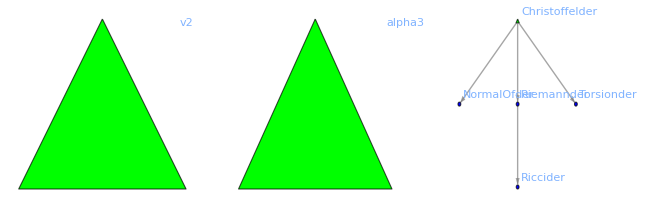

```mathematica
GraphicsRow[{VariationalRelationsOf[v2],VariationalRelationsOf[alpha3],VariationalRelationsOf[Christoffelder]},Frame->All]
```

Remark: Since we are dealing with graphs, any graph command can be used:

```mathematica
Graph3D@VariationalRelationsOf[Christoffelder]
```

-Graphics3D-

We can include several tensors (each represented as a green triangle) or 'All'

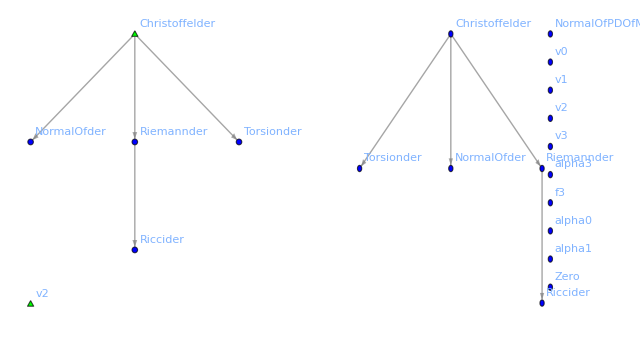

```mathematica
GraphicsRow[{VariationalRelationsOf[{Christoffelder,v2}],VariationalRelationsOf[All]},Frame->All]
```

VariationalRelationsOf[All] shows the full graph stored in $VariationalGraph with labels.

$VariationalGraph
It is a directed graph that encodes the variational dependency relations among all defined tensors within the session.

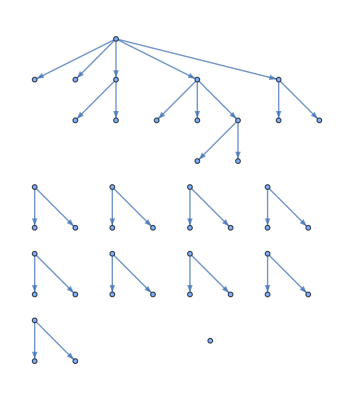

```mathematica
$VariationalGraph
```

#### Chapter.Section.Subsection.Subsubsection. VariationalRelationsOf and HideTrivialRelations

Since we always have the relations tensor→dltensor and tensor→VariationalVectortensor, those relations are hidden by default from the graphs. This behaviour is controlled by the option HideVertExact→True and if set to False, all the nodes are shown.

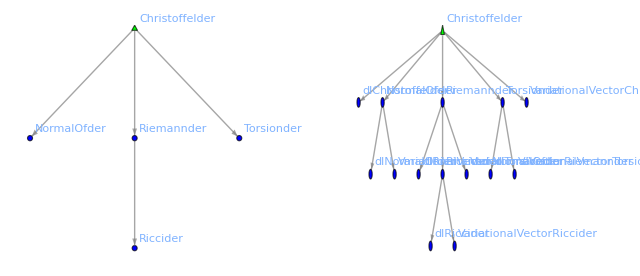

```mathematica
GraphicsRow[{VariationalRelationsOf[Christoffelder],VariationalRelationsOf[Christoffelder,HideTrivialRelations->False]},Frame->All]
```

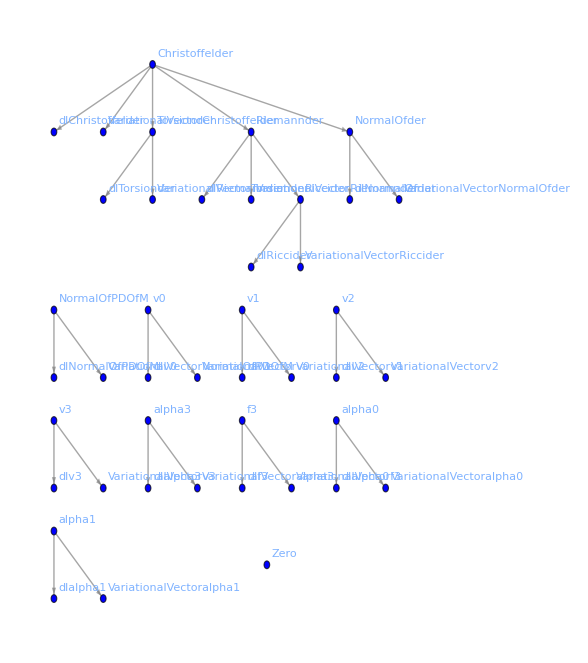

```mathematica
VariationalRelationsOf[All,HideTrivialRelations->False]
```

#### Chapter.Section.Subsection.Subsubsection. VariationalRelationsOf and Direction

The option Direction allows to show only the incoming edges, the outgoing edges, or both. By default it is the latter.

```mathematica
GraphicsRow[{VariationalRelationsOf[Riemannder,Directed->Out],
VariationalRelationsOf[Riemannder,Directed->In],
VariationalRelationsOf[Riemannder,Directed->Both]},Frame->All]
```

-Graphics-

### Chapter.Section.Subsection. Adding/Removing variational relations

AddVariationalRelation[masterTensor→dependentTensor]
It adds a variational dependency to the global graph $VariationalGraph.

RemoveVariationalRelation[masterTensor→dependentTensor]
It removes an existing variational relation from the global graph $VariationalGraph.

Two nodes can be joined by adding a variational relation:

```mathematica
VariationalRelationsOf[{v2,alpha3}]
AddVariationalRelation[v2->alpha3]
GraphicsRow[{VariationalRelationsOf[v2],VariationalRelationsOf[alpha3]},Frame->All]
```

-Graphics-

** AddVariationalRelation: Variational relation created v2→alpha3.

-Graphics-

Remark: If $DefInfoQ is True and the relation did not exist before, then a message is printed.

We can see how the overall graph changes as well

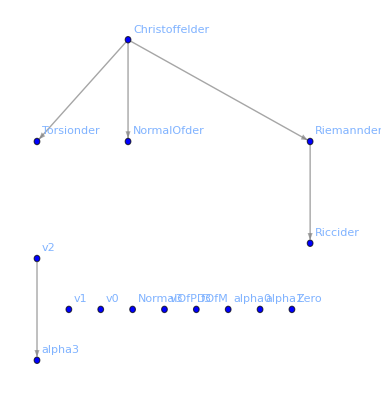

```mathematica
VariationalRelationsOf[All]
```

Likewise, we can remove Variational Relations

** RemoveVariationalRelation: Variational relation removed v2→alpha3

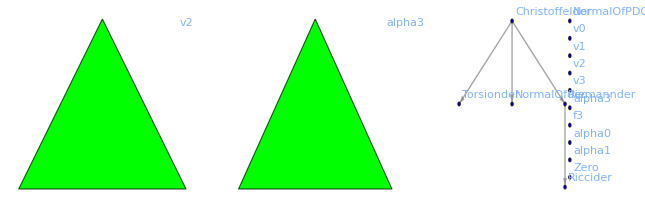

```mathematica
RemoveVariationalRelation[v2->alpha3]
GraphicsRow[{VariationalRelationsOf[v2],VariationalRelationsOf[alpha3],VariationalRelationsOf[All]},Frame->All]
```

Remark: If $UndefInfoQ is True and the relation did exist before, then a message is printed.

### Chapter.Section.Subsection. FindCyclicVariationalRelations

FindCyclicVariationalRelations[graph, option]
It returns a list of cyclic Variational Relations in the given 'graph' and prints whether any cycles were found.

- Option:
  ∗ ShowGraph→True

We can add several relations at once (possibly creating a cyclic relation).

```mathematica
AddVariationalRelation[v2->alpha3->v2]
```

** AddVariationalRelation: Variational relation created v2→alpha3.

** AddVariationalRelation: Variational relation created alpha3→v2.

FindCyclicVariationalRelations looks for cycles in the graph. It prints the graph with the cycles in different colors and returns the list of the cyclic relations.

** FindCyclicVariationalRelations: Some cyclic relations found:

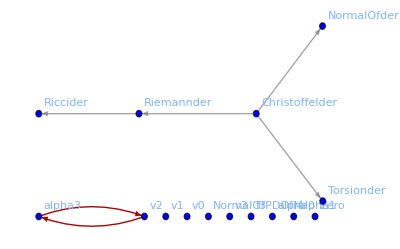

{{v2->alpha3,alpha3->v2}}

```mathematica
FindCyclicVariationalRelations[VariationalRelationsOf[All]]
```

If we only want the list, we can set the option ShowGraph → False

```mathematica
FindCyclicVariationalRelations[VariationalRelationsOf[All],ShowGraph->False]
```

{{v2->alpha3,alpha3->v2}}

** AddVariationalRelation: Variational relation created v2→v3.

** AddVariationalRelation: Variational relation created v3→alpha0.

** AddVariationalRelation: Variational relation created alpha0→v3.

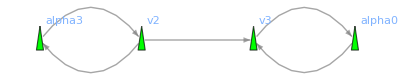

```mathematica
AddVariationalRelation[v2->v3->alpha0->v3]
VariationalRelationsOf[{alpha3,v2,v3,alpha0}]
```

** FindCyclicVariationalRelations: Some cyclic relations found:

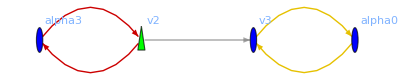

{{alpha3->v2,v2->alpha3},{alpha0->v3,v3->alpha0}}

```mathematica
FindCyclicVariationalRelations[VariationalRelationsOf[v2]]
```

### Chapter.Section.Subsection. ConstantTensors

ConstantTensors is an option of VariationalRelationsOf to assume some of the tensors variationally constant. Once the initial constant tensors have been established, the “constantness” is propagated as follows: a node is constant if all the incoming edges are constant. This behaviour is analogous to Equation (DisplayFormulaNumbered). 

When the option ConstantTensors is used, the constant nodes are depicted as red squares (unless it is a green triangle, which indicates that this node is the “center” of the graph) and the edges between red squares are also drawn in red.

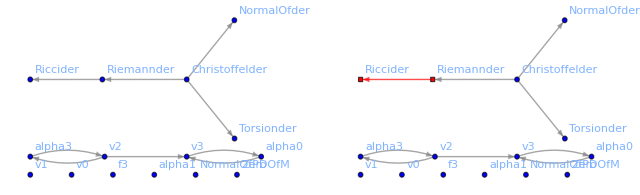

-Graphics-

```mathematica
GraphicsRow[{VariationalRelationsOf[All],
VariationalRelationsOf[All,ConstantTensors->Riemannder]},Frame->All]
GraphicsRow[{VariationalRelationsOf[Riemannder],
VariationalRelationsOf[Riemannder,ConstantTensors->Riemannder]},Frame->All]
```

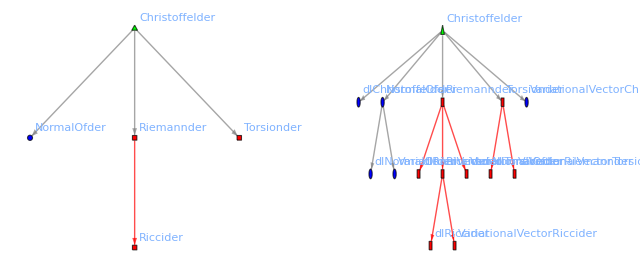

```mathematica
GraphicsRow[{VariationalRelationsOf[Christoffelder,ConstantTensors->{Riemannder,Torsionder}],VariationalRelationsOf[Christoffelder,ConstantTensors->{Riemannder,Torsionder},HideTrivialRelations->False]},Frame->All]
```

```mathematica
GraphicsRow[{VariationalRelationsOf[Torsionder,ConstantTensors->Riccider],
VariationalRelationsOf[alpha3,ConstantTensors->v3],
VariationalRelationsOf[alpha3,ConstantTensors->v2]},Frame->All]
```

-Graphics-

#### Chapter.Section.Subsection.Subsubsection. ListOfVariationalConstantsOf

ListOfVariationalConstantsOf[tensors]
It returns the list of constant tensors (red nodes in the graph) assuming the initial list of 'tensors' to be variationally constant.

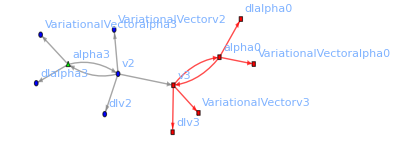

{v3,dlv3,VariationalVectorv3,alpha0,dlalpha0,VariationalVectoralpha0}

```mathematica
VariationalRelationsOf[alpha3,ConstantTensors->v3,HideTrivialRelations->False]
ListOfVariationalConstantsOf[v3]
```

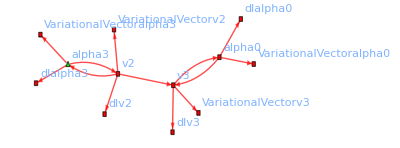

{v2,dlv2,VariationalVectorv2,alpha3,v3,dlalpha3,VariationalVectoralpha3,dlv3,VariationalVectorv3,alpha0,dlalpha0,VariationalVectoralpha0}

```mathematica
VariationalRelationsOf[alpha3,ConstantTensors->v2,HideTrivialRelations->False]
ListOfVariationalConstantsOf[v2]
```

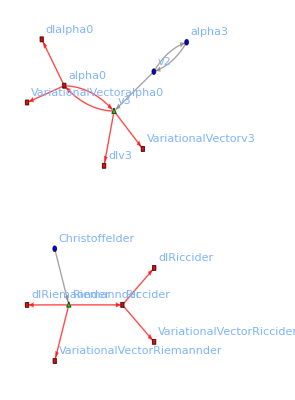

{v3,dlv3,VariationalVectorv3,alpha0,dlalpha0,VariationalVectoralpha0,Riemannder,dlRiemannder,VariationalVectorRiemannder,Riccider,dlRiccider,VariationalVectorRiccider}

```mathematica
VariationalRelationsOf[{v3,Riemannder},ConstantTensors->{v3,Riemannder},HideTrivialRelations->False]
ListOfVariationalConstantsOf[{v3,Riemannder}]
```

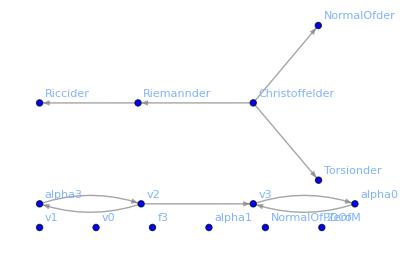

```mathematica
VariationalRelationsOf[All]
```

#### Chapter.Section.Subsection.Subsubsection VariationallyConstantQ

VariationallyConstantQ[ListOfConstantTensors,ListOfNonConstantTensors][tensor]
It returns True if 'tensor' is considered variationally constant. A tensor is constant if it belongs to the variational influence list generated from 'ListConstantTensors', and non-constant if it is related to any tensor in 'ListNonConstantTensors' through vertical relations.

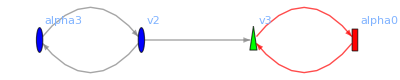

{v3,dlv3,VariationalVectorv3,alpha0,dlalpha0,VariationalVectoralpha0}

True

False

```mathematica
VariationalRelationsOf[v3,ConstantTensors->v3]
ListOfVariationalConstantsOf[v3]
VariationallyConstantQ[{v3},{}][alpha0] (* If v3 is constant, so is alpha0 *)
VariationallyConstantQ[{},{v3}][alpha0] (* If v3 is not constant, alpha0 cannot be constant *)(* Everything except v3 is constant *)
```

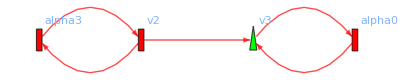

{v2,dlv2,VariationalVectorv2,alpha3,v3,dlalpha3,VariationalVectoralpha3,dlv3,VariationalVectorv3,alpha0,dlalpha0,VariationalVectoralpha0}

True

False

```mathematica
VariationalRelationsOf[v3,ConstantTensors->v2]
ListOfVariationalConstantsOf[v2]
VariationallyConstantQ[{v2},{}][alpha0] (* If v2 is constant, so is alpha0 *)
VariationallyConstantQ[{},{v2}][alpha0] (* If v2 is not constant, alpha0 cannot be constant *)
```

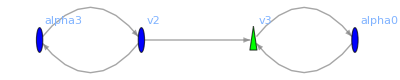

{v1,dlv1,VariationalVectorv1}

False

True

```mathematica
VariationalRelationsOf[v3,ConstantTensors->v1]
ListOfVariationalConstantsOf[v1]
VariationallyConstantQ[{v1},{}][alpha0] (* If v1 is constant, alpha0 is not necessarly constant *)
VariationallyConstantQ[{},{v1}][alpha0] (* If v1 is not constant, it means that {v2,v3...} are constant and then so is alpha0 *)
```

#### Chapter.Section.Subsection.Subsubsection. ExpandVertDiff and ConstantTensors

ExpandVertDiff uses these graphs to determine which dltensors must be zero.

```mathematica
VertDiff[alpha0]
VertDiff[alpha0][-a]
VertDiff[alpha0[-a]]//ExpandVertDiff[ConstantTensors->v3]
VertDiff[alpha0[-a]]//ExpandVertDiff[ConstantTensors->alpha3]
```

dlalpha0

(ⅆα0) |  
a

0

0

### Chapter.Section.Subsection. GenerateExpandVertDiffRule

If we create an ExpandVertDiff rule for a 1-vertical-form (see Subsection Chapter.Section.Subsection), all required variational relations are also created according to the the ideas presented along with Equation (DisplayFormulaNumbered). Likewise, all previous variational relations that become spurious with the new ExpandVertDiff rule are removed (they can be added again with AddVariationalRelation, which performs no consistency check).

```mathematica
GenerateExpandVertDiffRule[{dlalpha0[-a],dlRiccider[-a,-b]v0[b]+dlChristoffelder[b,-a,-b]}]
```

** GenerateExpandVertDiffRule: Expansion formula generated for dlalpha0.

** RemoveVariationalRelation: Variational relation removed v3→alpha0

** AddVariationalRelation: Variational relation created Christoffelder→alpha0.

** AddVariationalRelation: Variational relation created Riccider→alpha0.

```mathematica
dlalpha0[-a]==(dlalpha0[-a]//ExpandVertDiff[HoldExpandVertDiff->Riccider])
dlalpha0[-a]==(dlalpha0[-a]//ExpandVertDiff[])
```

(ⅆα0) |  
a==(ⅆΓ[D]) | b |   |  
  | a | b+(ⅆR[D]) |   |  
a | b v0 | b

(ⅆα0) |  
a==(ⅆΓ[D]) | b |   |  
  | a | b+v0 | b
  (-(ⅆΓ[D]) | c |   |  
  | d | b T[D] | d |   |  
  | a | c-D_a(ⅆΓ[D]) | c |   |  
  | c | b+D_c(ⅆΓ[D]) | c |   |  
  | a | b)

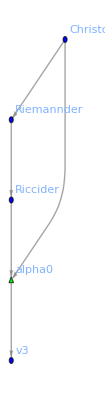

```mathematica
VariationalRelationsOf[alpha0]
```

If Ricci is constant, it does not imply that alpha0 is constant:

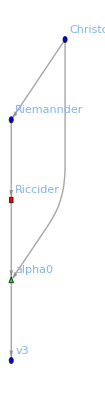

(ⅆα0) |  
a==(ⅆΓ[D]) | b |   |  
  | a | b

```mathematica
VariationalRelationsOf[alpha0,ConstantTensors->Riccider]
dlalpha0[-a]==(dlalpha0[-a]//ExpandVertDiff[ConstantTensors->Riccider])
```

However, if Christoffel is constant, then Ricci is constant. Since both are constant, alpha0 is constant:

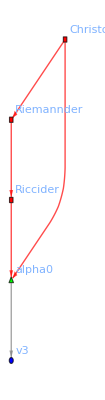

(ⅆα0) |  
a==0

```mathematica
VariationalRelationsOf[alpha0,ConstantTensors->Christoffelder]
dlalpha0[-a]==(dlalpha0[-a]//ExpandVertDiff[ConstantTensors->Christoffelder])
```

Remark: v3 is not constant in the previous graph because it has additional relations:

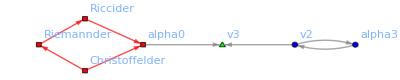

```mathematica
VariationalRelationsOf[v3,ConstantTensors->Christoffelder]
```

If the ExpandVertDiff rule is not of the form of Equation (DisplayFormulaNumbered), then no variational relation is created:

```mathematica
GenerateExpandVertDiffRule[{dlalpha0[-a],alpha1[-a]}]
```

** RemoveExpandVertDiffRule: Expansion formula removed for dlalpha0.

** RemoveVariationalRelation: Variational relation removed Christoffelder→alpha0

** RemoveVariationalRelation: Variational relation removed Riccider→alpha0

** GenerateExpandVertDiffRule: Expansion formula generated for dlalpha0.

** GenerateExpandVertDiffRule: No variational relation added because the RHS has non-exact terms of VertDeg=1. If necessary, they can be added manually using AddVariationalRelation.

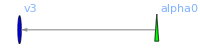

(ⅆα0) |  
a==α1 |  
a

```mathematica
VariationalRelationsOf[alpha0]

dlalpha0[-a]==(dlalpha0[-a]//ExpandVertDiff[])
```

```mathematica
GenerateExpandVertDiffRule[{dlv1[a],v2[a]}]
```

** GenerateExpandVertDiffRule: Expansion formula generated for dlv1.

** GenerateExpandVertDiffRule: No variational relation added because dlv1 has VertDeg≠1. If necessary, they can be added manually using AddVariationalRelation.

Warning: AddVariationalRelation and GenerateExpandVertDiffRule are related but different and they can become incompatible. As mentioned before, GenerateExpandVertDiffRule checks the variational relations but AddVariationalRelation does not.

### Chapter.Section.Subsection. Variational relations, CovDs example

```mathematica
DefConstantSymbol[dimeninner]
DefVBundle[inner,M,dimeninner,{J,L,P,Q}]

DefCovD[der1[-a],inner,{";","D"},Torsion->True]
DefCovD[der2[-a],inner,{";","𝔇"},Torsion->True]
```

** DefConstantSymbol: Defining constant symbol dimeninner.

** DefVBundle: Defining vbundle inner.

** DefCovD: Defining covariant derivative der1[-a].

** DefTensor: Defining torsion tensor Torsionder1[a,-b,-c].

** DefTensor: Defining tensor dlTorsionder1[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorTorsionder1[-a,b,c].

** DefTensor: Defining non-symmetric Christoffel tensor Christoffelder1[a,-b,-c].

** DefTensor: Defining tensor dlChristoffelder1[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorChristoffelder1[-a,b,c].

** DefTensor: Defining Riemann tensor Riemannder1[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining tensor dlRiemannder1[-a,-b,-c,d].

** DefTensor: Defining tensor VariationalVectorRiemannder1[a,b,c,-d].

** DefTensor: Defining non-symmetric Ricci tensor Riccider1[-a,-b].

** DefTensor: Defining tensor dlRiccider1[-a,-b].

** DefTensor: Defining tensor VariationalVectorRiccider1[a,b].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining nonsymmetric AChristoffel tensor AChristoffelder1[J,-b,-P].

** DefTensor: Defining tensor dlAChristoffelder1[J,-b,-P].

** DefTensor: Defining tensor VariationalVectorAChristoffelder1[-J,b,P].

** DefTensor: Defining FRiemann tensor FRiemannder1[-a,-b,-P,Q]. Antisymmetric only in the first pair.

** DefTensor: Defining tensor dlFRiemannder1[-a,-b,-P,Q].

** DefTensor: Defining tensor VariationalVectorFRiemannder1[a,b,P,-Q].

** DefInertHead: Defining inert head TotalDerivativeOfder1.

** DefTensor: Defining tensor NormalOfder1[-a].

** DefTensor: Defining tensor dlNormalOfder1[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfder1[a].

** AddVariationalRelation: Variational relations created for der1.

** DefCovD: Defining covariant derivative der2[-a].

** DefTensor: Defining torsion tensor Torsionder2[a,-b,-c].

** DefTensor: Defining tensor dlTorsionder2[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorTorsionder2[-a,b,c].

** DefTensor: Defining non-symmetric Christoffel tensor Christoffelder2[a,-b,-c].

** DefTensor: Defining tensor dlChristoffelder2[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorChristoffelder2[-a,b,c].

** DefTensor: Defining Riemann tensor Riemannder2[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining tensor dlRiemannder2[-a,-b,-c,d].

** DefTensor: Defining tensor VariationalVectorRiemannder2[a,b,c,-d].

** DefTensor: Defining non-symmetric Ricci tensor Riccider2[-a,-b].

** DefTensor: Defining tensor dlRiccider2[-a,-b].

** DefTensor: Defining tensor VariationalVectorRiccider2[a,b].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining nonsymmetric AChristoffel tensor AChristoffelder2[J,-b,-P].

** DefTensor: Defining tensor dlAChristoffelder2[J,-b,-P].

** DefTensor: Defining tensor VariationalVectorAChristoffelder2[-J,b,P].

** DefTensor: Defining FRiemann tensor FRiemannder2[-a,-b,-P,Q]. Antisymmetric only in the first pair.

** DefTensor: Defining tensor dlFRiemannder2[-a,-b,-P,Q].

** DefTensor: Defining tensor VariationalVectorFRiemannder2[a,b,P,-Q].

** DefInertHead: Defining inert head TotalDerivativeOfder2.

** DefTensor: Defining tensor NormalOfder2[-a].

** DefTensor: Defining tensor dlNormalOfder2[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfder2[a].

** AddVariationalRelation: Variational relations created for der2.

```mathematica
TensorWithIndices[Christoffel[der1,der2]]
TensorWithIndices[AChristoffel[der1,der2]]
```

** DefTensor: Defining tensor Christoffelder1der2[a,-b,-c].

** DefTensor: Defining tensor dlChristoffelder1der2[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorChristoffelder1der2[-a,b,c].

** AddVariationalRelation: Variational relation created Christoffelder1→Christoffelder1der2.

** AddVariationalRelation: Variational relation created Christoffelder2→Christoffelder1der2.

** GenerateExpandVertDiffRule: Expansion formula generated for dlChristoffelder1der2.

Γ[D,𝔇] | a |   |  
  | b | c

** DefTensor: Defining tensor AChristoffelder1der2[J,-b,-P].

** DefTensor: Defining tensor dlAChristoffelder1der2[J,-b,-P].

** DefTensor: Defining tensor VariationalVectorAChristoffelder1der2[-J,b,P].

** AddVariationalRelation: Variational relation created AChristoffelder1→AChristoffelder1der2.

** AddVariationalRelation: Variational relation created AChristoffelder2→AChristoffelder1der2.

** GenerateExpandVertDiffRule: Expansion formula generated for dlAChristoffelder1der2.

A[D,𝔇] | J |   |  
  | a | L

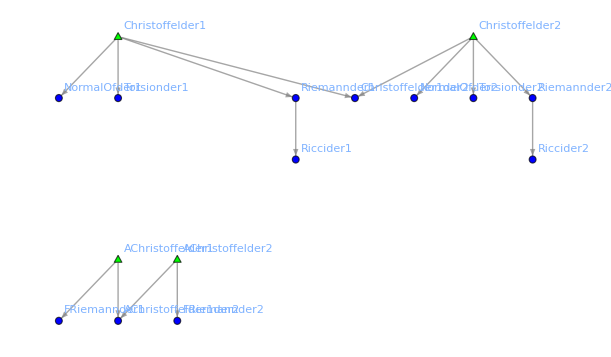

```mathematica
VariationalRelationsOf[{Christoffelder1,Christoffelder2,AChristoffelder1,AChristoffelder2}]
```

### Chapter.Section.Subsection. Variational relations, metric example

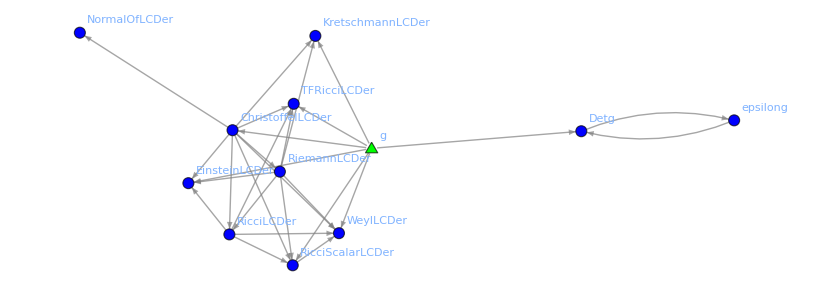

```mathematica
$DefInfoQ=False;
DefMetric[-1,g[-a,-b],LCDer,{";","∇"}] 
$DefInfoQ=True;

VariationalRelationsOf[g]
```

## Chapter.Section. Reset session

We reset everything: $ConstantSymbols, $Parameters, $ScalarFunctions, $Metrics, $CovDs, $Tensors, $Manifolds, and $VBundles.

```mathematica
ResetSession[]
```

** SetSigns: All constant signs set to 1.

## Chapter. Variational calculus - Scalar field

## Chapter.Section. Lagrangian

### Chapter.Section.Subsection. Initial definitions

```mathematica
$DefInfoQ=False;
DefConstantSymbol[dimen]
DefManifold[M,dimen,{a,b,c,d,e,f,h,i,j,k,l}]

DefTensor[phi[],M,PrintAs->"ϕ"]
DefMetric[-1,g[-a,-b],LCDer,{";","∇"}] 
DefTensor[xi[a],M,PrintAs->"ξ"]

$DefInfoQ=True;
```

In this Section, we consider in detail the Lagrangian of the scalar field:

```mathematica
Lscalar=1/2 g[a,b]LCDer[-a]@phi[]LCDer[-b]@phi[] √(-Detg[])
```

1/2 √(-g^OverTilde[~]) g | a | b
  |   ∇_a ϕ ∇_b ϕ

### Chapter.Section.Subsection. LagrangianQ and dlLagrangianQ

LagrangianQ[expr]
It verifies whether 'expr' is a scalar with zero vertical degree.

dlLagrangianQ[expr]
It verifies whether 'expr' is a scalar with VertDeg[expr]=1 and one exact vertical form per monomial.

Warning: If dlLagrangianQ[expr]is True, this does not imply necessarily that 'expr' is the VertDiff of a Lagrangian (that is a very complicated cohomological problem, equivalent to check if some equations of motion are variational).

```mathematica
LagrangianQ[Lscalar]
LagrangianQ[VertDiff@Lscalar]
```

True

False

```mathematica
dlLagrangianQ[Lscalar]
dlLagrangianQ[VertDiff@Lscalar]
```

False

True

## Chapter.Section. FirstVariation

### Chapter.Section.Subsection. Theory behind FirstVariation

As we mention on Subsection Chapter.Section.Subsection of the introduction, given a Lagrangian L(ϕ^i), if we take its VertDiff and perform the Leibniz rule, we can always decompose the expression as follows:

ⅆL=EOM_i ⅆ ϕ^i+dΘ

where:
• EOM_i, sometimes denoted  in the physics literature, are the Equations of Motion with respect to the field ϕ^i.
• Θ is the symplectic potential of the Lagrangian.

This is precisely the role of FirstVariation.

FirstVariation[tensors, der, options][Lagrangian]
It computes the first variation of 'Lagrangian' keeping the total derivative term.

- 'fields': optional argument to indicate the fields to be considered as dynamical. If not specified, all fields are considered dynamic.
- 'der': optional argument to specify the CovD to be used by FirstVariation.
- Options:
  ∗ Simplification→True
  ∗ ContractMetric→True.

FirstVariation[tensors][Lagrangian] computes the First Variation of Lagrangian following the steps:
1. Take VertDiff[Lagrangian] followed by ExpandVertDiff[NonConstantTensors→tensors] which, schematically, will be of the form

∑_(i=1)^N ∑_(j=0)^m_i ((T_ij)^(a_1... a_j))_(B_(i))∇_a_1...∇_a_j (ⅆ ϕ_i)^(B_(i))

where {ϕ_i} are all the dynamical fields and B_(i) denote all the upper and lower indices of the field ϕ_i. Notice that we assume that we have ChangeCovD all CovD into 'der' (denoted ∇) and j=0 corresponds to the case of no CovD in front of ⅆ ϕ_i.

2. Use Leibniz rule to remove the first CovD in front of ⅆ ϕ_i:

∑_(i=1)^N ∑_(j=1)^m_i [∇_a_1 (((T_ij)^(a_1... a_j))_(B_(i))∇_a_2...∇_a_j (ⅆ ϕ_i)^(B_(i)))-(∇_a_1 ((T_ij)^(a_1... a_j))_(B_(i)))∇_a_2...∇_a_j (ⅆ ϕ_i)^(B_(i)))]

3. Apply step 2 until we obtain

∑_(i=1)^N (EOM_i)_(B_(i))(ⅆ ϕ_i)^(B_(i))+∇_b [∑_(i=1)^N ∑_(j=1)^m_i ((R_ij)^(ba_2... a_j))_(B_(i))∇_a_2...∇_a_j (ⅆ ϕ_i)^(B_(i)))

4. To prevent the expansion of the last term, we wrap it into a new linear InnertHead denoted

TotalDerivativeOfCovD[der]=TotalDerivativeNameOfder

To leave a scalar inside the InnertHead, we contract the index b coming from 'der'with the 1-form (explained in detail below)

NormalOfCovD[der]=NormalOfNameOfCovder

This finally leads to

∑_(i=1)^N (EOM_i)_(B_(i))(ⅆ ϕ_i)^(B_(i))+TotalDerivativeOfCovDder[NormalOfCovDder_b∑_(i=1)^N ∑_(j=1)^m_i ((R_ij)^(ba_2... a_j))_(B_(i))∇_a_2...∇_a_j (ⅆ ϕ_i)^(B_(i))]

### Chapter.Section.Subsection. Use

```mathematica
FirstVariation[][Lscalar]
```

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ]-√(-g^OverTilde[~]) (ⅆϕ) ∇_b ∇^b ϕ+(ⅆg) |   |  
a | b (-1/2 √(-g^OverTilde[~]) ∇^a ϕ ∇^b ϕ+1/4 √(-g^OverTilde[~]) g | a | b
  |   ∇_c ϕ ∇^c ϕ)

### Chapter.Section.Subsection. Related functions

#### Chapter.Section.Subsection.Subsubsection. TotalDerivative and NormalOfCovD

TotalDerivativeOfCovD[der]
It returns the total derivative head (divergence term) associated with the covariant derivative 'der'. It is the one used in the first variation of a Lagrangian.

NormalOfCovD[der]
It returns the fiducial normal vector associated with the covariant derivative operator 'der'.

For both functions, if der=PD and multiple manifolds are defined, the arguments must be [PD, index] or [PD, manifold] to disambiguate.

When performing the first variation, we obtain the InertHead TotalDerivativeOfCovD[LCDer]=TotalDerivativeOfLCDer. It indicates that the term is a total derivative (a divergence) with respect to LCDer. However, in order for the indices to match and obtain a scalar, we need a covector that keeps tracks of the index and the CovD. This is done with NormalOfCovD[LCDer]=NormalOfCovDLCDer.

As we explained in Subsection Chapter.Section.Subsection , NormalOfCovD[der] keeps track of the index of 'der'. Moreover, for metric CovDs, this tensor is also the one appearing when integrating over a manifold with boundary and applying Stokes’ theorem

∫_M ∇_a V^a vol_g=∫_(∂M) ((n)_∇) |  
a V^a vol_(∂g)

Important: We are essentially changing the covariant derivative by a covector. This substitution ∇_a →((n)_∇) |  
a works for a very specific context. Notice for instance that ∇_a ∇_b is in general different from ∇_b ∇_a. However, for xAct ((n)_∇) |  
a((n)_∇) |  
b=((n)_∇) |  
b((n)_∇) |  
a, so some caution has to be exercised when dealing with these objects.

```mathematica
TotalDerivativeOfCovD[LCDer]
NormalOfCovD[LCDer]
NormalOfCovD[LCDer][a]
```

TotalDerivativeOfLCDer

NormalOfLCDer

(n_∇) | a

We can also obtain the TotalDerivative head from the normal and the normal from the TotalDerivative head.

TotalDerivativeOfNormal[normal]
It returns the total derivative operator associated with the fiducial normal vector 'normal'.

NormalOfTotalDerivative[TotD]
It returns the fiducial normal vector associated with the total derivative operator 'TotD'.

```mathematica
TotalDerivativeOfNormal[NormalOfLCDer]
NormalOfTotalDerivative[TotalDerivativeOfLCDer]
```

TotalDerivativeOfLCDer

NormalOfLCDer

$TotalDerivatives
It is the list of total derivatives associated with all the defined covariant derivatives.

$NormalsOfCovD
It is the list of fiducial normals associated with all the defined covariant derivatives.

```mathematica
$TotalDerivatives
$NormalsOfCovD
```

{TotalDerivativeOfPDOfM,TotalDerivativeOfLCDer}

{NormalOfPDOfM,NormalOfLCDer}

We have some “question functions” to identify those types of terms:

TotalDerivativeQ[expr]
It returns True if 'expr' is a total derivative operator (with or without argument), and False otherwise.

NormalOfCovDQ[n][Manifold]
It returns True if 'n' is a fiducial normal vector associated with a covariant derivative.

dlNormalOfCovDQ[dln] 
It returns True if 'dln' is the vertical differential of a fiducial normal vector 'n'.

```mathematica
{TotalDerivativeQ[TotalDerivativeOfLCDer],TotalDerivativeQ[TotalDerivativeOfLCDer[expr]],TotalDerivativeQ[NormalOfLCDer]}
{NormalOfCovDQ[NormalOfLCDer],NormalOfCovDQ[NormalOfLCDer[a]],NormalOfCovDQ[TotalDerivativeOfLCDer]}
{VertDiffNormalOfCovDQ[dlNormalOfLCDer],VertDiffNormalOfCovDQ[dlNormalOfLCDer[a]],VertDiffNormalOfCovDQ[NormalOfLCDer]}
```

{True,True,False}

{True,True,False}

{True,True,False}

In Appendix A.Section, we have added a bit of information about TotalDerivativeOfCovD[PD] and NormalOfCovD[PD]. Since PD is defined for all manifolds, we need to handle this case with more care when several manifolds are defined.

#### Chapter.Section.Subsection.Subsubsection. CovDToTotalDerivative and TotalDerivativeToCovD

CovDToTotalDerivative[expr]
It rewrites covariant derivatives (with the argument kept with Keep[]) in 'expr' using the corresponding total derivatives TotalDerivative[der].

TotalDerivativeToCovD[expr]
It rewrites total derivative terms TotalDerivativeOf[der] in 'expr' using the corresponding covariant derivatives (with the argument kept with Keep[]).

These functions allow to transform the TotalDerivativeOfder head into the corresponding CovD and vice versa.

```mathematica
expr1=TotalDerivativeOfLCDer[√(-Overscript[g, OverTilde[~]]) (ⅆϕ) {{((n)_∇), {{a}, {}}}} ∇_a ϕ]
expr1//TotalDerivativeToCovD
```

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ]

∇_a (√(-g^OverTilde[~]) (ⅆϕ) g | b | a
  |   ∇_b ϕ)

This expression has a Keep wrapper to prevent the Leibniz rule expansion of the CovD.

```mathematica
%//ScreenDollarIndices//InputForm
```

LCDer[-a][Keep[Sqrt[-Detg[]]*dlphi[]*g[b, a]*LCDer[-b][phi[]]]]

```mathematica
expr2=LCDer[-a][Keep[Sqrt[-Detg[]]dlphi[]LCDer[a][phi[]]]]
expr2//CovDToTotalDerivative
```

∇_a (√(-g^OverTilde[~]) (ⅆϕ) ∇^a ϕ)

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_∇) |  
a ∇^a ϕ]

They are inverse of each other:

```mathematica
expr1==(expr1//TotalDerivativeToCovD//CovDToTotalDerivative//ContractMetric)
expr2==(expr2//CovDToTotalDerivative//TotalDerivativeToCovD)
```

True

True

Important: TotalDerivativeOfLCDer is a head that is supposed to have a density-1 scalar in its interior to represent a total derivative. Indeed, for a given metric, we have:

div_g W vol_g=L_W vol_g=dι_W vol_g=TotalDerivativeOfLCDer[NormalOfLCDer_a W^a √(-Detg[])]vol_fixed

It is important to realize that no checks are performed to ensure this and even the Total Derivative of non-metric CovD are defined.

```mathematica
TotalDerivativeOfLCDer[dlg[-a,-b]]//Validate
```

TotalDerivativeOfLCDer[(ⅆg) |   |  
a | b]

```mathematica
FirstVariation[][Lscalar]
FirstVariation[][Lscalar]//TotalDerivativeToCovD//Simplification
```

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ]-√(-g^OverTilde[~]) (ⅆϕ) ∇_b ∇^b ϕ+(ⅆg) |   |  
a | b (-1/2 √(-g^OverTilde[~]) ∇^a ϕ ∇^b ϕ+1/4 √(-g^OverTilde[~]) g | a | b
  |   ∇_c ϕ ∇^c ϕ)

∇_b ((√(-g^OverTilde[~]) (ⅆϕ) ∇^b ϕ))+1/4 √(-g^OverTilde[~]) (-4 (ⅆϕ) ∇_b ∇^b ϕ+(-2 (ⅆg) |   |  
b | a ∇^a ϕ+(ⅆg) | a | c
  |   g |   |  
a | c ∇_b ϕ) ∇^b ϕ)

#### Chapter.Section.Subsection.Subsubsection. VertDiffNormalOfCovDToCovD

dlNormalOfCovDToCovD[expr]
It rewrites 'expr' involving the vertical differential of a fiducial normal vector in terms of its covariant derivative.

As we have mentioned above in Subsubsection Chapter.Section.Subsection.Subsubsection, we essentially have the equality ∇_a =((n)_∇) |  
a. Thus (ⅆ n_∇) |  
a has the same meaning as ⅆ∇_a , which depends on the tensors upon which it is acting:

ⅆ(∇_a T | b |  
  | c) = ∇_a (ⅆT) | b |  
  | c+(ⅆΓ[∇]) | b |   |  
  | a | d T | d |  
  | c-(ⅆΓ[∇]) | d |   |  
  | a | c T | b |  
  | d

```mathematica
$DefInfoQ=False;
DefTensor[T[a,-b],M]
DefTensor[U[a],M]
$DefInfoQ=True;
VertDiff@LCDer[-a][T[b,-c]]//ExpandVertDiff[HoldExpandVertDiff->ChristoffelLCDer]
VertDiff@LCDer[-a][U[b]]//ExpandVertDiff[HoldExpandVertDiff->ChristoffelLCDer]
```

-(ⅆΓ[∇]) | d |   |  
  | a | c T | b |  
  | d+(ⅆΓ[∇]) | b |   |  
  | a | d T | d |  
  | c+∇_a (ⅆT) | b |  
  | c

(ⅆΓ[∇]) | b |   |  
  | a | c U | c
 +∇_a (ⅆU) | b

Thus, ExpandVertDiff cannot expand ⅆNormalOfder without knowing on which elements it is acting on.

```mathematica
VertDiff[NormalOfLCDer][-a]//ExpandVertDiff[]
```

(ⅆ n_∇) |  
a

That is the purpose of dlNormalOfCovDToCovD, which is defined as:

VertDiffNormalOfCovDToCovD[VertDiff[NormalOfder_a expr]:=VertDiff[∇_a @expr]-∇_a [VertDiff@expr]

```mathematica
VertDiffNormalOfCovDToCovD[dlNormalOfLCDer[-a]T[b,-c]]
VertDiffNormalOfCovDToCovD[dlNormalOfLCDer[-a]T[b,-c]]//ExpandVertDiff[HoldExpandVertDiff->ChristoffelLCDer]
VertDiffNormalOfCovDToCovD[dlNormalOfLCDer[-a]U[b]]
VertDiffNormalOfCovDToCovD[dlNormalOfLCDer[-a]U[b]]//ExpandVertDiff[HoldExpandVertDiff->ChristoffelLCDer]
```

ⅆ[∇_a T | b |  
  | c]-∇_a (ⅆT) | b |  
  | c

-(ⅆΓ[∇]) | d |   |  
  | a | c T | b |  
  | d+(ⅆΓ[∇]) | b |   |  
  | a | d T | d |  
  | c

ⅆ[∇_a U | b
 ]-∇_a (ⅆU) | b

(ⅆΓ[∇]) | b |   |  
  | a | c U | c

As expected, applying first NormalOfCovDToCovD and then VertDiff is equal to first applying VertDiff and then dlNormalOfCovDToCovD:

```mathematica
expr1=NormalOfLCDer[-a]T[b,-c];
VertDiff[NormalOfCovDToCovD[expr1]]//ExpandVertDiff[HoldExpandVertDiff->ChristoffelLCDer]
VertDiff[expr1]//VertDiffNormalOfCovDToCovD//ExpandVertDiff[HoldExpandVertDiff->ChristoffelLCDer]//NormalOfCovDToCovD
%-%%
```

-(ⅆΓ[∇]) | d |   |  
  | a | c T | b |  
  | d+(ⅆΓ[∇]) | b |   |  
  | a | d T | d |  
  | c+∇_a (ⅆT) | b |  
  | c

-(ⅆΓ[∇]) | d |   |  
  | a | c T | b |  
  | d+(ⅆΓ[∇]) | b |   |  
  | a | d T | d |  
  | c+∇_a (ⅆT) | b |  
  | c

0

```mathematica
expr2=NormalOfLCDer[-a]U[b];
VertDiff[NormalOfCovDToCovD[expr2]]//ExpandVertDiff[HoldExpandVertDiff->ChristoffelLCDer]
VertDiff[expr2]//VertDiffNormalOfCovDToCovD//ExpandVertDiff[HoldExpandVertDiff->ChristoffelLCDer]//NormalOfCovDToCovD
%-%%
```

(ⅆΓ[∇]) | b |   |  
  | a | c U | c
 +∇_a (ⅆU) | b

(ⅆΓ[∇]) | b |   |  
  | a | c U | c
 +∇_a (ⅆU) | b

0

#### Chapter.Section.Subsection.Subsubsection. TotalDerivativeOfCovD and VertInt

Remark: VertInt and TotalDerivativeOfCovD do not always commute (see [ItemNumbered]). By default, they do on xCPS through ExpandVertInt and this behaviour is controlled by the option ExpandVertIntTotalDerivative.

```mathematica
VertInt[vvff][TotalDerivativeOfLCDer[dlg[-a,-b]]]==(VertInt[vvff][TotalDerivativeOfLCDer[dlg[-a,-b]]]//ExpandVertInt[] )
VertInt[vvff][TotalDerivativeOfLCDer[dlg[-a,-b]]]//ExpandVertInt[ExpandVertIntTotalDerivative ->False]
```

ⅈ_vvff[TotalDerivativeOfLCDer[(ⅆg) |   |  
a | b]]==TotalDerivativeOfLCDer[ⅈ_vvff[(ⅆg) |   |  
a | b]]

ⅈ_vvff[TotalDerivativeOfLCDer[(ⅆg) |   |  
a | b]]

#### Chapter.Section.Subsection.Subsubsection. TotalDerivativeOfCovD and VertDiff

Remark: Likewise, VertDiff and TotalDerivative only commute if the TotalDerivativeOfder[expr] is a true total derivative. Indeed:

ⅆTotalDerivativeOfLCDer[(n_∇) |  
a W^a √(-Detg[])]vol_fixed==dⅆ ι_W vol_g=d(ι_ⅆW vol_g+(-1)^VertDeg[W]ι_W ⅆ √(-Detg[])vol_fixed)=d(ι_(ⅆW+(-1)^VertDeg[W]W ⩕(ⅆ √(-Detg[]))/(√(-Detg[])))vol_g)==TotalDerivativeOfLCDer[(n_∇) |  
a(√(-Detg[])ⅆ W^a+(-1)^VertDeg[W]W^a⩕ⅆ √(-Detg[]))]vol_fixed=TotalDerivativeOfLCDer[(n_∇) |  
a(√(-Detg[])ⅆ W^a+ⅆ √(-Detg[])⩕ W^a)]vol_fixed=TotalDerivativeOfLCDer[(n_∇) |  
aⅆ[√(-Detg[])W^a]]vol_fixed

```mathematica
VertDiff[TotalDerivativeOfLCDer[√(-Detg[])NormalOfLCDer[a]dlg[-a,-b]xi[b]]]//ExpandVertDiff[]//ContractMetric//Simplification
```

TotalDerivativeOfLCDer[1/2 √(-g^OverTilde[~]) (n_∇) | a
  (2 ((ⅆξ) | b
 ⩕(ⅆg) |   |  
a | b)-((ⅆg) |   |  
a | b⩕(ⅆg) | c |  
  | c+2 ((ⅆg) |   | c
a |  ⩕(ⅆg) |   |  
b | c)) ξ | b
 )]

We can prevent the expansion of VertDiff of TotalDerivatives:

```mathematica
VertDiff[TotalDerivativeOfLCDer[√(-Detg[])NormalOfLCDer[a]dlg[-a,-b]xi[b]]]//ExpandVertDiff[ExpandVertDiffTotalDerivative->False]
```

ⅆ[TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆg) |   |  
a | b g | a | c
  |   (n_∇) |  
c ξ | b
 ]]

Remark: The following expressions are not expanded because they are not true total derivatives:

```mathematica
VertDiff[TotalDerivativeOfLCDer[NormalOfLCDer[a]dlg[-a,-b]xi[b]]]//ExpandVertDiff[] (* WeightOf=!=1 *)
VertDiff[TotalDerivativeOfLCDer[√(-Detg[])NormalOfPDOfM[a]dlg[-a,-b]xi[b]]]//ExpandVertDiff[] (* No NormalOfLCDer present *)
VertDiff[TotalDerivativeOfLCDer[√(-Detg[])NormalOfLCDer[a]dlg[-a,-b]]]//ExpandVertDiff[] (* No scalar *)
VertDiff[TotalDerivativeOfLCDer[√(-Detg[])NormalOfLCDer[a]dlg[-a,-b]NormalOfLCDer[b]]]//ExpandVertDiff[](* Too many NormalOfLCDer present *)
```

ⅆ[TotalDerivativeOfLCDer[(ⅆg) |   |  
a | b g | a | c
  |   (n_∇) |  
c ξ | b
 ]]

ⅆ[TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆg) |   |  
a | b g | a | c
  |   (n_M) |  
c ξ | b
 ]]

ⅆ[TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆg) |   |  
a | b g | a | c
  |   (n_∇) |  
c]]

ⅆ[TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆg) |   |  
a | b g | a | c
  |   g | b | d
  |   (n_∇) |  
c (n_∇) |  
d]]

These conditions are checked with the function.

TotalDerivativeDivergenceQ[expr] 
It returns True if 'expr' if it is a scalar of weight 1 with a NormalOfCovD[der] covector, all wrapped with a TotalDerivativeOfCovD[der] head. It returns False otherwise.

```mathematica
TotalDerivativeDivergenceQ[TotalDerivativeOfLCDer[√(-Detg[])NormalOfLCDer[a]dlg[-a,-b]xi[b]]]
TotalDerivativeDivergenceQ[TotalDerivativeOfLCDer[NormalOfLCDer[a]dlg[-a,-b]xi[b]]](* WeightOf=!=1 *)
TotalDerivativeDivergenceQ[TotalDerivativeOfLCDer[√(-Detg[])NormalOfPDOfM[a]dlg[-a,-b]xi[b]]](* No NormalOfLCDer present *)
TotalDerivativeDivergenceQ[TotalDerivativeOfLCDer[√(-Detg[])NormalOfLCDer[a]dlg[-a,-b]]](* No scalar *)
TotalDerivativeDivergenceQ[TotalDerivativeOfLCDer[√(-Detg[])NormalOfLCDer[a]dlg[-a,-b]NormalOfLCDer[b]]](* Too many NormalOfLCDer present *)
TotalDerivativeDivergenceQ[√(-Detg[])NormalOfLCDer[a]dlg[-a,-b]xi[b]](* No TotalDerivative present *)
```

True

False

False

False

«2 more identical outputs»

#### Chapter.Section.Subsection.Subsubsection. OnlyTotalDerivative, DiscardTotalDerivative

OnlyTotalDerivative[expr] 
It returns the terms with TotalDerivativeQ heads.

DiscardTotalDerivative[expr] 
It removes the terms with TotalDerivatives.

DiscardTotalDerivative removes the terms with TotalDerivativeOfCovD.

```mathematica
g[a,b]+TotalDerivativeOfLCDer[xi[a]xi[b]]
DiscardTotalDerivative[g[a,b]+TotalDerivativeOfLCDer[xi[a]xi[b]]]
```

g | a | b
  |  +TotalDerivativeOfLCDer[ξ | a
  ξ | b
 ]

g | a | b
  |

While OnlyTotalDerivative keeps the terms with TotalDerivatives.

```mathematica
g[a,b]+TotalDerivativeOfLCDer[xi[a]xi[b]]
OnlyTotalDerivative[g[a,b]+TotalDerivativeOfLCDer[xi[a]xi[b]]]
```

g | a | b
  |  +TotalDerivativeOfLCDer[ξ | a
  ξ | b
 ]

TotalDerivativeOfLCDer[ξ | a
  ξ | b
 ]

Finally TotalDerivativePotential extracts the argument from the head TotalDerivativeOfCovd.

```mathematica
g[a,b]+TotalDerivativeOfLCDer[xi[a]xi[b]]
TotalDerivativePotential[g[a,b]+TotalDerivativeOfLCDer[xi[a]xi[b]]]
```

g | a | b
  |  +TotalDerivativeOfLCDer[ξ | a
  ξ | b
 ]

ξ | a
  ξ | b

### Chapter.Section.Subsection. Options and arguments for FirstVariation

#### Chapter.Section.Subsection.Subsubsection. Options for FirstVariation

By default, the expressions are simplified and metric-contracted (keeping the structure of Equation (DisplayFormulaNumbered)), but these options can be deactivated.

```mathematica
FirstVariation[][Lscalar]
FirstVariation[ContractMetric->False][Lscalar]
FirstVariation[Simplification->False][Lscalar]
FirstVariation[Simplification->False,ContractMetric->False][Lscalar]
```

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ]-√(-g^OverTilde[~]) (ⅆϕ) ∇_b ∇^b ϕ+(ⅆg) |   |  
a | b (-1/2 √(-g^OverTilde[~]) ∇^a ϕ ∇^b ϕ+1/4 √(-g^OverTilde[~]) g | a | b
  |   ∇_c ϕ ∇^c ϕ)

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) g |   |  
a | b (n_∇) | a
  ∇^b ϕ]-√(-g^OverTilde[~]) (ⅆϕ) g | a | b
  |   ∇_b ∇_a ϕ+1/4 √(-g^OverTilde[~]) (ⅆg) |   |  
a | b (-2 ∇^a ϕ ∇^b ϕ+g | a | b
  |   g |   |  
c | d ∇^c ϕ ∇^d ϕ)

TotalDerivativeOfLCDer[1/2 √(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ+1/2 √(-g^OverTilde[~]) (ⅆϕ) (n_∇) |  
b ∇^b ϕ]-√(-g^OverTilde[~]) (ⅆϕ) ∇_b ∇^b ϕ+(ⅆg) |   |  
a | b (-1/2 √(-g^OverTilde[~]) ∇^a ϕ ∇^b ϕ+1/8 √(-g^OverTilde[~]) g | a | b
  |   ∇_c ϕ ∇^c ϕ+1/8 √(-g^OverTilde[~]) g | b | a
  |   ∇_c ϕ ∇^c ϕ)

TotalDerivativeOfLCDer[1/2 √(-g^OverTilde[~]) (ⅆϕ) g | a | b
  |   (n_∇) |  
b ∇_a ϕ+1/2 √(-g^OverTilde[~]) (ⅆϕ) g | c | d
  |   (n_∇) |  
c ∇_d ϕ]-1/2 √(-g^OverTilde[~]) (ⅆg) |   |  
c | d g | a | c
  |   g | b | d
  |   ∇_a ϕ ∇_b ϕ+1/4 √(-g^OverTilde[~]) (ⅆg) |   |  
c | d g | a | b
  |   g | c | d
  |   ∇_a ϕ ∇_b ϕ-√(-g^OverTilde[~]) (ⅆϕ) g | a | b
  |   ∇_b ∇_a ϕ

Remark: If we apply ContractMetric and Simplification at the end, the structure of Equation (DisplayFormulaNumbered) is lost.

```mathematica
FirstVariation[Simplification->False,ContractMetric->False][Lscalar]//ContractMetric//Simplification
```

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ]+1/4 √(-g^OverTilde[~]) (-4 (ⅆϕ) ∇_a ∇^a ϕ+∇^a ϕ ((ⅆg) | b |  
  | b ∇_a ϕ-2 (ⅆg) |   |  
a | b ∇^b ϕ))

Setting these options to False speeds up the computations, specially for large expressions.

```mathematica
Timing[FirstVariation[][Lscalar]][[1]]
Timing[FirstVariation[ContractMetric->False][Lscalar]][[1]]
Timing[FirstVariation[Simplification->False][Lscalar]][[1]]
Timing[FirstVariation[Simplification->False,ContractMetric->False][Lscalar]][[1]]
```

0.21875

0.234375

0.140625

0.109375

#### Chapter.Section.Subsection.Subsubsection. Optional ‘der’ argument for FirstVariation

We can specify the CovD to be used in FirstVariation to perform the Leibniz rule (“integration by parts”). If not indicated, it will automatically find the ones appearing and if there is only one, it will use that one. Otherwise, it will throw an error:

```mathematica
Lscalar2=1/2 g[a,b]LCDer[-a]@phi[]PD[-b]@phi[] √(-Determinant[g][])
ChangeCovD[Lscalar-Lscalar2,PD,LCDer]
```

1/2 √(-g^OverTilde[~]) g | a | b
  |   ∇_a ϕ ∂_b ϕ

0

```mathematica
FirstVariation[][Lscalar2]
```

xAct`xCPS`Private`FindCovDFromdlExpr::unknown: Several CovDs detected: {LCDer,PD}. Specify which one should be used to integrate by parts or use ChangeCovD.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

```mathematica
FirstVariation[LCDer,Simplification->False][Lscalar2]
```

TotalDerivativeOfLCDer[1/2 √(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ+1/2 √(-g^OverTilde[~]) (ⅆϕ) (n_∇) |  
b ∂^b ϕ]+(ⅆϕ) (-1/2 √(-g^OverTilde[~]) ∇_a ∂^a ϕ-1/2 √(-g^OverTilde[~]) ∇_b ∇^b ϕ)+(ⅆg) |   |  
a | b (-1/4 √(-g^OverTilde[~]) ∇^b ϕ ∂^a ϕ-1/4 √(-g^OverTilde[~]) ∇^a ϕ ∂^b ϕ+1/8 √(-g^OverTilde[~]) g | a | b
  |   ∇_c ϕ ∂^c ϕ+1/8 √(-g^OverTilde[~]) g | b | a
  |   ∇_c ϕ ∂^c ϕ)

```mathematica
ChangeCovD[%,PD,LCDer]//Simplification//ContractMetric
FirstVariation[][Lscalar]
%-%%//Simplification//ContractMetric
```

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ]-√(-g^OverTilde[~]) (ⅆϕ) ∇_a ∇^a ϕ+1/4 √(-g^OverTilde[~]) (ⅆg) | b |  
  | b ∇_a ϕ ∇^a ϕ-1/2 √(-g^OverTilde[~]) (ⅆg) |   |  
a | b ∇^a ϕ ∇^b ϕ

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ]-√(-g^OverTilde[~]) (ⅆϕ) ∇_b ∇^b ϕ+(ⅆg) |   |  
a | b (-1/2 √(-g^OverTilde[~]) ∇^a ϕ ∇^b ϕ+1/4 √(-g^OverTilde[~]) g | a | b
  |   ∇_c ϕ ∇^c ϕ)

0

#### Chapter.Section.Subsection.Subsubsection. Optional ‘fields’ argument for FirstVariation

We can indicate the fields used to compute the first variation (the rest are assumed constant i.e. VertDiff.08[ϕ_i]=0).

```mathematica
FirstVariation[phi][Lscalar]
FirstVariation[g][Lscalar]
```

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ]-√(-g^OverTilde[~]) (ⅆϕ) ∇_b ∇^b ϕ

(ⅆg) |   |  
a | b (-1/2 √(-g^OverTilde[~]) ∇^a ϕ ∇^b ϕ+1/4 √(-g^OverTilde[~]) g | a | b
  |   ∇_c ϕ ∇^c ϕ)

Indicating all the fields is equivalent to not indicate anything. However, providing the fields and CovD speeds up the computation, specially for large expressions.

```mathematica
slow=Timing[FirstVariation[][Lscalar] ][[1]];
fast=Timing[FirstVariation[{phi,g},LCDer][Lscalar] ][[1]];
(slow-fast)/slow*100//ContractMetric//Simplification
```

12.5

```mathematica
slow=Timing[FirstVariation[][Lscalar] ][[1]];
fast=Timing[FirstVariation[{phi,g},LCDer,Simplification->False,ContractMetric->False][Lscalar] ][[1]];
(slow-fast)/slow*100//ContractMetric//Simplification
```

64.2857

### Chapter.Section.Subsection. Interactions between FirstVariation and other functions

#### Chapter.Section.Subsection.Subsubsection. WeightOf and FirstVariation

If WeightOf the 'Lagrangian' is not 1, FirstVariation would issue a warning since the TotalDerivativeOfder might not correspond to a divergence.

```mathematica
FirstVariation[phi,LCDer][Lscalar/(√(-Overscript[g, OverTilde[~]]))]
```

** Warning: WeightOf is not 1, which means that TotalDerivativeOfLCDer might not be a total divergence.

TotalDerivativeOfLCDer[(ⅆϕ) (n_∇) | a
  ∇_a ϕ]-(ⅆϕ) ∇_b ∇^b ϕ

#### Chapter.Section.Subsection.Subsubsection. FirstVariation and LieD

One interesting feature about xCPS is that it is trained to perform the Leibniz rule with LieD as well as with CovD.

```mathematica
DefTensor[v0[a],M]
L1=LieD[xi[a]][√(-Detg[])v0[b]v0[-b]]
```

** DefTensor: Defining tensor v0[a].

** DefTensor: Defining tensor dlv0[a].

** DefTensor: Defining tensor VariationalVectorv0[-a].

-(g^OverTilde[~] g | a | c
  |   v0 |  
b v0 | b
  (ℒ_ξ g |   |  
a | c))/(2 √(-g^OverTilde[~]))+√(-g^OverTilde[~]) (v0 | b
  (ℒ_ξ v0 |  
b)+v0 |  
b (ℒ_ξ v0 | b
 ))

```mathematica
FirstVariation[][L1]//Quiet
(* Quiet is included to avoid the warning messages about "Detected metric-incompatible derivatives" *)
```

TotalDerivativeOfPDOfM[√(-g^OverTilde[~]) (ⅆξ) | b
  (n_M) |  
b v0 |  
a v0 | a
 +1/2 √(-g^OverTilde[~]) (ⅆg) | f |  
  | f (n_M) | c
  v0 |  
d v0 | d
  ξ |  
c+√(-g^OverTilde[~]) (ⅆg) |   |  
d | e (n_M) | c
  v0 | d
  v0 | e
  ξ |  
c+2 √(-g^OverTilde[~]) (ⅆv0) | h
  (n_M) | i
  v0 |  
h ξ |  
i]+(ⅆg) |   |  
a | b (1/4 √(-g^OverTilde[~]) g | a | b
  |   v0 |  
c v0 | c
  ∇_f ξ | f
 +1/4 √(-g^OverTilde[~]) g | a | b
  |   v0 |  
c v0 | c
  ∇_h ξ | h
 -1/4 √(-g^OverTilde[~]) g | a | b
  |   g | d | e
  |   v0 |  
c v0 | c
  (ℒ_ξ g |   |  
d | e))+(ⅆξ) | a
  (Γ[∇] | e |   |  
  | a | e √(-g^OverTilde[~]) v0 |  
b v0 | b
 -1/2 √(-g^OverTilde[~]) g | c | d
  |   v0 |  
b v0 | b
  ∂_a g |   |  
c | d)

Remark: Some LieD are preserved in the previous expression. However, not all of them can be preserved since the variation with respect to xi (the argument of LieD) requires LieDToCovD.

Remark: If the CovD is indicated in FirstVariation, that is the one that will be used in LieDToCovD, otherwise PD is used (notice TotalDerivativeOfPDOfM in the previous expression).

As a side note, we see that L1 is actually a total derivative, hence no EOM appear:

```mathematica
firstvariation=LieDToCovD[FirstVariation[LCDer,Simplification->False][L1] ,LCDer]//ContractMetric//Simplification
```

TotalDerivativeOfLCDer[1/2 √(-g^OverTilde[~]) (2 (ⅆξ) | a
  (n_∇) |  
a v0 |  
b v0 | b
 +(ⅆg) | c |  
  | c (n_∇) | a
  v0 |  
b v0 | b
  ξ |  
a+2 (ⅆg) |   |  
b | c (n_∇) | a
  v0 | b
  v0 | c
  ξ |  
a+4 (ⅆv0) | a
  (n_∇) | b
  v0 |  
a ξ |  
b)]

Remark: If we have a top-form ω, the variation of the Lagrangian L_ξ ω is the following:

ⅆ L_ξω=ⅆ dι_ξω=dⅆ ι_ξω=d(ι_ⅆξ ω+ι_ξ ⅆω)=TotalDerivativeOfLCDer[(n_∇) |  
a((ⅆξ) | a
 ω+ξ | a
 ⅆω])

and we can easily check that this is indeed what we have obtained:

```mathematica
NormalOfLCDer[-a](dlxi[a] √(-Detg[])v0[b]v0[-b]+xi[a]VertDiff[√(-Detg[])v0[b]v0[-b]])//ExpandVertDiff[]//ContractMetric//Simplification
TotalDerivativePotential[firstvariation]-%
```

1/2 √(-g^OverTilde[~]) (2 (ⅆξ) | a
  (n_∇) |  
a v0 |  
b v0 | b
 +(ⅆg) | c |  
  | c (n_∇) | a
  v0 |  
b v0 | b
  ξ |  
a+2 (ⅆg) |   |  
b | c (n_∇) | a
  v0 | b
  v0 | c
  ξ |  
a+4 (ⅆv0) | a
  (n_∇) | b
  v0 |  
a ξ |  
b)

0

Remark: As we saw on Section Chapter.Section, DivergenceQ checks precisely that only TotalDerivative terms appear after performing FirstVariation:

```mathematica
DivergenceQ[g][L1]
```

True

## Chapter.Section. EOM

EOM[field, der][Lagrangian]
It returns the Equations of Motion of 'Lagrangian' with respect to 'field'. The argument 'der' is optional. If not specified, it finds the only CovD present (if several are present, an error is thrown).

The field is now compulsory but the CovD argument 'der' can be specified or not. No Simplification or ContractMetric is performed since that can be done afterwards.

```mathematica
waveeq=EOM[phi][Lscalar]
EOM[g,LCDer][Lscalar]//ContractMetric//Simplification
```

-√(-g^OverTilde[~]) g | a | b
  |   ∇_b ∇_a ϕ

1/4 √(-g^OverTilde[~]) (-2 ∇^a ϕ ∇^b ϕ+g | a | b
  |   ∇_c ϕ ∇^c ϕ)

We can include the indices:

```mathematica
EOM[g[-c,-d],LCDer][Lscalar]//ContractMetric//Simplification
EOM[g[-e,-f],LCDer][Lscalar]//ContractMetric//Simplification
```

1/4 √(-g^OverTilde[~]) (g | c | d
  |   ∇_a ϕ ∇^a ϕ-2 ∇^c ϕ ∇^d ϕ)

1/4 √(-g^OverTilde[~]) (g | e | f
  |   ∇_a ϕ ∇^a ϕ-2 ∇^e ϕ ∇^f ϕ)

Warning: The placement of the indices must be the natural one (there is a possibility to compute the EOM using the inverse metric, see Section Chapter.Section).

```mathematica
EOM[g[e,f],LCDer][Lscalar]//ContractMetric//Simplification
```

EOMOf1Form::wrongindices: Incorrect placement of indices {e,f}. Place them correctly or write simply the head of the tensor g.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

Remark: Computing the first variation (that keeps track of the total derivative) takes, as expected, more time that computing simply the EOM.

```mathematica
Timing[FirstVariation[LCDer,Simplification->False,ContractMetric->False][Lscalar]][[1]]
Timing[EOM[g,LCDer][Lscalar]][[1]]
```

0.078125

0.125

## Chapter.Section. EnergyMomentum

EnergyMomentum[Lagrangian]
It returns the Energy Momentum tensor of 'Lagrangian'.

```mathematica
EnergyMomentumLScalar=EnergyMomentum[Lscalar ]//ContractMetric//Simplification
```

∇^a ϕ ∇^b ϕ-1/2 g | a | b
  |   ∇_c ϕ ∇^c ϕ

This is equivalent to the EOM with respect to the metric multiplied by -2/(√(-g^OverTilde[~])) (with a plus if we take the variation with respect to the inverse metric, which will be explained later)

```mathematica
-2/(√(-Overscript[g, OverTilde[~]]))EOM[g][Lscalar]//ContractMetric//Simplification
```

∇^a ϕ ∇^b ϕ-1/2 g | a | b
  |   ∇_c ϕ ∇^c ϕ

If no metric is found, an error is thrown:

```mathematica
EnergyMomentum[phi[]]
```

EnergyMomentum::unknown: No metric found.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

## Chapter.Section. Inverse metric for variations

Recall from Subsubsection Chapter.Section.Subsection.Subsubsection, that the constant boolean $UseInverseMetric determines if {dlmetric,VariationalVectormetric} or {dlInvmetric,VariationalVectorInvmetric} are used.

```mathematica
$UseInverseMetric
dlInvg[a,b]
dlInvg[-a,-b]
dlg[a,b]
dlg[-a,-b]
```

False

-(ⅆg) |   |  
c | d g | a | c
  |   g | b | d
  |

-(ⅆg) | c | d
  |   g |   |  
a | c g |   |  
b | d

(ⅆg) | a | b
  |

(ⅆg) |   |  
a | b

This choice affects the placement of the indices of the EOM (notice that the energy-momentum tensor is still the same):

```mathematica
EnergyMomentum[Lscalar]//ContractMetric//Simplification
EOM[g][Lscalar]//ContractMetric//Simplification
EOM[Inv[g]][Lscalar]//ContractMetric//Simplification (* Inv[g]=g is first evaluated before being used by EOM *)

$UseInverseMetric=True;
EnergyMomentum[Lscalar]//ContractMetric//Simplification (* This does not change *)
EOM[g][Lscalar]//ContractMetric//Simplification (* These equations change the sign *)
EOM[g[e,f]][Lscalar]//ContractMetric//Simplification (* We can add indices *)
```

∇^a ϕ ∇^b ϕ-1/2 g | a | b
  |   ∇_c ϕ ∇^c ϕ

1/4 √(-g^OverTilde[~]) (-2 ∇^a ϕ ∇^b ϕ+g | a | b
  |   ∇_c ϕ ∇^c ϕ)

1/4 √(-g^OverTilde[~]) (-2 ∇^a ϕ ∇^b ϕ+g | a | b
  |   ∇_c ϕ ∇^c ϕ)

∇^a ϕ ∇^b ϕ-1/2 g | a | b
  |   ∇_c ϕ ∇^c ϕ

1/4 √(-g^OverTilde[~]) (2 ∇^a ϕ ∇^b ϕ-g | a | b
  |   ∇_c ϕ ∇^c ϕ)

1/4 √(-g^OverTilde[~]) (-g |   |  
e | f ∇_a ϕ ∇^a ϕ+2 ∇_e ϕ ∇_f ϕ)

```mathematica
FirstVariation[][Lscalar]
$UseInverseMetric=False;
FirstVariation[][Lscalar]
```

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ]-√(-g^OverTilde[~]) (ⅆϕ) ∇_b ∇^b ϕ+ⅆ(g^-1) |   |  
a | b (1/2 √(-g^OverTilde[~]) ∇^a ϕ ∇^b ϕ-1/4 √(-g^OverTilde[~]) g | a | b
  |   ∇_c ϕ ∇^c ϕ)

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ]-√(-g^OverTilde[~]) (ⅆϕ) ∇_b ∇^b ϕ+(ⅆg) |   |  
a | b (-1/2 √(-g^OverTilde[~]) ∇^a ϕ ∇^b ϕ+1/4 √(-g^OverTilde[~]) g | a | b
  |   ∇_c ϕ ∇^c ϕ)

## Chapter.Section. Symplectic potential

As we saw in Equation (DisplayFormulaNumbered), when performing the Leibniz rule on ⅆLagrangian, a total derivative term appears. The potential of that term is known as symplectic potential (which is only defined up to a total derivative).

SymplecticPotential[tensors, der][Lagrangian] 
It grabs the expression inside TotalDerivativeOf[der] after performing FirstVariation[fields, der][Lagrangian].

- 'tensors': optional argument to indicate the fields to be considered as dynamical. If not specified, all fields are considered dynamic.
- 'der': optional argument to specify the CovD to be used by FirstVariation.

This is achieved using:

TotalDerivativeOfPotential[expr] 
It extracts the total derivative potential Θ of an expression of the form expr=expr2+TotalDerivativeOf[der][Θ] or expr=expr2+der[ind][Keep[Θ]].

```mathematica
SymplecticPotential[][Lscalar]//ContractMetric//Simplification
FirstVariation[][Lscalar]
%//TotalDerivativePotential
```

√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ]-√(-g^OverTilde[~]) (ⅆϕ) ∇_b ∇^b ϕ+(ⅆg) |   |  
a | b (-1/2 √(-g^OverTilde[~]) ∇^a ϕ ∇^b ϕ+1/4 √(-g^OverTilde[~]) g | a | b
  |   ∇_c ϕ ∇^c ϕ)

√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ

The arguments 'fields' and 'der' are optional:

```mathematica
SymplecticPotential[g][Lscalar]
SymplecticPotential[phi,LCDer][Lscalar]//ContractMetric//Simplification
```

0

√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ

## Chapter.Section. SymplecticCurrent

SymplecticCurrent[fields, der, option][Lagrangian]
It computes the symplectic current associated to 'Lagrangian'.

- 'fields': optional argument to indicate the fields to be considered as dynamical. If not specified, all fields are considered dynamic.
- 'der': optional argument to specify the CovD to be used by FirstVariation.
- Option:
  ∗ HoldExpandVertDiff→None: Allows to hold some dltensors in the “second variation”.

Taking the exterior derivative (variation) of the symplectic potential, we obtain the symplectic current (defined up to a total derivative):

ω=ⅆΘ

Upon integration over a Cauchy slice, it provides a (pre)symplectic form on the space of fields [ItemNumbered]. Moreover, it does not depend on the slice over the space of solutions (on-shell). It can also be proved that, under very mild conditions, it is equivalent to the canonical symplectic structure coming from the Hamiltonian formalism [ItemNumbered].

There is an overall sign $SymplecticCurrentSign that is taken by default =1.

$SymplecticCurrentSign
It defines the global sign of the symplectic current.

Warning: One has to be careful when comparing formulas from books and articles, first because of the sign convention $SymplecticCurrentSign, and second because the integration introduces a minus sign due to the orientations.

Some examples of use:

```mathematica
SymplecticCurrent[g][Lscalar]//Simplification
SymplecticCurrent[][Lscalar]//Simplification//ContractMetric//Simplification
```

0

-1/2 √(-g^OverTilde[~]) (n_∇) | a
  (2 ((ⅆϕ)⩕∇_a (ⅆϕ))+((ⅆϕ)⩕(ⅆg) | b |  
  | b) ∇_a ϕ-2 ((ⅆϕ)⩕(ⅆg) |   |  
a | b) ∇^b ϕ)

Remark: The first expression leads to zero because the symplectic potential does not depend on ⅆg:

```mathematica
FirstVariation[][Lscalar]
```

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ]-√(-g^OverTilde[~]) (ⅆϕ) ∇_b ∇^b ϕ+(ⅆg) |   |  
a | b (-1/2 √(-g^OverTilde[~]) ∇^a ϕ ∇^b ϕ+1/4 √(-g^OverTilde[~]) g | a | b
  |   ∇_c ϕ ∇^c ϕ)

Warning: One has to be careful when comparing formulas from books and articles, first because of the sign convention $SymplecticCurrentSign, and second because the integration introduces a minus sign due to the orientations.

If the only variable field is ϕ (thus ⅆg=0), we clearly obtain (upon integration over a Cauchy slice) the canonical symplectic structure (position times momenta):

```mathematica
SymplecticCurrent[phi][Lscalar]//Simplification
SymplecticCurrent[phi][Lscalar]//Simplification//ContractDir[#,NormalOfLCDer]&//DirCovDToLieD[#,NormalOfLCDer]&
```

-√(-g^OverTilde[~]) (n_∇) | a
  ((ⅆϕ)⩕∇_a (ⅆϕ))

## Chapter.Section. Analogous functions for VertDiff[Lagrangian]

### Chapter.Section.Subsection Motivation

Sometimes we have already computed the VertDiff of a Lagrangian or we have performed a redefinition of fields (as we will see for electromagnetism in Chapter Chapter) and we need to use some of the previous functions (FirstVariation, EOM, SymplecticPotential and SymplecticCurrent). We have defined the analogous ones for dlLagrangianQ (see Subsection Chapter.Section.Subsection). The arguments and options of these new functions are the same as the 0-vertical-forms counterparts. In essence, they all satisfy the formula:

function[arguments][expr]=functionOf1Form[arguments][VertDiff@expr]

### Chapter.Section.Subsection FirstVariationOf1Form

FirstVariationOf1Form[tensors, der, options][dlLagrangian]
It computes the first variation of 'dlLagrangian' keeping the total derivative term.

- 'fields': optional argument to indicate the fields to be considered as dynamical. If not specified, all fields are considered dynamic.
- 'der': optional argument to specify the CovD to be used by FirstVariation.
- Options:
  ∗ Simplification→True
  ∗ ContractMetric→True.

```mathematica
FirstVariationOf1Form[][VertDiff@Lscalar]
FirstVariation[][Lscalar]
```

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ]-√(-g^OverTilde[~]) (ⅆϕ) ∇_b ∇^b ϕ+(ⅆg) |   |  
a | b (-1/2 √(-g^OverTilde[~]) ∇^a ϕ ∇^b ϕ+1/4 √(-g^OverTilde[~]) g | a | b
  |   ∇_c ϕ ∇^c ϕ)

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_a ϕ]-√(-g^OverTilde[~]) (ⅆϕ) ∇_b ∇^b ϕ+(ⅆg) |   |  
a | b (-1/2 √(-g^OverTilde[~]) ∇^a ϕ ∇^b ϕ+1/4 √(-g^OverTilde[~]) g | a | b
  |   ∇_c ϕ ∇^c ϕ)

### Chapter.Section.Subsection EOMOf1Form

EOMOf1Form[HeadOfTensor, der][dlLagrangian]
It extracts the equations of motion from 'dlLagrangian' with respect to 'HeadOfTensor'. The argument 'der' is optional. If not specified, it finds the only CovD present (if several are present, an error is thrown).

```mathematica
EOMOf1Form[phi][VertDiff@Lscalar]
EOM[phi][Lscalar]

EOMOf1Form[g,LCDer][VertDiff@Lscalar]//ContractMetric//Simplification
EOM[g,LCDer][Lscalar]//ContractMetric//Simplification
```

-√(-g^OverTilde[~]) g | a | b
  |   ∇_b ∇_a ϕ

-√(-g^OverTilde[~]) g | a | b
  |   ∇_b ∇_a ϕ

1/4 √(-g^OverTilde[~]) (-2 ∇^a ϕ ∇^b ϕ+g | a | b
  |   ∇_c ϕ ∇^c ϕ)

1/4 √(-g^OverTilde[~]) (-2 ∇^a ϕ ∇^b ϕ+g | a | b
  |   ∇_c ϕ ∇^c ϕ)

### Chapter.Section.Subsection SymplecticPotentialOf1Form

SymplecticPotentialOf1Form[field, der][dlLagrangian]
It grabs the expression inside TotalDerivativeOf[der] after performing FirstVariationOf1Form[fields, der][dlLagrangian].

- 'fields': optional argument to indicate the fields to be considered as dynamical. If not specified, all fields are considered dynamic.
- 'der': optional argument to specify the CovD to be used by FirstVariation.

```mathematica
SymplecticPotential[][Lscalar]
SymplecticPotentialOf1Form[][VertDiff@Lscalar]
```

1/2 √(-g^OverTilde[~]) (ⅆϕ) g | a | b
  |   (n_∇) |  
b ∇_a ϕ+1/2 √(-g^OverTilde[~]) (ⅆϕ) g | a | b
  |   (n_∇) |  
a ∇_b ϕ

1/2 √(-g^OverTilde[~]) (ⅆϕ) g | a | b
  |   (n_∇) |  
b ∇_a ϕ+1/2 √(-g^OverTilde[~]) (ⅆϕ) g | a | b
  |   (n_∇) |  
a ∇_b ϕ

### Chapter.Section.Subsection SymplecticCurrentOf1Form

SymplecticCurrentOf1Form[tensors, der, option][dlLagrangian]
It computes the symplectic current of'dlLagrangian'.

- 'fields': optional argument to indicate the fields to be considered as dynamical. If not specified, all fields are considered dynamic.
- 'der': optional argument to specify the CovD to be used by FirstVariation.
- Option:
  ∗ HoldExpandVertDiff→None: Allows to hold some dltensors in the “second variation”.

```mathematica
SymplecticCurrent[][Lscalar]//ContractMetric//Simplification
SymplecticCurrentOf1Form[][VertDiff@Lscalar]//ContractMetric//Simplification
```

-1/2 √(-g^OverTilde[~]) (n_∇) | a
  (2 ((ⅆϕ)⩕∇_a (ⅆϕ))+((ⅆϕ)⩕(ⅆg) | b |  
  | b) ∇_a ϕ-2 ((ⅆϕ)⩕(ⅆg) |   |  
a | b) ∇^b ϕ)

-1/2 √(-g^OverTilde[~]) (n_∇) | a
  (2 ((ⅆϕ)⩕∇_a (ⅆϕ))+((ⅆϕ)⩕(ⅆg) | b |  
  | b) ∇_a ϕ-2 ((ⅆϕ)⩕(ⅆg) |   |  
a | b) ∇^b ϕ)

## Chapter.Section. Noether symmetries

### Chapter.Section.Subsection. Variational Vector Fields (VVF)

We define the VVF (see Subsection Chapter.Section.Subsection):

```mathematica
vvf1=VVFFromLieD[xi][phi]
```

(δ/δϕ) (ℒ_ξ ϕ)

which describes the infinitesimal transformation (d-symmetries [ItemNumbered,ItemNumbered]) given by the Lie Derivative: ϕ->ϕ+ϵℒ_ξ ϕ.

### Chapter.Section.Subsection. NoetherSymmetryQ

NoetherSymmetryQ[vvf][metric][Lagrangian, options]
It tests if the vector field 'vvf' is a Noether symmetry of 'Lagrangian' using 'metric'.

- 'optionalfunctions': Optional functions to be applied in the middle steps of the algorithm.
- Option:
  ∗ CheckZero→True uses === instead of == to test if EOMs vanish.

This function checks if the transformation VertLie[vvf][Lagrangian] is a total divergence using an auxiliary metric. The way to check if the expression is a total divergence is through DivergenceQ (explained in Subsection Chapter.Section.Subsection), which makes sure that the EOMs with respect to each field appearing in the expression are zero.

Remark: If no EOMs are present, that actually means that the term is topological. This is equivalent to be a divergence if we assume that the vector bundle is contractible (see [ItemNumbered] for further detail). There are of course topological Lagrangians that are not global divergences (pointwise, they are divergences but the potential might not be well defined globally) like the Gauss-Bonnet term in dimension≤4 or Einstein-Hilbert Lagrangian in dimension=2 (see also [ItemNumbered, Example 5.10 on page 207] for an interesting example of a non-exact Lagrangian with no EOM).

```mathematica
NoetherSymmetryQ[vvf1][g][Lscalar]
```

∇_a ϕ ∇_b ∇^b ϕ==0&&∇^c ϕ (∇^a ξ |  
c ∇^b ϕ+∇^a ϕ ∇^b ξ |  
c-g | a | b
  |   ∇_d ξ |  
c ∇^d ϕ)+ξ | c
  (∇^b ϕ ∇_c ∇^a ϕ+∇^a ϕ ∇_c ∇^b ϕ-g | a | b
  |   ∇_d ∇_c ϕ ∇^d ϕ)==0&&ξ | a
  ∇_a ∇_b ∇^b ϕ+∇_a ξ | a
  ∇_b ∇^b ϕ==∇^a ϕ ∇_b ∇^b ξ |  
a+ξ | a
  ∇_b ∇^b ∇_a ϕ+2 ∇_b ∇_a ϕ ∇^b ξ | a

If the expressions are not immediately zero, the function does not return False because in some cases certain functions/rules might render such expression zero.

```mathematica
NoetherSymmetryQ[vvf1][g][Lscalar]//SortCovDs
```

∇_a ϕ ∇_b ∇^b ϕ==0&&∇^c ϕ (∇^a ξ |  
c ∇^b ϕ+∇^a ϕ ∇^b ξ |  
c-g | a | b
  |   ∇_d ξ |  
c ∇^d ϕ)+ξ | c
  (∇^b ϕ ∇_c ∇^a ϕ+∇^a ϕ ∇_c ∇^b ϕ-g | a | b
  |   ∇_d ∇_c ϕ ∇^d ϕ)==0&&∇_a ξ | a
  ∇_b ∇^b ϕ+ξ | a
  (∇_b ∇^b ∇_a ϕ-R[∇] |   |  
a | c ∇^c ϕ)==∇^a ϕ ∇_b ∇^b ξ |  
a+ξ | a
  ∇_b ∇^b ∇_a ϕ+2 ∇_b ∇_a ϕ ∇^b ξ | a

If one is convinced that this is not zero (as it is the case), one can add the option CheckZero→True which uses === instead of ==

```mathematica
NoetherSymmetryQ[vvf1][g,CheckZero->True][Lscalar]
```

False

We can consider another transformations like:

```mathematica
vvf2=VVFFromLieD[xi][g,phi]
```

(δ/δg) | a | b
  |   (ℒ_ξ g |   |  
a | b)+(δ/δϕ) (ℒ_ξ ϕ)

which describes the infinitesimal transformation: ϕ->ϕ+ϵℒ_ξ ϕ and g->g+ϵℒ_ξ g. This means that all fields are transformed using the Lie derivative (no background objects are present, see [ItemNumbered]). In fact, whenever VVF is a VVFFromLieD[xi], we always have

𝕃_VVFFromLieD[ξ][Lagrangian]=L_ξ[Lagrangian]=d(i_ξ Lagrangian)

which is exact (a divergence).

```mathematica
NoetherSymmetryQ[vvf2][g][Lscalar]
NoetherSymmetryQ[vvf2][g,CheckZero->True][Lscalar](* Notice how in this case this is incorrect, so this option must be used with caution *)
NoetherSymmetryQ[vvf2][g][Lscalar]//SortCovDs//ContractMetric//SortCovDs//Simplification
```

∇_a ∇_b ξ | b
  ∇^a ϕ+ξ | a
  ∇_b ∇^b ∇_a ϕ==ξ | a
  ∇_a ∇_b ∇^b ϕ+∇^a ϕ ∇_b ∇_a ξ | b

False

True

Remark: Incidentally, this proves that VVF1=(δ/δϕ)(ℒ_ξ ϕ) for a given g-Killing vector field ξ is also a Noether Symmetry of Lscalar since in that case VVF1=VVF2.

### Chapter.Section.Subsection. SymmetryPotential

We have seen that NoetherSymmetryQ[vvf][metric][Lagrangian] checks if

𝕃_vvf[Lagrangian]=div(S_vvf)

for some “potential” (S_vvf)^a.

SymmetryPotential[vvf, iteration][der][Lagrangian, optionalfunctions]
It computes the potential associated with a Noether symmetry 'vvf'. It is given by a vector S^a such that 


          VertLie[vvf]@Lagrangian=der[-a][S[a]].

- 'iteration' is an optional positive integer that limits the amount of iteration in order to obtain the middle steps.
- 'optionalfunctions' are functions that are applied in the intermediate steps to simplify the expressions.

This command calls the more general command FindPotentialDivergence, which attempts to find such vector (it is obviously defined up to an exact term i.e. ∇_b T^ab for some antisymmetric tensor T^ab). There is no guarantee that this algorithm will find the potential even if it exists (see Subsection Chapter.Section.Subsection for further details):

```mathematica
SymmetryPotentialvvf2Lscalar1=SymmetryPotential[vvf2][g][Lscalar]//Quiet
```

1/2 √(-g^OverTilde[~]) (n_∇) |  
a ξ | a
  ∇_b ϕ ∇^b ϕ

Remark: We have seen that if 'vvf' is a Noether symmetry, then we have a symmetry potential S_vvf satisfying Equation (DisplayFormulaNumbered). Moreover, if 'vvf' is defined through the Lie derivative (VVFFromLieD), then according to Equation (DisplayFormulaNumbered), we could have taken S_vvf=i_ξ L.

```mathematica
SymmetryPotentialvvf2Lscalar2 =NormalOfLCDer[-d]xi[d]Lscalar
difference=SymmetryPotentialvvf2Lscalar1-SymmetryPotentialvvf2Lscalar2//ContractMetric//Simplification
```

1/2 √(-g^OverTilde[~]) g | a | b
  |   (n_∇) |  
d ξ | d
  ∇_a ϕ ∇_b ϕ

0

### Chapter.Section.3. Noether current (Noether Charges)

NoetherCurrent[vvf,iteration][der][Lagrangian, optionalfunctions]
It computes the Noether current associated with the Noether symmetry 'vvf'of'Lagrangian'.

- 'der' is the CovD used by SymplecticPotential.
- 'iteration' is an optional positive integer that limits the amount of iteration in order to obtain the middle steps.
- 'optionalfunctions' are functions that are applied in the intermediate steps to simplify the expressions.

If we have a Noether Symmetry 'vvf', by Noether’s theorem, we have a conserved quantity (Noether charge). xCPS allows us to build the Noether current (which upon integration over an (n-1)-Cauchy surface becomes a conserved Noether Charge):

J_vvf=S_vvf-ⅈ_vvf Θ     (where vvf is a Noether symmetry)

where S_vvf is the symmetry potential given by Equation (DisplayFormulaNumbered) and Θ is the symplectic potential given by Equation (DisplayFormulaNumbered). There is an overall sign $NoetherCurrentSign that is taken by default=1.

$NoetherCurrentSign
It defines the global sign of the Noether current.

```mathematica
NoetherCurrent[vvf2][g][Lscalar]//Quiet
NoetherCurrentvvf2Lscalar=LieDToCovD[%,LCDer]//ContractMetric//Simplification
```

1/2 √(-g^OverTilde[~]) (n_∇) |  
a ξ | a
  ∇_b ϕ ∇^b ϕ-1/2 √(-g^OverTilde[~]) g | a | b
  |   (n_∇) |  
b ∇_a ϕ (ℒ_ξ ϕ)-1/2 √(-g^OverTilde[~]) g | a | b
  |   (n_∇) |  
a ∇_b ϕ (ℒ_ξ ϕ)

1/2 √(-g^OverTilde[~]) (n_∇) | a
  ∇_b ϕ (-2 ξ | b
  ∇_a ϕ+ξ |  
a ∇^b ϕ)

which is equal, as expected in this case (see [ItemNumbered]), to -√(-g^OverTilde[~]) i_(n_∇)i_ξ EnergyMomentumTensor

```mathematica
-√(-Overscript[g, OverTilde[~]])EnergyMomentum[Lscalar,{a,b}]xi[-a]NormalOfLCDer[-b]-NoetherCurrentvvf2Lscalar//ContractMetric//Simplification
```

0

## Chapter.Section. Non-Noether current (Non-Noether Charges)

The Noether current given by Equation (DisplayFormulaNumbered) is only defined if 'vvf' is a Noether symmetry. However, if 'vvf' is given by VVFFromLieD, then according to Equation (DisplayFormulaNumbered), we can choose S_vvf=i_ξ L and the Noether current reads:

J_VVFFromLieD[ξ]=i_ξ L-ⅈ_VVFFromLieD[ξ]Θ     (vvf is a Noether symmetry)

Important: This expression is meaningful even if 'vvf' is not a Noether symmetry! In that case, we obtain a Non-Noether current associated with a vector field of the manifold:

J_ξ=i_ξ L-ⅈ_VVFFromLieD[ξ]Θ     (vvf not necessarily a Noether symmetry)

CurrentFromVector[vector][tensors, der][Lagrangian]
It returns the current associated with the vector field 'v' and the 'Lagrangian' given by the formula Q_v=ι_v L-ⅈ_(VVFFromLieD[v][tensors])Θ where Θ is the SymplecticPotential ('Lagrangian'is understood as a top-form). There is an overall sign controlled by $NoetherCurrentSign.

- 'tensors' is optional. It is a list of heads of tensors. If not specified, it considers all the tensors present in 'Lagrangian'.
- 'der' is optional. If not specified, it finds the only CovD present (if several are present, an error is thrown).

```mathematica
CurrentFromVector[xi][LCDer][Lscalar]
CurrentFromVectorLscalar=LieDToCovD[%,LCDer]//ContractMetric//Simplification
```

1/2 √(-g^OverTilde[~]) g | a | b
  |   (n_∇) |  
c ξ | c
  ∇_a ϕ ∇_b ϕ-1/2 √(-g^OverTilde[~]) g | a | b
  |   (n_∇) |  
b ∇_a ϕ (ℒ_ξ ϕ)-1/2 √(-g^OverTilde[~]) g | a | b
  |   (n_∇) |  
a ∇_b ϕ (ℒ_ξ ϕ)

1/2 √(-g^OverTilde[~]) (n_∇) | a
  ∇_b ϕ (-2 ξ | b
  ∇_a ϕ+ξ |  
a ∇^b ϕ)

As expected in this case (see [ItemNumbered]), this is equal to -√(-g^OverTilde[~]) i_n_M i_ξ EnergyMomentumTensor.

```mathematica
-√(-Overscript[g, OverTilde[~]])EnergyMomentum[Lscalar,{a,b}]xi[-a]NormalOfLCDer[-b]-CurrentFromVectorLscalar//ContractMetric//Simplification
```

0

## Chapter.Section. Reset session

We reset everything: $ConstantSymbols, $Parameters, $ScalarFunctions, $Metrics, $CovDs, $VertForms, $Manifolds, and $VBundles.

```mathematica
ResetSession[]
```

** SetSigns: All constant signs set to 1.

## Chapter. Variational calculus - Full example - Electromagnetism

## Chapter.Section. Introduction

In this Chapter, we are going to present several ways to study the Covariant Phase Space formalism of electromagnetism (EM). In Section Chapter.Section, we present a straightforward approach to study the EM i.e., using A as variable and not using the fact that F=dA. In Section Chapter.Section, we present another quick approach by using F as variable and then using rules to transform F and ⅆF. On Section Chapter.Section, we will consider a more subtle approach in which we use a rule to transform ⅆF but not F. We will see that this offers some advantages but also some disadvantages. Finally, on Section Chapter.Section, we offer the best approach that takes full advantage of the power of xCPS.

All functions and options have been defined in the previous chapters so no further explanations are provided in this or the following chapters.

```mathematica
$DefInfoQ=False;
DefConstantSymbol[dimen]
DefManifold[M,dimen,{a,b,c,d,e,f,h,i,j,k,l}]

DefTensor[phi[],M,PrintAs->"ϕ"]
DefMetric[-1,g[-a,-b],LCDer,{";","∇"}] 
DefTensor[xi[a],M,PrintAs->"ξ"]
DefTensor[A[-a],M]
DefTensor[F[-a,-b],M,Antisymmetric[{-a,-b}]]

$DefInfoQ=True;
```

## Chapter.Section. CPS of EM - First approach (the straightforward way, A as variable)

### Chapter.Section.Subsection. Lagrangian

```mathematica
LEMwithA=1/4 Sqrt[-Detg[]](LCDer[-a]@A[-b]-LCDer[-b]@A[-a])(LCDer[a]@A[b]-LCDer[b]@A[a])
```

1/4 √(-g^OverTilde[~]) (∇_a A |  
b-∇_b A |  
a) (∇^a A | b
 -∇^b A | a
 )

### Chapter.Section.Subsection. FirstVariation

```mathematica
FirstVariation[A,LCDer][LEMwithA]
```

TotalDerivativeOfLCDer[-√(-g^OverTilde[~]) (ⅆA) | a
  (n_∇) | b
  ∇_a A |  
b+√(-g^OverTilde[~]) (ⅆA) | a
  (n_∇) | b
  ∇_b A |  
a]+(ⅆA) |  
a (√(-g^OverTilde[~]) ∇^b ∇^a A |  
b-√(-g^OverTilde[~]) ∇^b ∇_b A | a
 )

### Chapter.Section.Subsection. EOM

```mathematica
EOMEM1=EOM[A][LEMwithA]//ContractMetric//Simplification
```

√(-g^OverTilde[~]) (∇_b ∇^a A | b
 -∇_b ∇^b A | a
 )

### Chapter.Section.Subsection. EnergyMomentum

```mathematica
EnergyMomentum[LEMwithA]//ContractMetric//Simplification
```

∇^a A | c
  ∇^b A |  
c-∇^b A |  
c ∇^c A | a
 +∇_c A | b
  ∇^c A | a
 -∇^a A |  
c ∇^c A | b
 +1/2 g | a | b
  |   ∇_c A |  
d ∇^d A | c
 -1/2 g | a | b
  |   ∇_d A |  
c ∇^d A | c

### Chapter.Section.Subsection. SymplecticPotential

```mathematica
SymplecticPotential[A][LEMwithA]//ContractMetric//Simplification
```

√(-g^OverTilde[~]) (ⅆA) | a
  (n_∇) | b
  (-∇_a A |  
b+∇_b A |  
a)

### Chapter.Section.Subsection. SymplecticCurrent

```mathematica
SymplecticCurrent[A][LEMwithA]//ContractMetric//Simplification
```

√(-g^OverTilde[~]) (n_∇) | a
  (-((ⅆA) | b
 ⩕∇_a (ⅆA) |  
b)+(ⅆA) | b
 ⩕∇_b (ⅆA) |  
a)

### Chapter.Section.Subsection. Symmetries

#### Chapter.Section.Subsection.Subsubsection. EM gauge transformation

```mathematica
DefTensor[λ[],M]
vvf1=VariationalVectorA[c]LCDer[-c][λ[]]
```

** DefTensor: Defining tensor λ[].

** DefTensor: Defining tensor dlλ[].

** DefTensor: Defining tensor VariationalVectorλ[].

(δ/δA) | c
  ∇_c λ

```mathematica
NoetherSymmetryQ[vvf1][g][LEMwithA]
```

True

```mathematica
NoetherCurrentLEMwithAvvf1=NoetherCurrent[vvf1][g][LEMwithA]//ContractMetric//Simplification
```

√(-g^OverTilde[~]) (n_∇) | a
  ∇_b λ (-∇_a A | b
 +∇^b A |  
a)

We can in fact prove that 'vvf1' is not only a symmetry, but it is also a gauge transformation i.e., a transformation that, when restricted to the space of solutions (on-shell) has Hamiltonian=0:

```mathematica
With[{index=List@@FindFreeIndices[EOMEM1//Evaluate][[1]]},
NoetherCurrentLEMwithAvvf1-λ[] NormalOfLCDer[-index]EOMEM1-{{((n)_∇), {{a}, {}}}}LCDer[-b][√(-Overscript[g, OverTilde[~]]) λ (-∇_a {{A, {{b}, {}}}}+∇^b {{A, {{}, {a}}}})]]//ContractMetric//Simplification
```

0

The previous computation tells us that

NoetherCurrentLEMwithAvvf1=√(-g^OverTilde[~])((n)_∇) |  
a ∇_b T^ab (on-shell)

for some antisymmetric tensor T^ab (in this case T^ab=-√(-g^OverTilde[~])λF^ab). It is easy to see that when restricted to a Cauchy surface (where((n)_∇) | a
  turns into its unitary normal vector field), 'NoetherCurrentLEMwithAvvf1' is a divergence with respect to the induced Levi-Civita connection. Thus, the charged associated with 'vvf1', which is obtained integrating 'NoetherCurrentLEMwithAvvf1' over a Cauchy surface (without boundary), vanishes.

We can of course explicitly check that NoetherCurrentLEMwithAvvf1 is the Hamiltonian function of 'vvf1':

ⅈ_vvf1 SymplecticCurrent=ⅆNoetherCurrentLEMwithAvvf1

```mathematica
(VertInt[vvf1][SymplecticCurrent[A,LCDer][LEMwithA]]-VertDiff[NoetherCurrentLEMwithAvvf1])//ExpandVertInt[NonConstantTensors->A]//ContractMetric//Simplification
```

0

#### Chapter.Section.Subsection.Subsubsection. Diffeomorphism transformation

```mathematica
vvf2=VVFFromLieD[xi][g,A]
```

(δ/δA) | a
  (ℒ_ξ A |  
a)+(δ/δg) | a | b
  |   (ℒ_ξ g |   |  
a | b)

```mathematica
NoetherSymmetryQ[vvf2][g][LEMwithA]//SortCovDs//ContractMetric//Simplification
```

A | c
  ξ | d
  (R[∇] | b |   |   |  
  | e | c | d ∇^a A | e
 +R[∇] | a |   |   |  
  | c | d | e ∇^b A | e
 -R[∇] | a |   |   |  
  | d | c | e ∇^b A | e
 +R[∇] | a |   |   |  
  | e | c | d ∇^b A | e
 +R[∇] | b |   |   |  
  | c | d | e (∇^a A | e
 -∇^e A | a
 )-R[∇] | b |   |   |  
  | e | c | d ∇^e A | a
 +R[∇] | b |   |   |  
  | d | c | e (-∇^a A | e
 +∇^e A | a
 )-R[∇] | a |   |   |  
  | c | d | e ∇^e A | b
 +R[∇] | a |   |   |  
  | d | c | e ∇^e A | b
 -R[∇] | a |   |   |  
  | e | c | d ∇^e A | b
 +g | a | b
  |   R[∇] |   |   |   |  
c | d | e | f ∇^f A | e
 -g | a | b
  |   R[∇] |   |   |   |  
c | e | d | f ∇^f A | e
 +g | a | b
  |   R[∇] |   |   |   |  
c | f | d | e ∇^f A | e
 )==0&&A | b
  (R[∇] |   |   |   |  
a | b | c | d-R[∇] |   |   |   |  
a | c | b | d+R[∇] |   |   |   |  
a | d | b | c) ∇^d A | c
 ==0&&2 (R[∇] | a |   |   |  
  | b | c | d-R[∇] | a |   |   |  
  | c | b | d+R[∇] | a |   |   |  
  | d | b | c) ξ | b
  ∇^d A | c
 ==A | b
  (ξ | c
  (∇_d R[∇] | a |   |   | d
  | b | c |  -∇_d R[∇] | a |   |   | d
  | c | b |  +∇_d R[∇] | a | d |   |  
  |   | b | c)+(R[∇] | a |   |   |  
  | b | c | d-R[∇] | a |   |   |  
  | c | b | d+R[∇] | a |   |   |  
  | d | b | c) ∇^d ξ | c
 )

We need to apply Bianchi's identity. We could use TInvar or xTras, but to make this notebook self-contained, we use the following code (based on Teake's code).

```mathematica
BianchiRule1=RiemannLCDer[a_,b_,c_,d_]/;(Ordering[{b,c,d}]==={2,3,1})->RiemannLCDer[a,c,b,d]-RiemannLCDer[a,d,b,c];
BianchiRule2=LCDer[a_]@RiemannLCDer[b_,c_,d__]/;(Ordering[{a,b,c}]==={2,3,1})->LCDer[b]@RiemannLCDer[a,c,d]-LCDer[c]@RiemannLCDer[a,b,d];
BianchiContracted1=MakeRule[{LCDer[-e]@RiemannLCDer[-a,-c,-d,e],$RicciSign(LCDer[-c]@RicciLCDer[-a,-d]-LCDer[-a]@RicciLCDer[-c,-d])},MetricOn->All];
BianchiContracted2=MakeRule[{LCDer[-b]@RicciScalarLCDer[],2LCDer[-a][RicciLCDer[a,-b]]},MetricOn->All];

ApplyBianchi[expr_]:=ToCanonical[expr]//.BianchiRule1//.BianchiRule2//.BianchiContracted1//.BianchiContracted2//ToCanonical
```

```mathematica
NoetherSymmetryQ[vvf2][g][LEMwithA]//SortCovDs//ContractMetric//SortCovDs//ApplyBianchi
```

True

Finding the potential is not easy due to the multiterm symmetries.

### Chapter.Section.Subsection. CurrentFromVector

```mathematica
xicurrent=CurrentFromVector[xi][A,LCDer][LEMwithA]//LieDToCovD[#,LCDer]&//ContractMetric//Simplification
```

-1/2 √(-g^OverTilde[~]) (2 A | a
  (n_∇) | b
  ∇_c ξ |  
a (∇_b A | c
 -∇^c A |  
b)+(n_∇) | a
  (2 ξ | b
  ∇_b A |  
c (∇_a A | c
 -∇^c A |  
a)+ξ |  
a (∇_b A |  
c-∇_c A |  
b) ∇^c A | b
 ))

We could check that 'xicurrent' is the Hamiltonian function of 'vvf2' on-shell (assuming A and g dynamic):

```mathematica
HamiltonianEquation=(VertInt[vvf2][SymplecticCurrent[{A,g},LCDer][LEMwithA]]-VertDiff[xicurrent])//LieDToCovD[#,LCDer]&//ContractMetric//Simplification//ExpandVertInt[NonConstantTensors->{A,g}]//ContractMetric//Simplification//VertDiffNormalOfCovDToCovD//ExpandVertDiff[NonConstantTensors->{A,g}]//ContractMetric//Simplification
```

1/4 √(-g^OverTilde[~]) (4 (n_∇) | a
  ξ | b
  ∇_a A | c
  ∇_b (ⅆA) |  
c-4 A | a
  (ⅆA) | b
  (n_∇) | c
  ∇_b ∇_c ξ |  
a+4 A | a
  (ⅆA) | b
  (n_∇) | c
  ∇_c ∇_b ξ |  
a-4 (n_∇) | a
  ξ | b
  ∇_b (ⅆA) |  
c ∇^c A |  
a-4 (ⅆA) | a
  (n_∇) | b
  (ξ | c
  (∇_a ∇_c A |  
b-∇_b ∇_c A |  
a)-∇_a A | c
  ∇_c ξ |  
b+∇_a A |  
b ∇_c ξ | c
 -∇_b A |  
a ∇_c ξ | c
 +∇_c ξ |  
b ∇^c A |  
a)+(ⅆg) | d |  
  | d (n_∇) | a
  ξ |  
a ∇_b A |  
c ∇^c A | b
 +4 (n_∇) | a
  ξ |  
a ∇_b (ⅆA) |  
c ∇^c A | b
 -(ⅆg) | d |  
  | d (n_∇) | a
  ξ |  
a ∇_c A |  
b ∇^c A | b
 +4 (ⅆg) |   |  
b | d (n_∇) | a
  ξ |  
a ∇_c A | d
  ∇^c A | b
 -4 (n_∇) | a
  ξ |  
a ∇_c (ⅆA) |  
b ∇^c A | b
 -8 (ⅆg) |   |  
b | d (n_∇) | a
  ξ |  
a ∇^c A | b
  ∇^d A |  
c+2 (ⅆg) |   |  
a | b (n_∇) | a
  ξ | b
  ∇_c A |  
d ∇^d A | c
 -2 (ⅆg) |   |  
a | b (n_∇) | a
  ξ | b
  ∇_d A |  
c ∇^d A | c
 +4 (ⅆg) |   |  
c | d ((n_∇) | a
  (ξ | b
  ∇_b A | d
  (-∇_a A | c
 +∇^c A |  
a)+ξ |  
a ∇^c A | b
  ∇^d A |  
b)+A | a
  (n_∇) | b
  (-∇_b A | c
 +∇^c A |  
b) ∇^d ξ |  
a))

but again, it is not easy to impose the EOM and also, this expression is only zero up to a divergence term.

## Chapter.Section. CPS of EM - Second approach (F as variable with MakeVertRule)

### Chapter.Section.Subsection. Lagrangian

```mathematica
LEMwithF=1/4 Sqrt[-Detg[]]F[-a,-b]F[a,b]
```

1/4 √(-g^OverTilde[~]) F |   |  
a | b F | a | b
  |

```mathematica
rule=MakeVertRule[{F[-a,-b],LCDer[-a]@A[-b]-LCDer[-b]@A[-a]},{MetricOn->All,{}}];
```

```mathematica
F[-a,-b]/.rule
dlF[-a,-b]/.rule//ContractMetric//Simplification
```

∇_a A |  
b-∇_b A |  
a

∇_a (ⅆA) |  
b-∇_b (ⅆA) |  
a

### Chapter.Section.Subsection. FirstVariation

Remark: In this Section we have not established a variational relation between F and A (we would do that in the next Section). Thus the first variation using A returns zero since there is no A variable:

```mathematica
FirstVariation[A,LCDer][LEMwithF]
VertDiff[LEMwithF]//ExpandVertDiff[]//ContractMetric//Simplification
```

0

1/8 √(-g^OverTilde[~]) (4 (ⅆF) | a | b
  |   F |   |  
a | b+F |   |  
b | c (-4 (ⅆg) | a | b
  |   F |   | c
a |  +(ⅆg) | a |  
  | a F | b | c
  |  ))

If we apply first the rule to the Lagrangian, we are effectively turning 'LEMwithF' into 'LEMwithA'.

```mathematica
(LEMwithF/.rule)==LEMwithA//ContractMetric//Simplification
```

True

```mathematica
FirstVariation[A,LCDer][LEMwithF/.rule]
```

TotalDerivativeOfLCDer[-√(-g^OverTilde[~]) (ⅆA) | a
  (n_∇) | b
  ∇_a A |  
b+√(-g^OverTilde[~]) (ⅆA) | a
  (n_∇) | b
  ∇_b A |  
a]+(ⅆA) |  
a (√(-g^OverTilde[~]) ∇^b ∇^a A |  
b-√(-g^OverTilde[~]) ∇^b ∇_b A | a
 )

### Chapter.Section.Subsection. FirstVariationOf1Form

We could have also first take the VertDiff and then apply the rule:

```mathematica
FirstVariationOf1Form[A,LCDer][VertDiff@LEMwithF/.rule]
```

TotalDerivativeOfLCDer[-√(-g^OverTilde[~]) (ⅆA) | a
  (n_∇) | b
  ∇_a A |  
b+√(-g^OverTilde[~]) (ⅆA) | a
  (n_∇) | b
  ∇_b A |  
a]+(ⅆA) |  
a (√(-g^OverTilde[~]) ∇^b ∇^a A |  
b-√(-g^OverTilde[~]) ∇^b ∇_b A | a
 )

The rest of the commands behave as in the previous Section once we apply the rule.

## Chapter.Section. CPS of EM - Third approach (F as variable with MakeRule for ⅆF)

### Chapter.Section.Subsection. Lagrangian

```mathematica
LEMwithF
ruledlF=MakeRule[{dlF[-a,-b],LCDer[-a]@dlA[-b]-LCDer[-b]@dlA[-a]},{MetricOn->All,{}}]
```

1/4 √(-g^OverTilde[~]) F |   |  
a | b F | a | b
  |

{HoldPattern[(ⅆF) | UnderBar[a̲] | UnderBar[b̲]
  |  ]:>Module[{c,d},((∇_c (ⅆA) |  
d-∇_d (ⅆA) |  
c) g | a | c
  |  ) g | b | d
  |  ]}

We use the same Lagrangian as in the previous section but the rule is different:

```mathematica
rule==ruledlF
```

False

We substitute ⅆF but not F:

```mathematica
F[-a,-b]/.ruledlF
dlF[-a,-b]/.ruledlF//ContractMetric//Simplification
```

F |   |  
a | b

∇_a (ⅆA) |  
b-∇_b (ⅆA) |  
a

### Chapter.Section.Subsection. FirstVariation

The first variation with respect to A returns zero as before since, again, A is not a variable of LEMwithF:

```mathematica
FirstVariation[A,LCDer][LEMwithF]
FirstVariation[A,LCDer][LEMwithF/.ruledlF]
```

0

0

We could take the variation with respect to F but this is not physically relevant:

```mathematica
FirstVariation[F,LCDer][LEMwithF]
```

1/2 √(-g^OverTilde[~]) (ⅆF) |   |  
a | b F | a | b
  |

We can instead take VertDiff of LEMwithF, apply the rule, and then apply FirstVariationOf1Form:

```mathematica
FirstVariationOf1Form[A,LCDer][VertDiff@LEMwithF/.ruledlF]
```

TotalDerivativeOfLCDer[-1/2 √(-g^OverTilde[~]) (ⅆA) | a
  F |   |  
a | b (n_∇) | b
 ]+1/2 √(-g^OverTilde[~]) (ⅆA) |  
a ∇_b F | a | b
  |

### Chapter.Section.Subsection. EOMOf1Form

The advantage of this approach is that it keeps F as a variable.

```mathematica
EOMOf1Form[A,LCDer][VertDiff@LEMwithF/.ruledlF]//ContractMetric//Simplification
```

1/2 √(-g^OverTilde[~]) ∇_b F | a | b
  |

### Chapter.Section.Subsection. SymplecticPotentialOf1Form

```mathematica
SymplecticPotentialOf1Form[A,LCDer][VertDiff@LEMwithF/.ruledlF]//ContractMetric//Simplification
```

-1/2 √(-g^OverTilde[~]) (ⅆA) | a
  F |   |  
a | b (n_∇) | b

### Chapter.Section.Subsection. SymplecticCurrentOf1Form

There are, however, disadvantages to this naive approach:

```mathematica
SymplecticCurrentOf1Form[A,LCDer][VertDiff@LEMwithF/.ruledlF]//ContractMetric//Simplification
```

0

SymplecticCurrentOf1Form considers constant all fields except A (and its related fields). We have not established a variational relation between A and F! We can obtain the correct result in a couple of steps:

```mathematica
SymplecticPotentialOf1Form[A,LCDer][VertDiff@LEMwithF/.ruledlF]//ContractMetric//Simplification
VertDiff@%//ExpandVertDiff[NonConstantTensors->{A,F}]//ContractMetric//Simplification
```

-1/2 √(-g^OverTilde[~]) (ⅆA) | a
  F |   |  
a | b (n_∇) | b

-1/2 √(-g^OverTilde[~]) (n_∇) | a
  ((ⅆA) | b
 ⩕(ⅆF) |   |  
a | b)

But we can achieve the same result quickly adding the variational relation between A and F (ⅆA=0 implies ⅆF=0, but the converse is not true).

** AddVariationalRelation: Variational relation created A→F.

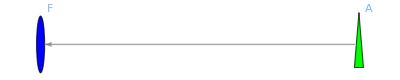

0

(ⅆA) |  
a

```mathematica
AddVariationalRelation[A->F]
VariationalRelationsOf[A]
dlF[-a,-b]//ExpandVertDiff[ConstantTensors->A]
dlA[-a]//ExpandVertDiff[ConstantTensors->F]
```

```mathematica
SymplecticCurrentOf1Form[A,LCDer][VertDiff@LEMwithF/.ruledlF]//ContractMetric//Simplification
```

-1/2 √(-g^OverTilde[~]) (n_∇) | a
  ((ⅆA) | b
 ⩕(ⅆF) |   |  
a | b)

We remove the VariationalRelation to study the final and best approach in the following Section.

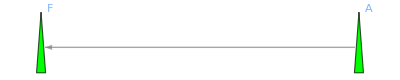

** RemoveVariationalRelation: Variational relation removed A→F

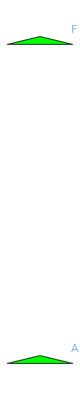

```mathematica
VariationalRelationsOf[{A,F}]
RemoveVariationalRelation[A->F]
VariationalRelationsOf[{A,F}]
```

## Chapter.Section. CPS of EM - Fourth approach (GenerateExpandVertDiff)

### Chapter.Section.Subsection. Lagrangian

In this Section we present the way that is more aligned with the philosophy of xCPS: through GenerateExpandVertDiff.

```mathematica
LEMwithF
```

1/4 √(-g^OverTilde[~]) F |   |  
a | b F | a | b
  |

```mathematica
VariationalRelationsOf[{A,F}]
```

-Graphics-

Recall that GenerateExpandVertDiffRule creates Variational Relations (see Subsection Chapter.Subsection.Subsection)

```mathematica
GenerateExpandVertDiffRule[{dlF[-a,-b],LCDer[-a]@dlA[-b]-LCDer[-b]@dlA[-a]}]
VariationalRelationsOf[{A,F}]
```

** GenerateExpandVertDiffRule: Expansion formula generated for dlF.

** AddVariationalRelation: Variational relation created A→F.

-Graphics-

### Chapter.Section.Subsection. FirstVariation

```mathematica
FirstVariation[A,LCDer][LEMwithF]//ContractMetric//Simplification
```

TotalDerivativeOfLCDer[-√(-g^OverTilde[~]) (ⅆA) | a
  F |   |  
a | b (n_∇) | b
 ]+√(-g^OverTilde[~]) (ⅆA) | a
  ∇_b F |   | b
a |

### Chapter.Section.Subsection. EOM

```mathematica
EOMLEMwithF=EOM[A,LCDer][LEMwithF]//ContractMetric//Simplification
```

√(-g^OverTilde[~]) ∇_b F | a | b
  |

### Chapter.Section.Subsection. SymplecticPotential

```mathematica
SymplecticPotential[A][LEMwithF]//ContractMetric//Simplification
```

-√(-g^OverTilde[~]) (ⅆA) | a
  F |   |  
a | b (n_∇) | b

### Chapter.Section.Subsection. SymplecticCurrent

```mathematica
SymplecticCurrent[A][LEMwithF]//ContractMetric//Simplification
```

√(-g^OverTilde[~]) (n_∇) | a
  (-((ⅆA) | b
 ⩕∇_a (ⅆA) |  
b)+(ⅆA) | b
 ⩕∇_b (ⅆA) |  
a)

Remark: ⅆF is expanded in terms of ⅆA. The option HoldExpandVertDiff allows to keep ⅆF.

```mathematica
SymplecticCurrent[A,LCDer,HoldExpandVertDiff->F][LEMwithF]//ContractMetric//Simplification
```

-√(-g^OverTilde[~]) (n_∇) | a
  ((ⅆA) | b
 ⩕(ⅆF) |   |  
a | b)

Which is equivalent to:

```mathematica
SymplecticPotential[A][LEMwithF]//VertDiff//ExpandVertDiff[NonConstantTensors->A,HoldExpandVertDiff->F]//ContractMetric//Simplification
```

-√(-g^OverTilde[~]) (n_∇) | a
  ((ⅆA) | b
 ⩕(ⅆF) |   |  
a | b)

### Chapter.Section.Subsection. Symmetries

#### Chapter.Section.Subsection.Subsubsection. EM gauge transformation

```mathematica
DefTensor[μ[],M]
vvf1=VariationalVectorA[c]LCDer[-c][μ[]]
```

** DefTensor: Defining tensor μ[].

** DefTensor: Defining tensor dlμ[].

** DefTensor: Defining tensor VariationalVectorμ[].

(δ/δA) | c
  ∇_c μ

```mathematica
NoetherSymmetryQ[vvf1][g][LEMwithF]
```

True

```mathematica
NoetherCurrentLEMwithFvvf1=NoetherCurrent[vvf1][g][LEMwithF]//ContractMetric//Simplification
```

-√(-g^OverTilde[~]) F |   |  
a | b (n_∇) | a
  ∇^b μ

We can in fact prove that 'vvf1' is not only a symmetry, but it is also a gauge transformation i.e., a transformation that, when restricted to the space of solutions (on-shell) has Hamiltonian=0:

```mathematica
With[{index=List@@FindFreeIndices[EOMLEMwithF//Evaluate][[1]]},
NoetherCurrentLEMwithFvvf1-μ[]NormalOfLCDer[-index]EOMLEMwithF-NormalOfLCDer[-a]LCDer[-b][-√(-Overscript[g, OverTilde[~]]) μ[]F[a,b]]]//ContractMetric//Simplification//Expand
```

0

Indeed, the previous computation shows that

NoetherCurrentLEMwithFvvf1=√(-g^OverTilde[~])((n)_∇) |  
a ∇_b T^ab (on-shell)

for some antisymmetric tensor T^ab (in this case T^ab=-√(-g^OverTilde[~])μF^ab). It is easy to see that when restricted to a Cauchy surface (where((n)_∇) | a
  turns into its unitary normal vector field), 'NoetherCurrentLEMwithFvvf1' is a divergence with respect to the induced Levi-Civita connection. Thus, the charged associated with 'vvf1', which is obtained integrating 'NoetherCurrentLEMwithFvvf1' over a Cauchy surface (without boundary), vanishes.

We can of course explicitly check that NoetherCurrentLEMwithFvvf1 is the Hamiltonian function of 'vvf1':

ⅈ_vvf1 SymplecticCurrent=ⅆNoetherCurrentLEMwithFvvf1

```mathematica
(VertInt[vvf1][SymplecticCurrent[A,LCDer][LEMwithF]]-VertDiff[NoetherCurrentLEMwithFvvf1])//ExpandVertInt[NonConstantTensors->A]//ContractMetric//Simplification
```

0

We can also define the VVF:

```mathematica
vvf2=VVFFromLieD[xi][g,F]
```

(δ/δF) | a | b
  |   (ℒ_ξ F |   |  
a | b)+(δ/δg) | a | b
  |   (ℒ_ξ g |   |  
a | b)

```mathematica
NoetherSymmetryQ[vvf2][g][LEMwithF]
```

True

#### Chapter.Section.Subsection.Subsubsection. SymmetryPotential

```mathematica
NoetherCurrent[vvf2][g][LEMwithF]//Quiet
```

1/4 √(-g^OverTilde[~]) F |   |  
b | c F | b | c
  |   (n_∇) |  
a ξ | a

### Chapter.Section.Subsection. CurrentFromVector

```mathematica
xicurrentwifhF=CurrentFromVector[xi][A,LCDer][LEMwithF]//LieDToCovD[#,LCDer]&//ContractMetric//Simplification
```

1/4 √(-g^OverTilde[~]) (-4 F |   |  
a | c (n_∇) | a
  ξ | b
  ∇_b A | c
 +F |   |  
b | c (F | b | c
  |   (n_∇) | a
  ξ |  
a-4 A | a
  (n_∇) | b
  ∇^c ξ |  
a))

## Chapter.Section. Reset session

We reset everything: $ConstantSymbols, $Parameters, $ScalarFunctions, $Metrics, $CovDs, $VertForms, $Manifolds, and $VBundles.

```mathematica
ResetSession[]
```

** SetSigns: All constant signs set to 1.

## Chapter. Variational calculus - Full example - General Relativity

## Chapter.Section. Initial definitions

In this Chapter we present the Covariant Phase Space of General Relativity. Since we have partially covered this topic in Section Chapter.Section of the introduction, we will avoid many explanations that have been already covered there and along the rest of the notebook.

```mathematica
$DefInfoQ=False;
DefConstantSymbol[dimen]
DefManifold[M,dimen,{a,b,c,d,e,f,h,i,j,k,l}]
DefMetric[-1,g[-a,-b],LCDer,{";","∇"}] 
$DefInfoQ=True;
```

## Chapter.Section. CPS of General Relativity

### Chapter.Section.Subsection. Lagrangian

```mathematica
LGR= RicciScalarLCDer[]Sqrt[-Detg[]]
```

√(-g^OverTilde[~]) R[∇]

### Chapter.Section.Subsection. FirstVariation

```mathematica
FirstVariation[LCDer][LGR]
```

(ⅆg) |   |  
a | b (-√(-g^OverTilde[~]) R[∇] | a | b
  |  +1/2 √(-g^OverTilde[~]) g | a | b
  |   R[∇])+TotalDerivativeOfLCDer[-√(-g^OverTilde[~]) (n_∇) | a
  ∇_a (ⅆg) |   | b
b |  +√(-g^OverTilde[~]) (n_∇) | a
  ∇_c (ⅆg) |   | c
a |  ]

### Chapter.Section.Subsection. EOM

```mathematica
EinsteinEq=EOM[g,LCDer][LGR]//ContractMetric//Simplification
```

1/2 √(-g^OverTilde[~]) (-2 R[∇] | a | b
  |  +g | a | b
  |   R[∇])

### Chapter.Section.Subsection. SymplecticPotential

```mathematica
SymplecticPotential[g,LCDer][LGR]//ContractMetric//Simplification
```

√(-g^OverTilde[~]) (n_∇) | a
  (-∇_a (ⅆg) | b |  
  | b+∇_b (ⅆg) |   | b
a |  )

### Chapter.Section.Subsection. SymplecticCurrent

```mathematica
SymplecticCurrentGRxCPS=SymplecticCurrent[g,LCDer][LGR]//ContractMetric//Simplification
```

1/2 √(-g^OverTilde[~]) (n_∇) | a
  ((ⅆg) |   | b
a |  ⩕∇_b (ⅆg) | c |  
  | c-(ⅆg) | b |  
  | b⩕∇_a (ⅆg) | c |  
  | c+(ⅆg) | b |  
  | b⩕∇_c (ⅆg) |   | c
a |  +(ⅆg) | b | c
  |  ⩕∇_a (ⅆg) |   |  
b | c-2 ((ⅆg) | b | c
  |  ⩕∇_c (ⅆg) |   |  
a | b))

We know the theoretical result (see, for instance [ItemNumbered]):

```mathematica
SymplecticCurrentGRTheoretical=√(-Overscript[g, OverTilde[~]]){{(n_∇), {{a}, {}}}}(-1/2{{δ, {{, , , d, e, f}, {a, b, c, , , }}}}{{(ⅆg), {{, b}, {e, }}}}⩕∇_d {{(ⅆg), {{, c}, {f, }}}}+1/2 LCDer[b][{{(ⅆg), {{, c}, {a, }}}}⩕{{(ⅆg), {{, }, {b, c}}}}])//ContractMetric//Simplification
```

1/2 √(-g^OverTilde[~]) (n_∇) | a
  ((ⅆg) |   | b
a |  ⩕∇_b (ⅆg) | c |  
  | c-(ⅆg) | b |  
  | b⩕∇_a (ⅆg) | c |  
  | c+(ⅆg) | b |  
  | b⩕∇_c (ⅆg) |   | c
a |  +(ⅆg) | b | c
  |  ⩕∇_a (ⅆg) |   |  
b | c-2 ((ⅆg) | b | c
  |  ⩕∇_c (ⅆg) |   |  
a | b))

We can compare and see that they are equal:

```mathematica
SymplecticCurrentGRxCPS-SymplecticCurrentGRTheoretical
```

0

### Chapter.Section.Subsection. Symmetries

#### Chapter.Section.Subsection.Subsubsection Diffeomorphism transformation

```mathematica
$DefInfoQ=False;
DefTensor[xi[a],M,PrintAs->"ξ"]
$DefInfoQ=True;

vvfGR=VVFFromLieD[xi][g]
```

(δ/δg) | a | b
  |   (ℒ_ξ g |   |  
a | b)

We need to apply Bianchi's identity. We could use TInvar or xTras, but to make this notebook self-contained, we use the following code (based on Teake's code).

```mathematica
BianchiRule1=RiemannLCDer[a_,b_,c_,d_]/;(Ordering[{b,c,d}]==={2,3,1})->RiemannLCDer[a,c,b,d]-RiemannLCDer[a,d,b,c];
BianchiRule2=LCDer[a_]@RiemannLCDer[b_,c_,d__]/;(Ordering[{a,b,c}]==={2,3,1})->LCDer[b]@RiemannLCDer[a,c,d]-LCDer[c]@RiemannLCDer[a,b,d];
BianchiContracted1=MakeRule[{LCDer[-e]@RiemannLCDer[-a,-c,-d,e],$RicciSign(LCDer[-c]@RicciLCDer[-a,-d]-LCDer[-a]@RicciLCDer[-c,-d])},MetricOn->All];
BianchiContracted2=MakeRule[{LCDer[-b]@RicciScalarLCDer[],2LCDer[-a][RicciLCDer[a,-b]]},MetricOn->All];

ApplyBianchi[expr_]:=ToCanonical[expr]//.BianchiRule1//.BianchiRule2//.BianchiContracted1//.BianchiContracted2//ToCanonical


NoetherSymmetryQ[vvfGR][g][LGR]//ApplyBianchi//ContractMetric//Simplification
NoetherSymmetryQ[vvfGR][g][LGR]//SortCovDs//ApplyBianchi//ContractMetric//Simplification
```

2 R[∇] | b |  
  | c ∇^a ξ | c
 +2 R[∇] | a |  
  | c ∇^b ξ | c
 +2 ∇^b ∇^a ∇_c ξ | c
 +2 ξ | c
  ∇_c R[∇] | a | b
  |  +∇_c ∇^c ∇^a ξ | b
 +∇_c ∇^c ∇^b ξ | a
 +3 g | a | b
  |   ∇_c ∇_d ∇^d ξ | c
 ==∇_c ∇^a ∇^b ξ | c
 +∇_c ∇^a ∇^c ξ | b
 +∇_c ∇^b ∇^a ξ | c
 +∇_c ∇^b ∇^c ξ | a
 +2 g | a | b
  |   ξ | c
  ∇_d R[∇] |   | d
c |  +g | a | b
  |   ∇_d ∇_c ∇^d ξ | c
 +2 g | a | b
  |   ∇_d ∇^d ∇_c ξ | c
 +2 g | a | b
  |   R[∇] |   |  
c | d ∇^d ξ | c

True

```mathematica
SymmetryPotentialvvfGRLGR=SymmetryPotential[vvfGR][g][LGR,SortCovDs,ApplyBianchi]//SortCovDs//ContractMetric//Simplification
```

√(-g^OverTilde[~]) (n_∇) | a
  R[∇] ξ |  
a

#### Chapter.Section.Subsection.Subsubsection Noether current (Noether Charges)

```mathematica
NoetherCurrent[vvfGR][g][LGR,ApplyBianchi]//ContractMetric//Simplification
NoetherCurrentvvfGRLGR=LieDToCovD[%,LCDer]//ContractMetric//Simplification
```

√(-g^OverTilde[~]) (n_∇) | a
  (R[∇] ξ |  
a-2 R[∇] |   |  
a | b ξ | b
 -2 ∇_a ∇_b ξ | b
 +g | b | c
  |   ∇_a ℒ_ξ g |   |  
b | c+∇_b ∇_a ξ | b
 +∇_b ∇^b ξ |  
a-g | b | c
  |   ∇_c ℒ_ξ g |   |  
a | b)

√(-g^OverTilde[~]) (n_∇) | a
  (R[∇] ξ |  
a-2 R[∇] |   |  
a | b ξ | b
 )

which is equal, as expected in this case (see [ItemNumbered]), to 2 i_n_M i_ξ EOM

```mathematica
With[{inds=FindFreeIndices[EinsteinEq//Evaluate]},
2 EinsteinEq xi[-inds[[1]]]NormalOfLCDer[-inds[[2]]]]//ContractMetric//Simplification
%-NoetherCurrentvvfGRLGR
```

√(-g^OverTilde[~]) (n_∇) | a
  (R[∇] ξ |  
a-2 R[∇] |   |  
a | b ξ | b
 )

0

### Chapter.Section.Subsection. Using the inverse metric

As we saw on Subsubsection Chapter.Section.Subsection.Subsubsection, the boolean $UseInverseMetric determines if {dlmetric,VariationalVectormetric} or {dlInvmetric,VariationalVectorInvmetric} are used.

```mathematica
$UseInverseMetric=False;
FirstVariation[][LGR] 
$UseInverseMetric=True;
FirstVariation[][LGR]
$UseInverseMetric=False;
```

(ⅆg) |   |  
a | b (-√(-g^OverTilde[~]) R[∇] | a | b
  |  +1/2 √(-g^OverTilde[~]) g | a | b
  |   R[∇])+TotalDerivativeOfLCDer[-√(-g^OverTilde[~]) (n_∇) | a
  ∇_a (ⅆg) |   | b
b |  +√(-g^OverTilde[~]) (n_∇) | a
  ∇_c (ⅆg) |   | c
a |  ]

ⅆ(g^-1) |   |  
a | b (√(-g^OverTilde[~]) R[∇] | a | b
  |  -1/2 √(-g^OverTilde[~]) g | a | b
  |   R[∇])+TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (n_∇) | a
  ∇_a ⅆ(g^-1) |   | c
c |  -√(-g^OverTilde[~]) (n_∇) | a
  ∇_b ⅆ(g^-1) |   | b
a |  ]

```mathematica
$UseInverseMetric=False;
EOM[g][LGR]//ContractMetric//Simplification
$UseInverseMetric=True;
EOM[g][LGR]//ContractMetric//Simplification
$UseInverseMetric=False;
```

1/2 √(-g^OverTilde[~]) (-2 R[∇] | a | b
  |  +g | a | b
  |   R[∇])

1/2 √(-g^OverTilde[~]) (2 R[∇] | a | b
  |  -g | a | b
  |   R[∇])

```mathematica
$UseInverseMetric=False;
SymplecticCurrent[][LGR]//ContractMetric//Simplification
$UseInverseMetric=True;
SymplecticCurrent[][LGR]//ContractMetric//Simplification
$UseInverseMetric=False;
```

1/2 √(-g^OverTilde[~]) (n_∇) | a
  ((ⅆg) |   | b
a |  ⩕∇_b (ⅆg) | c |  
  | c-(ⅆg) | b |  
  | b⩕∇_a (ⅆg) | c |  
  | c+(ⅆg) | b |  
  | b⩕∇_c (ⅆg) |   | c
a |  +(ⅆg) | b | c
  |  ⩕∇_a (ⅆg) |   |  
b | c-2 ((ⅆg) | b | c
  |  ⩕∇_c (ⅆg) |   |  
a | b))

1/2 √(-g^OverTilde[~]) (n_∇) | a
  (ⅆ(g^-1) |   | b
a |  ⩕∇_b ⅆ(g^-1) | c |  
  | c-ⅆ(g^-1) | b |  
  | b⩕∇_a ⅆ(g^-1) | c |  
  | c+ⅆ(g^-1) | b |  
  | b⩕∇_c ⅆ(g^-1) |   | c
a |  +ⅆ(g^-1) | b | c
  |  ⩕∇_a ⅆ(g^-1) |   |  
b | c-2 (ⅆ(g^-1) | b | c
  |  ⩕∇_c ⅆ(g^-1) |   |  
a | b))

## Chapter.Section. Reset session

We reset everything: $ConstantSymbols, $Parameters, $ScalarFunctions, $Metrics, $CovDs, $VertForms, $Manifolds, and $VBundles.

```mathematica
ResetSession[]
```

** SetSigns: All constant signs set to 1.

## Chapter. Variational calculus - Full example - Generic Lagrangians

## Chapter.Section. Initial definitions

```mathematica
$DefInfoQ=False;
DefConstantSymbol[dimen]
DefManifold[M,dimen,{a,b,c,d,e,f,h,i,j,k,l}]
DefMetric[-1,g[-a,-b],LCDer,{";","∇"}] 
$DefInfoQ=True;
```

## Chapter.Section. CPS of f(ϕ) theories

### Chapter.Section.Subsection. Lagrangian that depends only on ϕ

One of the most powerful features of xCPS is that it can can handle generic Lagrangians that depend on some tensors. For instance, we can consider a Lagrangian that depends on a scalar field. Based on what we explained on Subsection Chapter.Section.Subsection, one might naively think that it should be enough to define

```mathematica
DefTensor[phi[],M,PrintAs->"ϕ"]
DefScalarFunction[LScalar0,{phi},PrintAs->"L_0"]
```

** DefTensor: Defining tensor phi[].

** DefTensor: Defining tensor dlphi[].

** DefTensor: Defining tensor VariationalVectorphi[].

** DefScalarFunction: Defining scalar function LScalar0. It depends on phi

However, if we compute its variation, we see that no derivatives are present:

```mathematica
VertDiff[LScalar0[phi]]==(VertDiff[LScalar0[phi]]//ExpandVertDiff[])
```

** DefTensor: Defining tensor PartialLScalar0Partialphi[].

ⅆ[L_0[phi]]==(ⅆϕ) ((∂L_0)/(∂ϕ))

So the first variation of the Lagrangian returns simply its VertDiff:

```mathematica
FirstVariation[phi,LCDer][√(-Detg[])LScalar0[phi]]
```

√(-g^OverTilde[~]) (ⅆϕ) ((∂L_0)/(∂ϕ))

This is so because ϕ is assumed to be independent of its derivatives (this is consistent with the ∞-jet bundle formalism, see [ItemNumbered,ItemNumbered]).

```mathematica
DependenciesOfScalar[LScalar0]
```

{phi}

### Chapter.Section.Subsection. Lagrangian that depends on ∇ϕ

The correct approach is to explicitly indicate that the Lagrangian depends on the derivatives of ϕ. The way to do that is through Implode:

```mathematica
Implode[LCDer[-a]@phi[]]
Implode[LCDer[-a]@LCDer[-b]@phi[]]
```

∇ϕ |  
a

∇∇ϕ |   |  
a | b

This command defines internally the tensors LCDerphi and LCDerLCDerphi together with their VertDiff and VariationalVector (see Section A.Section of the Appendix for further details of the interaction between xCPS and Implode). The new tensors’ names are just the concatenation of their elements:

```mathematica
{LCDerphi,LCDerphi[-a]}
{LCDerLCDerphi,LCDerLCDerphi[-a,-b]}
```

{LCDerphi,∇ϕ |  
a}

{LCDerLCDerphi,∇∇ϕ |   |  
a | b}

Now we can define the Lagrangians with the correct dependencies:

```mathematica
DefScalarFunction[LScalar1,{LCDerphi},PrintAs->"L_1"]
DefScalarFunction[LScalar2,{phi,LCDerphi,LCDerLCDerphi},PrintAs->"L_2"]
```

** DefScalarFunction: Defining scalar function LScalar1. It depends on LCDerphi

** DefScalarFunction: Defining scalar function LScalar2. It depends on LCDerLCDerphi, LCDerphi and phi

```mathematica
DependenciesOfScalar[LScalar1]
DependenciesOfScalar[LScalar2]
```

{LCDerphi}

{LCDerLCDerphi,LCDerphi,phi}

Now, if we compute their VertDiff, we see that there are derivatives of ⅆϕ:

```mathematica
vd1=VertDiff[LScalar1[LCDerphi]]==(VertDiff[LScalar1[LCDerphi]]//ExpandVertDiff[]);
vd2=VertDiff[LScalar2[phi,LCDerphi,LCDerLCDerphi]]==(VertDiff[LScalar2[phi,LCDerphi,LCDerLCDerphi]]//ExpandVertDiff[]);
vd1
vd2
```

** DefTensor: Defining tensor PartialLScalar1PartialLCDerphi[a].

** DefTensor: Defining tensor PartialLScalar2Partialphi[].

** DefTensor: Defining tensor PartialLScalar2PartialLCDerphi[a].

** DefTensor: Defining tensor PartialLScalar2PartialLCDerLCDerphi[a,b].

ⅆ[L_1[LCDerphi]]==((∂L_1)/(∂∇ϕ)) | a
  ∇_a (ⅆϕ)

ⅆ[L_2[phi,LCDerphi,LCDerLCDerphi]]==(ⅆϕ) ((∂L_2)/(∂ϕ))+((∂L_2)/(∂∇ϕ)) | a
  ∇_a (ⅆϕ)+((∂L_2)/(∂∇∇ϕ)) | a | b
  |   (∇_b ∇_a (ⅆϕ)-1/2 g | c | d
  |   ∇_c ϕ (∇_a (ⅆg) |   |  
b | d+∇_b (ⅆg) |   |  
d | a-∇_d (ⅆg) |   |  
b | a))

### Chapter.Section.Subsection. FirstVariation

```mathematica
FirstVariation[phi,LCDer][√(-Detg[])LScalar1[LCDerphi]]
FirstVariation[phi,LCDer][√(-Detg[])LScalar2[phi,LCDerphi,LCDerLCDerphi]]
```

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ((∂L_1)/(∂∇ϕ)) |  
a]-√(-g^OverTilde[~]) (ⅆϕ) ∇_a ((∂L_1)/(∂∇ϕ)) | a

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ((∂L_2)/(∂∇ϕ)) |  
a-√(-g^OverTilde[~]) (ⅆϕ) (n_∇) | a
  ∇_b ((∂L_2)/(∂∇∇ϕ)) |   | b
a |  +√(-g^OverTilde[~]) (n_∇) | a
  ((∂L_2)/(∂∇∇ϕ)) |   |  
a | b ∇^b (ⅆϕ)]+(ⅆϕ) (√(-g^OverTilde[~]) ((∂L_2)/(∂ϕ))-√(-g^OverTilde[~]) ∇_a ((∂L_2)/(∂∇ϕ)) | a
 +√(-g^OverTilde[~]) ∇_b ∇_a ((∂L_2)/(∂∇∇ϕ)) | a | b
  |  )

### Chapter.Section.Subsection. SymplecticCurrent

```mathematica
sc1=SymplecticCurrent[phi,LCDer][√(-Detg[])LScalar1[LCDerphi]];
sc2=SymplecticCurrent[phi,LCDer][√(-Detg[])LScalar2[phi,LCDerphi,LCDerLCDerphi]];
sc1
sc2
```

** DefTensor: Defining tensor Partial2LScalar1Partial2LCDerphi[a,b].

** DefTensor: Defining tensor Partial2LScalar2Partial2LCDerLCDerphi[a,b,c,d].

** DefTensor: Defining tensor Partial2LScalar2PartialLCDerLCDerphiPartialLCDerphi[a,b,c].

** DefTensor: Defining tensor Partial2LScalar2PartialLCDerLCDerphiPartialphi[a,b].

** DefTensor: Defining tensor Partial2LScalar2Partial2LCDerphi[a,b].

** DefTensor: Defining tensor Partial2LScalar2PartialLCDerphiPartialphi[a].

√(-g^OverTilde[~]) (n_∇) |  
a ((∂^2 L_1)/(∂^2 ∇ϕ)) | b | a
  |   (∇_b (ⅆϕ)⩕(ⅆϕ))

√(-g^OverTilde[~]) (n_∇) |  
a (((∂^2 L_2)/(∂∇ϕ∂ϕ)) | a
  ((ⅆϕ)⩕(ⅆϕ))+((∂^2 L_2)/(∂∇∇ϕ∂∇ϕ)) | b | c | a
  |   |   (∇_c ∇_b (ⅆϕ)⩕(ⅆϕ))+((∂^2 L_2)/(∂^2 ∇ϕ)) | d | a
  |   (∇_d (ⅆϕ)⩕(ⅆϕ)))+√(-g^OverTilde[~]) (n_∇) |  
b (((∂^2 L_2)/(∂∇∇ϕ∂ϕ)) | a | b
  |   ((ⅆϕ)⩕∇_a (ⅆϕ))+((∂^2 L_2)/(∂^2 ∇∇ϕ)) | c | d | a | b
  |   |   |   (∇_d ∇_c (ⅆϕ)⩕∇_a (ⅆϕ))+((∂^2 L_2)/(∂∇∇ϕ∂∇ϕ)) | a | b | e
  |   |   (∇_e (ⅆϕ)⩕∇_a (ⅆϕ)))-√(-g^OverTilde[~]) (n_∇) |  
a (((∂^2 L_2)/(∂∇∇ϕ∂ϕ)) | a | b
  |   (∇_b (ⅆϕ)⩕(ⅆϕ))+((∂^2 L_2)/(∂^2 ∇∇ϕ)) | c | d | a | b
  |   |   |   (∇_b ∇_d ∇_c (ⅆϕ)⩕(ⅆϕ))+((∂^2 L_2)/(∂∇∇ϕ∂∇ϕ)) | a | b | e
  |   |   (∇_e ∇_b (ⅆϕ)⩕(ⅆϕ))+(∇_d ∇_c (ⅆϕ)⩕(ⅆϕ)) ∇_b ((∂^2 L_2)/(∂^2 ∇∇ϕ)) | c | d | a | b
  |   |   |  +(∇_e (ⅆϕ)⩕(ⅆϕ)) ∇_b ((∂^2 L_2)/(∂∇∇ϕ∂∇ϕ)) | a | b | e
  |   |  +((ⅆϕ)⩕(ⅆϕ)) ∇_b ((∂^2 L_2)/(∂∇∇ϕ∂ϕ)) | a | b
  |  )

It is clear that the standard scalar field theory is a particular case:

```mathematica
sc1/.{Partial2LScalar1Partial2LCDerphi->g}//ContractMetric
```

√(-g^OverTilde[~]) (n_∇) | a
  (∇_a (ⅆϕ)⩕(ⅆϕ))

```mathematica
setToZero={#->Zero}&/@Join[PartialPartialsOfTensor[phi],PartialPartialsOfTensor[LCDerLCDerphi]]//Flatten;
sc2/.setToZero//ContractMetric
sc2/.setToZero/.{Partial2LScalar2Partial2LCDerphi->g}//ContractMetric
```

√(-g^OverTilde[~]) (n_∇) |  
a ((∂^2 L_2)/(∂^2 ∇ϕ)) | b | a
  |   (∇_b (ⅆϕ)⩕(ⅆϕ))

√(-g^OverTilde[~]) (n_∇) | a
  (∇_a (ⅆϕ)⩕(ⅆϕ))

## Chapter.Section. CPS of f(Riemann), f(Ricci) and f(R) theories

### Chapter.Section.Subsection. Lagrangians

```mathematica
DefScalarFunction[Lagrangian1,{RiemannLCDer},PrintAs->""]
DefScalarFunction[Lagrangian2,{g,RiemannLCDer},PrintAs->""]
DefScalarFunction[Lagrangian3,{g,RicciLCDer},PrintAs->""]
DefScalarFunction[Lagrangian4,{RicciScalarLCDer},PrintAs->""]
PrintAs[RiemannLCDer]^="Riem";
PrintAs[RicciLCDer]^="Ric";
PrintAs[RicciScalarLCDer]^="R";
```

** DefScalarFunction: Defining scalar function Lagrangian1. It depends on RiemannLCDer

** DefScalarFunction: Defining scalar function Lagrangian2. It depends on g and RiemannLCDer

** DefScalarFunction: Defining scalar function Lagrangian3. It depends on g and RicciLCDer

** DefScalarFunction: Defining scalar function Lagrangian4. It depends on RicciScalarLCDer

```mathematica
Lagrangiandensity1=√(-Detg[])Lagrangian1[RiemannLCDer[-a,-b,-c,-e]]
Lagrangiandensity2=√(-Detg[])Lagrangian2[g,RiemannLCDer]
Lagrangiandensity3=√(-Detg[])Lagrangian3[g,RicciLCDer]
Lagrangiandensity4=√(-Detg[])Lagrangian4[RicciScalarLCDer]
```

√(-g^OverTilde[~]) [Riem |   |   |   |  
a | b | c | e]

√(-g^OverTilde[~]) [g,RiemannLCDer]

√(-g^OverTilde[~]) [g,RicciLCDer]

√(-g^OverTilde[~]) [RicciScalarLCDer]

### Chapter.Section.Subsection. FirstVariation

```mathematica
firstvar1=FirstVariation[g,LCDer][Lagrangiandensity1]//SortCovDs//Simplification;
firstvar2=FirstVariation[g,LCDer][Lagrangiandensity2]//SortCovDs//Simplification;
firstvar3=FirstVariation[g,LCDer][Lagrangiandensity3]//SortCovDs//Simplification;
firstvar4=FirstVariation[g,LCDer][Lagrangiandensity4]//SortCovDs//Simplification;
firstvar1
firstvar2
firstvar3
firstvar4
```

** DefTensor: Defining tensor PartialLagrangian1PartialRiemannLCDer[a,b,c,d].

** DefTensor: Defining tensor PartialLagrangian2Partialg[a,b].

** DefTensor: Defining tensor PartialLagrangian2PartialInvg[-a,-b].

** DefTensor: Defining tensor PartialLagrangian2PartialRiemannLCDer[a,b,c,d].

** DefTensor: Defining tensor PartialLagrangian3Partialg[a,b].

** DefTensor: Defining tensor PartialLagrangian3PartialInvg[-a,-b].

** DefTensor: Defining tensor PartialLagrangian3PartialRicciLCDer[a,b].

** DefTensor: Defining tensor PartialLagrangian4PartialRicciScalarLCDer[].

TotalDerivativeOfLCDer[2 √(-g^OverTilde[~]) (n_∇) | a
  (-(ⅆg) | b | c
  |   ∇_d (∂/(∂Riem)) |   |   |   | d
a | b | c |  +(∂/(∂Riem)) |   |   |   |  
a | b | c | d ∇^d (ⅆg) | b | c
  |  )]+1/2 √(-g^OverTilde[~]) (ⅆg) | a | b
  |   (g |   |  
a | b [(Riem |   |   |   |  
a | b | c | e)]+2 (∂/(∂Riem)) |   | c | d | e
a |   |   |   Riem |   |   |   |  
b | c | d | e-4 ∇_d ∇_c (∂/(∂Riem)) |   | c |   | d
a |   | b |  )

TotalDerivativeOfLCDer[2 √(-g^OverTilde[~]) (n_∇) | a
  (-(ⅆg) | b | c
  |   ∇_d (∂/(∂Riem)) |   |   |   | d
a | b | c |  +(∂/(∂Riem)) |   |   |   |  
a | b | c | d ∇^d (ⅆg) | b | c
  |  )]+1/2 √(-g^OverTilde[~]) (ⅆg) | a | b
  |   (g |   |  
a | b [(g),(RiemannLCDer)]+2 ((∂/(∂g)) |   |  
a | b+(∂/(∂Riem)) |   | c | d | e
a |   |   |   Riem |   |   |   |  
b | c | d | e-2 ∇_d ∇_c (∂/(∂Riem)) |   | c |   | d
a |   | b |  ))

1/2 (TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (n_∇) | a
  (-(∂/(∂Ric)) |   | b
a |   ∇_b (ⅆg) | c |  
  | c-(∂/(∂Ric)) | b | c
  |   (∇_a (ⅆg) |   |  
b | c-2 ∇_c (ⅆg) |   |  
a | b)+(ⅆg) | b | c
  |   (∇_a (∂/(∂Ric)) |   |  
b | c-2 ∇_c (∂/(∂Ric)) |   |  
a | b)+(ⅆg) | b |  
  | b ∇_c (∂/(∂Ric)) |   | c
a |  )]+√(-g^OverTilde[~]) (ⅆg) | a | b
  |   (2 (∂/(∂g)) |   |  
a | b+2 ∇_c ∇_b (∂/(∂Ric)) |   | c
a |  -∇_c ∇^c (∂/(∂Ric)) |   |  
a | b+g |   |  
a | b ([(g),(RicciLCDer)]-∇_d ∇_c (∂/(∂Ric)) | c | d
  |  )))

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (n_∇) | a
  (-(∂/(∂R)) ∇_a (ⅆg) | b |  
  | b+(ⅆg) | b |  
  | b ∇_a (∂/(∂R))+(∂/(∂R)) ∇_b (ⅆg) |   | b
a |  -(ⅆg) |   |  
a | b ∇^b (∂/(∂R)))]+1/2 √(-g^OverTilde[~]) (ⅆg) | a | b
  |   (-2 (∂/(∂R)) Ric |   |  
a | b+2 ∇_b ∇_a (∂/(∂R))+g |   |  
a | b ([(RicciScalarLCDer)]-2 ∇_c ∇^c (∂/(∂R))))

Remark: In the last expression, (∂/(∂R)) is simply '[R] but for simplicity and notational consistency, we keep the PartialPartial notation.

They all reduce to GR. Let us, for instance, check that for :

```mathematica
firstvar3GR=firstvar3/.{PartialLagrangian3PartialRicciLCDer:> g,PartialLagrangian3Partialg[ind1_,ind2_]:>-RicciLCDer[ind1,ind2],Lagrangian3[__]:>RicciScalarLCDer[]}//ContractMetric//Simplification
```

-√(-g^OverTilde[~]) (ⅆg) | a | b
  |   Ric |   |  
a | b+1/2 √(-g^OverTilde[~]) (ⅆg) | a |  
  | a R+TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (n_∇) | a
  (-∇_a (ⅆg) | b |  
  | b+∇_b (ⅆg) |   | b
a |  )]

```mathematica
firstvarGR=FirstVariation[g,LCDer][√(-Detg[])RicciScalarLCDer[]]
```

(ⅆg) |   |  
a | b (-√(-g^OverTilde[~]) Ric | a | b
  |  +1/2 √(-g^OverTilde[~]) g | a | b
  |   R)+TotalDerivativeOfLCDer[-√(-g^OverTilde[~]) (n_∇) | a
  ∇_a (ⅆg) |   | b
b |  +√(-g^OverTilde[~]) (n_∇) | a
  ∇_c (ⅆg) |   | c
a |  ]

```mathematica
firstvarGR-firstvar3GR//ContractMetric//Simplification
```

0

### Chapter.Section.Subsection. Wald’s entropy

We can compute one of the important terms for Wald’s entropy [ItemNumbered]:

```mathematica
EOM[RiemannLCDer][Lagrangiandensity3]
```

1/8 (√(-g^OverTilde[~]) g | b | d
  |   (∂/(∂Ric)) | a | c
  |  -√(-g^OverTilde[~]) g | b | c
  |   (∂/(∂Ric)) | a | d
  |  -√(-g^OverTilde[~]) g | a | d
  |   (∂/(∂Ric)) | b | c
  |  +√(-g^OverTilde[~]) g | a | c
  |   (∂/(∂Ric)) | b | d
  |  +√(-g^OverTilde[~]) g | d | b
  |   (∂/(∂Ric)) | c | a
  |  -√(-g^OverTilde[~]) g | d | a
  |   (∂/(∂Ric)) | c | b
  |  -√(-g^OverTilde[~]) g | c | b
  |   (∂/(∂Ric)) | d | a
  |  +√(-g^OverTilde[~]) g | c | a
  |   (∂/(∂Ric)) | d | b
  |  )

### Chapter.Section.Subsection. SymplecticCurrent

```mathematica
symplcurrent1=SymplecticCurrent[][Lagrangiandensity1]//ContractMetric//Simplification;
symplcurrent2=SymplecticCurrent[][Lagrangiandensity2]//ContractMetric//Simplification;
symplcurrent3=SymplecticCurrent[][Lagrangiandensity3]//ContractMetric//ContractMetric//Simplification;
symplcurrent4=SymplecticCurrent[][Lagrangiandensity4]//ContractMetric//ContractMetric//ContractMetric//Simplification;
symplcurrent1
symplcurrent2
symplcurrent3
symplcurrent4
```

** DefTensor: Defining tensor Partial2Lagrangian1Partial2RiemannLCDer[a,b,c,d,e,f,h,i].

** DefTensor: Defining tensor Partial2Lagrangian2PartialgPartialRiemannLCDer[a,b,c,d,e,f].

** DefTensor: Defining tensor Partial2Lagrangian2PartialInvgPartialRiemannLCDer[-a,-b,c,d,e,f].

** DefTensor: Defining tensor Partial2Lagrangian2Partial2RiemannLCDer[a,b,c,d,e,f,h,i].

** DefTensor: Defining tensor Partial2Lagrangian3PartialgPartialRicciLCDer[a,b,c,d].

** DefTensor: Defining tensor Partial2Lagrangian3PartialInvgPartialRicciLCDer[-a,-b,c,d].

** DefTensor: Defining tensor Partial2Lagrangian3Partial2RicciLCDer[a,b,c,d].

** DefTensor: Defining tensor Partial2Lagrangian4Partial2RicciScalarLCDer[].

√(-g^OverTilde[~]) (n_∇) | a
  ((∂/(∂Riem)) | b | c | d | e
  |   |   |   ((ⅆg) |   |  
b | d⩕∇_a (ⅆg) |   |  
c | e)-2 (∂/(∂Riem)) | b | c | d | e
  |   |   |   ((ⅆg) |   |  
b | d⩕∇_e (ⅆg) |   |  
a | c)+2 (∂^2/(∂^2 Riem)) |   | f | h | i |   |   |   | j
a |   |   |   | b | c | d |   Riem | b | c | d | e
  |   |   |   ((ⅆg) |   |  
e | j⩕∇_i (ⅆg) |   |  
f | h)+(∂/(∂Riem)) |   | b | c | d
a |   |   |   ((ⅆg) |   |  
b | c⩕∇_d (ⅆg) | e |  
  | e+2 ((ⅆg) |   | e
c |  ⩕∇_b (ⅆg) |   |  
d | e)+2 ((ⅆg) |   | e
c |  ⩕∇_d (ⅆg) |   |  
b | e)-2 ((ⅆg) |   | e
c |  ⩕∇_e (ⅆg) |   |  
b | d)+(ⅆg) | e |  
  | e⩕∇_d (ⅆg) |   |  
b | c)+2 (∂^2/(∂^2 Riem)) |   | f | h | i |   |   |   | j
a |   |   |   | b | c | d |   Riem | b | c | d | e
  |   |   |   ((ⅆg) |   |  
f | h⩕∇_i (ⅆg) |   |  
e | j)-4 (∂^2/(∂^2 Riem)) |   | b | c | d | e | f | h | i
a |   |   |   |   |   |   |   ((ⅆg) |   |  
b | c⩕∇_d ∇_i ∇_f (ⅆg) |   |  
e | h-∇_d (ⅆg) |   |  
b | c⩕∇_i ∇_f (ⅆg) |   |  
e | h)+4 ((ⅆg) |   |  
b | d⩕∇_i ∇_f (ⅆg) |   |  
e | h) ∇_c (∂^2/(∂^2 Riem)) |   | b | c | d | e | f | h | i
a |   |   |   |   |   |   |  -((ⅆg) |   |  
b | d⩕(ⅆg) | e |  
  | e) ∇_c (∂/(∂Riem)) |   | b | c | d
a |   |   |  +2 (∂^2/(∂^2 Riem)) |   | h |   | i |   |   |   | j
a |   | f |   | b | c | d |   ((ⅆg) |   |  
e | j⩕(ⅆg) |   |  
h | i) ∇^f Riem | b | c | d | e
  |   |   |  +2 Riem | b | c | d | e
  |   |   |   ((ⅆg) |   |  
e | j⩕(ⅆg) |   |  
f | i) ∇_h (∂^2/(∂^2 Riem)) |   | f | h | i |   |   |   | j
a |   |   |   | b | c | d |  )

√(-g^OverTilde[~]) (n_∇) | a
  (2 (∂^2/(∂g∂Riem)) | b | c |   | d | e | f
  |   | a |   |   |   ((ⅆg) |   |  
b | c⩕∇_f (ⅆg) |   |  
d | e)+(∂/(∂Riem)) | b | c | d | e
  |   |   |   ((ⅆg) |   |  
b | d⩕∇_a (ⅆg) |   |  
c | e)-2 (∂/(∂Riem)) | b | c | d | e
  |   |   |   ((ⅆg) |   |  
b | d⩕∇_e (ⅆg) |   |  
a | c)+2 (∂^2/(∂g∂Riem)) | b | c |   | d | e | f
  |   | a |   |   |   ((ⅆg) |   |  
d | e⩕∇_f (ⅆg) |   |  
b | c)+2 (∂^2/(∂^2 Riem)) |   | f | h | i |   |   |   | j
a |   |   |   | b | c | d |   Riem | b | c | d | e
  |   |   |   ((ⅆg) |   |  
e | j⩕∇_i (ⅆg) |   |  
f | h)+(∂/(∂Riem)) |   | b | c | d
a |   |   |   ((ⅆg) |   |  
b | c⩕∇_d (ⅆg) | e |  
  | e+2 ((ⅆg) |   | e
c |  ⩕∇_b (ⅆg) |   |  
d | e)+2 ((ⅆg) |   | e
c |  ⩕∇_d (ⅆg) |   |  
b | e)-2 ((ⅆg) |   | e
c |  ⩕∇_e (ⅆg) |   |  
b | d)+(ⅆg) | e |  
  | e⩕∇_d (ⅆg) |   |  
b | c)+2 (∂^2/(∂^2 Riem)) |   | f | h | i |   |   |   | j
a |   |   |   | b | c | d |   Riem | b | c | d | e
  |   |   |   ((ⅆg) |   |  
f | h⩕∇_i (ⅆg) |   |  
e | j)-4 (∂^2/(∂^2 Riem)) |   | b | c | d | e | f | h | i
a |   |   |   |   |   |   |   ((ⅆg) |   |  
b | c⩕∇_d ∇_i ∇_f (ⅆg) |   |  
e | h-∇_d (ⅆg) |   |  
b | c⩕∇_i ∇_f (ⅆg) |   |  
e | h)+4 ((ⅆg) |   |  
b | d⩕∇_i ∇_f (ⅆg) |   |  
e | h) ∇_c (∂^2/(∂^2 Riem)) |   | b | c | d | e | f | h | i
a |   |   |   |   |   |   |  -((ⅆg) |   |  
b | d⩕(ⅆg) | e |  
  | e) ∇_c (∂/(∂Riem)) |   | b | c | d
a |   |   |  +2 ((ⅆg) |   |  
b | c⩕(ⅆg) |   |  
d | f) ∇_e (∂^2/(∂g∂Riem)) | b | c |   | d | e | f
  |   | a |   |   |  +2 (∂^2/(∂^2 Riem)) |   | h |   | i |   |   |   | j
a |   | f |   | b | c | d |   ((ⅆg) |   |  
e | j⩕(ⅆg) |   |  
h | i) ∇^f Riem | b | c | d | e
  |   |   |  +2 Riem | b | c | d | e
  |   |   |   ((ⅆg) |   |  
e | j⩕(ⅆg) |   |  
f | i) ∇_h (∂^2/(∂^2 Riem)) |   | f | h | i |   |   |   | j
a |   |   |   | b | c | d |  )

1/4 √(-g^OverTilde[~]) (n_∇) | a
  (-2 (∂^2/(∂g∂Ric)) | b | c |   | d
  |   | a |   ((ⅆg) |   |  
b | c⩕∇_d (ⅆg) | e |  
  | e)-4 (∂/(∂Ric)) | b | c
  |   ((ⅆg) |   | d
b |  ⩕∇_a (ⅆg) |   |  
c | d)+4 (∂/(∂Ric)) | b | c
  |   ((ⅆg) |   | d
b |  ⩕∇_d (ⅆg) |   |  
a | c)-2 (∂^2/(∂^2 Ric)) |   | b | c | d
a |   |   |   ((ⅆg) |   | e
b |  ⩕∇_e ∇_d ∇_c (ⅆg) | f |  
  | f)+4 (∂^2/(∂^2 Ric)) |   | b | c | d
a |   |   |   ((ⅆg) |   | e
b |  ⩕∇_e ∇_f ∇_d (ⅆg) |   | f
c |  )-2 (∂^2/(∂^2 Ric)) |   | b | c | d
a |   |   |   ((ⅆg) |   | e
b |  ⩕∇_e ∇_f ∇^f (ⅆg) |   |  
c | d)-2 (∂/(∂Ric)) |   | b
a |   ((ⅆg) | c |  
  | c⩕∇_b (ⅆg) | d |  
  | d)+2 (∂/(∂Ric)) |   | b
a |   ((ⅆg) | c | d
  |  ⩕∇_b (ⅆg) |   |  
c | d)-2 (∂^2/(∂g∂Ric)) | b | c | d | e
  |   |   |   ((ⅆg) |   |  
b | c⩕∇_a (ⅆg) |   |  
d | e-2 ((ⅆg) |   |  
b | c⩕∇_e (ⅆg) |   |  
a | d)+(ⅆg) |   |  
d | e⩕∇_a (ⅆg) |   |  
b | c)+4 (∂^2/(∂g∂Ric)) | b | c |   | d
  |   | a |   ((ⅆg) |   | e
d |  ⩕∇_e (ⅆg) |   |  
b | c)+(∂^2/(∂^2 Ric)) |   | b | c | d
a |   |   |   ((ⅆg) | e |  
  | e⩕∇_b ∇_d ∇_c (ⅆg) | f |  
  | f)-2 (∂^2/(∂^2 Ric)) |   | b | c | d
a |   |   |   ((ⅆg) | e |  
  | e⩕∇_b ∇_f ∇_d (ⅆg) |   | f
c |  )+(∂^2/(∂^2 Ric)) |   | b | c | d
a |   |   |   ((ⅆg) | e |  
  | e⩕∇_b ∇_f ∇^f (ⅆg) |   |  
c | d)-2 (∂^2/(∂g∂Ric)) | b | c |   | d
  |   | a |   ((ⅆg) | e |  
  | e⩕∇_d (ⅆg) |   |  
b | c)-(∂^2/(∂^2 Ric)) |   | b | c | d
a |   |   |   (∇_b (ⅆg) | e |  
  | e⩕∇_d ∇_c (ⅆg) | f |  
  | f)+2 (∂^2/(∂^2 Ric)) |   | b | c | d
a |   |   |   (∇_b (ⅆg) | e |  
  | e⩕∇_f ∇_d (ⅆg) |   | f
c |  )-(∂^2/(∂^2 Ric)) |   | b | c | d
a |   |   |   (∇_b (ⅆg) | e |  
  | e⩕∇_f ∇^f (ⅆg) |   |  
c | d)+(∂^2/(∂^2 Ric)) | b | c | d | e
  |   |   |   ((ⅆg) |   |  
b | c⩕∇_a ∇_e ∇_d (ⅆg) | f |  
  | f-2 ((ⅆg) |   |  
b | c⩕∇_a ∇_f ∇_e (ⅆg) |   | f
d |  )+(ⅆg) |   |  
b | c⩕∇_a ∇_f ∇^f (ⅆg) |   |  
d | e-∇_a (ⅆg) |   |  
b | c⩕∇_e ∇_d (ⅆg) | f |  
  | f+2 (∇_a (ⅆg) |   |  
b | c⩕∇_f ∇_e (ⅆg) |   | f
d |  )-∇_a (ⅆg) |   |  
b | c⩕∇_f ∇^f (ⅆg) |   |  
d | e+2 (∇_c (ⅆg) |   |  
a | b⩕∇_e ∇_d (ⅆg) | f |  
  | f)-4 (∇_c (ⅆg) |   |  
a | b⩕∇_f ∇_e (ⅆg) |   | f
d |  )+2 (∇_c (ⅆg) |   |  
a | b⩕∇_f ∇^f (ⅆg) |   |  
d | e))+((ⅆg) |   |  
b | c⩕∇_e ∇_d (ⅆg) | f |  
  | f) ∇_a (∂^2/(∂^2 Ric)) | b | c | d | e
  |   |   |  -2 ((ⅆg) |   |  
b | c⩕∇_f ∇_e (ⅆg) |   | f
d |  ) ∇_a (∂^2/(∂^2 Ric)) | b | c | d | e
  |   |   |  +((ⅆg) |   |  
b | c⩕∇_f ∇^f (ⅆg) |   |  
d | e) ∇_a (∂^2/(∂^2 Ric)) | b | c | d | e
  |   |   |  +2 ((ⅆg) |   |  
b | c⩕(ⅆg) |   |  
d | e) ∇_a (∂^2/(∂g∂Ric)) | b | c | d | e
  |   |   |  -((ⅆg) |   |  
b | c⩕(ⅆg) | d |  
  | d) ∇_a (∂/(∂Ric)) | b | c
  |  +((ⅆg) | e |  
  | e⩕∇_d ∇_c (ⅆg) | f |  
  | f) ∇_b (∂^2/(∂^2 Ric)) |   | b | c | d
a |   |   |  -2 ((ⅆg) | e |  
  | e⩕∇_f ∇_d (ⅆg) |   | f
c |  ) ∇_b (∂^2/(∂^2 Ric)) |   | b | c | d
a |   |   |  +((ⅆg) | e |  
  | e⩕∇_f ∇^f (ⅆg) |   |  
c | d) ∇_b (∂^2/(∂^2 Ric)) |   | b | c | d
a |   |   |  +2 ((ⅆg) |   |  
b | c⩕(ⅆg) | d |  
  | d) ∇^c (∂/(∂Ric)) |   | b
a |  -4 ((ⅆg) |   | d
b |  ⩕(ⅆg) |   |  
c | d) ∇^c (∂/(∂Ric)) |   | b
a |  +2 ((ⅆg) |   |  
b | c⩕(ⅆg) | e |  
  | e) ∇_d (∂^2/(∂g∂Ric)) | b | c |   | d
  |   | a |  -2 ((ⅆg) |   |  
a | d⩕(ⅆg) |   |  
b | c) ∇^d (∂/(∂Ric)) | b | c
  |  -2 ((ⅆg) |   |  
b | e⩕∇_d ∇_c (ⅆg) | f |  
  | f) ∇^e (∂^2/(∂^2 Ric)) |   | b | c | d
a |   |   |  +4 ((ⅆg) |   |  
b | e⩕∇_f ∇_d (ⅆg) |   | f
c |  ) ∇^e (∂^2/(∂^2 Ric)) |   | b | c | d
a |   |   |  -2 ((ⅆg) |   |  
b | e⩕∇_f ∇^f (ⅆg) |   |  
c | d) ∇^e (∂^2/(∂^2 Ric)) |   | b | c | d
a |   |   |  -4 ((ⅆg) |   |  
b | c⩕(ⅆg) |   |  
d | e) ∇^e (∂^2/(∂g∂Ric)) | b | c |   | d
  |   | a |  )

1/2 √(-g^OverTilde[~]) (n_∇) | a
  ((∂/(∂R)) ((ⅆg) |   | b
a |  ⩕∇_b (ⅆg) | c |  
  | c)+2 (∂^2/(∂^2 R)) ((ⅆg) |   | b
a |  ⩕∇_b ∇_d ∇_c (ⅆg) | c | d
  |  )-2 (∂^2/(∂^2 R)) ((ⅆg) |   | b
a |  ⩕∇_b ∇_d ∇^d (ⅆg) | c |  
  | c)-2 (∂^2/(∂^2 R)) Ric | b | c
  |   ((ⅆg) |   | d
a |  ⩕∇_d (ⅆg) |   |  
b | c)+2 (∂^2/(∂^2 R)) Ric | b | c
  |   ((ⅆg) |   |  
b | c⩕∇_a (ⅆg) | d |  
  | d)-2 (∂^2/(∂^2 R)) Ric | b | c
  |   ((ⅆg) |   |  
b | c⩕∇_d (ⅆg) |   | d
a |  )-(∂/(∂R)) ((ⅆg) | b |  
  | b⩕∇_a (ⅆg) | c |  
  | c)-2 (∂^2/(∂^2 R)) ((ⅆg) | b |  
  | b⩕∇_a ∇_d ∇_c (ⅆg) | c | d
  |  )+2 (∂^2/(∂^2 R)) ((ⅆg) | b |  
  | b⩕∇_a ∇_d ∇^d (ⅆg) | c |  
  | c)+(∂/(∂R)) ((ⅆg) | b |  
  | b⩕∇_c (ⅆg) |   | c
a |  )+(∂/(∂R)) ((ⅆg) | b | c
  |  ⩕∇_a (ⅆg) |   |  
b | c)-2 (∂/(∂R)) ((ⅆg) | b | c
  |  ⩕∇_c (ⅆg) |   |  
a | b)+2 (∂^2/(∂^2 R)) Ric | b | c
  |   ((ⅆg) | d |  
  | d⩕∇_a (ⅆg) |   |  
b | c)+2 (∂^2/(∂^2 R)) (∇_a (ⅆg) | b |  
  | b⩕∇_d ∇_c (ⅆg) | c | d
  |  )-2 (∂^2/(∂^2 R)) (∇_a (ⅆg) | b |  
  | b⩕∇_d ∇^d (ⅆg) | c |  
  | c)-2 (∂^2/(∂^2 R)) (∇_b (ⅆg) |   | b
a |  ⩕∇_d ∇_c (ⅆg) | c | d
  |  )+2 (∂^2/(∂^2 R)) (∇_b (ⅆg) |   | b
a |  ⩕∇_d ∇^d (ⅆg) | c |  
  | c)-2 Ric | b | c
  |   ((ⅆg) |   |  
b | c⩕(ⅆg) | d |  
  | d) ∇_a (∂^2/(∂^2 R))-2 ((ⅆg) | b |  
  | b⩕∇_d ∇_c (ⅆg) | c | d
  |  ) ∇_a (∂^2/(∂^2 R))+2 ((ⅆg) | b |  
  | b⩕∇_d ∇^d (ⅆg) | c |  
  | c) ∇_a (∂^2/(∂^2 R))-2 (∂^2/(∂^2 R)) ((ⅆg) |   |  
b | c⩕(ⅆg) | d |  
  | d) ∇_a Ric | b | c
  |  -2 Ric | c | d
  |   ((ⅆg) |   |  
a | b⩕(ⅆg) |   |  
c | d) ∇^b (∂^2/(∂^2 R))+2 ((ⅆg) |   |  
a | b⩕∇_d ∇_c (ⅆg) | c | d
  |  ) ∇^b (∂^2/(∂^2 R))-2 ((ⅆg) |   |  
a | b⩕∇_d ∇^d (ⅆg) | c |  
  | c) ∇^b (∂^2/(∂^2 R))-((ⅆg) |   |  
a | b⩕(ⅆg) | c |  
  | c) ∇^b (∂/(∂R))-2 (∂^2/(∂^2 R)) ((ⅆg) |   |  
a | d⩕(ⅆg) |   |  
b | c) ∇^d Ric | b | c
  |  )

They all reduce to GR. Let us, for instance, check that for :

```mathematica
symplcurrent3GR=symplcurrent3/.{PartialLagrangian3PartialRicciLCDer:> g,PartialLagrangian3Partialg[ind1_,ind2_]:>-RicciLCDer[ind1,ind2],Lagrangian3[__]:>RicciScalarLCDer[],Partial2Lagrangian3Partial2RicciLCDer[__]->0,Partial2Lagrangian3PartialgPartialRicciLCDer[a_,b_,c_,e_]:>-g[a,c]g[b,e]}//ContractMetric//Simplification
```

1/2 √(-g^OverTilde[~]) (n_∇) | a
  ((ⅆg) |   | b
a |  ⩕∇_b (ⅆg) | c |  
  | c-(ⅆg) | b |  
  | b⩕∇_a (ⅆg) | c |  
  | c+(ⅆg) | b |  
  | b⩕∇_c (ⅆg) |   | c
a |  +(ⅆg) | b | c
  |  ⩕∇_a (ⅆg) |   |  
b | c-2 ((ⅆg) | b | c
  |  ⩕∇_c (ⅆg) |   |  
a | b))

```mathematica
symplcurrentGR=SymplecticCurrent[g,LCDer][√(-Detg[])RicciScalarLCDer[]]//ContractMetric//Simplification
```

1/2 √(-g^OverTilde[~]) (n_∇) | a
  ((ⅆg) |   | b
a |  ⩕∇_b (ⅆg) | c |  
  | c-(ⅆg) | b |  
  | b⩕∇_a (ⅆg) | c |  
  | c+(ⅆg) | b |  
  | b⩕∇_c (ⅆg) |   | c
a |  +(ⅆg) | b | c
  |  ⩕∇_a (ⅆg) |   |  
b | c-2 ((ⅆg) | b | c
  |  ⩕∇_c (ⅆg) |   |  
a | b))

```mathematica
symplcurrent3GR-symplcurrentGR
```

0

### Chapter.Section.Subsection. Using the inverse metric

As we saw on Subsubsection Chapter.Section.Subsection.Subsubsection, the boolean $UseInverseMetric determines if {dlmetric,VariationalVectormetric} or {dlInvmetric,VariationalVectorInvmetric} are used.

```mathematica
$UseInverseMetric=False;
FirstVariation[g,LCDer][Lagrangiandensity2]//SortCovDs//Simplification
$UseInverseMetric=True;
FirstVariation[g,LCDer][Lagrangiandensity2]//SortCovDs//Simplification
$UseInverseMetric=False;
```

TotalDerivativeOfLCDer[2 √(-g^OverTilde[~]) (n_∇) | a
  (-(ⅆg) | b | c
  |   ∇_d (∂/(∂Riem)) |   |   |   | d
a | b | c |  +(∂/(∂Riem)) |   |   |   |  
a | b | c | d ∇^d (ⅆg) | b | c
  |  )]+1/2 √(-g^OverTilde[~]) (ⅆg) | a | b
  |   (g |   |  
a | b [(g),(RiemannLCDer)]+2 ((∂/(∂g)) |   |  
a | b+(∂/(∂Riem)) |   | c | d | e
a |   |   |   Riem |   |   |   |  
b | c | d | e-2 ∇_d ∇_c (∂/(∂Riem)) |   | c |   | d
a |   | b |  ))

TotalDerivativeOfLCDer[2 √(-g^OverTilde[~]) (n_∇) | a
  (ⅆ(g^-1) | b | c
  |   ∇_d (∂/(∂Riem)) |   |   |   | d
a | b | c |  -(∂/(∂Riem)) |   |   |   |  
a | b | c | d ∇^d ⅆ(g^-1) | b | c
  |  )]-1/2 √(-g^OverTilde[~]) ⅆ(g^-1) | a | b
  |   (g |   |  
a | b [(g),(RiemannLCDer)]-2 (∂/(∂g^-1)) |   |  
a | b+2 (∂/(∂Riem)) |   | c | d | e
a |   |   |   Riem |   |   |   |  
b | c | d | e-4 ∇_d ∇_c (∂/(∂Riem)) |   | c |   | d
a |   | b |  )

## Chapter.Section. Reset session

We reset everything: $ConstantSymbols, $Parameters, $ScalarFunctions, $Metrics, $CovDs, $VertForms, $Manifolds, and $VBundles.

```mathematica
ResetSession[]
```

** SetSigns: All constant signs set to 1.

## A. Appendix - Additional concepts

## A.Section. How to install xCPS

Download the xAct bundle from http://www.xact.es and follow the instructions to install it. In most cases, it is enough to place the folder xAct in one of the following directories that are shown after running the following commands:

```mathematica
ToString@$BaseDirectory~StringJoin~"\\Applications" (* system-wide installation *)
ToString@$UserBaseDirectory~StringJoin~"\\Applications" (* single-user installation *)
```

C:\ProgramData\Wolfram\Applications

C:\Users\Juan\AppData\Roaming\Wolfram\Applications

If the latest version of xAct is installed, xCPS should appear in one of the following folders:

```mathematica
ToString@$BaseDirectory~StringJoin~"\\Applications\\xAct\\xCPS" (* system-wide installation *)
ToString@$UserBaseDirectory~StringJoin~"\\Applications\\xAct\\xCPS" (* single-user installation *)
```

C:\ProgramData\Wolfram\Applications\xAct\xCPS

C:\Users\Juan\AppData\Roaming\Wolfram\Applications\xAct\xCPS

## A.Section. Complex tensors

### A.Section.Subsection. Initial definitions

In this Section we will briefly present complex tensors and their interaction with xCPS. We refer the reader to the xAct documentation for further details.

```mathematica
$DefInfoQ=False;
DefConstantSymbol[dimen]
DefManifold[M,dimen,{a,b,c,d,e,f,h,i,j,k,l}]
DefTensor[xi[a],M]
DefScalarFunction[function,PrintAs->"f"]
$DefInfoQ=True;
```

### A.Section.Subsection. Imaginary tensors

On xAct, Imaginary tensors are understood as purely imaginary tensors. Thus, when conjugated, a minus appears. The command to conjugate is Dagger.

Remark: For numerical values, this function is equivalent to Conjugate.

```mathematica
{Dagger@ⅈ,Conjugate@ⅈ}
{Dagger@(3+2I),Conjugate@(3+2I)}
```

{-ⅈ,-ⅈ}

{3-2 ⅈ,3-2 ⅈ}

```mathematica
DefTensor[ImTensor[a],M,Dagger->Imaginary,PrintAs->"𝔗"]
```

** DefTensor: Defining tensor ImTensor[a].

** DefTensor: Defining tensor dlImTensor[a].

** DefTensor: Defining tensor VariationalVectorImTensor[-a].

When an Imaginary tensor is defined, its VertDiff and VariationalVector are also Imaginary:

```mathematica
HoldForm[Dagger@ImTensor[a]]==Dagger@ImTensor[a]
HoldForm[Dagger@dlImTensor[a]]==Dagger@dlImTensor[a]
HoldForm[Dagger@VariationalVectorImTensor[a]]==Dagger@VariationalVectorImTensor[-a]
```

Dagger[𝔗 | a
 ]==-𝔗 | a

Dagger[(ⅆ𝔗) | a
 ]==-(ⅆ𝔗) | a

Dagger[(δ/δ𝔗) | a
 ]==-(δ/δ𝔗) |  
a

If we remove the indices, we obtain the head MultiplyHead which requires some indices to be evaluated:

```mathematica
{Dagger@ImTensor,Dagger@dlImTensor,Dagger@VariationalVectorImTensor}
```

{MultiplyHead[-1,ImTensor],MultiplyHead[-1,dlImTensor],MultiplyHead[-1,VariationalVectorImTensor]}

Remark: Another way to understand Imaginary tensors is as ⅈ multiplied by a real tensor.

```mathematica
DefTensor[ImVector[a],M,Dagger->Imaginary,PrintAs->"ⅈT_ℝ"]
```

** DefTensor: Defining tensor ImVector[a].

** DefTensor: Defining tensor dlImVector[a].

** DefTensor: Defining tensor VariationalVectorImVector[-a].

```mathematica
HoldForm[Dagger@ImVector[a]]==Dagger@ImVector[a]
HoldForm[Dagger@dlImVector[a]]==Dagger@dlImVector[a]
HoldForm[Dagger@VariationalVectorImVector[a]]==Dagger@VariationalVectorImVector[-a]
```

Dagger[ⅈT_ℝ | a
 ]==-ⅈT_ℝ | a

Dagger[(ⅆ ⅈT_ℝ) | a
 ]==-(ⅆ ⅈT_ℝ) | a

Dagger[(δ/(δ ⅈT_ℝ)) | a
 ]==-(δ/(δ ⅈT_ℝ)) |  
a

### A.Section.Subsection. Complex VBundles

If we define a complex vector bundle, its complex conjugate is also defined.

```mathematica
DefVBundle[InnerComplex,M,4,{α,β,γ},Dagger->Complex]
```

** DefVBundle: Defining vbundle InnerComplex.

** DefVBundle: Defining conjugated vbundle InnerComplex†. Assuming fixed anti-isomorphism between InnerComplex and InnerComplex†

The new bundle has the same name with the symbol † (Esc+dg+Esc) at the end. As we have mentioned before, we can conjugate all objects with the command Dagger:

```mathematica
Dagger@InnerComplex
```

InnerComplex†

except indices, which are conjugated with the command DaggerIndex:

```mathematica
IndicesOfVBundle[InnerComplex][[1]]
IndicesOfVBundle[Dagger@InnerComplex][[1]]
DaggerIndex/@IndicesOfVBundle[InnerComplex][[1]]
```

{α,β,γ}

{α†,β†,γ†}

{α†,β†,γ†}

### A.Section.Subsection. Complex tensors

If we define a tensor with indices on a complex vector bundle, DefTensor generates also its complex conjugate (with indices in the complex conjugate bundle, thus the complex indices are conjugated).

Remark: Tensors with indices in a complex vector bundle cannot be Real (default) nor Imaginary, they must be Complex (Hermitian or Antihermitian are a special type of Complex explained below on Subsection A.Section.Subsection).

```mathematica
DefTensor[Tinvalid1[a,α],M]
DefTensor[Tinvalid2[a,α],M,Dagger->Real]
DefTensor[Tinvalid3[a,α],M,Dagger->Imaginary]
```

DefTensor::invalid: Real is not a valid value for Dagger: complex indices.

DefTensor::invalid: Imaginary is not a valid value for Dagger: complex indices.

```mathematica
DefTensor[T[a,α],M,Dagger->Complex]
```

** DefTensor: Defining tensor T[a,α].

** DefTensor: Defining tensor T†[a,α†].

** DefTensor: Defining tensor dlT[a,α].

** DefTensor: Defining tensor dlT†[a,α†].

** DefTensor: Defining tensor VariationalVectorT[-a,-α].

** DefTensor: Defining tensor VariationalVectorT†[-a,-α†].

** AddVariationalRelation: Variational relations created for conjugated tensors

The two defined tensors are T and T†:

```mathematica
tensors={T,Dagger@T}
TensorWithIndices/@tensors
```

{T,T†}

{T | a | α
  |  ,T† | a | α†
  |  }

Remark: The indices of a tensor and its Dagger live in different bundles.

```mathematica
SlotsOfTensor/@tensors
SlotsOfTensor[T]===SlotsOfTensor[Dagger@T]
T[a,α†]//Validate
T†[a,α]//Validate
```

{{𝕋M,InnerComplex},{𝕋M,InnerComplex†}}

False

Validate::error: Invalid index at slot of tensor T

ERROR[T | a | α†
  |  ]

Validate::error: Invalid index at slot of tensor T†

ERROR[T† | a | α
  |  ]

As expected, Dagger^2=Identity:

```mathematica
tensors
Dagger/@tensors
Dagger/@Dagger/@tensors
TensorWithIndices/@tensors
Dagger/@TensorWithIndices/@tensors
Dagger/@Dagger/@TensorWithIndices/@tensors
```

{T,T†}

{T†,T}

{T,T†}

{T | a | α
  |  ,T† | a | α†
  |  }

{T† | a | α†
  |  ,T | a | α
  |  }

{T | a | α
  |  ,T† | a | α†
  |  }

### A.Section.Subsection. Complex metrics over complex VBundles

Metrics on complex vector bundle must be Complex as well.

```mathematica
DefMetric[1,G[-α,-β],Dagger->Complex]
```

** DefTensor: Defining symmetric metric tensor G[-α,-β].

** DefTensor: Defining symmetric metric tensor G†[-α†,-β†].

** DefTensor: Defining tensor dlG[-α,-β].

** DefTensor: Defining tensor dlG†[-α†,-β†].

** DefTensor: Defining tensor VariationalVectorG[α,β].

** DefTensor: Defining tensor VariationalVectorG†[α†,β†].

** AddVariationalRelation: Variational relations created for conjugated tensors

** DefTensor: Defining antisymmetric tensor epsilonG[-α,-β,-γ,-γ1].

** DefTensor: Defining antisymmetric tensor epsilonG†[-α†,-β†,-γ†,-γ1†].

** DefTensor: Defining tensor dlepsilonG[-α,-β,-γ,-γ1].

** DefTensor: Defining tensor dlepsilonG†[-α†,-β†,-γ†,-γ1†].

** DefTensor: Defining tensor VariationalVectorepsilonG[α,β,γ,γ1].

** DefTensor: Defining tensor VariationalVectorepsilonG†[α†,β†,γ†,γ1†].

** AddVariationalRelation: Variational relations created for conjugated tensors

** DefTensor: Defining tetrametric TetraG[-α,-β,-γ,-γ1].

** DefTensor: Defining tetrametric TetraG†[-α†,-β†,-γ†,-γ1†].

** DefTensor: Defining tensor dlTetraG[-α,-β,-γ,-γ1].

** DefTensor: Defining tensor dlTetraG†[-α†,-β†,-γ†,-γ1†].

** DefTensor: Defining tensor VariationalVectorTetraG[α,β,γ,γ1].

** DefTensor: Defining tensor VariationalVectorTetraG†[α†,β†,γ†,γ1†].

** AddVariationalRelation: Variational relations created for conjugated tensors

** DefTensor: Defining weight +2 density DetG[].      Determinant.

** DefTensor: Defining weight +2 density DetG†[].      Determinant.

** DefTensor: Defining tensor dlDetG[].

** DefTensor: Defining tensor dlDetG†[].

** DefTensor: Defining tensor VariationalVectorDetG[].

** DefTensor: Defining tensor VariationalVectorDetG†[].

** AddVariationalRelation: Variational relations created for conjugated tensors

** DefTensor: Defining tensor dlInvG[α,β].

** DefTensor: Defining tensor dlInvG†[α†,β†].

** DefTensor: Defining tensor VariationalVectorInvG[-α,-β].

** DefTensor: Defining tensor VariationalVectorInvG†[-α†,-β†].

** AddVariationalRelation: Variational relations created for G.

As expected, we have two metrics with their corresponding associated tensors (recall that they do not have an associated CovD and, hence, all curvature tensors are zero).

```mathematica
{MetricQ[G],MetricQ[G†]}
{VBundleOfMetric[G],VBundleOfMetric[G†]}
{SignDetOfMetric[G],SignDetOfMetric[G†]}
{CovDOfMetric[G],CovDOfMetric[G†]}
```

{True,True}

{InnerComplex,InnerComplex†}

{1,1}

{None,None}

```mathematica
G[-α,-β]T[a,α]==(G[-α,-β]T[a,α]//ContractMetric)
G†[-α†,-β†]T†[a,α†]==(G†[-α†,-β†]T†[a,α†]//ContractMetric)
```

G |   |  
α | β T | a | α
  |  ==T | a |  
  | β

G† |   |  
α† | β† T† | a | α†
  |  ==T† | a |  
  | β†

The tensors related to the inverse metric can be invoked in the same way as for any other metric:

dlInvG

dlInvG†

VariationalVectorInvG

VariationalVectorInvG†

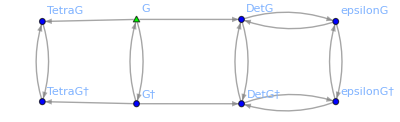

```mathematica
VertDiff[InvG]
VertDiff[InvG†]
VariationalVector[InvG]
VariationalVector[InvG†]
VariationalRelationsOf[G,HideTrivialRelations->True]
```

As usual, the PrintAs have been modified to put the † symbol next to the tensor:

```mathematica
$UseInverseMetric=True;
TensorWithIndices@dlInvG//ContractMetric
TensorWithIndices@VariationalVectorInvG//ContractMetric
TensorWithIndices@dlInvG†//ContractMetric
TensorWithIndices@VariationalVectorInvG†//ContractMetric
```

ⅆ(G^-1) | α | β
  |

(δ/(δ G^-1)) |   |  
α | β

ⅆ((G†)^-1) | α† | β†
  |

(δ/(δ(G†)^-1)) |   |  
α† | β†

```mathematica
$UseInverseMetric=False;
TensorWithIndices@dlInvG//ContractMetric
TensorWithIndices@VariationalVectorInvG//ContractMetric
TensorWithIndices@dlInvG†//ContractMetric
TensorWithIndices@VariationalVectorInvG†//ContractMetric
```

-(ⅆG) | α | β
  |

-(δ/δG) |   |  
α | β

-(ⅆG†) | α† | β†
  |

-(δ/(δG†)) |   |  
α† | β†

### A.Section.Subsection. VertDiff and VariationalVector of complex tensors

xCPS, generates the VertDiff and VariationalVector of both tensors:

```mathematica
VertDiff/@tensors
TensorWithIndices/@%

VariationalVector/@tensors
TensorWithIndices/@%
```

{dlT,dlT†}

{(ⅆT) | a | α
  |  ,(ⅆT†) | a | α†
  |  }

{VariationalVectorT,VariationalVectorT†}

{(δ/δT) |   |  
a | α,(δ/(δT†)) |   |  
a | α†}

Remark: We use the cleaner notation (ⅆT†) and (δ/(δT†))instead of (ⅆT)† and (δ/δT)†. Of course, their meaning are the same since Dagger commutes with VertDiff and VariationalVector.

```mathematica
VertDiffExpressions={VertDiff@Dagger@T,Dagger@VertDiff@T}
VariationalVectorExpressions={VariationalVector@Dagger@T,Dagger@VariationalVector@T}

TensorWithIndices/@VertDiffExpressions
TensorWithIndices/@VariationalVectorExpressions
```

{dlT†,dlT†}

{VariationalVectorT†,VariationalVectorT†}

{(ⅆT†) | a | α†
  |  ,(ⅆT†) | a | α†
  |  }

{(δ/(δT†)) |   |  
a | α†,(δ/(δT†)) |   |  
a | α†}

### A.Section.Subsection. Variational Relations of complex tensors

Since Dagger commutes with VertDiff, every tensors is variationally related with its complex conjugate:

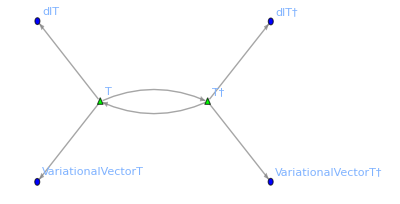

```mathematica
VariationalRelationsOf[{T,T†},HideTrivialRelations->False]
```

Remark: If a variational relation is created for a pair of tensors, the same one is created for its complex conjugated:

```mathematica
DefTensor[T2[a,α],M,Dagger->Complex]
```

** DefTensor: Defining tensor T2[a,α].

** DefTensor: Defining tensor T2†[a,α†].

** DefTensor: Defining tensor dlT2[a,α].

** DefTensor: Defining tensor dlT2†[a,α†].

** DefTensor: Defining tensor VariationalVectorT2[-a,-α].

** DefTensor: Defining tensor VariationalVectorT2†[-a,-α†].

** AddVariationalRelation: Variational relations created for conjugated tensors

** AddVariationalRelation: Variational relation created T→T2.

** AddVariationalRelation: Variational relation created T†→T2†.

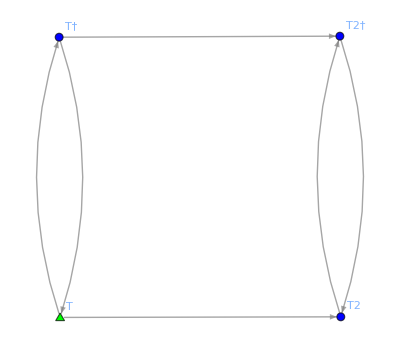

```mathematica
AddVariationalRelation[T->T2]
VariationalRelationsOf[T]
```

This is what happens, for instance, when a complex CovD is defined:

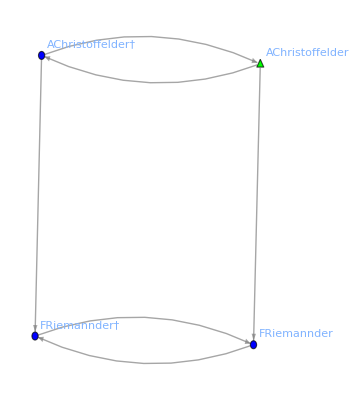

```mathematica
$DefInfoQ=False;
DefConstantSymbol[dimeninner]
DefVBundle[inner,M,dimeninner,{J,L,P,Q},Dagger->Complex]
DefCovD[der[-a],inner,{";","∇"},Torsion->True]
$DefInfoQ=True;
VariationalRelationsOf[AChristoffelder,HideTrivialRelations->True]
```

### A.Section.Subsection. GenerateExpandVertDiffRule of complex tensors

Remark: If a ExpandVertDiff rule is created for a tensors, its Dagger rule is also created.

```mathematica
GenerateExpandVertDiffRule[{dlT2[a,α],2dlT[a,α]}]

ExpandVertDiff[][dlT2[a,α]]
ExpandVertDiff[][dlT2†[a,α†]]
```

** GenerateExpandVertDiffRule: Expansion formula generated for dlT2.

** GenerateExpandVertDiffRule: Expansion formula generated for dlT2†.

2 (ⅆT) | a | α
  |

2 (ⅆT†) | a | α†
  |

### A.Section.Subsection. Imaginary scalar functions

We can also defined Imaginary scalar functions:

```mathematica
DefScalarFunction[ImFunction,Dagger->Imaginary]
```

** DefScalarFunction: Defining scalar function ImFunction.

```mathematica
HoldForm[Dagger@ImFunction]==Dagger@ImFunction
HoldForm[Dagger@ImFunction[]]==Dagger@ImFunction[]
```

Dagger[ImFunction]==MultiplyHead[-1,ImFunction]

Dagger[ImFunction[]]==-ImFunction[]

The arguments are also conjugated:

```mathematica
HoldForm[Dagger@ImFunction[ImTensor,T]]==Dagger@ImFunction[ImTensor,T]
HoldForm[Dagger@ImFunction[ImTensor[a],T[a]]]==Dagger@ImFunction[ImTensor[a],T[a]]
```

Dagger[ImFunction[ImTensor,T]]==-ImFunction[MultiplyHead[-1,ImTensor],T†]

Dagger[ImFunction[𝔗 | a
 ,T | a
 ]]==-ImFunction[-𝔗 | a
 ,T† | a
 ]

As before, we can consider an Imaginary scalar function as a real scalar function multiplied by ⅈ:

```mathematica
DefScalarFunction[ImFunction2,Dagger->Imaginary,PrintAs->"ⅈf_ℝ"]
```

** DefScalarFunction: Defining scalar function ImFunction2.

```mathematica
HoldForm[Dagger@ImFunction2]==Dagger@ImFunction2
HoldForm[Dagger@ImFunction2[]]==Dagger@ImFunction2[]
HoldForm[Dagger@ImFunction2[ImTensor[a],T[a]]]==Dagger@ImFunction2[ImTensor[a],T[a]]
```

Dagger[ⅈf_ℝ]==MultiplyHead[-1,ⅈf_ℝ]

Dagger[ⅈf_ℝ[]]==-ⅈf_ℝ[]

Dagger[ⅈf_ℝ[𝔗 | a
 ,T | a
 ]]==-ⅈf_ℝ[-𝔗 | a
 ,T† | a
 ]

### A.Section.Subsection. Complex scalar functions

We can also defined Complex scalar functions. In this case, two scalar functions are defined: the scalar function and its complex conjugated:

```mathematica
DefScalarFunction[ComplexFunction,Dagger->Complex,PrintAs->"f_ℂ"]
```

** DefScalarFunction: Defining scalar function ComplexFunction.

** DefScalarFunction: Defining scalar function ComplexFunction†.

```mathematica
HoldForm[Dagger@ComplexFunction]==Dagger@ComplexFunction
HoldForm[Dagger@ComplexFunction†]==Dagger@ComplexFunction†
```

Dagger[f_ℂ]==f_ℂ†

Dagger[f_ℂ†]==f_ℂ

For Complex scalar functions depending on tensors, its conjugated depends on the conjugated tensors:

```mathematica
DefScalarFunction[ImFunction3,{T,xi,ImVector},Dagger->Imaginary,PrintAs->"ⅈF_ℝ"]
DefScalarFunction[ComplexFunction2,{T,xi,ImVector},Dagger->Complex,PrintAs->"F_ℂ"]
```

** DefScalarFunction: Defining scalar function ImFunction3. It depends on ImVector, T and xi

** DefScalarFunction: Defining scalar function ComplexFunction2. It depends on ImVector, T and xi

** DefScalarFunction: Defining scalar function ComplexFunction2†. It depends on ImVector, T† and xi

```mathematica
DependenciesOfScalar[ImFunction3]
DependenciesOfScalar[ComplexFunction2]
DependenciesOfScalar[ComplexFunction2†]
```

{ImVector,T,xi}

{ImVector,T,xi}

{ImVector,T†,xi}

```mathematica
HoldForm[Dagger@ImFunction3[T,xi]]==Dagger@ImFunction3[T,xi]
HoldForm[Dagger@ImFunction3[ImVector,T,xi]]==Dagger@ImFunction3[ImVector,T,xi]
HoldForm[Dagger@ComplexFunction2[T,xi]]==Dagger[ComplexFunction2[T,xi]]
HoldForm[Dagger@ComplexFunction2[ImVector,T,xi]]==Dagger[ComplexFunction2[ImVector,T,xi]]
```

Dagger[ⅈF_ℝ[T,xi]]==-ⅈF_ℝ[T†,xi]

Dagger[ⅈF_ℝ[ImVector,T,xi]]==-ⅈF_ℝ[MultiplyHead[-1,ImVector],T†,xi]

Dagger[F_ℂ[T,xi]]==F_ℂ†[T†,xi]

Dagger[F_ℂ[ImVector,T,xi]]==F_ℂ†[MultiplyHead[-1,ImVector],T†,xi]

Remark: Recall that the head MultiplyHead disappears once some indices are attached.

```mathematica
MultiplyHead[-1,ImVector][a]
```

-ⅈT_ℝ | a

### A.Section.Subsection. PartialPartial of complex tensors

#### A.Section.Subsection.Subsubsection. Notation of complex PartialPartial tensors

When defining PartialPartial tensors involving complex objects, we run into a notational problem. For instance, the tensor:

 PartialFunctionPartialVector†

can mean

1.) Dagger[PartialPartial[Function][Vector]]
2.) PartialPartial[Function][Dagger@Vector].

If Function is Real, both expression are the same. But if Function is Imaginary or Complex, they mean different things. To be consistent with the notation used for PartialPartial on xCPS, we will assume the second option: that the † symbol is attached to the immediate object (and not the whole PartialPartial tensor, which would be the xAct convention).

Remark: The xAct function MakeDaggerSymbol is modified by xCPS to handle this case accordingly.

```mathematica
DefScalarFunction[ImFunction4,{T,T†,xi,ImVector},Dagger->Imaginary,PrintAs->"ⅈ𝔉_ℝ"]
DefScalarFunction[ComplexFunction3,{T,T†,xi,ImVector},Dagger->Complex,PrintAs->"𝔉_ℂ"]
```

** DefScalarFunction: Defining scalar function ImFunction4. It depends on ImVector, T, T† and xi

** DefScalarFunction: Defining scalar function ComplexFunction3. It depends on ImVector, T, T† and xi

** DefScalarFunction: Defining scalar function ComplexFunction3†. It depends on ImVector, T, T† and xi

```mathematica
DefPartialPartial[ComplexFunction3,{T†,xi}]
```

** DefTensor: Defining tensor Partial2ComplexFunction3PartialT†Partialxi[-a,-α†,-b].

** DefTensor: Defining tensor Partial2ComplexFunction3†PartialTPartialxi[-a,-α,-b].

```mathematica
TensorWithIndices@Partial2ComplexFunction3PartialT†Partialxi
```

((∂^2 𝔉_ℂ)/(∂T†∂xi)) |   |   |  
a | α† | b

The Dagger of this tensor returns its conjugated, which is equal to conjugate all the elements appearing in the expression:

```mathematica
Dagger@Partial2ComplexFunction3PartialT†Partialxi
TensorWithIndices@Dagger@Partial2ComplexFunction3PartialT†Partialxi
```

Partial2ComplexFunction3†PartialTPartialxi

((∂^2 𝔉_ℂ†)/(∂T∂xi)) |   |   |  
a | α | b

Remark: The tensors in PartialPartial are ordered with Sort. For instance, in the following example the order in both cases is {T,T†}:

```mathematica
DefPartialPartial[ComplexFunction3,{T†,T}]
```

** DefTensor: Defining tensor Partial2ComplexFunction3PartialTPartialT†[-a,-α,-b,-α†].

** DefTensor: Defining tensor Partial2ComplexFunction3†PartialTPartialT†[-a,-α†,-b,-α].

```mathematica
TensorWithIndices@Partial2ComplexFunction3PartialTPartialT†
Dagger@Partial2ComplexFunction3PartialTPartialT†
TensorWithIndices@Dagger@Partial2ComplexFunction3PartialTPartialT†
TensorsOfPartialPartial/@{Partial2ComplexFunction3PartialTPartialT†,Partial2ComplexFunction3†PartialTPartialT†}
```

((∂^2 𝔉_ℂ)/(∂T∂T†)) |   |   |   |  
a | α | b | α†

Partial2ComplexFunction3†PartialTPartialT†

((∂^2 𝔉_ℂ†)/(∂T∂T†)) |   |   |   |  
a | α† | b | α

{{T,T†},{T,T†}}

#### A.Section.Subsection.Subsubsection. Information of PartialPartial complex tensors

The usual functions presented on Subsection Chapter.Section.Subsection work as expected for imaginary and complex PartialPartial tensors:

```mathematica
PartialPartialQ@Partial2ComplexFunction3PartialTPartialT†
PartialPartialQ@Partial2ComplexFunction3†PartialTPartialT†

FunctionOfPartialPartial@Partial2ComplexFunction3PartialTPartialT†
FunctionOfPartialPartial@Partial2ComplexFunction3†PartialTPartialT†

TensorsOfPartialPartial@Partial2ComplexFunction3PartialTPartialT†
TensorsOfPartialPartial@Partial2ComplexFunction3†PartialTPartialT†

OrderOfPartialPartial@Partial2ComplexFunction3PartialTPartialT†
OrderOfPartialPartial@Partial2ComplexFunction3†PartialTPartialT†
```

True

True

𝔉_ℂ

𝔉_ℂ†

{T,T†}

{T,T†}

2

2

```mathematica
PartialPartialsOfFunction@ComplexFunction3
PartialPartialsOfFunction@ComplexFunction3†
PartialPartialsOfTensor@T
PartialPartialsOfTensor@T†
```

{Partial2ComplexFunction3PartialTPartialT†,Partial2ComplexFunction3PartialT†Partialxi}

{Partial2ComplexFunction3†PartialTPartialT†,Partial2ComplexFunction3†PartialTPartialxi}

{Partial2ComplexFunction3PartialTPartialT†,Partial2ComplexFunction3†PartialTPartialT†,Partial2ComplexFunction3†PartialTPartialxi}

{Partial2ComplexFunction3PartialTPartialT†,Partial2ComplexFunction3PartialT†Partialxi,Partial2ComplexFunction3†PartialTPartialT†}

```mathematica
PartialPartial[ComplexFunction3][T,T†]
PartialPartial[ComplexFunction3†][T†,T] (* Automatically ordered *)
```

Partial2ComplexFunction3PartialTPartialT†

Partial2ComplexFunction3†PartialTPartialT†

#### A.Section.Subsection.Subsubsection. Sign of PartialPartial complex tensors with imaginary objects involved

When Imaginay objects are involved, things are a bit trickier since for each one of them, a minus sign appears when conjugating. Thus, the overall sign depends on the parity (counting tensors + the function):

```mathematica
DefPartialPartial[ImFunction4,T]
DefPartialPartial[ImFunction4,{T,ImVector}]
DefPartialPartial[ComplexFunction3,{T,ImVector}]
```

** DefTensor: Defining tensor PartialImFunction4PartialT[-a,-α].

** DefTensor: Defining tensor PartialImFunction4PartialT†[-a,-α†].

** DefTensor: Defining tensor Partial2ImFunction4PartialImVectorPartialT[-a,-b,-α].

** DefTensor: Defining tensor Partial2ImFunction4PartialImVectorPartialT†[-a,-b,-α†].

** DefTensor: Defining tensor Partial2ComplexFunction3PartialImVectorPartialT[-a,-b,-α].

** DefTensor: Defining tensor Partial2ComplexFunction3†PartialImVectorPartialT†[-a,-b,-α†].

```mathematica
Dagger@PartialImFunction4PartialT
Dagger@TensorWithIndices@PartialImFunction4PartialT
Dagger@Partial2ImFunction4PartialImVectorPartialT
Dagger@TensorWithIndices@Partial2ImFunction4PartialImVectorPartialT
```

MultiplyHead[-1,PartialImFunction4PartialT†]

-((∂ⅈ𝔉_ℝ)/(∂T†)) |   |  
a | α†

Partial2ImFunction4PartialImVectorPartialT†

((∂^2 ⅈ𝔉_ℝ)/(∂ⅈT_ℝ∂T†)) |   |   |  
a | b | α†

#### A.Section.Subsection.Subsubsection. PartialPartial complex tensors with metrics involved

```mathematica
$DefInfoQ=False;
DefMetric[-1,g[-a,-b],LCDer,{";","∇"}] 
$DefInfoQ=True;
```

Recall from Subsection Chapter.Section.Subsection, that when metrics are involved, two PartialPartial tensors are defined (one with the metric and another with the inverse). Likewise, when complex tensors are involved, two PartialPartial tensors are defined (one with the tensors and another with their conjugates). Thus, when both metrics and complex tensors are involved, four PartialPartial tensors are defined:

```mathematica
DefPartialPartial[ImFunction4,{T,ImVector,g}]
DefPartialPartial[ComplexFunction3,{T,ImVector,g}]
```

** DefTensor: Defining tensor Partial3ImFunction4PartialgPartialImVectorPartialT[a,b,-c,-d,-α].

** DefTensor: Defining tensor Partial3ImFunction4PartialgPartialImVectorPartialT†[a,b,-c,-d,-α†].

** DefTensor: Defining tensor Partial3ImFunction4PartialInvgPartialImVectorPartialT[-a,-b,-c,-d,-α].

** DefTensor: Defining tensor Partial3ImFunction4PartialInvgPartialImVectorPartialT†[-a,-b,-c,-d,-α†].

** DefTensor: Defining tensor Partial3ComplexFunction3PartialgPartialImVectorPartialT[a,b,-c,-d,-α].

** DefTensor: Defining tensor Partial3ComplexFunction3†PartialgPartialImVectorPartialT†[a,b,-c,-d,-α†].

** DefTensor: Defining tensor Partial3ComplexFunction3PartialInvgPartialImVectorPartialT[-a,-b,-c,-d,-α].

** DefTensor: Defining tensor Partial3ComplexFunction3†PartialInvgPartialImVectorPartialT†[-a,-b,-c,-d,-α†].

```mathematica
{TensorWithIndices@Partial3ImFunction4PartialgPartialImVectorPartialT,TensorWithIndices@Partial3ImFunction4PartialgPartialImVectorPartialT†}
{TensorWithIndices@Partial3ImFunction4PartialInvgPartialImVectorPartialT,TensorWithIndices@Partial3ImFunction4PartialInvgPartialImVectorPartialT†}
{TensorWithIndices@Partial3ComplexFunction3PartialgPartialImVectorPartialT,TensorWithIndices@Partial3ComplexFunction3†PartialgPartialImVectorPartialT†}
{TensorWithIndices@Partial3ComplexFunction3PartialInvgPartialImVectorPartialT,TensorWithIndices@Partial3ComplexFunction3†PartialInvgPartialImVectorPartialT†}
```

{((∂^3 ⅈ𝔉_ℝ)/(∂g∂ⅈT_ℝ∂T)) | a | b |   |   |  
  |   | c | d | α,((∂^3 ⅈ𝔉_ℝ)/(∂g∂ⅈT_ℝ∂T†)) | a | b |   |   |  
  |   | c | d | α†}

{-((∂^3 ⅈ𝔉_ℝ)/(∂g∂ⅈT_ℝ∂T)) |   |   |   |   |  
a | b | c | d | α,-((∂^3 ⅈ𝔉_ℝ)/(∂g∂ⅈT_ℝ∂T†)) |   |   |   |   |  
a | b | c | d | α†}

{((∂^3 𝔉_ℂ)/(∂g∂ⅈT_ℝ∂T)) | a | b |   |   |  
  |   | c | d | α,((∂^3 𝔉_ℂ†)/(∂g∂ⅈT_ℝ∂T†)) | a | b |   |   |  
  |   | c | d | α†}

{-((∂^3 𝔉_ℂ)/(∂g∂ⅈT_ℝ∂T)) |   |   |   |   |  
a | b | c | d | α,-((∂^3 𝔉_ℂ†)/(∂g∂ⅈT_ℝ∂T†)) |   |   |   |   |  
a | b | c | d | α†}

```mathematica
$UseInverseMetric=True;
{TensorWithIndices@Partial3ImFunction4PartialgPartialImVectorPartialT,TensorWithIndices@Partial3ImFunction4PartialgPartialImVectorPartialT†}
{TensorWithIndices@Partial3ImFunction4PartialInvgPartialImVectorPartialT,TensorWithIndices@Partial3ImFunction4PartialInvgPartialImVectorPartialT†}
{TensorWithIndices@Partial3ComplexFunction3PartialgPartialImVectorPartialT,TensorWithIndices@Partial3ComplexFunction3†PartialgPartialImVectorPartialT†}
{TensorWithIndices@Partial3ComplexFunction3PartialInvgPartialImVectorPartialT,TensorWithIndices@Partial3ComplexFunction3†PartialInvgPartialImVectorPartialT†}
$UseInverseMetric=False;
```

{-((∂^3 ⅈ𝔉_ℝ)/(∂g^-1∂ⅈT_ℝ∂T)) | a | b |   |   |  
  |   | c | d | α,-((∂^3 ⅈ𝔉_ℝ)/(∂g^-1∂ⅈT_ℝ∂T†)) | a | b |   |   |  
  |   | c | d | α†}

{((∂^3 ⅈ𝔉_ℝ)/(∂g^-1∂ⅈT_ℝ∂T)) |   |   |   |   |  
a | b | c | d | α,((∂^3 ⅈ𝔉_ℝ)/(∂g^-1∂ⅈT_ℝ∂T†)) |   |   |   |   |  
a | b | c | d | α†}

{-((∂^3 𝔉_ℂ)/(∂g^-1∂ⅈT_ℝ∂T)) | a | b |   |   |  
  |   | c | d | α,-((∂^3 𝔉_ℂ†)/(∂g^-1∂ⅈT_ℝ∂T†)) | a | b |   |   |  
  |   | c | d | α†}

{((∂^3 𝔉_ℂ)/(∂g^-1∂ⅈT_ℝ∂T)) |   |   |   |   |  
a | b | c | d | α,((∂^3 𝔉_ℂ†)/(∂g^-1∂ⅈT_ℝ∂T†)) |   |   |   |   |  
a | b | c | d | α†}

```mathematica
Dagger@Partial3ImFunction4PartialgPartialImVectorPartialT
Dagger@Partial3ComplexFunction3PartialgPartialImVectorPartialT
TensorWithIndices@Dagger@Partial3ImFunction4PartialgPartialImVectorPartialT
TensorWithIndices@Dagger@Partial3ComplexFunction3PartialgPartialImVectorPartialT
```

Partial3ImFunction4PartialgPartialImVectorPartialT†

MultiplyHead[-1,Partial3ComplexFunction3†PartialgPartialImVectorPartialT†]

((∂^3 ⅈ𝔉_ℝ)/(∂g∂ⅈT_ℝ∂T†)) | a | b |   |   |  
  |   | c | d | α†

-((∂^3 𝔉_ℂ†)/(∂g∂ⅈT_ℝ∂T†)) | a | b |   |   |  
  |   | c | d | α†

### A.Section.Subsection. Hermitian and Antihermitian tensors

#### A.Section.Subsection.Subsubsection. Definition

Hermitian tensors are a particular case of Complex tensors that establishes that

Tensor†=Tensor

Similarly, Antihermitian tensors satisfy

Tensor†=-Tensor

Remark: Since the indices are also conjugated, the previous equations only make sense if there are the same amount of indices in the vector bundle as in its complex conjugate.

```mathematica
DefTensor[w[a,α,β†],M,Dagger->Hermitian]
DefTensor[u[a,α,β†],M,Dagger->Antihermitian]
```

** DefTensor: Defining tensor w[a,α,β†].

** DefTensor: Defining tensor w†[a,α†,β].

** DefTensor: Defining tensor dlw[a,α,β†].

** DefTensor: Defining tensor dlw†[a,α†,β].

** DefTensor: Defining tensor VariationalVectorw[-a,-α,-β†].

** DefTensor: Defining tensor VariationalVectorw†[-a,-α†,-β].

** AddVariationalRelation: Variational relations created for conjugated tensors

** DefTensor: Defining tensor u[a,α,β†].

** DefTensor: Defining tensor u†[a,α†,β].

** DefTensor: Defining tensor dlu[a,α,β†].

** DefTensor: Defining tensor dlu†[a,α†,β].

** DefTensor: Defining tensor VariationalVectoru[-a,-α,-β†].

** DefTensor: Defining tensor VariationalVectoru†[-a,-α†,-β].

** AddVariationalRelation: Variational relations created for conjugated tensors

```mathematica
HoldForm[w†[a,α†,β]]==w†[a,α†,β]
HoldForm[u†[a,α†,β]]==u†[a,α†,β]
```

w† | a | α† | β
  |   |  ==w | a | β | α†
  |   |

u† | a | α† | β
  |   |  ==-u | a | β | α†
  |   |

#### A.Section.Subsection.Subsubsection. VertDiff and VariationalVector

These properties are inherited by their VertDiff and VariationalVector tensors:

```mathematica
HoldForm[dlw†[a,α†,β]]==dlw†[a,α†,β]
HoldForm[VariationalVectorw†[-a,-α†,-β]]==VariationalVectorw†[-a,-α†,-β]
HoldForm[dlu†[a,α†,β]]==dlu†[a,α†,β]
HoldForm[VariationalVectoru†[-a,-α†,-β]]==VariationalVectoru†[-a,-α†,-β]
```

(ⅆw†) | a | α† | β
  |   |  ==(ⅆw) | a | β | α†
  |   |

(δ/(δw†)) |   |   |  
a | α† | β==(δ/δw) |   |   |  
a | β | α†

(ⅆu†) | a | α† | β
  |   |  ==-(ⅆu) | a | β | α†
  |   |

(δ/(δu†)) |   |   |  
a | α† | β==-(δ/δu) |   |   |  
a | β | α†

#### A.Section.Subsection.Subsubsection. PartialPartial

Remark: A PartialPartial tensor with a real function and all its complex tensors Hermitian and Antihermitian is Hermitian if k is even and Antihermitian if k is odd (where k is the number of Antihermitian tensors appearing in the PartialPartial tensor).

Remark: A PartialPartial tensor with a real function and a mix of Hermitian, Antihermitian and general Complex tensors is not in general Hermitian or Antihermitian.

```mathematica
DefPartialPartial[function,w]
DefPartialPartial[function,u]
DefPartialPartial[ImFunction2,u]
DefPartialPartial[ComplexFunction,u]
DefPartialPartial[function,{u,w}]
DefPartialPartial[ImFunction2,{u,w}]
DefPartialPartial[ComplexFunction,{u,w}]
```

** DefTensor: Defining tensor PartialfunctionPartialw[-a,-α,-α†].

** DefTensor: Defining tensor PartialfunctionPartialw†[-a,-α†,-α].

** DefTensor: Defining tensor PartialfunctionPartialu[-a,-α,-α†].

** DefTensor: Defining tensor PartialfunctionPartialu†[-a,-α†,-α].

** DefTensor: Defining tensor PartialImFunction2Partialu[-a,-α,-α†].

** DefTensor: Defining tensor PartialImFunction2Partialu†[-a,-α†,-α].

** DefTensor: Defining tensor PartialComplexFunctionPartialu[-a,-α,-α†].

** DefTensor: Defining tensor PartialComplexFunction†Partialu†[-a,-α†,-α].

** DefTensor: Defining tensor Partial2functionPartialuPartialw[-a,-α,-α†,-b,-β,-β†].

** DefTensor: Defining tensor Partial2functionPartialu†Partialw†[-a,-α†,-α,-b,-β†,-β].

** DefTensor: Defining tensor Partial2ImFunction2PartialuPartialw[-a,-α,-α†,-b,-β,-β†].

** DefTensor: Defining tensor Partial2ImFunction2Partialu†Partialw†[-a,-α†,-α,-b,-β†,-β].

** DefTensor: Defining tensor Partial2ComplexFunctionPartialuPartialw[-a,-α,-α†,-b,-β,-β†].

** DefTensor: Defining tensor Partial2ComplexFunction†Partialu†Partialw†[-a,-α†,-α,-b,-β†,-β].

```mathematica
(* Hermitian *)
HermitianQ[PartialfunctionPartialw]
HoldForm[Dagger[PartialfunctionPartialw[-a,-α,-β†]]]==Dagger[PartialfunctionPartialw[-a,-α,-β†]]
HoldForm[PartialfunctionPartialw†[-a,-α†,-α]]==PartialfunctionPartialw†[-a,-α†,-α]
```

True

Dagger[((∂f)/(∂w)) |   |   |  
a | α | β†]==((∂f)/(∂w)) |   |   |  
a | β | α†

((∂f)/(∂w†)) |   |   |  
a | α† | α==((∂f)/(∂w)) |   |   |  
a | α | α†

```mathematica
(* Antihermitian *)
AntihermitianQ[PartialfunctionPartialu]
HoldForm[Dagger[PartialfunctionPartialu[-a,-α,-β†]]]==Dagger[PartialfunctionPartialu[-a,-α,-β†]]
HoldForm[PartialfunctionPartialu†[-a,-α†,-α]]==PartialfunctionPartialu†[-a,-α†,-α]
```

True

Dagger[((∂f)/(∂u)) |   |   |  
a | α | β†]==-((∂f)/(∂u)) |   |   |  
a | β | α†

((∂f)/(∂u†)) |   |   |  
a | α† | α==-((∂f)/(∂u)) |   |   |  
a | α | α†

Remark: Imaginary tensors/function do not change the Hermitian/Antihermitian character, they only introduce a sign (-1)^(#{Imaginary objects}) since we follow the convention (because it fits better with the xAct formalism) that is it Hermitian/Antihermitian with respect to the complex indices.

```mathematica
HermitianQ[PartialImFunction2Partialu]
AntihermitianQ[PartialImFunction2Partialu]
HoldForm[Dagger[PartialImFunction2Partialu[-a,-α,-β†]]]==Dagger[PartialImFunction2Partialu[-a,-α,-β†]]
HoldForm[PartialImFunction2Partialu†[-a,-α,-β†]]==PartialImFunction2Partialu†[-a,-α,-β†]
```

False

True

Dagger[((∂ⅈf_ℝ)/(∂u)) |   |   |  
a | α | β†]==((∂ⅈf_ℝ)/(∂u)) |   |   |  
a | β | α†

((∂ⅈf_ℝ)/(∂u†)) |   |   |  
a | α | β†==-((∂ⅈf_ℝ)/(∂u)) |   |   |  
a | β† | α

Remark: If some generic complex tensors/function are involved (non-imaginary, non-Hermitian and non-Antihermitian), the resulting PartialPartial tensor is Complex.

```mathematica
TensorWithIndices@Partial2ComplexFunctionPartialuPartialw
```

((∂^2 f_ℂ)/(∂u∂w)) |   |   |   |   |   |  
a | α | α† | b | β | β†

```mathematica
HoldForm[Dagger[PartialComplexFunctionPartialu[-a,-α,-β†]]]==Dagger[PartialComplexFunctionPartialu[-a,-α,-β†]]
HoldForm[Dagger[Partial2ComplexFunctionPartialuPartialw[-a,-α,-α†,-β,-β†]]]==Dagger[Partial2ComplexFunctionPartialuPartialw[-a,-α,-α†,-β,-β†]]
```

Dagger[((∂f_ℂ)/(∂u)) |   |   |  
a | α | β†]==((∂f_ℂ†)/(∂u†)) |   |   |  
a | α† | β

Dagger[((∂^2 f_ℂ)/(∂u∂w)) |   |   |   |   |  
a | α | α† | β | β†]==((∂^2 f_ℂ†)/(∂u†∂w†)) |   |   |   |   |  
a | α† | α | β† | β

### A.Section.Subsection. Reset session

We reset everything: $ConstantSymbols, $Parameters, $ScalarFunctions, $Metrics, $CovDs, $VertForms, $Manifolds, and $VBundles.

```mathematica
ResetSession[]
```

** SetSigns: All constant signs set to 1.

## A.Section. Imploded tensors

### A.Section.Subsection. Initial definitions

In this Subsection, we briefly present imploded tensors and their interaction with xCPS. We refer the reader to the xAct documentation for further details.

```mathematica
$DefInfoQ=False;

DefConstantSymbol[dimen]
DefParameter[τ]
DefParameter[λ]
DefManifold[M,dimen,{a,b,c,d,e,f,h,i,j,k,l}]
DefMetric[-1,g[-a,-b],LCDer,{";","∇"}] 
DefTensor[phi[],M,PrintAs->"ϕ"]
DefTensor[xi[a],M,PrintAs->"ξ"]
DefTensor[tensor[a,-b],{M,τ}]
DefTensor[v[a],{M,τ}]
DefTensor[w[a],{M,τ,λ}]

$DefInfoQ=True;
```

### A.Section.Subsection. Imploded tensors

Imploded tensors are new tensors defined out of tensors and LieD, CovD, ParamD, and OverDot.

```mathematica
expr={LieD[xi[b]][g[-a,-b]],LCDer[-a]@xi[b],OverDot[g[-a,-b]],ParamD[τ][tensor[a,-b]],ParamD[τ,λ][w[a]]}
imploded=Implode/@expr
```

{ℒ_ξ g |   |  
a | b,∇_a ξ | b
 ,OverDot[g |   |  
a | b],∂_τ tensor | a |  
  | b,∂_τ ∂_λ w | a
 }

{ℒξg |   |  
a | b,∇ξ | b |  
  | a,OverDotg |   |  
a | b,ParamDτtensor | a |  
  | b,ParamDτλw | a
 }

The names are just the concatenation of the objects appearing in the expression:

```mathematica
names=Head/@imploded
TensorWithIndices/@names
```

{LieDxig,LCDerxi,OverDotg,ParamDτtensor,ParamDτλw}

{ℒξg |   |  
a | b,∇ξ | a |  
  | b,OverDotg |   |  
a | b,ParamDτtensor | a |  
  | b,ParamDτλw | a
 }

### A.Section.Subsection. Exploded tensors

The inverse of Implode is Explode:

```mathematica
LieDxig[-a,-b]==(LieDxig[-a,-b]//Explode)
LCDerxi[a,-b]==(LCDerxi[a,-b]//Explode)
OverDotg[-a,-b]==(OverDotg[-a,-b]//Explode)
ParamDτtensor[a,-b]==(ParamDτtensor[a,-b]//Explode)
ParamDτλw[a]==(ParamDτλw[a]//Explode)
```

ℒξg |   |  
a | b==ℒ_ξ g |   |  
a | b

∇ξ | a |  
  | b==∇_b ξ | a

OverDotg |   |  
a | b==OverDot[g |   |  
a | b]

ParamDτtensor | a |  
  | b==∂_τ tensor | a |  
  | b

ParamDτλw | a
 ==∂_τ ∂_λ w | a

### A.Section.Subsection. VertDiff and VariationalVector of imploded tensors

xCPS generates the corresponding VariationalVector and VertDiff of every imploded tensor:

```mathematica
VariationalVector/@names
VertDiff/@names
```

{VariationalVectorLieDxig,VariationalVectorLCDerxi,VariationalVectorOverDotg,VariationalVectorParamDτtensor,VariationalVectorParamDτλw}

{dlLieDxig,dlLCDerxi,dlOverDotg,dlParamDτtensor,dlParamDτλw}

```mathematica
TensorWithIndices/@VariationalVector/@names
TensorWithIndices/@VertDiff/@names
```

{(δ/δℒξg) | a | b
  |  ,(δ/(δ∇ξ)) |   | b
a |  ,(δ/δOverDotg) | a | b
  |  ,(δ/δParamDτtensor) |   | b
a |  ,(δ/δParamDτλw) |  
a}

{(ⅆℒξg) |   |  
a | b,(ⅆ∇ξ) | a |  
  | b,(ⅆOverDotg) |   |  
a | b,(ⅆParamDτtensor) | a |  
  | b,(ⅆParamDτλw) | a
 }

The explosion of the former does not make sense, since the imploded part is in the denominator, but for the latter it does:

```mathematica
Explode/@TensorWithIndices/@VariationalVector/@names
Explode/@TensorWithIndices/@VertDiff/@names (* It explodes the Master Tensor *)
```

{(δ/δℒξg) | a | b
  |  ,(δ/(δ∇ξ)) |   | b
a |  ,(δ/δOverDotg) | a | b
  |  ,(δ/δParamDτtensor) |   | b
a |  ,(δ/δParamDτλw) |  
a}

{ⅆ[ℒ_ξ g |   |  
a | b],ⅆ[∇_b ξ | a
 ],ⅆ[OverDot[g |   |  
a | b]],ⅆ[∂_τ tensor | a |  
  | b],ⅆ[∂_τ ∂_λ w | a
 ]}

### A.Section.Subsection. ExpandVertDiff of imploded tensors

ExpandVertDiff explodes the expressions by default:

```mathematica
TensorWithIndices/@VertDiff/@names
TensorWithIndices/@VertDiff/@names//ExpandVertDiff[]
```

{(ⅆℒξg) |   |  
a | b,(ⅆ∇ξ) | a |  
  | b,(ⅆOverDotg) |   |  
a | b,(ⅆParamDτtensor) | a |  
  | b,(ⅆParamDτλw) | a
 }

{ℒ_(ⅆξ)g |   |  
a | b+ℒ_ξ(ⅆg) |   |  
a | b,∇_b (ⅆξ) | a
 +1/2 g | a | d
  |   ξ | c
  (∇_b (ⅆg) |   |  
d | c+∇_c (ⅆg) |   |  
b | d-∇_d (ⅆg) |   |  
b | c),OverDot[(ⅆg) |   |  
a | b],∂_τ (ⅆtensor) | a |  
  | b,∂_τ ∂_λ (ⅆw) | a
 }

but this can be prevented:

```mathematica
ExpandVertDiff[Explode->False]/@TensorWithIndices/@VertDiff/@names
```

{(ⅆℒξg) |   |  
a | b,(ⅆ∇ξ) | a |  
  | b,(ⅆOverDotg) |   |  
a | b,(ⅆParamDτtensor) | a |  
  | b,(ⅆParamDτλw) | a
 }

### A.Section.Subsection. Variational Relations of imploded tensors

#### Chapter.Section.Subsection.Subsubsection. CovD imploded tensors

Remark: Although $DefInfoQ is True, no message has been displayed about the definition of the imploded tensors. This is controlled by $ImplodeInfoQ which is False by default.

```mathematica
$DefInfoQ
$ImplodeInfoQ
```

True

False

Let us set it to true to see additional messages to understand what is happening behind the curtains of xAct and xCPS:

```mathematica
$ImplodeInfoQ=True;

Implode[LCDer[-a]@phi[]];
```

** DefTensor: Defining tensor LCDerphi[-a].

** DefTensor: Defining tensor dlLCDerphi[-a].

** DefTensor: Defining tensor VariationalVectorLCDerphi[a].

** AddVariationalRelation: Variational relation created phi→LCDerphi.

We see that, as usual, three tensors are created. We also see that a variational relation has been created that correspond with the formula:

(ⅆ∇ϕ) |  
a==∇_a (ⅆϕ)

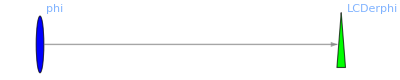

```mathematica
expr=TensorWithIndices@VertDiff@LCDerphi;
expr==(expr//ExpandVertDiff[])
VariationalRelationsOf@LCDerphi
```

This is a very particular case since it is the covariant derivative of a scalar, which is equivalent to its horizontal exterior derivative. Thus, it does not depend on the CovD (this type of objects are sometimes called concomitants). For more general tensors, it does depend on the CovD, so additional variational relations appear:

```mathematica
Implode[LCDer[-a]@LCDer[-b]@phi[]];
Implode[LCDer[-a]@v[b]];
```

** DefTensor: Defining tensor LCDerLCDerphi[-a,-b].

** DefTensor: Defining tensor dlLCDerLCDerphi[-a,-b].

** DefTensor: Defining tensor VariationalVectorLCDerLCDerphi[a,b].

** AddVariationalRelation: Variational relation created ChristoffelLCDer→LCDerLCDerphi.

** AddVariationalRelation: Variational relation created phi→LCDerLCDerphi.

** DefTensor: Defining tensor LCDerv[a,-b].

** DefTensor: Defining tensor dlLCDerv[a,-b].

** DefTensor: Defining tensor VariationalVectorLCDerv[-a,b].

** AddVariationalRelation: Variational relation created ChristoffelLCDer→LCDerv.

** AddVariationalRelation: Variational relation created v→LCDerv.

(ⅆ∇∇ϕ) |   |  
a | b==∇_b ∇_a (ⅆϕ)-(ⅆΓ[∇]) | c |   |  
  | b | a ∇_c ϕ

(ⅆ∇v) | a |  
  | b==(ⅆΓ[∇]) | a |   |  
  | b | c v | c
 +∇_b (ⅆv) | a

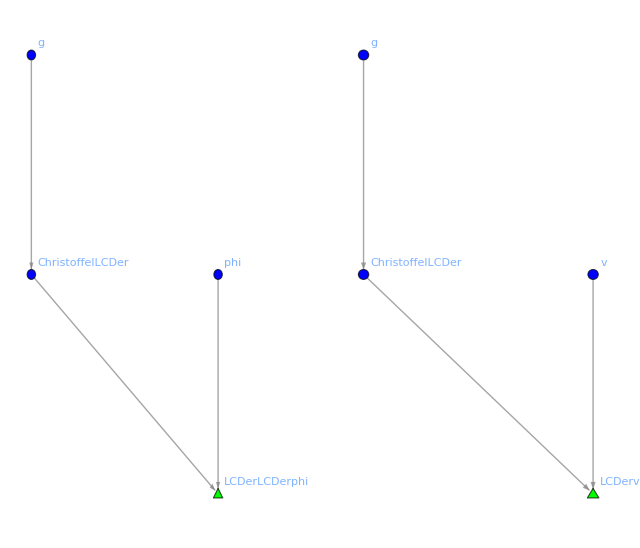

```mathematica
expr=TensorWithIndices@VertDiff@LCDerLCDerphi;
expr==(expr//ExpandVertDiff[HoldExpandVertDiff->ChristoffelLCDer])

expr=TensorWithIndices@VertDiff@LCDerv;
expr==(expr//ExpandVertDiff[HoldExpandVertDiff->ChristoffelLCDer])

GraphicsRow[{VariationalRelationsOf@LCDerLCDerphi,VariationalRelationsOf@LCDerv}]
```

We can have more complicated imploded tensors:

```mathematica
$DefInfoQ=False;
DefConstantSymbol[dimeninner]
DefVBundle[inner,M,dimeninner,{J,L,P,Q}]

(* We define a covariant derivative on M acting also on the inner bundle *) 
DefCovD[derinner[-a],inner,{";",""},Torsion->True]
DefCovD[der2[-a],{";","D"},Torsion->True]

(* We define a 1-tensor with two internal indices *) 
DefTensor[tensor1[b,-J,-L],M,PrintAs->"T"]
$DefInfoQ=True;
```

```mathematica
Implode[derinner[-a]@tensor1[b,-J,-L]];
Implode[LCDer[-a]@der2[-b]@xi[c]];
Implode[LCDer[-a]@der2xi[c,-b]]; (* Since the CovD are different, xAct does not create the imploded tensor on one go *)
```

** DefTensor: Defining tensor derinnertensor1[a,-J,-L,-b].

** DefTensor: Defining tensor dlderinnertensor1[a,-J,-L,-b].

** DefTensor: Defining tensor VariationalVectorderinnertensor1[-a,J,L,b].

** AddVariationalRelation: Variational relation created Christoffelderinner→derinnertensor1.

** AddVariationalRelation: Variational relation created AChristoffelderinner→derinnertensor1.

** AddVariationalRelation: Variational relation created tensor1→derinnertensor1.

** DefTensor: Defining tensor der2xi[a,-b].

** DefTensor: Defining tensor dlder2xi[a,-b].

** DefTensor: Defining tensor VariationalVectorder2xi[-a,b].

** AddVariationalRelation: Variational relation created Christoffelder2→der2xi.

** AddVariationalRelation: Variational relation created xi→der2xi.

** DefTensor: Defining tensor LCDerder2xi[a,-b,-c].

** DefTensor: Defining tensor dlLCDerder2xi[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorLCDerder2xi[-a,b,c].

** AddVariationalRelation: Variational relation created ChristoffelLCDer→LCDerder2xi.

** AddVariationalRelation: Variational relation created Christoffelder2→LCDerder2xi.

** AddVariationalRelation: Variational relation created xi→LCDerder2xi.

In these cases, the variational relations created correspond with the formulas:

(ⅆT) | a |   |   |  
  | J | L | b==-(ⅆA[]) | P |   |  
  | b | L T | a |   |  
  | J | P-(ⅆA[]) | P |   |  
  | b | J T | a |   |  
  | P | L+(ⅆΓ[]) | a |   |  
  | b | c T | c |   |  
  | J | L+_b(ⅆT) | a |   |  
  | J | L

(ⅆ∇Dξ) | a |   |  
  | b | c==(ⅆΓ[∇]) | a |   |  
  | c | d (D_b ξ | d
 )-(ⅆΓ[∇]) | d |   |  
  | c | b (D_d ξ | a
 )+ξ | d
  ∇_c (ⅆΓ[D]) | a |   |  
  | b | d+(ⅆΓ[D]) | a |   |  
  | b | d ∇_c ξ | d
 +∇_c D_b(ⅆξ) | a

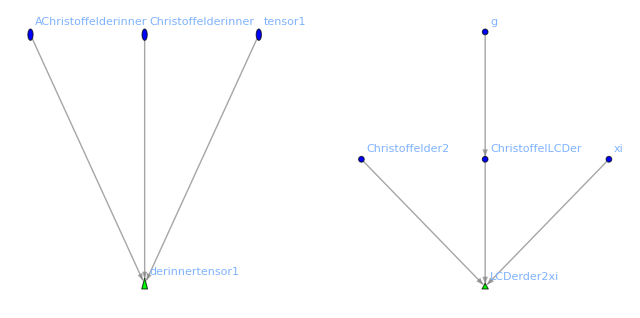

```mathematica
expr=TensorWithIndices@VertDiff@derinnertensor1;
expr==(expr//ExpandVertDiff[])

expr=TensorWithIndices@VertDiff@LCDerder2xi;
expr==(expr//ExpandVertDiff[HoldExpandVertDiff->ChristoffelLCDer])

GraphicsRow[{VariationalRelationsOf@derinnertensor1,VariationalRelationsOf@LCDerder2xi}]
```

#### Chapter.Section.Subsection.Subsubsection. LieD imploded tensors

When LieD is involved, the vector is also related to the imploded tensor.

```mathematica
Implode[LieD[v[-a]]@xi[c]];
Implode[LieD[v[-a]]@LCDer[-b]@LCDer[-c]@phi[]];
```

** DefTensor: Defining tensor LieDvxi[a].

** DefTensor: Defining tensor dlLieDvxi[a].

** DefTensor: Defining tensor VariationalVectorLieDvxi[-a].

** AddVariationalRelation: Variational relation created v→LieDvxi.

** AddVariationalRelation: Variational relation created xi→LieDvxi.

** DefTensor: Defining tensor LieDvLCDerLCDerphi[-a,-b].

** DefTensor: Defining tensor dlLieDvLCDerLCDerphi[-a,-b].

** DefTensor: Defining tensor VariationalVectorLieDvLCDerLCDerphi[a,b].

** AddVariationalRelation: Variational relation created v→LieDvLCDerLCDerphi.

** AddVariationalRelation: Variational relation created ChristoffelLCDer→LieDvLCDerLCDerphi.

** AddVariationalRelation: Variational relation created phi→LieDvLCDerLCDerphi.

In these cases, the variational relations created correspond with the formulas:

(ⅆℒvξ) | a
 ==ℒ_(ⅆv)ξ | a
 +ℒ_v(ⅆξ) | a

(ⅆℒv∇∇ϕ) |   |  
a | b==ℒ_(ⅆv)∇_b ∇_a ϕ-∇_c ϕ (ℒ_v(ⅆΓ[∇]) | c |   |  
  | b | a)+ℒ_v∇_b ∇_a (ⅆϕ)-(ⅆΓ[∇]) | c |   |  
  | b | a (ℒ_v∇_c ϕ)

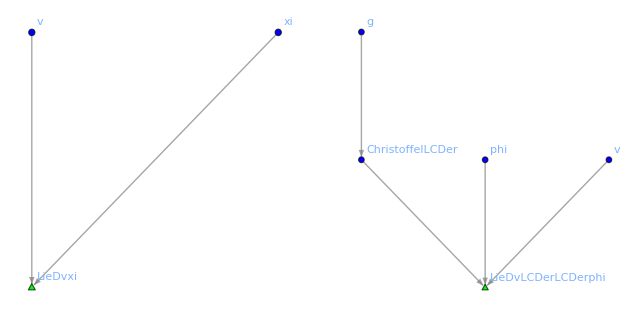

```mathematica
expr=TensorWithIndices@VertDiff@LieDvxi;
expr==(expr//ExpandVertDiff[])

expr=TensorWithIndices@VertDiff@LieDvLCDerLCDerphi;
expr==(expr//ExpandVertDiff[HoldExpandVertDiff->ChristoffelLCDer])

GraphicsRow[{VariationalRelationsOf@LieDvxi,VariationalRelationsOf@LieDvLCDerLCDerphi}]
```

#### Chapter.Section.Subsection.Subsubsection. ParamD imploded tensors

For ParamD imploded tensors, only the trivial variational relation between the imploded tensor and its maser is created.

```mathematica
expr=TensorWithIndices@VertDiff@ParamDτtensor;
expr==(expr//ExpandVertDiff[])

expr=TensorWithIndices@VertDiff@ParamDτλw;
expr==(expr//ExpandVertDiff[])

GraphicsRow[{VariationalRelationsOf@ParamDτtensor,VariationalRelationsOf@ParamDτλw}]
```

(ⅆParamDτtensor) | a |  
  | b==∂_τ (ⅆtensor) | a |  
  | b

(ⅆParamDτλw) | a
 ==∂_τ ∂_λ (ⅆw) | a

-Graphics-

#### Chapter.Section.Subsection.Subsubsection. OverDot imploded tensors

For OverDot imploded tensors, only the trivial variational relation between the imploded tensor and its maser is created.

(ⅆOverDotg) |   |  
a | b==OverDot[(ⅆg) |   |  
a | b]

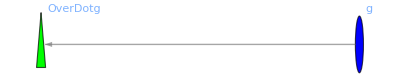

```mathematica
expr=TensorWithIndices@VertDiff@OverDotg;
expr==(expr//ExpandVertDiff[])

VariationalRelationsOf@OverDotg
```

### A.Section.Subsection. Reset session

We reset everything: $ConstantSymbols, $Parameters, $ScalarFunctions, $Metrics, $CovDs, $Tensors, $Manifolds, and $VBundles.

```mathematica
ResetSession[]
```

** SetSigns: All constant signs set to 1.

## A.Section. Checking the ExpandVertDiff formulas

### A.Section.Subsection. Checking the ExpandVertDiff formulas for a non-metric CovD

In this Subsection, we check the formulas used by ExpandVertDiff when dealing with a non-metric CovD.

#### A.Section.Subsection.Subsubsection. Initial definitions

```mathematica
$DefInfoQ=False;

DefConstantSymbol[dimen] (* Generic dimension *)
SetSigns[0] (* Generic signs *)

DefManifold[M,dimen,{a,b,c,d,e,f,h,i,j,k,l}]
DefCovD[der[-a],{";","D"},Torsion->True]

$DefInfoQ=True;
```

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆRiemann

```mathematica
expr=Riemannder[-a,-b,-c,d]
expr1=VertDiff[expr];
expr2=ChangeCovD[VertDiff[expr//ChangeCurvature],PD,der]//Simplification;

sol=Solve[expr1==expr2,{{(ⅆR[D]), {{, , , d}, {a, b, c, }}}}][[1]] (* The antisymmetrization of ChristofelDer gives the Torsion *)
(VertDiff[Riemannder[-a,-b,-c,d]]//ExpandVertDiff[])-sol[[1,2]]//Simplification//TorsionToChristoffel
```

R[D] |   |   |   | d
a | b | c |

{(ⅆR[D]) |   |   |   | d
a | b | c |  →-s_R (Γ[D] | e |   |  
  | a | b (ⅆΓ[D]) | d |   |  
  | e | c-Γ[D] | e |   |  
  | b | a (ⅆΓ[D]) | d |   |  
  | e | c+D_a(ⅆΓ[D]) | d |   |  
  | b | c-D_b(ⅆΓ[D]) | d |   |  
  | a | c)}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆTorsion

```mathematica
expr=Torsionder[a,-b,-c]
expr1=VertDiff[expr];
expr2=VertDiff[expr//TorsionToChristoffel]

sol=Solve[expr1==expr2,{{(ⅆT[D]), {{a, , }, {, b, c}}}}][[1]]

(VertDiff[Torsionder[a,-b,-c]]//ExpandVertDiff[])-sol[[1,2]]
```

T[D] | a |   |  
  | b | c

s_T ((ⅆΓ[D]) | a |   |  
  | b | c-(ⅆΓ[D]) | a |   |  
  | c | b)

{(ⅆT[D]) | a |   |  
  | b | c→s_T ((ⅆΓ[D]) | a |   |  
  | b | c-(ⅆΓ[D]) | a |   |  
  | c | b)}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆRicci

```mathematica
expr=Riccider[-a,-b]
expr1=VertDiff[expr];
expr2=ChangeCovD[VertDiff[expr//ChangeCurvature],PD,der]//ExpandVertDiff[]//Simplification;

sol=Solve[expr1==expr2,{{(ⅆR[D]), {{, }, {a, b}}}}][[1]]//Simplification

(VertDiff[Riccider[-a,-b]]//ExpandVertDiff[])-sol[[1,2]]//TorsionToChristoffel//Simplification
```

R[D] |   |  
a | b

{(ⅆR[D]) |   |  
a | b→-s_r s_R (Γ[D] | c |   |  
  | a | d (ⅆΓ[D]) | d |   |  
  | c | b-Γ[D] | c |   |  
  | d | a (ⅆΓ[D]) | d |   |  
  | c | b+D_a(ⅆΓ[D]) | c |   |  
  | c | b-D_c(ⅆΓ[D]) | c |   |  
  | a | b)}

0

#### A.Section.Subsection.Subsubsection. Reset session

We reset everything: $ConstantSymbols, $Parameters, $ScalarFunctions, $Metrics, $CovDs, $Tensors, $Manifolds, and $VBundles.

```mathematica
ResetSession[]
```

** SetSigns: All constant signs set to 1.

### A.Section.Subsection. Checking the ExpandVertDiff formulas for a non-metric CovD acting on a vector bundle

In this Subsection, we check the formulas used by ExpandVertDiff when dealing with a non-metric CovD acting on a generic vector bundle.

#### A.Section.Subsection.Subsubsection. Initial definitions

```mathematica
$DefInfoQ=False;

DefConstantSymbol[dimen] (* Generic dimension *)
DefConstantSymbol[dimeninner] (* Generic dimension *)
SetSigns[0](* Generic signs *)

DefManifold[M,dimen,{a,b,c,d,e,f,h,i,j,k,l}]
DefVBundle[inner,M,dimeninner,{J,L,P,Q}]
DefCovD[der2[-a],inner,{";",""},Torsion->True]

$DefInfoQ=True;
```

#### A.Section.Subsection.Subsubsection. ⅆFRiemann

```mathematica
expr=FRiemannder2[-a,-b,-P,Q]
expr1=VertDiff[expr]
expr2=ChangeCovD[VertDiff[expr//ChangeCurvature],PD,der2]//Simplification

sol=Solve[expr1==expr2,{{(ⅆF[]), {{, , , Q}, {a, b, P, }}}}][[1]] (* The antisymmetrization of ChristofelDer gives the Torsion *)
(VertDiff[FRiemannder2[-a,-b,-P,Q]]//ExpandVertDiff[])-sol[[1,2]]//Simplification//TorsionToChristoffel
```

F[] |   |   |   | Q
a | b | P |

(ⅆF[]) |   |   |   | Q
a | b | P |

s_R (-Γ[] | c |   |  
  | a | b (ⅆA[]) | Q |   |  
  | c | P+Γ[] | c |   |  
  | b | a (ⅆA[]) | Q |   |  
  | c | P-_a(ⅆA[]) | Q |   |  
  | b | P+_b(ⅆA[]) | Q |   |  
  | a | P)

{(ⅆF[]) |   |   |   | Q
a | b | P |  →-s_R (Γ[] | c |   |  
  | a | b (ⅆA[]) | Q |   |  
  | c | P-Γ[] | c |   |  
  | b | a (ⅆA[]) | Q |   |  
  | c | P+_a(ⅆA[]) | Q |   |  
  | b | P-_b(ⅆA[]) | Q |   |  
  | a | P)}

0

#### A.Section.Subsection.Subsubsection. Reset session

We reset everything: $ConstantSymbols, $Parameters, $ScalarFunctions, $Metrics, $CovDs, $VertForms, $Manifolds, and $VBundles.

```mathematica
ResetSession[]
```

** SetSigns: All constant signs set to 1.

### A.Section.Subsection. Checking the ExpandVertDiff formulas for a non-frozen metric

In this Subsection, we check the formulas used by ExpandVertDiff when dealing with a non-frozen metric.

#### A.Section.Subsection.Subsubsection. Initial definitions

```mathematica
$DefInfoQ=False;

DefConstantSymbol[dimen] (* Generic dimension *)
SetSigns[0](* Generic signs *)

DefManifold[M,dimen,{a,b,c,d,e,f,h,i,j,k,l}]
DefMetric[-1,g[-a,-b],LCDer,{";","∇"}] 

$DefInfoQ=True;
```

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆChristoffel

```mathematica
expr=ChristoffelLCDer[a,-b,-c]
expr1=VertDiff[expr];
expr2=ChangeCovD[VertDiff[expr//ChristoffelToGradMetric],PD,LCDer]//ExpandVertDiff[]//ContractMetric//Simplification;

sol=Solve[expr1==expr2,{{(ⅆΓ[∇]), {{a, , }, {, b, c}}}}][[1]]

(VertDiff[ChristoffelLCDer[a,-b,-c]]//ExpandVertDiff[])-sol[[1,2]]//ContractMetric//Simplification
```

Γ[∇] | a |   |  
  | b | c

{(ⅆΓ[∇]) | a |   |  
  | b | c→1/2 (-∇^a (ⅆg) |   |  
b | c+∇_b (ⅆg) | a |  
  | c+∇_c (ⅆg) | a |  
  | b)}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆRiemann

```mathematica
expr=RiemannLCDer[-a,-b,-c,-d]
expr1=VertDiff[expr];
expr2=ChangeCovD[VertDiff[expr//ChangeCurvature],PD,LCDer]//ExpandVertDiff[]//ContractMetric//Simplification;

sol=Solve[expr1==expr2,{{(ⅆR[∇]), {{, , , }, {a, b, c, d}}}}][[1]]

(VertDiff[RiemannLCDer[-a,-b,-c,-d]]//ExpandVertDiff[])-sol[[1,2]]//ChangeCovD//RiemannToChristoffel//Simplification//Quiet;
ChangeCovD[%,PD,LCDer]//Simplification
```

R[∇] |   |   |   |  
a | b | c | d

{(ⅆR[∇]) |   |   |   |  
a | b | c | d→1/2 s_R (2 Γ[∇] | e |   |  
  | b | c Γ[∇] | f |   |  
  | a | e (ⅆg) |   |  
d | f-2 Γ[∇] | e |   |  
  | a | c Γ[∇] | f |   |  
  | b | e (ⅆg) |   |  
d | f-2 (ⅆg) |   | e
d |   ∇_a Γ[∇] |   |   |  
e | b | c-∇_a ∇_b (ⅆg) |   |  
c | d-∇_a ∇_c (ⅆg) |   |  
b | d+∇_a ∇_d (ⅆg) |   |  
b | c+2 (ⅆg) |   | e
d |   ∇_b Γ[∇] |   |   |  
e | a | c+∇_b ∇_a (ⅆg) |   |  
c | d+∇_b ∇_c (ⅆg) |   |  
a | d-∇_b ∇_d (ⅆg) |   |  
a | c)}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆWeyl

```mathematica
expr=WeylLCDer[-a,-b,-c,-d];
expr1=VertDiff[expr];
expr2=VertDiff[expr//WeylToRiemann]//ExpandVertDiff[]//ContractMetric//Simplification;

sol=Solve[expr1==expr2,dlWeylLCDer[-a,-b,-c,-d]][[1]]

(VertDiff[WeylLCDer[-a,-b,-c,-d]]//ExpandVertDiff[])-sol[[1,2]]//ContractMetric//Simplification
```

{(ⅆW[∇]) |   |   |   |  
a | b | c | d→1/(2 (-2+dimen) (-1+dimen))(-2 (-1+dimen) s_r (ⅆg) |   |  
b | d R[∇] |   |  
a | c+2 (-1+dimen) s_r (ⅆg) |   |  
b | c R[∇] |   |  
a | d+2 (-1+dimen) s_r (ⅆg) |   |  
a | d R[∇] |   |  
b | c-2 (-1+dimen) s_r (ⅆg) |   |  
a | c R[∇] |   |  
b | d+2 s_r (ⅆg) | e | f
  |   g |   |  
a | d g |   |  
b | c R[∇] |   |  
e | f-2 s_r (ⅆg) | e | f
  |   g |   |  
a | c g |   |  
b | d R[∇] |   |  
e | f+2 s_r (ⅆg) |   |  
b | d g |   |  
a | c R[∇]-2 s_r (ⅆg) |   |  
b | c g |   |  
a | d R[∇]-2 s_r (ⅆg) |   |  
a | d g |   |  
b | c R[∇]+2 s_r (ⅆg) |   |  
a | c g |   |  
b | d R[∇]+2 (-2+dimen) (-1+dimen) (ⅆg) |   | e
d |   R[∇] |   |   |   |  
a | b | c | e-(-2+dimen) (-1+dimen) s_R ∇_a ∇_b (ⅆg) |   |  
c | d-(-2+dimen) (-1+dimen) s_R ∇_a ∇_c (ⅆg) |   |  
b | d+(-2+dimen) (-1+dimen) s_R ∇_a ∇_d (ⅆg) |   |  
b | c+(-2+dimen) (-1+dimen) s_R ∇_b ∇_a (ⅆg) |   |  
c | d+(-2+dimen) (-1+dimen) s_R ∇_b ∇_c (ⅆg) |   |  
a | d-(-2+dimen) (-1+dimen) s_R ∇_b ∇_d (ⅆg) |   |  
a | c+(-1+dimen) s_R g |   |  
b | d ∇_c ∇_a (ⅆg) | e |  
  | e-(-1+dimen) s_R g |   |  
a | d ∇_c ∇_b (ⅆg) | e |  
  | e-(-1+dimen) s_R g |   |  
b | c ∇_d ∇_a (ⅆg) | e |  
  | e+(-1+dimen) s_R g |   |  
a | c ∇_d ∇_b (ⅆg) | e |  
  | e-(-1+dimen) s_R g |   |  
b | d ∇_e ∇_a (ⅆg) |   | e
c |  +(-1+dimen) s_R g |   |  
b | c ∇_e ∇_a (ⅆg) |   | e
d |  +(-1+dimen) s_R g |   |  
a | d ∇_e ∇_b (ⅆg) |   | e
c |  -(-1+dimen) s_R g |   |  
a | c ∇_e ∇_b (ⅆg) |   | e
d |  -(-1+dimen) s_R g |   |  
b | d ∇_e ∇_c (ⅆg) |   | e
a |  +(-1+dimen) s_R g |   |  
a | d ∇_e ∇_c (ⅆg) |   | e
b |  +(-1+dimen) s_R g |   |  
b | c ∇_e ∇_d (ⅆg) |   | e
a |  -(-1+dimen) s_R g |   |  
a | c ∇_e ∇_d (ⅆg) |   | e
b |  +(-1+dimen) s_R g |   |  
b | d ∇_e ∇^e (ⅆg) |   |  
a | c-(-1+dimen) s_R g |   |  
b | c ∇_e ∇^e (ⅆg) |   |  
a | d-(-1+dimen) s_R g |   |  
a | d ∇_e ∇^e (ⅆg) |   |  
b | c+(-1+dimen) s_R g |   |  
a | c ∇_e ∇^e (ⅆg) |   |  
b | d-2 s_R g |   |  
a | d g |   |  
b | c ∇_f ∇_e (ⅆg) | e | f
  |  +2 s_R g |   |  
a | c g |   |  
b | d ∇_f ∇_e (ⅆg) | e | f
  |  +2 s_R g |   |  
a | d g |   |  
b | c ∇_f ∇^f (ⅆg) | e |  
  | e-2 s_R g |   |  
a | c g |   |  
b | d ∇_f ∇^f (ⅆg) | e |  
  | e)}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆRicci

```mathematica
expr=RicciLCDer[-a,-c]
expr1=VertDiff[expr];
expr2=ChangeCovD[VertDiff[expr//ChangeCurvature],PD,LCDer]//ExpandVertDiff[]//ContractMetric//Simplification;
 
sol=Solve[expr1==expr2,{{(ⅆR[∇]), {{, }, {a, c}}}}][[1]]

(VertDiff[RicciLCDer[-a,-c]]//ExpandVertDiff[])-sol[[1,2]]//SortCovDs//ContractMetric//Simplification
```

R[∇] |   |  
a | c

{(ⅆR[∇]) |   |  
a | c→-1/2 s_r s_R (-∇_b ∇_a (ⅆg) |   | b
c |  +∇_b ∇^b (ⅆg) |   |  
a | c-∇_b ∇_c (ⅆg) |   | b
a |  +∇_c ∇_a (ⅆg) | b |  
  | b)}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆTFRicci

```mathematica
expr=TFRicciLCDer[-a,-b];
expr1=VertDiff[expr];
expr2=VertDiff[expr//TFRicciToRicci]//ExpandVertDiff[]//ContractMetric//Simplification;

sol=Solve[expr1==expr2,dlTFRicciLCDer[-a,-b]][[1]]

(VertDiff[TFRicciLCDer[-a,-b]]//ExpandVertDiff[])-sol[[1,2]]//ContractMetric//Simplification
```

{(ⅆS[∇]) |   |  
a | b→(2 (ⅆg) | c | d
  |   g |   |  
a | b R[∇] |   |  
c | d-2 (ⅆg) |   |  
a | b R[∇]-dimen s_r s_R ∇_b ∇_a (ⅆg) | c |  
  | c+dimen s_r s_R ∇_c ∇_a (ⅆg) |   | c
b |  +dimen s_r s_R ∇_c ∇_b (ⅆg) |   | c
a |  -dimen s_r s_R ∇_c ∇^c (ⅆg) |   |  
a | b-2 s_r s_R g |   |  
a | b ∇_d ∇_c (ⅆg) | c | d
  |  +2 s_r s_R g |   |  
a | b ∇_d ∇^d (ⅆg) | c |  
  | c)/(2 dimen)}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆEinstein

```mathematica
expr=EinsteinLCDer[-a,-b];
expr1=VertDiff[expr];
expr2=VertDiff[expr//EinsteinToRicci]//ExpandVertDiff[]//ContractMetric//Simplification;

sol=Solve[expr1==expr2,dlEinsteinLCDer[-a,-b]][[1]]

(VertDiff[EinsteinLCDer[-a,-b]]//ExpandVertDiff[])-sol[[1,2]]//ContractMetric//Simplification
```

{(ⅆG[∇]) |   |  
a | b→1/2 ((ⅆg) | c | d
  |   g |   |  
a | b R[∇] |   |  
c | d-(ⅆg) |   |  
a | b R[∇]-s_r s_R ∇_b ∇_a (ⅆg) | c |  
  | c+s_r s_R ∇_c ∇_a (ⅆg) |   | c
b |  +s_r s_R ∇_c ∇_b (ⅆg) |   | c
a |  -s_r s_R ∇_c ∇^c (ⅆg) |   |  
a | b-s_r s_R g |   |  
a | b ∇_d ∇_c (ⅆg) | c | d
  |  +s_r s_R g |   |  
a | b ∇_d ∇^d (ⅆg) | c |  
  | c)}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆRicciScalar

```mathematica
expr=RicciScalarLCDer[]
expr1=VertDiff[expr];
expr2=ChangeCovD[VertDiff[expr//ChangeCurvature],PD,LCDer]//ExpandVertDiff[]//ContractMetric//Simplification; 
 
sol=Solve[(expr1-expr2//NoScalar//ContractMetric//Simplification)==0,(ⅆR[∇])][[1]]

(VertDiff[RicciScalarLCDer[]]//ExpandVertDiff[]//Simplification)-sol[[1,2]];
%//ContractMetric//Simplification //RiemannToChristoffel//ChangeCovD//Simplification
```

R[∇]

{(ⅆR[∇])→-s_r s_R Γ[∇] | a | b | c
  |   |   Γ[∇] |   |   | d
b | a |   (ⅆg) |   |  
c | d+s_r s_R Γ[∇] | a |   | b
  | a |   Γ[∇] |   | c | d
b |   |   (ⅆg) |   |  
c | d+s_r s_R (ⅆg) | a | b
  |   ∇_b Γ[∇] | c |   |  
  | a | c+s_r s_R ∇_b ∇_a (ⅆg) | a | b
  |  -s_r s_R ∇_b ∇^b (ⅆg) | a |  
  | a-s_r s_R (ⅆg) | a | b
  |   ∇_c Γ[∇] | c |   |  
  | a | b}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆKretschmann

```mathematica
expr=KretschmannLCDer[];
expr1=VertDiff[expr];
expr2=VertDiff[expr//KretschmannToRiemann]//ExpandVertDiff[]//ContractMetric//Simplification;

sol=Solve[expr1==expr2,dlKretschmannLCDer[]][[1]]

(VertDiff[KretschmannLCDer[]]//ExpandVertDiff[])-sol[[1,2]]//ContractMetric//Simplification
```

{(ⅆK[∇])→-2 (((ⅆg) | a | b
  |   g | c | d
  |   g | e | f
  |   g | h | i
  |   R[∇] |   |   |   |  
a | c | e | h R[∇] |   |   |   |  
b | d | f | i)+2 s_R (g | a | b
  |   g | c | d
  |   g | e | f
  |   g | h | i
  |   R[∇] |   |   |   |  
b | f | d | i ∇_h ∇_e (ⅆg) |   |  
a | c))}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆepsilon

To check the formula for the volume form, we need to fix the dimension (otherwise xAct defines epsilon[metric] with only two indices). Thus, we define a new 4-dimensional manifold with a metric on it.

```mathematica
$DefInfoQ=False;
DefManifold[Maux,4,{α,β,γ,δ,ϕ,η,σ,ρ,θ,ω,τ,ψ}]
DefMetric[-1,gaux[-α,-β],LCDeraux,{"D",";"},PrintAs->"ℊ"]
$DefInfoQ=True;
```

```mathematica
epsilongaux[α,β,γ,δ]epsilongaux[-α,-β,-γ,-δ]==HoldForm[epsilongaux[α,β,γ,δ]epsilongaux[-α,-β,-γ,-δ]]
expr=0==VertDiff[HoldForm[epsilongaux[α,β,γ,δ]epsilongaux[-α,-β,-γ,-δ]]]==VertDiff[epsilongaux[α,β,γ,δ]]epsilongaux[-α,-β,-γ,-δ]+epsilongaux[α,β,γ,δ]VertDiff[epsilongaux[-α,-β,-γ,-δ]]==(VertDiff[epsilongaux[α,β,γ,δ]]epsilongaux[-α,-β,-γ,-δ]+epsilongaux[α,β,γ,δ]VertDiff[epsilongaux[-α,-β,-γ,-δ]]//ExpandVertDiff[HoldExpandVertDiff->epsilongaux]//ContractMetric//Simplification)
```

-24==ϵℊ | α | β | γ | δ
  |   |   |   ϵℊ |   |   |   |  
α | β | γ | δ

0==ⅆ[ϵℊ | α | β | γ | δ
  |   |   |   ϵℊ |   |   |   |  
α | β | γ | δ]==(ⅆϵℊ) |   |   |   |  
α | β | γ | δ ϵℊ | α | β | γ | δ
  |   |   |  +ϵℊ |   |   |   |  
α | β | γ | δ ⅆ[ϵℊ | α | β | γ | δ
  |   |   |  ]==24 (ⅆℊ) | α |  
  | α+2 (ⅆϵℊ) | α | β | γ | δ
  |   |   |   ϵℊ |   |   |   |  
α | β | γ | δ

```mathematica
expr[[1]]==expr[[4]]
%epsilongaux[ϕ,η,σ,ρ]gaux[-ϕ,-θ]gaux[-η,-ω]gaux[-σ,-τ]gaux[-ρ,-ψ]//Simplification//ContractMetric

sol=Solve[%,dlepsilongaux[-θ,-τ,-ψ,-ω]][[1]]//Simplification

(VertDiff[epsilongaux[-θ,-τ,-ψ,-ω]]//ExpandVertDiff[])-sol[[1,2]]//Simplification//ContractMetric
```

0==24 (ⅆℊ) | α |  
  | α+2 (ⅆϵℊ) | α | β | γ | δ
  |   |   |   ϵℊ |   |   |   |  
α | β | γ | δ

0==-48 (ⅆϵℊ) |   |   |   |  
θ | τ | ψ | ω+24 (ⅆℊ) | α |  
  | α ϵℊ |   |   |   |  
θ | τ | ψ | ω

{(ⅆϵℊ) |   |   |   |  
θ | τ | ψ | ω→1/2 (ⅆℊ) | α |  
  | α ϵℊ |   |   |   |  
θ | τ | ψ | ω}

0

#### A.Section.Subsection.Subsubsection. Reset session

We reset everything: $ConstantSymbols, $Parameters, $ScalarFunctions, $Metrics, $CovDs, $VertForms, $Manifolds, and $VBundles.

```mathematica
ResetSession[]
```

** SetSigns: All constant signs set to 1.

### A.Section.Subsection. Checking the ExpandVertDiff formulas for a frozen metric

In this Subsection, we check the formulas used by ExpandVertDiff when dealing with a frozen metric.

#### A.Section.Subsection.Subsubsection. Initial definitions

```mathematica
$DefInfoQ=False;

DefConstantSymbol[dimen] (* Generic dimension *)
SetSigns[0](* Generic signs *)

DefManifold[M,dimen,{a,b,c,d,e,f,h,i,j,k,l}]
DefMetric[-1,g[-a,-b],LCDer,{";","∇"}] ;
DefMetric[1,g2[-a,-b],LCDer2,{";","OverTilde[∇]"},PrintAs->"𝕘"]//Quiet

$DefInfoQ=True;
```

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆChristoffel

```mathematica
expr=ChristoffelLCDer2[a,-b,-c]
expr1=VertDiff[expr];
expr2=ChangeCovD[VertDiff[expr//ChristoffelToGradMetric],PD,LCDer2]//ExpandVertDiff[]//ContractMetric//Simplification;

sol=Solve[(expr1-expr2//Simplification)==0,{{(ⅆΓ[OverTilde[∇]]), {{a, , }, {, b, c}}}}][[1]]

(VertDiff[ChristoffelLCDer2[a,-b,-c]]//ExpandVertDiff[])-sol[[1,2]]//Simplification
```

Γ[OverTilde[∇]] | a |   |  
  | b | c

{(ⅆΓ[OverTilde[∇]]) | a |   |  
  | b | c→1/2 i𝕘 | a | d
  |   (OverTilde[∇]_b(ⅆ𝕘) |   |  
c | d+OverTilde[∇]_c(ⅆ𝕘) |   |  
b | d-OverTilde[∇]_d(ⅆ𝕘) |   |  
b | c)}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆRiemann

```mathematica
expr=RiemannLCDer2[-a,-b,-c,d]
expr1=VertDiff[expr];
expr2=ChangeCovD[VertDiff[expr//ChangeCurvature],PD,LCDer2]//ExpandVertDiff[]//ContractMetric//Simplification;
 
sol=Solve[(expr1-expr2//Simplification)==0,{{(ⅆR[OverTilde[∇]]), {{, , , d}, {a, b, c, }}}}][[1]]

(VertDiff[RiemannLCDer2[-a,-b,-c,d]]//ExpandVertDiff[])-sol[[1,2]]//Simplification
```

R[OverTilde[∇]] |   |   |   | d
a | b | c |

{(ⅆR[OverTilde[∇]]) |   |   |   | d
a | b | c |  →-1/2 s_R i𝕘 | d | e
  |   (OverTilde[∇]_a OverTilde[∇]_b(ⅆ𝕘) |   |  
c | e+OverTilde[∇]_a OverTilde[∇]_c(ⅆ𝕘) |   |  
b | e-OverTilde[∇]_a OverTilde[∇]_e(ⅆ𝕘) |   |  
b | c-OverTilde[∇]_b OverTilde[∇]_a(ⅆ𝕘) |   |  
c | e-OverTilde[∇]_b OverTilde[∇]_c(ⅆ𝕘) |   |  
a | e+OverTilde[∇]_b OverTilde[∇]_e(ⅆ𝕘) |   |  
a | c)}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆRiemannDown

```mathematica
expr=RiemannDownLCDer2[-a,-b,-c,-d]
expr1=VertDiff[expr];
expr2=ChangeCovD[VertDiff[expr//ChangeCurvature],PD,LCDer2]//ExpandVertDiff[]//ContractMetric//Simplification;

sol=Solve[(expr1-expr2//Simplification)==0,{{(ⅆℛ[OverTilde[∇]]), {{, , , }, {a, b, c, d}}}}][[1]]

(VertDiff[RiemannDownLCDer2[-a,-b,-c,-d]]//ExpandVertDiff[])-sol[[1,2]]//Simplification
```

ℛ[OverTilde[∇]] |   |   |   |  
a | b | c | d

{(ⅆℛ[OverTilde[∇]]) |   |   |   |  
a | b | c | d→1/2 (2 (ⅆ𝕘) |   | e
d |   R[OverTilde[∇]] |   |   |   |  
a | b | c | e-s_R (OverTilde[∇]_a OverTilde[∇]_b(ⅆ𝕘) |   |  
c | d)-s_R (OverTilde[∇]_a OverTilde[∇]_c(ⅆ𝕘) |   |  
b | d)+s_R (OverTilde[∇]_a OverTilde[∇]_d(ⅆ𝕘) |   |  
b | c)+s_R (OverTilde[∇]_b OverTilde[∇]_a(ⅆ𝕘) |   |  
c | d)+s_R (OverTilde[∇]_b OverTilde[∇]_c(ⅆ𝕘) |   |  
a | d)-s_R (OverTilde[∇]_b OverTilde[∇]_d(ⅆ𝕘) |   |  
a | c))}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆWeyl

```mathematica
expr=WeylLCDer2[-a,-b,-c,-d];
expr1=VertDiff[expr];
expr2=VertDiff[expr//WeylToRiemann]//ExpandVertDiff[]//ContractMetric//Simplification;

sol=Solve[expr1==expr2,dlWeylLCDer2[-a,-b,-c,-d]][[1]]

(VertDiff[WeylLCDer2[-a,-b,-c,-d]]//ExpandVertDiff[])-sol[[1,2]]//ContractMetric//Simplification
```

{(ⅆW[OverTilde[∇]]) |   |   |   |  
a | b | c | d→1/(2 (-2+dimen) (-1+dimen))(-2 (-1+dimen) s_r (ⅆ𝕘) |   |  
b | d R[OverTilde[∇]] |   |  
a | c+2 (-1+dimen) s_r (ⅆ𝕘) |   |  
b | c R[OverTilde[∇]] |   |  
a | d+2 (-1+dimen) s_r (ⅆ𝕘) |   |  
a | d R[OverTilde[∇]] |   |  
b | c-2 (-1+dimen) s_r (ⅆ𝕘) |   |  
a | c R[OverTilde[∇]] |   |  
b | d+2 s_r (ⅆ𝕘) | e | f
  |   𝕘 |   |  
a | d 𝕘 |   |  
b | c i𝕘 |   | h
e |   i𝕘 |   | i
f |   R[OverTilde[∇]] |   |  
h | i-2 s_r (ⅆ𝕘) | e | f
  |   𝕘 |   |  
a | c 𝕘 |   |  
b | d i𝕘 |   | h
e |   i𝕘 |   | i
f |   R[OverTilde[∇]] |   |  
h | i+2 s_r (ⅆ𝕘) |   |  
b | d 𝕘 |   |  
a | c R[OverTilde[∇]]-2 s_r (ⅆ𝕘) |   |  
b | c 𝕘 |   |  
a | d R[OverTilde[∇]]-2 s_r (ⅆ𝕘) |   |  
a | d 𝕘 |   |  
b | c R[OverTilde[∇]]+2 s_r (ⅆ𝕘) |   |  
a | c 𝕘 |   |  
b | d R[OverTilde[∇]]+2 (-2+dimen) (-1+dimen) (ⅆ𝕘) |   | e
d |   R[OverTilde[∇]] |   |   |   |  
a | b | c | e-(-2+dimen) (-1+dimen) s_R (OverTilde[∇]_a OverTilde[∇]_b(ⅆ𝕘) |   |  
c | d)-(-2+dimen) (-1+dimen) s_R (OverTilde[∇]_a OverTilde[∇]_c(ⅆ𝕘) |   |  
b | d)+(-1+dimen) s_R 𝕘 |   |  
b | d i𝕘 | e | f
  |   (OverTilde[∇]_a OverTilde[∇]_c(ⅆ𝕘) |   |  
e | f)+(-2+dimen) (-1+dimen) s_R (OverTilde[∇]_a OverTilde[∇]_d(ⅆ𝕘) |   |  
b | c)-(-1+dimen) s_R 𝕘 |   |  
b | c i𝕘 | e | f
  |   (OverTilde[∇]_a OverTilde[∇]_d(ⅆ𝕘) |   |  
e | f)+(-2+dimen) (-1+dimen) s_R (OverTilde[∇]_b OverTilde[∇]_a(ⅆ𝕘) |   |  
c | d)+(-2+dimen) (-1+dimen) s_R (OverTilde[∇]_b OverTilde[∇]_c(ⅆ𝕘) |   |  
a | d)-(-1+dimen) s_R 𝕘 |   |  
a | d i𝕘 | e | f
  |   (OverTilde[∇]_b OverTilde[∇]_c(ⅆ𝕘) |   |  
e | f)-(-2+dimen) (-1+dimen) s_R (OverTilde[∇]_b OverTilde[∇]_d(ⅆ𝕘) |   |  
a | c)+(-1+dimen) s_R 𝕘 |   |  
a | c i𝕘 | e | f
  |   (OverTilde[∇]_b OverTilde[∇]_d(ⅆ𝕘) |   |  
e | f)-(-1+dimen) s_R 𝕘 |   |  
b | d i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_a(ⅆ𝕘) |   |  
c | e)+(-1+dimen) s_R 𝕘 |   |  
b | c i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_a(ⅆ𝕘) |   |  
d | e)+(-1+dimen) s_R 𝕘 |   |  
a | d i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_b(ⅆ𝕘) |   |  
c | e)-(-1+dimen) s_R 𝕘 |   |  
a | c i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_b(ⅆ𝕘) |   |  
d | e)-(-1+dimen) s_R 𝕘 |   |  
b | d i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_c(ⅆ𝕘) |   |  
a | e)+(-1+dimen) s_R 𝕘 |   |  
a | d i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_c(ⅆ𝕘) |   |  
b | e)+(-1+dimen) s_R 𝕘 |   |  
b | c i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_d(ⅆ𝕘) |   |  
a | e)-(-1+dimen) s_R 𝕘 |   |  
a | c i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_d(ⅆ𝕘) |   |  
b | e)+(-1+dimen) s_R 𝕘 |   |  
b | d i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_e(ⅆ𝕘) |   |  
a | c)-(-1+dimen) s_R 𝕘 |   |  
b | c i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_e(ⅆ𝕘) |   |  
a | d)-(-1+dimen) s_R 𝕘 |   |  
a | d i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_e(ⅆ𝕘) |   |  
b | c)+(-1+dimen) s_R 𝕘 |   |  
a | c i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_e(ⅆ𝕘) |   |  
b | d)-2 s_R 𝕘 |   |  
a | d 𝕘 |   |  
b | c i𝕘 | e | f
  |   i𝕘 | h | i
  |   (OverTilde[∇]_i OverTilde[∇]_f(ⅆ𝕘) |   |  
e | h)+2 s_R 𝕘 |   |  
a | c 𝕘 |   |  
b | d i𝕘 | e | f
  |   i𝕘 | h | i
  |   (OverTilde[∇]_i OverTilde[∇]_f(ⅆ𝕘) |   |  
e | h)+2 s_R 𝕘 |   |  
a | d 𝕘 |   |  
b | c i𝕘 | e | f
  |   i𝕘 | h | i
  |   (OverTilde[∇]_i OverTilde[∇]_h(ⅆ𝕘) |   |  
e | f)-2 s_R 𝕘 |   |  
a | c 𝕘 |   |  
b | d i𝕘 | e | f
  |   i𝕘 | h | i
  |   (OverTilde[∇]_i OverTilde[∇]_h(ⅆ𝕘) |   |  
e | f))}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆRicci

```mathematica
expr=RicciLCDer2[-a,-c]
expr1=VertDiff[expr];
expr2=ChangeCovD[VertDiff[expr//ChangeCurvature],PD,LCDer2]//ExpandVertDiff[]//ContractMetric//Simplification//Quiet;

sol=Solve[(expr1-expr2//ContractMetric//Simplification)==0,{{(ⅆR[OverTilde[∇]]), {{, }, {a, c}}}}][[1]]

(VertDiff[RicciLCDer2[-a,-c]]//ExpandVertDiff[])-sol[[1,2]]//Simplification
```

R[OverTilde[∇]] |   |  
a | c

** DefTensor: Defining tensor ChristoffelLCDerLCDer2[a,-b,-c].

** DefTensor: Defining tensor dlChristoffelLCDerLCDer2[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorChristoffelLCDerLCDer2[-a,b,c].

** AddVariationalRelation: Variational relation created ChristoffelLCDer→ChristoffelLCDerLCDer2.

** AddVariationalRelation: Variational relation created ChristoffelLCDer2→ChristoffelLCDerLCDer2.

** GenerateExpandVertDiffRule: Expansion formula generated for dlChristoffelLCDerLCDer2.

{(ⅆR[OverTilde[∇]]) |   |  
a | c→-1/2 s_r s_R i𝕘 | b | d
  |   (OverTilde[∇]_a OverTilde[∇]_c(ⅆ𝕘) |   |  
b | d-OverTilde[∇]_d OverTilde[∇]_a(ⅆ𝕘) |   |  
c | b+OverTilde[∇]_d OverTilde[∇]_b(ⅆ𝕘) |   |  
a | c-OverTilde[∇]_d OverTilde[∇]_c(ⅆ𝕘) |   |  
a | b)}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆTFRicci

```mathematica
expr=TFRicciLCDer2[-a,-b];
expr1=VertDiff[expr];

(* TFRicciToRicci is not implemented for frozen metrics *)
expr2=VertDiff[expr/. TFRicciLCDer2[-a,-b]->RicciLCDer2[-a,-b]-(1/dimen) g2[-b,-a] RicciScalarLCDer2[]]//ExpandVertDiff[]//ContractMetric//Simplification;

sol=Solve[(expr1-expr2//Simplification)==0,dlTFRicciLCDer2[-a,-b]][[1]]

(VertDiff[TFRicciLCDer2[-a,-b]]//ExpandVertDiff[])-sol[[1,2]]//Simplification
```

{(ⅆS[OverTilde[∇]]) |   |  
a | b→(2 (ⅆ𝕘) | c | d
  |   𝕘 |   |  
a | b i𝕘 |   | e
c |   i𝕘 |   | f
d |   R[OverTilde[∇]] |   |  
e | f-2 (ⅆ𝕘) |   |  
a | b R[OverTilde[∇]]-dimen s_r s_R i𝕘 | c | d
  |   (OverTilde[∇]_a OverTilde[∇]_b(ⅆ𝕘) |   |  
c | d)+dimen s_r s_R i𝕘 | c | d
  |   (OverTilde[∇]_d OverTilde[∇]_a(ⅆ𝕘) |   |  
b | c)+dimen s_r s_R i𝕘 | c | d
  |   (OverTilde[∇]_d OverTilde[∇]_b(ⅆ𝕘) |   |  
a | c)-dimen s_r s_R i𝕘 | c | d
  |   (OverTilde[∇]_d OverTilde[∇]_c(ⅆ𝕘) |   |  
a | b)-2 s_r s_R 𝕘 |   |  
a | b i𝕘 | c | d
  |   i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_d(ⅆ𝕘) |   |  
c | e)+2 s_r s_R 𝕘 |   |  
a | b i𝕘 | c | d
  |   i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_e(ⅆ𝕘) |   |  
c | d))/(2 dimen)}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆEinstein

```mathematica
expr=EinsteinLCDer2[-a,-b];
expr1=VertDiff[expr];
expr2=VertDiff[expr//EinsteinToRicci]//ExpandVertDiff[]//ContractMetric//Simplification;

sol=Solve[expr1==expr2,dlEinsteinLCDer2[-a,-b]][[1]]

(VertDiff[EinsteinLCDer2[-a,-b]]//ExpandVertDiff[])-sol[[1,2]]//ContractMetric//Simplification
```

{(ⅆG[OverTilde[∇]]) |   |  
a | b→1/2 ((ⅆ𝕘) | c | d
  |   𝕘 |   |  
a | b i𝕘 |   | e
c |   i𝕘 |   | f
d |   R[OverTilde[∇]] |   |  
e | f-(ⅆ𝕘) |   |  
a | b R[OverTilde[∇]]-s_r s_R i𝕘 | c | d
  |   (OverTilde[∇]_a OverTilde[∇]_b(ⅆ𝕘) |   |  
c | d)+s_r s_R i𝕘 | c | d
  |   (OverTilde[∇]_d OverTilde[∇]_a(ⅆ𝕘) |   |  
b | c)+s_r s_R i𝕘 | c | d
  |   (OverTilde[∇]_d OverTilde[∇]_b(ⅆ𝕘) |   |  
a | c)-s_r s_R i𝕘 | c | d
  |   (OverTilde[∇]_d OverTilde[∇]_c(ⅆ𝕘) |   |  
a | b)-s_r s_R 𝕘 |   |  
a | b i𝕘 | c | d
  |   i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_d(ⅆ𝕘) |   |  
c | e)+s_r s_R 𝕘 |   |  
a | b i𝕘 | c | d
  |   i𝕘 | e | f
  |   (OverTilde[∇]_f OverTilde[∇]_e(ⅆ𝕘) |   |  
c | d))}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆRicciScalar

```mathematica
expr=RicciScalarLCDer2[]
expr1=VertDiff[expr];
expr2=ChangeCovD[VertDiff[expr//ChangeCurvature],PD,LCDer2]//ExpandVertDiff[]//NoScalar//ContractMetric//Simplification//Quiet; 
 
sol=Solve[(expr1-expr2//NoScalar//ContractMetric//Simplification)==0,(ⅆR[OverTilde[∇]])][[1]]
(VertDiff[RicciScalarLCDer2[]]//ExpandVertDiff[])-sol[[1,2]]//Simplification//RiemannToChristoffel//ChangeCovD//Simplification
```

R[OverTilde[∇]]

{(ⅆR[OverTilde[∇]])→-s_r s_R Γ[OverTilde[∇]] | a | b | c
  |   |   Γ[OverTilde[∇]] |   |   | d
b | a |   (ⅆ𝕘) | e | f
  |   i𝕘 |   |  
c | e i𝕘 |   |  
d | f+s_r s_R Γ[OverTilde[∇]] | a |   | b
  | a |   Γ[OverTilde[∇]] |   | c | d
b |   |   (ⅆ𝕘) | e | f
  |   i𝕘 |   |  
c | e i𝕘 |   |  
d | f+s_r s_R (ⅆ𝕘) | a | b
  |   i𝕘 |   | c
a |   i𝕘 |   | d
b |   (OverTilde[∇]_d Γ[OverTilde[∇]] | e |   |  
  | c | e)+s_r s_R i𝕘 | a | b
  |   i𝕘 | c | d
  |   (OverTilde[∇]_d OverTilde[∇]_b(ⅆ𝕘) |   |  
a | c)-s_r s_R i𝕘 | a | b
  |   i𝕘 | c | d
  |   (OverTilde[∇]_d OverTilde[∇]_c(ⅆ𝕘) |   |  
a | b)-s_r s_R (ⅆ𝕘) | a | b
  |   i𝕘 |   | c
a |   i𝕘 |   | d
b |   (OverTilde[∇]_e Γ[OverTilde[∇]] | e |   |  
  | c | d)}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆKretschmann

```mathematica
expr=KretschmannLCDer2[];
expr1=VertDiff[expr];
expr2=VertDiff[expr//KretschmannToRiemann]//ExpandVertDiff[]//ContractMetric//Simplification;

sol=Solve[expr1==expr2,dlKretschmannLCDer2[]][[1]]

(VertDiff[KretschmannLCDer2[]]//ExpandVertDiff[])-sol[[1,2]]//ContractMetric//Simplification
```

{(ⅆK[OverTilde[∇]])→-2 (2 ((ⅆ𝕘) | a | b
  |   i𝕘 |   | c
a |   i𝕘 |   | d
b |   i𝕘 | e | f
  |   i𝕘 | h | i
  |   i𝕘 | j | k
  |   ℛ[OverTilde[∇]] |   |   |   |  
c | e | h | j ℛ[OverTilde[∇]] |   |   |   |  
d | f | i | k)+((ⅆ𝕘) | a | b
  |   i𝕘 |   | c
a |   i𝕘 | d | e
  |   i𝕘 | f | h
  |   i𝕘 | i | j
  |   ℛ[OverTilde[∇]] |   |   |   |  
c | j | e | h R[OverTilde[∇]] |   |   |   |  
d | f | i | b)+2 s_R (i𝕘 | a | b
  |   i𝕘 | c | d
  |   i𝕘 | e | f
  |   i𝕘 | h | i
  |   ℛ[OverTilde[∇]] |   |   |   |  
b | f | d | i (OverTilde[∇]_h OverTilde[∇]_e(ⅆ𝕘) |   |  
a | c)))}

0

#### A.Section.Subsection.Subsubsection. Checking the ExpandVertDiff for ⅆepsilon

To check the formula for the volume form, we need to fix the dimension (otherwise xAct defines epsilon[metric] with only two indices). Thus, we define a new 4-dimensional manifold with two metrics on it.

```mathematica
DefManifold[Maux,4,{α,β,γ,δ,ϕ,η,σ,ρ,θ,ω,τ,ψ}]
DefMetric[-1,gaux[-α,-β],LCDeraux,{"D",";"},PrintAs->"ℊ"]
DefMetric[-1,gaux2[-α,-β],LCDeraux2,{"D",";"},PrintAs->"ℊ2"]//Quiet
```

** DefManifold: Defining manifold Maux.

** DefVBundle: Defining vbundle TangentMaux.

** DefTensor: Defining tensor NormalOfPDOfMaux[-α].

** DefTensor: Defining vanishing tensor dlNormalOfPDOfMaux[-α].

** DefTensor: Defining tensor VariationalVectorNormalOfPDOfMaux[α].

** DefInertHead: Defining inert head TotalDerivativeOfPDOfMaux.

** DefTensor: Defining symmetric metric tensor gaux[-α,-β].

** DefTensor: Defining tensor dlgaux[-α,-β].

** DefTensor: Defining tensor VariationalVectorgaux[α,β].

** DefTensor: Defining antisymmetric tensor epsilongaux[-α,-β,-γ,-δ].

** DefTensor: Defining tensor dlepsilongaux[-α,-β,-γ,-δ].

** DefTensor: Defining tensor VariationalVectorepsilongaux[α,β,γ,δ].

** DefTensor: Defining tetrametric Tetragaux[-α,-β,-γ,-δ].

** DefTensor: Defining tetrametric Tetragaux†[-α,-β,-γ,-δ].

** DefTensor: Defining tensor dlTetragaux[-α,-β,-γ,-δ].

** DefTensor: Defining tensor dlTetragaux†[-α,-β,-γ,-δ].

** DefTensor: Defining tensor VariationalVectorTetragaux[α,β,γ,δ].

** DefTensor: Defining tensor VariationalVectorTetragaux†[α,β,γ,δ].

** AddVariationalRelation: Variational relations created for conjugated tensors

** DefCovD: Defining covariant derivative LCDeraux[-α].

** DefTensor: Defining vanishing torsion tensor TorsionLCDeraux[α,-β,-γ].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelLCDeraux[α,-β,-γ].

** DefTensor: Defining tensor dlChristoffelLCDeraux[α,-β,-γ].

** DefTensor: Defining tensor VariationalVectorChristoffelLCDeraux[-α,β,γ].

** DefTensor: Defining Riemann tensor RiemannLCDeraux[-α,-β,-γ,-δ].

** DefTensor: Defining tensor dlRiemannLCDeraux[-α,-β,-γ,-δ].

** DefTensor: Defining tensor VariationalVectorRiemannLCDeraux[α,β,γ,δ].

** DefTensor: Defining symmetric Ricci tensor RicciLCDeraux[-α,-β].

** DefTensor: Defining tensor dlRicciLCDeraux[-α,-β].

** DefTensor: Defining tensor VariationalVectorRicciLCDeraux[α,β].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarLCDeraux[].

** DefTensor: Defining tensor dlRicciScalarLCDeraux[].

** DefTensor: Defining tensor VariationalVectorRicciScalarLCDeraux[].

** DefCovD: Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinLCDeraux[-α,-β].

** DefTensor: Defining tensor dlEinsteinLCDeraux[-α,-β].

** DefTensor: Defining tensor VariationalVectorEinsteinLCDeraux[α,β].

** DefTensor: Defining Weyl tensor WeylLCDeraux[-α,-β,-γ,-δ].

** DefTensor: Defining tensor dlWeylLCDeraux[-α,-β,-γ,-δ].

** DefTensor: Defining tensor VariationalVectorWeylLCDeraux[α,β,γ,δ].

** DefTensor: Defining symmetric TFRicci tensor TFRicciLCDeraux[-α,-β].

** DefTensor: Defining tensor dlTFRicciLCDeraux[-α,-β].

** DefTensor: Defining tensor VariationalVectorTFRicciLCDeraux[α,β].

** DefTensor: Defining Kretschmann scalar KretschmannLCDeraux[].

** DefTensor: Defining tensor dlKretschmannLCDeraux[].

** DefTensor: Defining tensor VariationalVectorKretschmannLCDeraux[].

** DefCovD: Computing RiemannToWeylRules for dim 4

** DefCovD: Computing RicciToTFRicci for dim 4

** DefCovD: Computing RicciToEinsteinRules for dim 4

** DefInertHead: Defining inert head TotalDerivativeOfLCDeraux.

** DefTensor: Defining tensor NormalOfLCDeraux[-α].

** DefTensor: Defining tensor dlNormalOfLCDeraux[-α].

** DefTensor: Defining tensor VariationalVectorNormalOfLCDeraux[α].

** AddVariationalRelation: Variational relations created for LCDeraux.

** DefTensor: Defining weight +2 density Detgaux[].      Determinant.

** DefTensor: Defining tensor dlDetgaux[].

** DefTensor: Defining tensor VariationalVectorDetgaux[].

** DefTensor: Defining tensor dlInvgaux[α,β].

** DefTensor: Defining tensor VariationalVectorInvgaux[-α,-β].

** AddVariationalRelation: Variational relations created for gaux.

** DefTensor: Defining symmetric metric tensor gaux2[-α,-β].

** DefTensor: Defining tensor dlgaux2[-α,-β].

** DefTensor: Defining tensor VariationalVectorgaux2[α,β].

** DefTensor: Defining inverse metric tensor Invgaux2[α,β]. Metric is frozen!

** DefTensor: Defining tensor dlInvgaux2[α,β].

** DefTensor: Defining tensor VariationalVectorInvgaux2[-α,-β].

** DefTensor: Defining antisymmetric tensor epsilongaux2[-α,-β,-γ,-δ].

** DefTensor: Defining tensor dlepsilongaux2[-α,-β,-γ,-δ].

** DefTensor: Defining tensor VariationalVectorepsilongaux2[α,β,γ,δ].

** DefTensor: Defining tetrametric Tetragaux2[-α,-β,-γ,-δ].

** DefTensor: Defining tetrametric Tetragaux2†[-α,-β,-γ,-δ].

** DefTensor: Defining tensor dlTetragaux2[-α,-β,-γ,-δ].

** DefTensor: Defining tensor dlTetragaux2†[-α,-β,-γ,-δ].

** DefTensor: Defining tensor VariationalVectorTetragaux2[α,β,γ,δ].

** DefTensor: Defining tensor VariationalVectorTetragaux2†[α,β,γ,δ].

** AddVariationalRelation: Variational relations created for conjugated tensors

** DefCovD: Defining covariant derivative LCDeraux2[-α].

** DefTensor: Defining vanishing torsion tensor TorsionLCDeraux2[α,-β,-γ].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelLCDeraux2[α,-β,-γ].

** DefTensor: Defining tensor dlChristoffelLCDeraux2[α,-β,-γ].

** DefTensor: Defining tensor VariationalVectorChristoffelLCDeraux2[-α,β,γ].

** DefTensor: Defining Riemann tensor RiemannDownLCDeraux2[-α,-β,-γ,-δ].

** DefTensor: Defining tensor dlRiemannDownLCDeraux2[-α,-β,-γ,-δ].

** DefTensor: Defining tensor VariationalVectorRiemannDownLCDeraux2[α,β,γ,δ].

** DefTensor: Defining Riemann tensor RiemannLCDeraux2[-α,-β,-γ,δ]. Antisymmetric only in the first pair.

** DefTensor: Defining tensor dlRiemannLCDeraux2[-α,-β,-γ,δ].

** DefTensor: Defining tensor VariationalVectorRiemannLCDeraux2[α,β,γ,-δ].

** DefTensor: Defining symmetric Ricci tensor RicciLCDeraux2[-α,-β].

** DefTensor: Defining tensor dlRicciLCDeraux2[-α,-β].

** DefTensor: Defining tensor VariationalVectorRicciLCDeraux2[α,β].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarLCDeraux2[].

** DefTensor: Defining tensor dlRicciScalarLCDeraux2[].

** DefTensor: Defining tensor VariationalVectorRicciScalarLCDeraux2[].

** DefCovD: Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinLCDeraux2[-α,-β].

** DefTensor: Defining tensor dlEinsteinLCDeraux2[-α,-β].

** DefTensor: Defining tensor VariationalVectorEinsteinLCDeraux2[α,β].

** DefTensor: Defining Weyl tensor WeylLCDeraux2[-α,-β,-γ,-δ].

** DefTensor: Defining tensor dlWeylLCDeraux2[-α,-β,-γ,-δ].

** DefTensor: Defining tensor VariationalVectorWeylLCDeraux2[α,β,γ,δ].

** DefTensor: Defining symmetric TFRicci tensor TFRicciLCDeraux2[-α,-β].

** DefTensor: Defining tensor dlTFRicciLCDeraux2[-α,-β].

** DefTensor: Defining tensor VariationalVectorTFRicciLCDeraux2[α,β].

** DefTensor: Defining Kretschmann scalar KretschmannLCDeraux2[].

** DefTensor: Defining tensor dlKretschmannLCDeraux2[].

** DefTensor: Defining tensor VariationalVectorKretschmannLCDeraux2[].

** DefCovD: Computing RiemannToWeylRules for dim 4

** DefCovD: Computing RicciToEinsteinRules for dim 4

** DefInertHead: Defining inert head TotalDerivativeOfLCDeraux2.

** DefTensor: Defining tensor NormalOfLCDeraux2[-α].

** DefTensor: Defining tensor dlNormalOfLCDeraux2[-α].

** DefTensor: Defining tensor VariationalVectorNormalOfLCDeraux2[α].

** AddVariationalRelation: Variational relations created for LCDeraux2.

** DefTensor: Defining weight +2 density Detgaux2[].      Determinant.

** DefTensor: Defining tensor dlDetgaux2[].

** DefTensor: Defining tensor VariationalVectorDetgaux2[].

** AddVariationalRelation: Variational relations created for gaux2.

```mathematica
(epsilongaux2[-ϕ,-η,-σ,-ρ]epsilongaux2[-α,-β,-γ,-δ]Invgaux2[ϕ,α]Invgaux2[η,β]Invgaux2[σ,γ]Invgaux2[ρ,δ]//Simplification)==HoldForm[epsilongaux2[-ϕ,-η,-σ,-ρ]epsilongaux2[-α,-β,-γ,-δ]Invgaux2[ϕ,α]Invgaux2[η,β]Invgaux2[σ,γ]Invgaux2[ρ,δ]]
expr=0==VertDiff[HoldForm[epsilongaux2[-ϕ,-η,-σ,-ρ]epsilongaux2[-α,-β,-γ,-δ]Invgaux2[ϕ,α]Invgaux2[η,β]Invgaux2[σ,γ]Invgaux2[ρ,δ]]]==(VertDiff[epsilongaux2[-ϕ,-η,-σ,-ρ]]epsilongaux2[-α,-β,-γ,-δ]Invgaux2[ϕ,α]Invgaux2[η,β]Invgaux2[σ,γ]Invgaux2[ρ,δ]+epsilongaux2[-ϕ,-η,-σ,-ρ]VertDiff[epsilongaux2[-α,-β,-γ,-δ]Invgaux2[ϕ,α]Invgaux2[η,β]Invgaux2[σ,γ]Invgaux2[ρ,δ]]//Simplification//ExpandVertDiff[HoldExpandVertDiff->epsilongaux2])
```

-24==ϵℊ2 |   |   |   |  
ϕ | η | σ | ρ ϵℊ2 |   |   |   |  
α | β | γ | δ iℊ2 | ϕ | α
  |   iℊ2 | η | β
  |   iℊ2 | σ | γ
  |   iℊ2 | ρ | δ
  |

0==ⅆ[ϵℊ2 |   |   |   |  
ϕ | η | σ | ρ ϵℊ2 |   |   |   |  
α | β | γ | δ iℊ2 | ϕ | α
  |   iℊ2 | η | β
  |   iℊ2 | σ | γ
  |   iℊ2 | ρ | δ
  |  ]==24 (ⅆℊ2) |   |  
β | α iℊ2 | α | β
  |  +2 (ⅆϵℊ2) |   |   |   |  
α | γ | η | σ ϵℊ2 |   |   |   |  
β | δ | ρ | ϕ iℊ2 | α | β
  |   iℊ2 | γ | δ
  |   iℊ2 | η | ρ
  |   iℊ2 | σ | ϕ
  |

```mathematica
expr[[1]]==expr[[3]]
%epsilongaux2[-θ,-ω,-τ,-ψ]//Simplification//ContractMetric
sol=Solve[%,dlepsilongaux2[-θ,-τ,-ψ,-ω]][[1]]//Simplification

(VertDiff[epsilongaux2[-θ,-τ,-ψ,-ω]]//ExpandVertDiff[])-sol[[1,2]]//Simplification//ContractMetric
```

0==24 (ⅆℊ2) |   |  
β | α iℊ2 | α | β
  |  +2 (ⅆϵℊ2) |   |   |   |  
α | γ | η | σ ϵℊ2 |   |   |   |  
β | δ | ρ | ϕ iℊ2 | α | β
  |   iℊ2 | γ | δ
  |   iℊ2 | η | ρ
  |   iℊ2 | σ | ϕ
  |

0==-48 (ⅆϵℊ2) |   |   |   |  
θ | τ | ψ | ω+24 (ⅆℊ2) | α | β
  |   ϵℊ2 |   |   |   |  
θ | τ | ψ | ω iℊ2 |   |  
α | β

{(ⅆϵℊ2) |   |   |   |  
θ | τ | ψ | ω→1/2 (ⅆℊ2) | α | β
  |   ϵℊ2 |   |   |   |  
θ | τ | ψ | ω iℊ2 |   |  
α | β}

0

#### A.Section.Subsection.Subsubsection. Reset session

We reset everything: $ConstantSymbols, $Parameters, $ScalarFunctions, $Metrics, $CovDs, $VertForms, $Manifolds, and $VBundles.

```mathematica
ResetSession[]
```

** SetSigns: All constant signs set to 1.

## A.Section. xCPS commands involving PD

### A.Section.Subsection. Initial definitions

```mathematica
$DefInfoQ=False;

DefConstantSymbol[dimen]
DefManifold[M,dimen,{a,b,c,d,e,f,h,i,j,k,l}]

$DefInfoQ=True;
```

### A.Section.Subsection. TotalDerivativeToCovD and CovDToTotalDerivative of PD

We have introduced NormalOfCovD and TotalDerivativeOfCovD in Subsubsection Chapter.Section.Subsection.Subsubsection. In both cases, we mentioned that some care is needed when using PD, since it is defined over every manifold. If only one manifold is defined, there is no problem:

```mathematica
NormalOfCovD[PD]
TotalDerivativeOfCovD[PD]
```

NormalOfPDOfM

TotalDerivativeOfPDOfM

As for any other CovD, NormalOfPDOfM and TotalDerivativeOfPDOfM are related to each other and to PD:

```mathematica
TotalDerivativeOfNormal[NormalOfPDOfM]
NormalOfTotalDerivative[TotalDerivativeOfPDOfM]
CovDOfNormal[NormalOfPDOfM]
CovDOfTotalDerivative[TotalDerivativeOfPDOfM]
```

TotalDerivativeOfPDOfM

NormalOfPDOfM

PD

PD

However, if we have another manifold:

```mathematica
DefManifold[M2,dimen,{α,β,γ,δ}]
```

** DefManifold: Defining manifold M2.

** DefVBundle: Defining vbundle TangentM2.

** DefTensor: Defining tensor NormalOfPDOfM2[-α].

** DefTensor: Defining vanishing tensor dlNormalOfPDOfM2[-α].

** DefTensor: Defining tensor VariationalVectorNormalOfPDOfM2[α].

** DefInertHead: Defining inert head TotalDerivativeOfPDOfM2.

```mathematica
NormalOfCovD[PD]
TotalDerivativeOfCovD[PD]
```

NormalOfCovD::error: PD is defined over every manifold. Use NormalOfCovD[PD, manifold] or NormalOfCovD[PD, index] instead.

TotalDerivativeOfCovD::error: PD is defined over every manifold. Use TotalDerivativeOfCovD[PD, manifold] or TotalDerivativeOfCovD[PD, index] instead.

As mentioned in the errors, we have to include the information of the manifold either including the manifold or an index:

```mathematica
{NormalOfCovD[PD,a],NormalOfCovD[PD,M]}
{NormalOfCovD[PD,α],NormalOfCovD[PD,M2]}
{TotalDerivativeOfCovD[PD,a],TotalDerivativeOfCovD[PD,M]}
{TotalDerivativeOfCovD[PD,α],TotalDerivativeOfCovD[PD,M2]}
```

{NormalOfPDOfM,NormalOfPDOfM}

{NormalOfPDOfM2,NormalOfPDOfM2}

{TotalDerivativeOfPDOfM,TotalDerivativeOfPDOfM}

{TotalDerivativeOfPDOfM2,TotalDerivativeOfPDOfM2}

Remark: A second argument with a CovD different from PD is ignored.

```mathematica
DefCovD[der[-a]]

{NormalOfCovD[der,a],NormalOfCovD[der,α],NormalOfCovD[der,M],NormalOfCovD[der,M2]}
{TotalDerivativeOfCovD[der,a],TotalDerivativeOfCovD[der,α],TotalDerivativeOfCovD[der,M],TotalDerivativeOfCovD[der,M2]}
```

** DefCovD: Defining covariant derivative der[-a].

** DefTensor: Defining vanishing torsion tensor Torsionder[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor Christoffelder[a,-b,-c].

** DefTensor: Defining tensor dlChristoffelder[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorChristoffelder[-a,b,c].

** DefTensor: Defining Riemann tensor Riemannder[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining tensor dlRiemannder[-a,-b,-c,d].

** DefTensor: Defining tensor VariationalVectorRiemannder[a,b,c,-d].

** DefTensor: Defining non-symmetric Ricci tensor Riccider[-a,-b].

** DefTensor: Defining tensor dlRiccider[-a,-b].

** DefTensor: Defining tensor VariationalVectorRiccider[a,b].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

** DefInertHead: Defining inert head TotalDerivativeOfder.

** DefTensor: Defining tensor NormalOfder[-a].

** DefTensor: Defining tensor dlNormalOfder[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfder[a].

** AddVariationalRelation: Variational relations created for der.

{NormalOfder,NormalOfder,NormalOfder,NormalOfder}

{TotalDerivativeOfder,TotalDerivativeOfder,TotalDerivativeOfder,TotalDerivativeOfder}

The NormalOfPDOfM is printed with the manifold as a subscript :

```mathematica
NormalOfPDOfM[-a]
NormalOfPDOfM2[-a]
```

(n_M) |  
a

(n_M2) |  
a

Since each manifold has only one PD operator defined (although remember that it just represents one of the many CovD without curvature and without torsion on the manifold), there is only one NormalOfCovD[PD] and TotalDerivativeOf[PD] on each manifold. We can retrieve them from the manifold as follows:

NormalOfManifold[Manifold] 
It returns FiducialNormalOfManifold. This is the normal tensor associated with PD over 'Manifold' (notice that PD is defined over every manifold).

TotalDerivativeOfManifold[Manifold] 
It returns the head TotalDerivativeManifold. This is the TotalDerivative associated with PD over 'Manifold' (notice that PD is defined over every manifold).

```mathematica
{NormalOfManifold[M],TotalDerivativeOfManifold[M]}
{NormalOfManifold[M2],TotalDerivativeOfManifold[M2]}
```

{NormalOfPDOfM,TotalDerivativeOfPDOfM}

{NormalOfPDOfM2,TotalDerivativeOfPDOfM2}

All the NormalsOfPD can be obtained with the command:

```mathematica
$NormalsOfPD
$NormalsOfCovD
```

{NormalOfPDOfM,NormalOfPDOfM2}

{NormalOfPDOfM,NormalOfPDOfM2,NormalOfder}

### A.Section.Subsection. Reset session

We reset everything: $ConstantSymbols, $Parameters, $ScalarFunctions, $Metrics, $CovDs, $VertForms, $Manifolds, and $VBundles.

```mathematica
ResetSession[]
```

** SetSigns: All constant signs set to 1.

## A.Section. ResetSession function

### A.Section.Subsection. $ConstantSymbols, $NamesOfSigns and $ValuesOfSigns

ResetSession removes all $ConstantSymbols, $Parameters, $ScalarFunctions, $Metrics, $CovDs, $Tensors, $GeneralizedVVFG, $Manifolds, and $VBundles from the session. $ConstantSymbols is the trickiest since some of the constant can have some values, like the signs

```mathematica
{ConstantSymbolQ@$RicciSign,ConstantSymbolQ[Subscript[s, r]],$RicciSign}
$RicciSign=.
{ConstantSymbolQ@$RicciSign,ConstantSymbolQ[Subscript[s, r]],$RicciSign}
```

{False,False,1}

{True,True,s_r}

To handle these values we have defined.

```mathematica
$NamesOfSigns
$ValuesOfSigns
```

{$epsilonSign,$RiemannSign,$RicciSign,$TorsionSign,$ExtrinsicKSign,$AccelerationSign,$SymplecticCurrentSign,$NoetherCurrentSign}

{1,1,s_r,1,1,1,1,1}

### A.Section.Subsection. SetSigns

We can change all the signs using SetSigns.

```mathematica
SetSigns[1]
Transpose[{$NamesOfSigns,$ValuesOfSigns}]//MatrixForm
SetSigns[-1]
Transpose[{$NamesOfSigns,$ValuesOfSigns}]//MatrixForm
SetSigns[0]
Transpose[{$NamesOfSigns,$ValuesOfSigns}]//MatrixForm
```

** SetSigns: All constant signs set to 1.

($epsilonSign | 1
$RiemannSign | 1
$RicciSign | 1
$TorsionSign | 1
$ExtrinsicKSign | 1
$AccelerationSign | 1
$SymplecticCurrentSign | 1
$NoetherCurrentSign | 1)

** SetSigns: All constant signs set to -1.

($epsilonSign | -1
$RiemannSign | -1
$RicciSign | -1
$TorsionSign | -1
$ExtrinsicKSign | -1
$AccelerationSign | -1
$SymplecticCurrentSign | -1
$NoetherCurrentSign | -1)

** SetSigns: All constant signs unset.

($epsilonSign | s_ϵ
$RiemannSign | s_R
$RicciSign | s_r
$TorsionSign | s_T
$ExtrinsicKSign | s_K
$AccelerationSign | s_A
$SymplecticCurrentSign | s_symp
$NoetherCurrentSign | s_Noet)

### A.Section.Subsection. Option Signs

By default ResetSession sets all of them to 1:

```mathematica
ResetSession[]
Transpose[{$NamesOfSigns,$ValuesOfSigns}]//MatrixForm
```

** SetSigns: All constant signs set to 1.

($epsilonSign | 1
$RiemannSign | 1
$RicciSign | 1
$TorsionSign | 1
$ExtrinsicKSign | 1
$AccelerationSign | 1
$SymplecticCurrentSign | 1
$NoetherCurrentSign | 1)

But it can be changed using the options Signs either equal to -1 or to 0 (unset):

```mathematica
ResetSession[Signs->-1]
Transpose[{$NamesOfSigns,$ValuesOfSigns}]//MatrixForm
```

** SetSigns: All constant signs set to -1.

($epsilonSign | -1
$RiemannSign | -1
$RicciSign | -1
$TorsionSign | -1
$ExtrinsicKSign | -1
$AccelerationSign | -1
$SymplecticCurrentSign | -1
$NoetherCurrentSign | -1)

```mathematica
ResetSession[Signs->0]
Transpose[{$NamesOfSigns,$ValuesOfSigns}]//MatrixForm
```

** SetSigns: All constant signs unset.

($epsilonSign | s_ϵ
$RiemannSign | s_R
$RicciSign | s_r
$TorsionSign | s_T
$ExtrinsicKSign | s_K
$AccelerationSign | s_A
$SymplecticCurrentSign | s_symp
$NoetherCurrentSign | s_Noet)

### A.Section.Subsection. Option UndefInfo

By default, no undef message is created. We can change that behaviour with the option UndefInfoQ:

```mathematica
DefConstantSymbol[{constant1,constant2,constant3}]
```

** DefConstantSymbol: Defining constant symbol constant1.

** DefConstantSymbol: Defining constant symbol constant2.

** DefConstantSymbol: Defining constant symbol constant3.

```mathematica
ResetSession[UndefInfo->True]
```

** UndefConstantSymbol: Undefined constant symbol constant1

** UndefConstantSymbol: Undefined constant symbol constant2

** UndefConstantSymbol: Undefined constant symbol constant3

** SetSigns: All constant signs set to 1.

### A.Section.Subsection. Unset definitions

We can assign values to constants. ResetSession removes those values:

```mathematica
DefConstantSymbol[{constant1,constant2,constant3}]
constant1=1;
constant2:=2
```

** DefConstantSymbol: Defining constant symbol constant1.

** DefConstantSymbol: Defining constant symbol constant2.

** DefConstantSymbol: Defining constant symbol constant3.

```mathematica
{constant1,constant2}
ResetSession[]
{constant1,constant2}
```

{1,2}

** SetSigns: All constant signs set to 1.

{constant1,constant2}

Likewise, we can define some objects in terms of xAct objects. For instance:

```mathematica
$DefInfoQ=False;

DefManifold[M,5,{a,b,c,d}]
DefTensor[T[a,-b],M]

trace=T[a,-a];

$DefInfoQ=True;
```

```mathematica
trace
```

T | a |  
  | a

However, if we now undefine the tensor:

```mathematica
Undef@T
```

** UndefTensor: Undefined tensor VariationalVectorT

** UndefTensor: Undefined tensor dlT

** UndefTensor: Undefined tensor T

trace is still defined but in terms of a Removed symbol:

```mathematica
trace
```

Removed[T][a,-a]

ResetSession unsets any value with the head Removed in it:

```mathematica
DefTensor[T2[a,-b],M]
trace2=T2[a,-a];
```

** DefTensor: Defining tensor T2[a,-b].

** DefTensor: Defining tensor dlT2[a,-b].

** DefTensor: Defining tensor VariationalVectorT2[-a,b].

```mathematica
{trace,trace2}
ResetSession[]
{trace,trace2}
```

{Removed[T][a,-a],T2 | a |  
  | a}

** SetSigns: All constant signs set to 1.

{trace,trace2}

## A.Section. TODO list

Improve algorithm for FindPotentialDivergence. Maybe a tree search type.

Include algorithm for GradientQ similar to DivergenceQ but for gradients. It is much trickier but I have some ideas.

Check xCoba compatibility.

Check compatibility with other xAct packages.

Add boundaries.

Integrate xTerior. This is by far the trickiest extensions since this will require a bigraded product (one horizontal, for xTerior, and another vertical, for xCPS) and this has not been implemented in xAct yet.

```mathematica
DateList[]
```

{2026,6,15,10,26,25.8963186}